# Глава 1. Введение

## § 1. Основные понятия теории множеств.

## 1.1. Множество и способы его задания.

Множество —  это совокупность объектов какой-либо природы. 
Понятие множества одно из первоначальных понятий в математике. Поэтому строго определения этого понятия, т.е. логического сведения его к уже известным понятиям не дается.
	Объекты, образующие множество, называются его элементами или точками. 
Задать множество — это значит указать правило, по которому можно отличить его элементы от объектов ему не принадлежащих.
	Наиболее употребительными являются следующие три способа задания множества.
1) Перечисление элементов. Например, запись 
A = {a,b,....l} 
означает, что  множество состоит только из элементов a, b, .... l. Обычно это способ употребляется  для задания конечных множеств, т.е. множеств, состоящих из конечного числа элементов.
	Для задания бесконечных множеств используют другие способы.
2) Индексация элементов множества. Это — способ перечисления элементов множества с помощью элементов некоторого другого множества:
 A = {a_α|α∈I}.
Здесь множество I называется множеством индексов.

Пример 1.1.

A  = {2k|k∈ℕ}.

Пример 1.2.

B = {1 + 3/n|n∈ℕ} .

3) Определение по свойству. Этот способ применяется тогда, когда имеются некоторые свойства, которыми обладают элементы множества, а объекты, не являющиеся его элементами, этим свойством не обладают. В подобных случаях используется запись типа:

A = {a: для a выполнено свойство P}.

Пример 1.3.

X = {x | sin x = 1}.

Другая запись этого множества (см. примеры 1.1. и 1.2.):

X = {π/2 + 2 ℼ k|k ∈ ℤ} .

## 1.2. Отношения между множествами.

Определение 1.1. (включение множеств)

Принято говорить, что множество A является подмножеством множества B  (или  A содержится в B), если любой элемент из A принадлежит также B.

Запись этого факта:  A ⊂ B или B ⊃A.

Свойства включения

1) A ⊂ A (рефлексивность) —  любое множество содержится  в себе.
2) Если A ⊂B и B⊂C, то A ⊂ C (транзитивность включения).

Символьная запись этого свойства:

(A ⊂  B) ∧ (B ⊂  C) ⇒  A ⊂  C.

Определение 1.2. (равенство множеств)

Два множества A и B называются равными (обозначение A = B), если каждое из них содержится в другом:
	A = B ⧦ Piecewise[{{A ⊂B,, }, {B ⊂ A., }}]

Замечания: 
1.1. Запись A ⊂ В означает, что возможно А = В.

Определение 1.3.

Если A ⊂ B, но A ≠ B, то A называется собственным подмножеством для B.

Таким образом,  чтобы установить, что включение A ⊂  B — собственное,  надо доказать,  что любой элемент x ∈A входит также в B,  и, кроме того,  существует элемент x_0 ∈B , не принадлежащий A.

Определение 1.4.

Пустое множество —  это множество, не содержащее элементов.

Естественно  считать, что пустое множество является подмножеством любого множества.

## 1.3. Операции над множествами и их свойства.

Определение 1.5.

Объединением множеств A и B называется множество A∪B, состоящее из всех элементов, содержащихся хотя бы  в одном из этих множеств (т.е. принадлежащих либо A, либо B).

Для совокупности множеств A_α, где индекс α∈I, объединение записывают в виде ∪_(α∈I)A_α,  или, коротко   ∪_α A_α.

Упражнение 1.1.

Доказать, что (A ⊂ B) ⇒ (A ∪ B = B).

Определение 1.6.

Пересечением множеств A и B называется множество A∩B, состоящее из всех элементов, содержащихся в каждом из этих множеств (т.е. входящих как в A , так и в B).

Для пересечения множеств A_α,  α∈I, используют символ  ∩_(α∈I)A_α,  или, коротко   ∩_α A_α.

Упражнение 1.2.

Доказать, что (A ⊂ B) ⇒ (A ∩ B) = A.

Определение 1.7.

Множество A и B называются непересекающимися, если A∩B=∅.

Определение 1.8.

Разностью множеств A и B называется множество A∖B, элементами которого являются все элементы A, не входящие в B.

Определение 1.9.

Пусть A⊂B. Тогда дополнением множества A до множества B называется множество A'_B=B∖A.

Если несущественно, до какого именно множества дополняем множество, используют обозначение A'. 
	Употребительны и другие обозначения дополнения множества A:

C_BA,  CA, A^C.

Свойства операций над множествами

1) A ∪ B = B ∪ A — коммутативность объединения;
2) A ∪ (B ∪ C) = (A ∪ B) ∪ С — ассоциативность объединения;
3) A ∩ B = B ∩ A — коммутативность пересечения;
4) A∩(B∩C) = (A∩B)∩С — ассоциативность пересечения;
5) A∩(B∪C) = (A∩B)∪(A∩С) — дистрибутивность (или распределительный закон);
6)  A∪(B∩C) = (A∪B)∩(A∪С) — дистрибутивность (или распределительный закон);
7) (A∪B)′= A′∩B′ — закон двойственности (де-Моргана);
8) (A ∩ B)′ = A′ ∪ B′ — закон двойственности (де-Моргана);
9) (A′)′ = A — правило двойного отрицания.

Упражнение 1.3.

Доказать свойства 1-9.

Замечание 1.3.
Обычно при доказательстве равенств между множествами сначала устанавливают, что любой элемент из множества в левой части входит в множество, стоящее справа, а затем наоборот.

Пример 1.4.

Доказать свойство 8:  (A∩B)′= A′∪B′ .

1. ∀ϰ ∈ (A∩B)′⇒ϰ ∉ (A∩B) ⇒ (ϰ∉A) ∨ (ϰ∉B) ⇒ (ϰ∈A′) ∨ (ϰ∈B′) ⇒ ϰ ∈  (A′∪B′).
2.  ∀ϰ ∈  A′∪B′ ⇒ (ϰ∈A′) ∨ (ϰ∈B′) ⇒ (ϰ∉A) ∨ (ϰ∉B) ⇒ ϰ ∉ (A∩B) ⇒ ϰ ∈  (A∩B)′.

```mathematica
КУсок надо вставить
```

## § 2. Множество действительных чисел.

## 2.1. Понятие отображения (функции).

Под упорядоченной парой будем понимать пару элементов, если определено, какой из них на первом месте, а какой на втором. Поэтому при x≠y, пары (x,y) и (y, x) различные.

Определение 2.1.

Пусть X и Y — произвольные множества. Декартовым (или прямым) произведением этих множеств называется множество
X×Y = {(x,y): x ∈ X, y ∈ Y}
всех упорядоченных пар  (x,y), где x ∈ X, y ∈ Y.

Пример 2.1.

Пусть множества X={a≤x≤b} и Y={c≤y≤d} — отрезки на осях Ox и Oy в декартовой плоскости.

Тогда декартовым произведением X×Y является прямоугольник, ограниченный прямыми x=a, x=b и y=c, y=d.

Рисунок

Определение 2.2.

Отображением множества X в множество Y (или функцией, заданной на X со значениями в Y) называется любое подмножество F декартова произведения X×Y, если на F выполнено условие:
 ∀x∈X ∃! y∈Y: (x,y)∈F.
Таким образом, отображение (функция) — это, по существу, закон или правило, по которому каждому элементу x∈X ставится в соответствие единственный элемент y∈Y.

Замечание 2.1. 
Обычно термин “функция”  (синоним термина “отображение”) используется в тех случаях, когда X и Y — множества чисел.
 Тот факт, что F является отображением X в Y в общем случае записывают так:
  F: X→Y или X⟶^F Y.

## 2.2. Аксиоматика множества действительных чисел.

Определение 2.3.

Произвольное множество ℝ называется множеством действительных (или вещественных) чисел, а его элементы — действительными (вещественными) числами, если выполняется следующая система условий, называемая аксиоматикой множества действительных чисел.

I. Аксиомы сложения.

На ℝопределено отображение (операция сложения):+ : ℝ×ℝ⟶ℝ,сопоставляющее каждой упорядоченной паре (x, y) элементов x, y ∈ ℝ некоторый элемент x + y  ∈ ℝ, называемый суммой x и y. При этом выполнены следующие условия:
I_1)x + y = y + x (коммутативность сложения);
I_2)x + (y + z) = (x + y) + z (ассоциативность сложения);
I_3) ∃0∈ℝ|∀ x ∈ℝ: x + 0 = x (Существование нуля—нейтрального элемента для сложения);
I_4) ∀ x ∈ℝ ∃(-x) ∈ℝ: x + (-x) = 0 (существование противоположного элемента).

II. Аксиомы умножения.

На ℝ определено отображение (операция умножения)
• : ℝ × ℝ ⟶ ℝ,
сопоставляющее каждой упорядоченной паре  (x, y) элементов x, y ∈ ℝ некоторый элемент x • y ∈ ℝ, называемый произведением элементов x и y. При этом выполняются следующие условия:
	II_1) x • y = y • x (коммутативность умножения);
	II_2) x • (y • z) = (x • y) • z (ассоциативность умножения);
	II_3) ∃ 1 ∈ ℝ|∀ x ∈ ℝ: x • 1 =x (существование “единицы” — нейтрального элемента для умножения);
	II_4) ∀ x ∈ ℝ∖{0} ∃ 1/x  ∈ ℝ∖{0}: x •  1/x= 1/x• x=1 (существование обратного элемента).

III. Аксиома связи сложения и умножения.

∀x,y,z∈ℝ: x (y+z)==x • y+x • z (дистрибутивность).

IV. Аксиомы порядка.

На ℝ определено отношение порядка ≤ (называемое отношением неравенства), удовлетворяющее условиям:
	IV_1) ∀x∈ℝ: x≤x;
	IV_2) ∀x,y∈ℝ: (x≤y) ∨ (y≤x);
	IV_3) ∀x, y∈ℝ: (x≤y)∧(y≤x)⇒x==y;
	IV_4) ∀x,y, z∈ℝ: (x≤y)∧(y≤z)⇒x≤z.

V. Аксиомы связи порядка и операций сложения и умножения.

V_1) ∀x,y,z∈ℝ: x≤y⇒x+z≤y+z;
	V_2)  ∀x,y∈ℝ: (x≤y)∧(z≥0)⇒x • z≤y •z.

VI. Аксиома полноты (непрерывности).

Пусть X, Y ⊂ ℝ — два произвольных непустых подмножества из ℝ, удовлетворяющих условию: 
	∀x∈X,∀y∈Y: x≤y.
Тогда существует такое число c ∈ ℝ, что
	∀x∈X, ∀y∈Y: x≤ c≤y.

Если эта совокупность аксиом выполняется на каком-либо множестве, то это множество называется моделью (или конкретной реализацией) множества действительных чисел. Приведённая система аксиом является непротиворечивой, т.е. существует множество, удовлетворяющее этой системе (например, множество всех десятичных дробей — конечных и бесконечных).

Множество действительных чисел обозначается стандартным символом — ℝ.

Для наглядности рассуждений часто действительные числа отождествляют с точками некоторой прямой, которую называют числовой прямой, числовой осью или координатной осью.

## 2.3. Важнейшие подмножества в ℝ.

Числа вида
 1, 1+1, 1+1+1, ...,  и т. д. обозначают соответственно  символами 1, 2, 3, ... и называют натуральными числами. Они используются для  перечисления предметов. Множество натуральных чисел обозначается символом  ℕ.

Множеством целых чисел ℤ называется объединение множества ℕ, множества чисел, противоположных натуральным,  и одноэлементного множества {0}:
ℤ = ℕ ∪ {0} ∪ {-n},  n ∈ℕ.

Множество
 ℚ={m • n^-1 : m∈ℤ, n ∈ ℕ} 
называется множеством рациональных чисел.
Можно показать, что множество рациональных чисел ℚ удовлетворяет системе аксиом действительных чисел с единственным изменением: аксиому полноты следует заменить на аксиому Архимеда:
∀ r ∈ ℚ ∃ n ∈ ℕ:  n > r.
Обычно рациональное число m  • n^-1 записывают в виде отношения или в виде так называемой рациональной дроби m/n.
Существует и другая форма записи рациональных чисел — в виде конечной десятичной дроби или бесконечной периодической десятичной дроби.
Отметим, что справедливо включение:
ℕ ∈ ℤ ∈ ℚ ∈ ℝ.

Иррациональными называют действительные числа, которые не являются рациональными. Такие числа образуют множество ℝ∖ℚ.
Это множество не пусто (например в нем содержится число √2 ).
Можно показать, что ∀ иррациональное число представимо в виде бесконечной непериодической десятичной дроби. Поэтому бесконечная десятичная дробь — это универсальная форма представления действительных чисел.
Для чисел a, b∈ ℝ,  a<b  вводятся следующие специальные обозначения:
(a; b) : = { x ∈ ℝ : a < x < b } — интервал,
[a; b] : = { x ∈ ℝ : a ≤  x ≤ b } — отрезок (сегмент). 
(a;b]: ={x ∈ ℝ:a<x≤b} — полуинтервал, открытый слева;
[a;b): ={x ∈ ℝ:a≤x<b} — полуинтервал, открытый справа.
Общее название для таких множеств — промежутки, где a — левый конец промежутка, b — правый.
Для удобства некоторых обозначений числовая прямая ℝ дополняется двумя элементами, обозначаемыми +∞ , -∞, 
такими, что:
		∀x ∈ ℝ:-∞<x<+∞.
В этом случае говорят об упорядоченном расширении ℝ.
Дополненная таким образом числовая прямая называется расширенной числовой прямой.  Будем её обозначать  ℝ^∼. Таким образом
		ℝ^∼ : = ℝ ∪ {+∞} ∪ {-∞}.
В соответствии с символами +∞, -∞ вводятся следующие бесконечные промежутки:
	(a; +∞) = { x ∈ ℝ; x > a  }
	[a; +∞) = { x ∈ ℝ; x ≥ a  }
	( -∞; b) = { x ∈ ℝ; x < b }
	( -∞; b] = { x ∈ ℝ; x ≤ b }
ℝ_+: = ( 0 ; +∞) — множество действительных положительных чисел.
ℝ_-: = ( -∞; 0 ) — множество действительных отрицательных чисел.

## § 3. Границы числовых множеств.

Опредление 3.1.

Элемент x^*∈E множества E⊂ℝ называется наибольшим (или максимальным) для E и обозначается max E, если ∀ x ∈ E : x ≤x^*. Аналогично элемент x_*∈E называется наименьшим (или минимальным) для E и обозначается min E, если ∀x∈E:x≥x_*.

Наибольший и наименьший элементы множества (если они существуют) являются единственными.
Подчеркнем, что любое конечное числовое множество имеет свои наименьший и наибольший элементы.
Если же множества бесконечные, то это не всегда так. В этом легко убедиться на примерах интервала (a;b) и отрезка [a; b].

Определение 3.2.

Множество E⊂ℝ называется:
а) ограниченным сверху, если для него существует хотя бы одно действительное число M, что выполняется условие:
∀ x ∈ E : x ≤M 
(такое число M называется верхней границей для E);
b) ограниченным снизу, если для него существует хотя бы одно действительное число m, что выполняется условие:
∀ x ∈ E : x ≥m 
(такое число m называется нижней границей для E);
c) ограниченным, если оно ограничено и сверху, и снизу.

Замечания 
3.1. Если множество ограничено сверху (т.е. имеет верхнюю границу M), то оно имеет бесконечно много верхних границ M_1, где M_1 — любое число больше M. Аналогично, ограниченное снизу множество имеет бесконечно много нижних границ.
3.2. Для ограниченного множества E очевидно: 
∃  B > 0 | ∀ 𝓍 ∈ E: |𝓍| ≤ B.
3.3. Множество не является ограниченным сверху, если:
∀ M ∈ ℝ ∃𝓍' ∈ E:𝓍' > M;
аналогично для неограниченного снизу множества
∀ m ∈ ℝ  ∃𝓍'' ∈ E:𝓍'' < m.

Примеры

3.1. Множество всех правильных дробей p/q(0 < p < q)  ограничено сверху числом 1 и любым числом, большим 1. Снизу это множество ограничено числом 0 и любым отрицательным числом.

 3.2. Натуральный ряд ℕ = {1, 2, 3, ..., n, ...} ограничен снизу числом 1 и любым меньшим числом. Сверху это множество не ограничено.

Особый интерес представляют наименьшая из всех верхних границ и наибольшая из всех нижних границ множества.

Определение 3.3.

Пусть непустое множество E ⊂ ℝ ограничено сверху. Тогда точной верхней границей (или верхней гранью) множества E называется наименьшая из всех его верхних границ, т.е. такое число M∈ℝ, для которого выполнены условия: 
1) ∀ 𝓍 ∈ E: 𝓍 ≤  M;
2) ∀ M'< M  ∃ x'∈ E :  x'> M'.
Точная верхняя граница множества E  обозначается sup E и называется супремум (supremum).

Условие 1) в определении 3.3. означает, что sup E является верхней границей для E. Условие 2) означает, что любое меньшее число верхней границей уже не является. Таким образом, sup E — это действительно наименьшее из верхних границ E.

Определение 3.4.

Пусть непустое множество E⊂ℝ ограничено снизу. Тогда точной нижней границей (или нижней гранью) множества E называется наибольшая из всех его нижних границ, то есть такое число m∈ℝ, для которого выполнены условия
1) ∀x∈E : x≥m;
2) ∀m'>m ∃ x'∈E : x'<m'.
Точная нижняя граница множества E обозначается inf E и называется инфимум (infimum).

Условия 1) и 2) означают, что inf E — действительно наибольшая из нижних границ для E .
Величины sup E и inf E могут как принадлежать, так и не принадлежать E.

Пример 3.4.

Рассмотрим множества E_1= (0;1] и E_2 = [0;1) . Покажем, что sup E_1 = sup E_2= 1.

В случае E_1 имеем:
	1) ∀x∈(0;1] : x⩽1 = M,
	2) ∀M'∈(0;1) (то есть M'<M)  ∃x' = M' + (1 - M')/2= (1 + M')/2 > M'.
Поэтому sup E_1 = 1. Аналогично можно показать, что sup E_2 = 1, inf E_1 = inf E_2 = 0.
Таким образом, 
Piecewise[{{inf E_1∉E_1,, □}, {sup E_1∈E_1,, □}}] Piecewise[{{□, inf E_2∈E_2,}, {□, sup E_2∉E_2.}}]
Если множество E⊂ℝ не является ограниченным сверху (снизу), то это условие иногда записывают так: sup E=+∞ ( inf E = -∞).

Всегда ли для ограниченного сверху (снизу) множества существует точная граница? Ответ на этот вопрос дает

Теорема 3.1.(о гранях)

Если непустое множество E⊂ℝ ограничено сверху (снизу), то оно имеет точную верхнюю (нижнюю) границу.

Ограничимся доказательством существования sup E . Для этого обозначим через Y множество всех верхних границ для E. Очевидно, множество Y не пусто, так как E ограничено сверху. Тогда ∀x∈E,∀y∈Y:x≤y. 
В силу аксиомы полноты существует такое число M, что
∀x∈E,∀y∈Y:x≤M⩽y.
Так как x⩽M для ∀x ∈ E, то M  — одна из верхних границ для E, т.е  M∈Y. Но при этом M⩽y для ∀y∈Y. Значит M — наименьший элемент в множестве верхних границ. Поэтому M=sup E.

Упражнение 3.1.

Привести доказательство существования inf E для ограниченного снизу множества.

В заключение отметим связь между понятиями sup E, inf E, max E и min E для числового множества E⊂ℝ.
1. Существование. Величина max E (наибольший элемент в E) существует не для всякого (даже ограниченного) множества E. В случае существования он обязательно является конечным. В то же время sup E  (верхняя грань) существует для любого множества E (если E ограничено сверху, то sup E конечен, если нет, то sup E=+∞).
2. Принадлежность множеству. В случае своего существования max E ∈E. Величина sup E не всегда принадлежит E.
3. Совпадение. Если у множества E величина max E существует, то обязательно max E=sup E. Аналогично, если sup E∈E, то sup E= max E.
Аналогичные утверждения верны и для min E и inf E.

# Глава 2 — Теория пределов числовых последовательностей.

## § 4. Последовательности и их пределы.

## 4.1. Абсолютная величина числа. Окрестности.

Напомним, что модулем или абсолютной величиной числа x∈ℝ называется величина |x|= Piecewise[{{x,, x⩾0,}, {-x,, x<0.}}] 
Определение модуля можно дать и в одну строку: 
 | x|=max{x; -x}.

Основные свойства модуля:
Для  ∀x, y∈ℝ
1)  | x|⩾0;
2)  |-x|=| x|;
3) | x |=0 ⇔ x=0;
4)  -| x | ≤x≤| x |;
4)|| x |-| y ||⩽ | x ± y |⩽| x |+| y |;
Геометрически |x| — это расстояние от точки x на числовой оси до начала координат. Аналогично, |x-y| — это расстояние между точками x и y на оси.

Определение 4.1.

Окрестностью U(a) числа a∈ℝ называется любой интервал (α, β) ⊂ ℝ , содержащий это число. Для точки a ∈ ℝ любой симметричный интервал U(a,ε):={x∈ℝ: |x-a| < ε} = (a-ε ; a+ε) 
называется ее ε-окрестностью (читается:”эпсилон-окрестностью”).

Всюду в дальнейшем, для простоты, под окрестностью точки (или числа) a ∈ ℝ будем понимать какую-нибудь (любую) ε-окрестность этой точки.
Будем пользоваться также обозначениями:
U(+∞) = (a; +∞); U(-∞)=(-∞; b) , при ∀ a, b ∈ ℝ.
Целая часть [x] числа x — это наибольшее целое число, не превосходящее x (читается “антье от x”). В иностранной литературе используется обозначение E(x) — от англ. entire — целый, сплошной). 
Например, [4] =4,[3,75]=3,[-1,623]=-2.

Упражнение 4.1.

Доказать, что ∀ x ∈ ℝ:  [x±1]=[x]±1.

## 4.2. Понятие последовательности. Основные обозначения.

Определение 4.2.

Пусть X — произвольное множество. Последовательностью элементов множества X называется любое отображение a: ℕ→X (или любая функция натурального аргумента со значениями в X). Значения a(n) этой функции называются элементами (или членами)  последовательности.

Упрощенно говоря, последовательностью элементов множества X называется любое занумерованное подмножество из X.
Для элементов последовательности используется также терминология: общий член, n-ый член последовательности.
Обычно элементы последовательности a(n) обозначаются a_n (или b_n,x_n,y_n и т. д.).
Приняты следующие обозначения для всей последовательности:
(x_1, x_2,... ,x_n,...);
x_1, x_2,... ,x_n,...;
(x_n)_(n=1)^(+∞);
(x_n)_(n∈ℕ);
(x_n);
x_n.
Всюду в этой главе будем считать, что X=ℝ, то есть рассматривать только последовательности действительных чисел.

Примеры:

4.1. x_n=1/n,n∈ℕ. Другая запись этой последовательности: (1,1/2,1/3,...,1/n,...).
4.2. x_n=sin (π n)/2,n=1,2,... или (1,0,-1,0,1,0,-1,0,1,...).
4.3. Последовательность чисел Фибоначчи: 
x_1=1,x_2=1,x_n=x_(n-1)+x_(n-2), n=3,4,5,6,...
то есть каждый член последовательности, начиная с третьего, равен сумме двух предыдущих. Поэтому (x_n)=(1,1,2,3,5,8,13,21,...) .
В подобных случаях принято говорить, что последовательность задана рекуррентной формулой. Сама последовательность при этом называется рекуррентной или возвратной).

Замечание 4.1.
В отличие от записи (x_1, x_2,...,x_n, ...), означающей последовательность, будем употреблять запись {x_1, x_2,...,x_n, ...}, означающую множество всех членов данной последовательности. В последнем случае порядок нумерации членов не является существенным.

Последовательность (x_n), у которой все элементы совпадают, будем называть постоянной.
Геометрически ∀ последовательность (x_n) изображается точками числовой оси:
-Graphics-
Постоянная последовательность изображается только одной точкой.
При любом n∈ℕ последовательность (x_(n+1),x_(n+2),...,x_(n+k),...) иногда называют остатком исходной последовательности (x_1,x_2,...,x_n,...).

## 4.3. Предел, сходимость и расходимость последовательности.

Определение 4.3.

Последовательность (x_n) называется сходящейся, если для неё существует такое действительное число a, что выполняется условие 
∀ε>0∃n_ε∈ℕ| ∀n⩾n_ε:|x_n-a|<ε,
то есть для любого ε больше нуля найдётся номер n_ε (зависящий от ε), начиная с которого выполняется неравенство |x_n-a|<ε. Такое число a называется пределом последовательности. Если последовательность не является сходящейся, то она называется расходящейся.

Приведённое определение сходящейся последовательности и её предела принадлежит французскому математику О. Коши. 
Тот факт, что последовательность имеет предел a (или: сходится к a, стремится к a)  записывают в виде: 
a =lim _(n→+∞) x_n  или x_n→a  при n→+∞.
Так как |x_n-a| означает расстояние на числовой оси между точками x_n и a, то определение 4.3. можно сформулировать в равносильной геометрической форме.

Определение 4.4. (сходящейся последовательности в терминах "окрестностей")

Последовательность называется сходящейся, если для неё существует такое действительное число (называемое пределом последовательности), что в любой окрестности этого числа находятся все элементы этой последовательности, начиная с некоторого номера.
(lim _(n→+∞) x_n=a)⟺∀U(a)∃n_U|∀n⩾n_U: x_n∈ U(a).
-Graphics-

Замечание 4.2.
Свойство последовательности сходится (или расходится) является асимптотическим (т.е. оно не зависит от любого числа начальных элементов последовательности).

Пример 4.4.

Покажем, что предел  lim _(n→+∞) 1/n=0.

Зададим ∀ε>0 и составим неравенство:
|x_n-a| = |1/n-0| = 1/n < ε.
Оно выполняется при всех n>1/ε. Наименьшее из целых чисел, удовлетворяющих этому неравенству, равно [1/ε]+1, где [x] — целая часть числа x. Это число можно взять в качестве n_ε.  Поэтомуlim _(n→+∞) 1/n = 0, ибо ∀ε>0  ∃n_ε= [1/ε]+1 | ∀n⩾n_ε:|1/n-0|<ε.
Заметим, что в качестве n_ε можно взять и любое натуральное число, большее, чем [1/ε]+1.

Пример 4.5.

Доказать, что  lim _(n→+∞) q^n=0, если |q|<1.

∀ε∈(0;1) . Тогда|x_n-a| =|q^n - 0|=|q|^n< ε ⇔n lg|q|< lg ε ⇔n>(lg ε)/(lg|q|) ⇒n_ε=[(lg ε)/(lg| q|)] +1.

Упражнение 4.2.

Выяснить, всегда ли x_n → a ⇒ (-x_n) →  (-a)?

Упражнение 4.3.

lim _(n→+∞) (-1)^n/n=0?

Иногда приходится записывать в положительном смысле отрицание какого-либо утверждения. Для этого в символьной записи исходного утверждения следует заменить все кванторы на противоположные (т.е. ∀ на ∃ и наоборот), а также в отдельных местах заменить знаки неравенства на противоположные.

Пример 4.6.

Записать условие того, что последовательность не является сходящейся.

Для определения предела в терминах “ε-n”.
(x_n) сходится ⧦∃ a ∈ ℝ |∀ ε > 0  ∃ n_ε | ∀n⩾n_ε  :|x_n - a|< ε .
(x_n) расходится ⧦∀ α ∈ ℝ ∃ ε_α > 0 | ∀n ∃ n' ⩾ n  :|x_n' -α|⩾ ε_α.

Для определения предела в терминах “окрестностей”.
(x_n) сходится ⧦∃ a ∈ ℝ |∀ U(a)  ∃ n_U | ∀n⩾n_U  :x_n∈U(a).
(x_n) расходится ⧦∀ α ∈ ℝ ∃ U^*(α) | ∀n ∃ n' ⩾ n  :x_n'∉U^*(α) (4.1).
-Graphics-

Условие 4.1 означает, что для любого числа α ∈ ℝ и указанной окрестности U^*(α) этого числа существуют члены последовательности, которые не попадают в эту окрестность. Другими словами, никакой остаток последовательности (x_n) не может уместится целиком в U^*(α).

Пример 4.7.

Покажем, что последовательность (1,-1,1,-1...) — расходится.

Запишем общий член последовательности в виде
 x_n =(-1)^(n-1),n=1,2,...
Очевидно,  Piecewise[{{, x_(2k-1)=1
x_(2k)=-1}}], k=1,2,...
 Возьмем ∀ α ∈ ℝ и положим ε_α=1/2. Тогда точки 1 и -1 не могут одновременно попасть в окрестность U(α;1/2), что необходимо для сходимости (x_n) . А именно,  ∀ n ∈ ℕ ∃ n' = 2 k' > n  или n'' = 2 k'' - 1 > n, такой, что 
 либо x_n'=x_(2 k')=-1∉ U^*(α; 1/2), либо  x_n''=x_(2 k'' -1)=1∉ U^*(α; 1/2).

Заметим, что с помощью (4.1) можно доказать, что число α_0 не является пределом (x_n), которая, возможно, имеет другой предел.

Упражнение 4.4.

Доказать, исходя из определения предела последовательности, что число 1/1000 не является lim _(n→+∞) 1/n.

## § 5. Некоторые свойства пределов последовательности.

## 5.1. Общие свойства пределов.

Определение 5.1.

Последовательность (x_n)_(n=1)^(+∞) называется ограниченной, если ограничено множество её членов {x_1,x_2,...,x_n,...}, т.е. ∃ B > 0 |  ∀ n ∈ ℕ : |x_n| ⩽ B.
Геометрически все члены ограниченной последовательности можно разместить на некотором отрезке.

Теорема 5.1.

Справедливы следующие утверждения.

1^°) Любая окрестность предела последовательности содержит все её члены, кроме, возможно, конечного их числа.

2^°) Сходящаяся последовательность ограничена.

3^°) (Единственность предела) Последовательность не может иметь двух различных пределов.

4^°) Предел постоянной равен самой этой постоянной.

1^°) Утверждение вытекает из определения 4.4. сходящейся последовательности, согласно которому соотношение x_n ∉ U(a) возможно только при 1 ⩽ n  ⩽ n_U-1, т.е. для конечного числа значений номера n.
2^°) Пусть ∃ lim _(n→+∞) x_n = a и U(a; ε_0) — некоторая фиксированная окрестность точки  a. На основании 1^°) соотношение x_n∉ U(a; ε_0) возможно только при 1 ⩽ n  ⩽ n_U-1. 
Для этих n:|x_n| ⩽ max{|x_1|, |x_2|, ..., |x_(n_U-1)|}=:M_1.
Для остальных n:|x_n| ⩽ |a| + ε_0=:M_2.
Тогда, положив M:=max {M_1, M_2}, получим|x_n| ⩽ M, ∀ n.
-Graphics-
3^°) (Это свойство является следствием свойства отделимости окрестностей различных точек из ℝ) ОП. Пусть одновременно  lim _(n→+∞) x_n = a_1 и  lim _(n→+∞) x_n = a_2, причём a_1≠ a_2 (например, a_1< a_2). Найдём окрестности U(a_2;ε)  и U(а_2;ε)  так, чтобы было U(a_1; ε) ∩ U (a_2; ε)  = ∅ (это возможно при  ε <  (a_2 - a_1)/2). Тогда для выбранных окрестностей по определению 4.4. имеем: 
 ∃ n_1| ∀ n ⩾ n_1 : x_n ∈ U(a_1; ε)
∃ n_2| ∀ n ⩾ n_2 : x_n ∈ U(a_2; ε)}⇒ ∀n ⩾ max{n_1; n_2} : x_n  ∈ U(a_1; ε) ∩ U(a_2; ε), т.е x_n ∈ ∅ ?!
 -Graphics-
  
4^°) Если ∀n : x_n = a, то ∀ε > 0:
  | x_n - a | = | a - a | = 0 < ε  , ∀ n ∈ ℕ.
  Таким образом,  lim _(n→+∞) x_n = a.

Замечание 5.1.
Утверждение, обратное свойству 2^°), вообще говоря, неверно. Существуют ограниченные последовательности, не являющиеся сходящимися. Например, x_n = (-1)^(n-1), n=1,2...(см. пример 4.7.).

Следствие 5.1.

Из свойства 1) ⇒ изменение любого конечного числа членов последовательности не может повлиять на характер сходимости и величину её предела. В частности, если (x_n) такова, что x_n=a ∀n⩾n_0, то и в этом случае lim _(n→+∞) x_n = a.

Упражнение 5.1

Доказать, что при любом фиксированном p∈ℕ (lim _(n→+∞) s_n = s)⇔(lim _(n→+∞) s_(n+p) = s).

Положим n+p=m. Тогда:
(s_(n+p))_(n=1)^∞=(s_m)_(m=p+1)^∞. Дополнив последовательность (s_m)_(m=p+1)^∞ членами s_1,s_2,...,s_p, получим последовательность (s_n)_(n=1)^∞⇒ требуемое.

Упражнение 5.2

Пусть для последовательности (s_n)_(n=1)^∞ известно, что существуют lim _(n→+∞) s_(2k)=s и lim _(n→+∞) s_(2k+1)=s. Доказать, что тогда существует и lim _(n→+∞) s_n=s.

∀ε>0{∃k'_ε∀k⩾k'_ε:|s_(2k)-s|<ε
∃k''_ε∀k⩾k''_ε:|s_(2k+1)-s|<ε⇒ для k_ε=max{k'_ε,k''_ε} и ∀k⩾k_ε выполняются неравенства. Любое натуральное n можно представить в виде: n=2k+1=2[n/2]+1, если n - нечетное. Тогда: ∀ε>0∃k_ε∀n:[n/2]⩾k_ε⇒|s_n-s|<ε. Но n>[n/2]⩾k_ε. Поэтому окончательно: ∀ε>0∃k_ε=:n_ε∀n⩾n_ε⇒|s_n-s|<ε, т.е. lim _(n→+∞) s_n=s.

## 5.2. Предельный переход в неравенствах.

Утверждения этого типа можно разделить на две группы:
— из неравенств для пределов последовательностей вытекают аналогичные неравенства для общих членов;
— обратно, из неравенств для общих членов вытекают неравенства для пределов.

I) Сначала будем считать, что заданы неравенства для пределов.

Теорема 5.2. (о неравенстве для общих членов сходящихся последовательностей)

Пусть lim _(n→+∞) x_n = a,lim _(n→+∞) y_n = b, причём a< b (или a > b). Тогда, начиная с некоторого номера, такое же неравенство справедливо и для общих членов этих последовательностей:
 {x_n→ a, y_n→ b 
a<b (или a>b) ⇒x_n<y_n (или x_n>y_n) ∀n⩾n_0.

Рассуждение аналогично доказательству свойства единственности предела (теорема 5.1., п.3^°).
Пусть, не нарушая общности, a<b. Можно указать не пересекающиеся окрестности U(a) и U(b) этих точек:
-Graphics-
Тогда существует такой общий номер n_0, что:
∀n≥n_0 : {x_n∈U(a),
y_n∈U(b).
Но любое число из U(a) меньше любого числа из U(b). Отсюда⇒x_n<y_n ∀n⩾n_0.

Следствие 5.2.

Пусть x_n→a и a<b (или a>b). Тогда, начиная с некоторого номера,  x_n < b (или x_n>b).

В этом случае выберем последовательность (y_n) постоянной, то есть y_n=b, ∀n и воспользуемся теоремой 5.2.

Следствие 5.3.

Если x_n→ a≠0, n⟶+∞ , то, начиная с некоторого номера, все члены последовательности (x_n) имеют тот же знак, что и число a.

Упражнение 5.2.

Доказать следствие 5.3. самостоятельно.

Если a≠0, то либо a>0, либо a<0. Положив b=0 и используя следствие 5.2, получим требуемое.
-Graphics-

II) Теперь будем считать, что заданы неравенства для общих членов сходящихся последовательностей.

Теорема 5.3. (о неравенстве для пределов сходящихся последовательностей)

Пусть lim _(n→+∞) x_n=a, lim _(n→+∞) y_n=b  и, начиная с некоторого номера, x_n⩽y_n. Тогда, вместе с тем, и a ⩽ b.

ОП. Пусть a > b. Тогда с учетом теоремы 5.2., будем иметь:
∃ n_0 |∀n≥n_0 : {x_n>y_n,
x_n≤y_n. ?!

Заметим, что строгое неравенство x_n<y_n, ∀n≥n_0 не всегда влечет за собой строгое неравенство и для пределов: lim _(n→+∞) x_n<lim _(n→+∞) y_n.

Пример 5.1.

x_n=0,y_n=1/n,n=1,2,...

Имеем x_n<y_n,∀n∈ℕ. Тем не менее: lim _(n→+∞) x_n=lim _(n→+∞) y_n=0. Таким образом, при переходе к пределу строгое неравенство переходит, вообще говоря, в нестрогое.

Упражнение 5.2.

Пусть lim _(n→+∞) x_n=a и, начиная с некоторого номера, x_n⩽b (или x_n⩾b). Доказать, что тогда a⩽b (или a⩾b).

Положив y_n=b, ∀n∈ℕ, воспользуемся теоремой 5.3.

Теорема 5.4. (о “сжатой” переменной)

Пусть, начиная с некоторого номера: x_n⩽y_n⩽z_n и существуют одинаковые конечные пределы крайних членов:
 lim _(n→+∞) x_n=lim _(n→+∞) z_n=a. 
 Тогда ∃ и lim _(n→+∞) y_n=a.

Зададим ∀U(a)⇒  { ∃ n_1|∀n⩾n_1:x_n∈U(a),
∃ n_2|∀n⩾n_2:z_n∈U(a). 
Пусть n_0 — номер, начиная с которого выполняется неравенство:  x_n⩽y_n⩽z_n. Тогда положив n_U:=max{n_0,n_1,n_2}, получим:
 ∀n≥n_U:{x_n∈U(a),
z_n∈U(a)
y_n∈[x_n,z_n].⇒y_n∈U(a)⇒∃lim _(n→+∞) y_n=a,
 -Graphics-

Пример 5.2.

Доказать, что lim _(n→+∞) (sin n)/n=0.

Очевидно: ∀n:-1/n⩽(sin n)/n⩽1/n, где -1/n→0 и 1/n→0 при n→+∞. 
Тогда, полагая ∀n:x_n=-1/n, y_n=(sin n)/n, z_n=1/n, получим на основании теоремы 5.4. требуемое.

## § 6. Бесконечно малые и бесконечно большие последовательности.

## 6.1. Бесконечное малые последовательности и их свойства.

Определение 6.1

Последовательность, предел которой равен нулю, называется бесконечно малой последовательностью (б.м.п.), или коротко — бесконечно малой (б.м.).

Примеры б.м.
x_n=1/n,n=1,2,...;
y_n=q^n,|q|<1,n=1,2,...;
z_n=(cos n)/n,n=1,2,... .

Определение 6.2.

Суммой, произведением и частным последовательностей (x_n)_(n=1)^∞ и (y_n)_(n=1)^∞ будем называть, соответственно, последовательности (x_n+y_n)_(n=1)^∞, (x_n·y_n)_(n=1)^∞, (x_n/y_n)_(n=1)^∞ (в последнем случае y_n≠0,∀n∈ℕ).

Доказательства многих утверждений связаны с нахождением пределов последовательностей. В таких случаях полезным окажется следующее утверждение.

Теорема 6.1. (М-лемма)

Если ∀ε>0 ∃n_ε|∀n⩾n_ε:|x_n-a|⩽M·ε ,  		 (6.1) 
где постоянная M⩾0 не зависит ни от n, ни от ε, то lim _(n→+∞) x_n=a.

Если M = 0, то x_n=a, начиная с некоторого номера, и по теореме 5.1.: x_n→a. 
При M>0 для ∀ε>0 возьмём ε'=ε/M. На основании (6.1): 
∃ n_ε'|∀n≥n_ε':|x_n-a|<M·ε'=M·ε/M=ε.

Теорема 6.2.

(а) Сумма двух бесконечно малых есть бесконечно малая.
(в) Произведение бесконечно малой на ограниченную последовательность является бесконечно малой.
(с) Произведение двух бесконечно малых есть бесконечно малая.

(a) Пусть α_n→0,β_n→0. Тогда ∀ε>0 {∃ n_1|∀n⩾n_1:|α_n-0|=|α_n|<ε,
∃ n_2|∀n⩾n_2:|β_n-0|=|β_n|<ε.
Поэтому: 
∀n⩾max(n_1,n_2):
|(α_n+β_n)-0|≤|α_n|+|β_n|<ε+ε=2ε. 
И по М-лемме (α_n+β_n) — б.м.
(b) Пусть (α_n) — б.м., а (x_n) — ограниченная последовательность. Тогда
     ∃ B>0|∀n:|x_n|<B.
Далее
     ∀ε>0∃n_ε|∀n⩾n_ε:|α_n|<ε 
Поэтому 
     ∀ε>0∃n_ε|∀n⩾n_ε:|α_n x_n|=|α_n||x_n|<B ε,
 т.е. (α_n x_n) — б.м.
(c) Вытекает из (b), так как б.м. является ограниченной как сходящаяся.

Упражнение 6.1.

Доказать следующие утверждения:
1) Сумма любого конечного числа б.м. есть снова б.м.
2) Произведение любого конечного числа б.м. есть снова б.м.

Теорема 6.3. (критерий сходимости последовательности в терминах б.м.)

Для того, чтобы последовательность (x_n) сходилась к числу a, необходимо и достаточно, чтобы x_n=a+α_n, где (α_n) — б.м.: 
x_n→a, n→+∞ ⇔x_n=a+α_n, где α_n→0.

Обозначив разность x_n-a=α_n, имеем:
{x_n→a,n→+∞}⇔∀ε>0∃n_ε|∀n⩾n_ε:|x_n-a|=|α_n|<ε⇔lim α_n=0⇔α_n — б.м.

Упражнение 6.2.

Доказать, что последовательность (x_n)=1+(-1)^n,n=1,2,... не является сходящейся.

## 6.2. Бесконечно большие последовательности.

Определение 6.3.

Последовательность (x_n)_(n=1)^∞ называется бесконечно большой последовательностью (б.б.п.), или коротко, бесконечно большой (б.б.), если для неё выполняется условие:
 ∀M>0 ∃n_M| ∀n⩾n_M: |x_n|>M.

-Graphics-
Тот факт, что (x_n)_(n=1)^∞ — б.б.п., записывают в виде
lim _(n→+∞) x_n=∞ или x_n→∞ при n→+∞.  			   (6.2)
Таким образом, символ бесконечности можно было бы определить как предел любой б.б.п.

Пример 6.1.

lim _(n→∞) (-1)^(n-1)n=∞.

∀M>0|x_n|>M⇔|(-1)^(n-1)n| > M⇔n>M⇒n_M=[M]+1.

Если (x_n) — б.б.п. и является положительной (отрицательной), начиная с некоторого номера, то будем писать:
lim _(n→+∞) x_n=+∞ (lim _(n→+∞) x_n=-∞). 			(6.3)

Упражнение 6.3.

Любая б.б.п. является неограниченной. Объяснить, верно ли обратное утверждение (любая ли неограниченная является б.б.п.).

Теорема 6.4. (о связи б.м.п. и б.б.п.)

Для того, чтобы последовательность (x_n)_(n=1)^∞, где x_n≠0 ∀n, была б.б., необходимо и достаточно, чтобы последовательность (1/x_n)_(n=1)^∞ была б.м.

(x_n) — б.б. ⇔(∀M>0 ∃n_M | ∀n⩾n_M : |x_n|>M)⇔(∀ε:ε=1/M >0∃n_ε:n_ε=n_M| ∀n⩾n_ε:|1/x_n|<1/M=ε)⇔(1/x_n) — б.м.

Пример 6.2.

Доказать, что x_n=a^n — б.б.п., если |a|>1.

Рассмотрим y_n=1/x_n=(1/a)^n,n=1,2,... .
Так как |1/a|=|q|<1, то (y_n) — б.м.п. Тогда x_n=1/y_n=a^n — б.б.п.

Теорема 6.4 дает основание принять следующие соглашения для несобственных чисел:  1/0=∞, 1/∞=1/(+∞)=1/(-∞)=0. 
Подчеркнем, что в случаях (6.2) и (6.3) последовательность считается расходящейся (т.к. она не имеет конечного предела). В виде (6.2) и (6.3) мы лишь записываем факт специальной расходимости последовательности.

Определение 6.4.

Если последовательность имеет конечный предел (т.е. сходится), либо она удовлетворяет (6.3), т.е. имеет пределом +∞ или -∞, то условимся говорить, что эта последовательность сходится в пространстве ℝ̃.

Теоремы 5.2 и 5.4 о предельном переходе в неравенствах допускают следующие обобщения на случай последовательностей, сходящихся в  ℝ̃.

Теорема 6.5.

1) Если lim _(n→+∞) x_n=a, lim _(n→+∞) y_n=b и -∞⩽a<b⩽+∞, то, начиная с некоторого номера, x_n<y_n;
2) (обобщенная теорема о “сжатой” переменной). если x_n⩽y_n⩽z_n и lim _(n→+∞) x_n=lim _(n→+∞) z_n=a∈ℝ̃, то существует и lim _(n→+∞) y_n=a.

В дальнейшем под словами “последовательность имеет предел” будем понимать, что этот предел конечен. Если речь будет идти о бесконечном пределе, то это будет особо оговариваться.

## § 7. Предел и арифметические операции для последовательностей.

Теорема 7.1. ( о пределе арифметической комбинации сходящихся последовательностей)

Предел суммы, разности, произведения и частного сходящихся последовательностей существует и равен, соответственно, сумме, разности, произведению и частному их пределов (в последнем случае предел делителя должен быть отличным от нуля):
(a) lim _(n→+∞) (x_n±y_n)=lim _(n→+∞) x_n±lim _(n→+∞) y_n;
(b) lim _(n→+∞) (x_n·y_n)=lim _(n→+∞) x_n(· lim)_(n→+∞)y_n;
(c) lim _(n→+∞) x_n/y_n=(lim _(n→+∞) x_n)/(lim _(n→+∞) y_n)(lim _(n→+∞) y_n≠0).

Ограничимся доказательством пунктов (а) и (с).

(а) Пусть lim _(n→+∞) x_n=a, lim _(n→+∞) y_n=b. Тогда по теореме 6.2. можно положить: x_n=a+α_n, y_n=b+β_n ∀n, где (α_n) и (β_n) — бесконечно малые. Отсюда x_n±y_n=a±b+(α_n±β_n)=a±b+γ_n, где (γ_n) — бесконечно малая. Поэтому по теореме 6.2. (∃lim)_(n→+∞)(x_n±y_n)=a±b.

(c) Т.к. для частного x_n/y_n всегда y_n≠0 ∀n, и, по условию, y_n→b≠0, то последовательность (1/y_n) ограничена (ибо значения y_n не могут приближаться к нулю (смотреть следствие 5.3. к теореме 5.2.)). Рассмотрим разность: 
x_n/y_n-a/b=(b x_n-a y_n)/(y_n b)=((a+α_n)b-a(b+β_n))/(y_n b)=(α_n b-β_n a)/(y_n b)=1/y_n(α_n-a/b β_n), где 1/y_n — ограниченная, (α_n-a/b β_n) — бесконечно малая.
Эта разность является б.м. как произведение ограниченной на б.м. Поэтому существует lim _(n→+∞) x_n/y_n=a/b.

Упражнение  7.1.

Доказать утверждение (b) самостоятельно.

Следствие 7.1.

Если x_n→a∈ℝ и k=const (т.е. k — постоянная), то k x_n→k a.

Полагая y_n=K,n=1,2,..., имеем на основании пункта (b) теоремы 7.1 y_n x_n→k a. В частности, при k=-1 получим, что если x_n→a, то (-x_n)→-a.

Следствие 7.2.

Из теоремы 7.1. следует, что предел арифметической комбинации сходящихся последовательностей существует и равен соответствующей комбинации их пределов (если предел знаменателя отличен от 0).

Например, если x_n→a, y_n→b, z_n→c≠0 и k, m=const, то (k y_n-x_n)/z_n+y_n(x_n+M z_n)→(k b-a)/c+b(a+M c).

Заметим, что если ∃lim _(n→+∞) (x_n+y_n) или lim _(n→+∞) (x_n y_n), то отсюда еще не вытекает, что существуют lim _(n→+∞) x_n и lim _(n→+∞) y_n.

Пример 7.1.

Пусть x_n=1+(-1)^n, y_n=1-(-1)^n, n=1,2,...

Очевидно, lim _(n→+∞) (x_n+y_n)=2, lim _(n→+∞) (y_n x_n)=0, но ни один из пределов lim _(n→+∞) x_n, lim _(n→+∞) y_n не существует (см. упражнение 6.2.).

Упражнение  7.2.

Пусть существует предел суммы (или произведения) двух последовательностей и предел одного из слагаемых (или одного из сомножителей). Объяснить, всегда ли при этом существует предел и другого слагаемого (или сомножителя).

Упражнение  7.3.

Доказать, что предел алгебраической суммы или произведения любого конечного числа сходящихся последовательностей существует и равен той же алгебраической сумме или произведению пределов слагаемых или сомножителей.

## § 8. Неопределённые выражения.

Некоторые из установленных фактов из арифметики пределов могут быть обобщены на случай, когда одна или обе последовательности являются бесконечно большими (б.б.).

Теорема 8.1.

а) (Сумма б.б. и ограниченной последовательности)
	Пусть (x_n)_(n=1)^∞ — б.б., а (y_n)_(n=1)^∞ — ограниченная (в частности, сходящаяся последовательность).
	Тогда (x_n+y_n)_(n=1)^∞ — б.б.п.;

b) (Сумма б.б.последовательностей одного знака)
	Пусть (x_n)_(n=1)^∞ и (y_n)_(n=1)^∞ — б.б.п. одного знака.
	Тогда (x_n+y_n)_(n=1)^∞ — б.б.п. того же знака.;

c) (Произведение двух б.б.п.)
	Пусть (x_n)_(n=1)^∞  и (y_n)_(n=1)^∞ — б.б.п. Тогда и (x_n y_n)_(n=1)^∞ — б.б.п.;

d) (Произведение б.б.п. на сходящуюся к пределу a≠0 последовательность)
	Если x_n → a∈ R \ {0} , а (y_n) — б.б.п., то (x_n y_n) — б.б.п.;

e) (Частное б.б.п на ограниченную последовательность)
	Пусть (x_n) — б.б.п., а (y_n) — ограниченная последовательность, причём y_n≠0 ∀n. Тогда (x_n/y_n) — б.б.п.;
	
f) (Частное ограниченной последовательности на б.б.п.)
	Пусть (x_n) — ограниченная последовательность, а (y_n)  —  б.б.п.,  причём y_n≠0 ∀n. Тогда (x_n/y_n) — б.м.п.;
	
g) (Частное сходящейся к a≠0 и б.м.п.)
	Пусть x_n → a ∈ R \ {0}, а (y_n) — б.м.п., причём y_n≠0 ∀n. Тогда (x_n/y_n) — б.б.п..

(a) ∃ B: Зададим ∀M>0 и покажем, что |x_n+y_n|>M начиная с некоторого номера. По числу M_1=M+B найдем n_M_1∈ℕ:∀n⩾n_M_1:|x_n|>M_1. Тогда ∀n⩾n_M_1:|x_n+y_n|>|x_n|-|y_n|>M_1-B=(M+B)-B=M.

Упражнение

Остальные случаи доказать самостоятельно по аналогии.

Поясним на примерах, почему в (d) и (g) требуется, чтобы a≠0. Если, например, допустить, что  lim _(n→+∞) x_n = 0, lim _(n→+∞) y_n = ∞, то lim(x_n·y_n) может оказаться любым числом (конечным или бесконечным) или вовсе не существует.

Пример 8.1.

1) x_n = 1/n, y_n = n, n = 1, 2, ... ⇒  x_n · y_n =1/n·n =1→1;
2) x_n = 1/n^2, y_n = n, n = 1, 2, ... ⇒ x_n · y_n =1/n^2·n =1/n →0;
3) x_n = 1/n, y_n = n^2, n = 1, 2, ... ⇒ x_n · y_n =1/n·n^2 =n →+∞;
4) x_n = 1/n, y_n = (-1)^n · n, n =1,2,... ⇒ x_n · y_n = (-1)^n· n ·1/n = (-1)^n ⇒  ∄  lim (x_n· y_n).

Из последней теоремы и теоремы о связи б.м.п. и б.б.п. вытекает, что есть смысл принять относительно ∞ и ±∞ следующие дополнительные соглашения при ∀a∈ℝ: 
 a±(∞)=∞;a/∞= 0, ∞/a = ∞, a/0 = ∞ (a ≠ 0), a · ∞ = ∞ (a ≠ 0), ∞ · ∞ = ∞. 
Кроме того, для бесконечности определенного знака:
a+∞=+∞;a-∞=-∞;+∞+∞=+∞;-∞-∞=-∞; ±∞·(±∞)=±∞ с обычным правилом знаков.
Это оправдано тем, что для таких случаев предел арифметической комбинации последовательностей также существует и равен соответствующей комбинации их пределов.

Пример 8.2.

(x_n) = 2+1/n^2,(y_n) =  n^3 , n= 1, 2, ...

Очевидно lim _(n→+∞) (x_n· y_n)=lim _(n→+∞) (2 n^3+n)=+∞.
С другой стороны, lim _(n→+∞) x_n=2, lim _(n→+∞) y_n=+∞⇒lim _(n→+∞) (x_n· y_n)=(lim _(n→+∞) x_n)· (lim _(n→+∞) y_n).

Однако не всегда замена комбинации последовательностей на аналогичную комбинацию пределов (из которых обычно хотя бы один бесконечен) даёт определенное (конечное или бесконечное) значение. Так, выражения:
 0/0, ∞/∞, 0 · ∞, ∞ - ∞,1^∞ ,∞^0, 0^0 
остаются неопределёнными, т.к. не существует общих теорем о пределах, с помощью которых эти выражения определялись бы однозначно. В связи с этим, последовательности, приводящие к таким неопределенным выражениям, называются неопределённостями  соответствующего типа. Например: неопределённость типа 0/0, ∞/∞ и т.д.

Раскрывать неопределённые выражения, т.е. вычислять конкретные значения их пределов (если таковые существуют) — одна из основных задач теории пределов.

На практике обычно производят тождественные преобразования выражения для общего члена  последовательности. Цель этих преобразований — прийти к одной из теорем о пределах или свести дело к неопределённостям, пределы которых уже известны.

Пример 8.3.

Рассмотрим x_n = (2 n^3+ 1)/(3 n^3+ 4), n = 1, 2, ... Это неопределенность типа  ∞/∞.

Для раскрытия этой неопределенности совершим тождественное преобразование: разделим числитель и знаменатель дроби на n^3:
x_n=(2 + 1/n^3)/(3 + 4/n^3) . Пределы числителя и знаменателя существуют (последний предел отличен от нуля). Отсюда по теореме 7.1.:
lim _(n→+∞) x_n = (lim _(n→+∞) (2 + 1/n^3))/(lim _(n→+∞) (3 + 4/n^3)) = 2/3.

## § 9. Монотонные последовательности. Число е.

## 9.1. Пределы монотонных последовательностей.

Определение 9.1.

Последовательность (x_n) называется:
a) возрастающей (в широком смысле), если n>m⇒x_n⩾x_m;
b) строго возрастающей, если n>m⇒x_n>x_m;
с) убывающей (в широком смысле), если n>m⇒x_n⩽x_m;
d) строго убывающей, если n>m⇒x_n<x_m.

Используется также следующая терминология:
a) n>m⇒x_n ⩾ x_m — неубывающая;
b) n>m⇒x_n >x_m — возрастающая;
c) n>m⇒x_n ⩽ x_m   — невозрастающая;
d) n>m⇒x_n < x_m  — убывающая.

Монотонные последовательности (в смысле определения 9.1.) условимся обозначать символами
(x_n)↗ — возрастающая последовательность;
(x_n)↑ — строго возрастающая последовательность;
(x_n)↘ — убывающая последовательность;
(x_n) ↓ — строго убывающая последовательность.

Очевидно, что любая монотонная последовательность ограничена либо снизу, либо сверху или и снизу, и сверху.

Пример 9.1.

Последовательность (1,1/2,1/2,1/3,1/3,...,1/n,1/n,...) является убывающей. Она ограничена снизу числом 0, сверху числом 1.

Пример 9.2 .

Последовательность (1,2,2,3,3,...,n,n,...) возрастает. Она ограничена снизу числом 1, а сверху неограничена.

Любую постоянную (хотя бы для n⩾n_0) последовательность  можно считать как возрастающей, так и убывающей (в широком смысле).

С точки зрения существования предела монотонные последовательности ведут себя наиболее просто.

Теорема 9.1. (О пределе монотонной последовательности).

Любая монотонная последовательность имеет конечный или бесконечный предел. При этом, если последовательность ограничена, то предел её конечен. Для неограниченной последовательности предел равен +∞ в случае возрастания и -∞ в случае убывания.

Пусть, не нарушая общности, (x_n)_(n=1)^∞ — возрастающая последовательность, т.е. x_1⩽ x_2⩽ ...⩽ x_n⩽.... Положим,  a = sup{x_1,x_2,... , x_n, ...}. Из теоремы о гранях вытекает, что a — действительное число, если  (x_n) ограничена, и a=+∞ в противном случае. 
Покажем, что в обоих случаях существует и lim _(n⟶+∞) x_n=a.
По свойству точных границ: 
 ∀ U (a) ∃ n_0: x_n_0∈U (a)
-Graphics-
Так как (x_n)↗, то ∀ n⩾ n_0: x_n_0⩽ x_n. 
Таким образом имеем:
 ∀U(a) ∃ n_0| ∀ n ⩾ n_0: x_n∈ U(a). 
 Последнее означает, что ∃ lim _(n⟶+∞) x_n= a. 
Совершенно аналогично для убывающей последовательности можно показать, что существует  lim _(n⟶+∞) x_n= inf{x_1,x_2,... , x_n, ...}.

Упражнение 9.1.

Доказать теорему 9.1. для случая убывающей последовательности.

Следствие 9.1.

Для того, чтобы монотонная последовательность была сходящейся, необходимо и достаточно, чтобы она была ограниченной.

Замечание 9.1.
Теорема о пределе монотонной последовательности верна и в том случае, когда последовательность является монотонной, начиная с некоторого номера.

Отметим, что сходящаяся последовательность может и не быть монотонной.

Пример 9.3.

x_n= (-1)^n/n⟶0, n ⟶ +∞. Но x_(2k-1)<x_(2k), x_(2k)>x_(2k+1).

## 9.2. Число e.

Рассмотрим один из замечательных пределов. Его велиичина играет в анализе такую же важную роль, как, например, число π в геометрии. Ниже будет использована следующая лемма.

Лемма

При α>-1 и ∀m∈ℕ справедливо неравенство Бернулли:
(1+α)^m⩾1+m·α.                                   			(9.1)

Для доказательства воспользуемся методом математической индукции.
1) m=1:1+α⩾1+α- верно;
2) Пусть (9.1) верно при каком-нибудь натуральном m: покажем, что отсюда вытекает его справедливость, если m заменить на m+1. Имеем:
(1+α)^(m+1)=(1+α)(1+α)^(m+1)⩾(1+α)(1+m α)=1+(m+1)α+m α^2⩾1+(m+1)α

Теорема 9.2.

Последовательность с общим членом x_n=(1+1/n)^n сходится.

Рассмотрим вспомогательную последовательность y_n=(1+1/n)^(n+1)=(1+1/n)·x_n,n∈ℕ.
Так как 1+1/n→1, то по теореме о пределе произведения имеем: 
lim y_n=lim  (1+1/n)·lim  x_n=lim  x_n, 
если хотя бы один из них существует.
Покажем, что существует lim  y_n. Для этого установим, что (y_n) убывает и ограничена снизу.
1) Используя неравенство Бернулли (9.1), имеем:
y_n=(1+1/n)^(n+1)⩾1+(n+1)/n=2+1/n>2, ∀n∈ℕ, т.е. (y_n) ограничена снизу.
2) Установим теперь, что (y_n) — убывает.
Снова используя неравенство Бернулли,  получаем:
(y_(n-1))/y_n=(1+1/(n-1))^n/(1+1/n)^(n+1)=(n/(n-1))^n·(n/(n+1))^(n+1)=n/(n+1)(n^2/(n^2-1))^n=
=n/(n+1)(1+1/(n^2-1))^n⩾n/(n+1)(1+n/(n^2-1))>n/(n+1)(1+n/n^2)=
=n/(n+1)(1+1/n)=n/(n+1)·(n+1)/n=1.
Значит (y_(n-1))/y_n>1 или y_(n-1)>y_n, n=2,3,...
Итак, (y_n) — убывает и ограничена снизу. По теореме 9.1 существует  lim  y_n⇒∃lim  x_n (так как они существуют одновременно и совпадают).

Непосредственной подстановкой n=+∞ предел lim _(n⟶+∞) (1+1/n)^n вычислить невозможно, так как возникает выражение 1^∞, которое непонятно чему равно. Если прологарифмировать переменную x_n, то получим lim _(n⟶+∞) n lg(1+1/n), т.е. другую неопределенность (типа ∞·0).

Предел, существование которого установлено в теореме 9.2, называется постоянной Эйлера и обозначается e. 
e=lim _(n→+∞) (1+1/n)^n
это число иррациональное:
e=2.718281828459045...
Показательная функция с основанием e, то есть функция y=e^x называется экспонентой и обозначается иногда y=exp x.
Логарифмы с основанием e называются натуральными логарифмами. Соответствующая логарифмическая функция обозначается  y=ln x. Таким образом ln x:=log_e x, x>0.

В заключение заметим, что теорема 9.2 верна и в более общей форме. Если (x_n)- б.б., x_n≠0, то lim _(n→+∞) (1+1/x_n)^x_n=e.

## § 10. Сравнение асимптотического поведения последовательностей.

Асимптотическое поведение последовательности — это ее поведение при n→+∞. Обычно сравнение асимптотического поведения производится для пары б.б или б.м. (но не обязательно), чтобы сравнить скорости их роста или убывания.

## 10.1. Некоторые стандартные пределы.

Приведем, опуская обоснование, некоторые важные в теории пределы неопределенных выражений. При этом параллельно укажем и более общую форму таких пределов, которая часто используется на практике.

Теорема 10.1

Справедливы следующие утверждения
1^о. lim _(n⟶+∞) 1/n^α=0, если α>0;
2^о. при любых фиксированных α (∀ fix α), a∈ℝ, |a|>1: lim _(n⟶+∞) n^α/a^n=0. 
В более общем случае, когда x_n>0,x_n→+∞: lim _(n⟶+∞) x_n^α/(|a|^x_n)=0;
3^о.  lim _(n⟶+∞) n^(1/n)=1;
4^о. ∀ fix a, a>0:  lim _(n⟶+∞) a^(1/n)=1. 
Если x_n⩾c>0,∀n и (x_n) — ограниченная последовательность (в частности, x_n→a>0), то lim _(n⟶+∞) x_n^(1/n)=1;
5^о. ∀ a>1 и α,β>0:  lim _(n⟶+∞) (log_α n)^α/n^β=0.
Аналогично, при x_n>0,x_n→+∞: lim _(n⟶+∞) (log_α x_n)^α/x_n^β=0;
6^о. ∀ fix a∈ℝ  lim _(n⟶+∞) a^n/(n!)=0.
Если (x_n) — ограниченная последовательность (в частности, x_n→a∈ℝ): lim _(n⟶+∞) x_n^n/(n!)=0
7^о.  lim _(n⟶+∞) (n!)/n^n=0.

1^о) Доказать самостоятельно.
2^о) Так как -n^α/(|a|^n)⩽n^α/a^n⩽n^α/(|a|^n), то достаточно доказать утверждение для a>1 (если a<-1, то по принципу сжатой переменной).
Итак, будем считать, что a>1, фиксируем ∀ натуральное число m≥α (например, m=[α]+1, если α>0 и m=1 при α<0), тогда справедливо неравенство:
0<n^α/a^n⩽n^m/a^n=(n/((a^n)^(1/m)))^m=(n/b^n)^m.		(10.1)																						
где b=a^(1/m)>1.
Используя разложение бинома Ньютона, получаем:
0<n/b^n=n/(1+(b-1))^n=n/(1+n(b-1)+(n(n-1))/2(b-1)^2+...+(b-1)^n)<(2n)/(n(n-1)(b-1)^2)=2/(b-1)^2·1/(n-1)→0 при n→+∞.
То есть n/b^n→0, n→+∞, тогда применяя теорему о предельном переходе в произведении (10.1), получаем требуемое.
3^о) Обозначим n^(1/n)-1=α_n≥0 и покажем, что α_n→0, n→+∞.
снова используя разложение бинома Ньютона, получаем очевидное:
n=(n^(1/n))^n=(1+α_n)^n=1+nα+(n(n-1))/2 α_n^2+...+α_n^n>(n(n-1))/2 α_n^2 и то есть n>(n(n-1))/2 α_n^2.
Отсюда на основании 1^о:
0⩽α_n<√(2/(n-1))→0, n→+∞.
Значит α_n=n^(1/n)-1→0, то есть n^(1/n)→1, n→+∞. 
4^о) Покажем, что lim _(n⟶+∞) a^(1/n)=1 при ∀ fix a, a>0.
При a=1 — очевидно.
Пусть сначала a>1. Из 2^о вытекает, что ∀ fix ε>0: (1+ε)^n→+∞. Поэтому ∃n_ε|∀n⩾n_ε:1<a<(1+ε)^n или 1<a^(1/n)<1+ε.
Значит, a^(1/n)→1 при n→+∞ и a>1.
Если теперь 0<a<1, то 1/a>1. Поэтому снова существует lim _(n⟶+∞) a^(1/n)=lim _(n⟶+∞) 1/(1/a)^(1/n)=1/(lim _(n⟶+∞) 1/(1/a)^(1/n))=1
5^о) (log_a n)^α/n^β=((log_a n)/n^(β/a))^α=(α/β)^α((log_a n^(β/α))/n^(β/α))^α=(α/β)^α((log_a a_n)/a_n)^α, где a_n=n^(β/α)→+∞ при n→+∞.
Покажем теперь, что (log_a a_n)/a_n→0 при a_n→+∞. Зададим ∀ε>0. Тогда (log_a a_n)/a_n<ε⇔log_a a_n^(1/a_n)<ε⇔a_n^(1/a_n)<a^ε<a_n<(a^ε)^a_n⇔a_n/((a^ε)^a_n)<1.
Последнее неравенство вытекает из 2^о при α=1, ибо a^ε>1:
0<a_n/((a^ε)^a_n)⩽([a_n]+1)/((a^ε)^[a_n])=[a_n]/((a^ε)^[a_n])+1/((a^ε)^[a_n])→0.
Поэтому окончательно, для всех больших n, т.е. когда (log_a a_n)/a_n<1. Имеем:
0<(log_a n)^α/n^β=(α/β)^α((log_a a_n)/a_n)^α⩽(α/β)^α((log_a a_n)/a_n)^[α]→0 при a_n→+∞ по свойству бесконечно малых.
6^о) Установим, что lim _(n⟶+∞) a^n/(n!)=0 при ∀ fix a∈ℝ
Так как ∀a∈ℝ: -(|a|^n)/(n!)⩽a^n/(n!)⩽(|a|^n)/(n!), то достаточно доказать утверждение для a>0 (при a<0 — c помощью теоремы о “сжатой” переменной).
Фиксируем ∀ натуральное m так, чтобы было m+1>|a|. Тогда при n>m имеем:
0<|a^n/(n!)|=(|a|)/1·(|a|)/2·...·(|a|)/m·(|a|)/(m+1)·...·(|a|)/n⩽(|a|^m)/(m!)((|a|)/(m+1))^(n-m)⟶0 при n→+∞, т.к. (|a|^m)/(m!)=const и, по выбору m: (|a|)/(m+1)<1.
Отсюда по теореме о “сжатой” переменной a^n/(n!)⟶0 при n→+∞.
7^о) Покажем, что lim _(n⟶+∞) (n!)/n^n=0. Рассмотрим отношение x_n/(x_(n+1))=(n!)/n^n·(n+1)^(n+1)/((n+1)!)=(1+1/n)^n⟶e>1       (10.2)
Поэтому ∀n⩾n_0:x_n/(x_(n+1))>1, или x_(n+1)<x_n, т.е. (x_n)↓ и, кроме того, ограничена снизу нулем. Значит, ∃ конечный lim _(n⟶+∞) x_n=a. Тогда, очевидно, lim _(n⟶+∞) x_n=lim _(n⟶+∞) x_(n+1)=a. Из (10.2) находим x_(n+1)=x_n/(1+1/n)^n.
Переходя в этом неравенстве к пределу, получим: a=a/e. Отсюда, необходимо, a=0, и, значит, lim _(n⟶+∞) (n!)/n^n=0.

.

Замечание 10.1
Свойство 4^о: lim _(n⟶+∞) a^(1/n)=1 можно доказать в более сильном варианте: 
если (x_n) – ограничена, x_n>0, то x_n^(1/n)→1, n→+∞.

Замечание 10.2
Из 5^о вытекает, что любая степень логарифма ⟶ к нулю быстрее любой степенной функции. В частности lim _(n⟶+∞) (ln n)/n=0.

## 10.2. Сравнение последовательностей. O – символика.

Для формальной записи таких сравнений используются символы (символы Харди и Ландау):
O (“o” большое), o (“o” малое), O^* (“o” большое со звездочкой), ~ (эквивалентность).
Они и составляют O — символику.

Определение 10.1.

Пусть (x_n) и (y_n) — две последовательности, причем y_n≠0 ∀n.
Принято использовать следующие записи:
(a) x_n=O(y_n) при n→+∞, если отношение x_n/y_n — ограничено ∀n;
(b) x_n=o(y_n) при n→+∞, если x_n/y_n→0 при n→+∞;
(c) x_n=O^*(y_n) при n→+∞, если ∃ конечный lim _(n⟶+∞) x_n/y_n≠0;
(d) x_n~y_n (x_n эквивалентно y_n) при n→+∞, если ∃ lim _(n⟶+∞) x_n/y_n=1.

В случае (a) принято еще говорить, что (x_n) имеет порядок не выше, чем (y_n), этим объясняются и соответственно обозначаются (от немецкого Ordnung — порядок).
В случае (b) говорят, что последовательность (x_n) является бесконечно малой по сравнению с (y_n).
Требование y_n≠0 ∀𝓃 в случаях (a) и (b) (в отличии от (c) и (d)) не является обязательным. Поэтому определение 10.1. можно записать в другой, равносильной форме.

Определение 10.2.

Для последовательностей (x_n) и (y_n) приняты записи: 
(а) x_n=O(y_n) при 𝓃→+∞, если ∃ такая ограниченная последовательность (β_n), что x_n=β_n y_n; 
(b) x_n=o(y_n) при 𝓃→+∞, если ∃ такая бесконечно малая последовательность (α_n), что x_n=α_n y_n;
(c) x_n=O^*(y_n) при 𝓃→+∞, если y_n≠0 ∀𝓃 и x_n=γ_n y_n, где (γ_n) — имеет конечный ненулевой предел при 𝓃→+∞;
(d) x_n∼y_n при 𝓃→+∞, если y_n≠0 и x_n=γ_n y_n, где γ_n→1 при 𝓃→+∞.

Замечания: 
10.3. В приведенных определениях последовательность (x_n), (y_n) может быть как ограниченной, так и не ограниченной, как сходящейся так и расходящейся.
10.4. Если положить y_n=1, ∀n, то в силу а) и в) из обоих определений получаем: x_n=O(1) при n→+∞⟺x_n=β_n — ограниченная последовательность.
x_n=o(1) при n→+∞⟺x_n=h_n — бесконечно малая последовательность, отсюда получаем такие обозначения: x_n=O(1) — ограниченная последовательность.
x_n=o(1),n→+∞ — бесконечно малая последовательность.
10.5. Очевидно, что при n→+∞:x_n=o(y_n)⟹x_n=O(y_n) при 𝓃→+∞, (но не наоборот!)
x_n∼y_n⟹x_n=O^*(y_n)⟹x_n=O(y_n) при 𝓃→+∞.
10.6. В рассуждениях можно использовать представления: o(x_n)=α_n x_n, где α_n — бесконечно малая, O(x_n)=β_n\[Application] x_n, где β_n — ограничена.

Пример 10.1.

Для x_n=n·sin n + ln n, ∀ n∈ℕ очевидно: x_n=O(n), n→ +∞.

В силу определения 10.1. x_n/y_n=sin n+(ln n)/n — ограничено.

Пример 10.2.

1/(√n)=O(1/n^α),n⟶+∞ и ∀α≤1/2.

Пример 10.3.

sin (n x)=O(1) , n→+∞ и ∀ fix x.

Пример 10.4.

√n=o(n), n⟶+∞.

Пример 10.5.

1/n=o(1/n^(1/3)), n⟶+∞.

Пример 10.6.

(n^2+1)/(2n-1)∼n/2, n⟶+∞, ибо ((n^2+1)/(2n-1))/(n/2)=(2 n^2+2)/(2 n^2-n)⟶1, n→+∞.

Определение 10.3.

Пусть (x_n) и (y_n) — две бесконечно малые, тогда (x_n) называется бесконечно малой более высокого порядка по сравнению с (y_n), если x_n=o(y_n), n⟶+∞.

Определение 10.4.

Если для некоторого p > 0:
x_n=O^*(1/n^p), n→+∞,
то принято говорить, что (x_n) является бесконечно малой порядка p относительно 1/n при n⟶+∞.

Пример 10.7.

Рассмотрим f·x_n=(3n + cos n)/(5 n^2-1), ∀n∈ℕ.

В данном случае x_n=O^*(1/n) при n⟶+∞, то есть является бесконечно малой первого порядка относительно 1/n, ибо x_n/(1/n)=(3 n^2+n · cos n)/(5 n^2-1)=(3+(cos n)/n)/(5-1/n^2)⟶3/5, n⟶+∞. Можно, кроме того, утверждать, что x_n~ 3/(5n), n⟶+∞.

Рассмотрим важнейшие бесконечно большие последовательности и сравним их по скорости роста с помощью O-символики. Некоторые результаты теоремы 10.1. можно записать так ... при n⟶+∞:
(log_n n)^α=o(n^β), ∀α, β>0;
n^β=o(a^n),∀β∈ℝ, |a|>1;
a^n=o(n!)∀a∈ℝ;
n!=o(n^n).
Поэтому расположение по возрастанию скорости роста этих последовательностей выглядит так: (log_a n)^α,n^β,a_(|a|>1)^n, n!, n^n. 
Таким образом, O-символика используется для того, чтобы сопоставить данной последовательности другую (обычно более простого вида), которая изменяется примерно также, как исходная.

## § 11. Различные формы полноты ℝ.

Аксиоме полноты ℝ (§2) можно придавать различные формы, каждая из которых может быть вместо нее положена в основу построения теории действ. чисел.

## 11.1. . Лемма о вложенных отрезках.

Теорема 11.1.

Пусть задана последовательность вложенных отрезков [a_n, b_n], длины которых стремятся к 0 при n⟶+∞.
1. [a_1,b_1]⊃[a_2, b_2]⊃...⊃[a_n, b_n].    (11.1)
2. lim _(n⟶+∞) (b_n-a_n)=0.	 (11.2)
Тогда существует единственная точка, принадлежащая всем отрезкам.

-Graphics-
В силу 11.1 имеем: ∀ n, k имеем: [a_(n+k),b_(n+k)]⊂[a_n,b_n], и значит a_n≤a_(n+k)<b_(n+k)≤b_n (11.3.)
Отсюда видно, что последовательность левых концов монотонна (a_n)↗ (т.е. возрастает), а последовательность правых концов (b_n)↘ (т.е. убывает).
Кроме того эти последовательности ограничены: a_1⩽a_n⩽b_1, a_1⩽b_n⩽b_1 ∀n.
Значит существуют конечные пределы: lim _(n→∞) a_n=a, lim _(n→∞) b_n=b.
Далее, считая (в 11.3.) номер к любым фиксированным и переходя к пределу по k→+∞, получаем: a_n⩽a⩽b⩽b_n.
Отсюда 0⩽b-a⩽b_n-a_n.
Переходя здесь к пределу при n→∞ с учетом (11.2.) получим, что b-a=0, то есть a=b=c.
Значит существует единственная точка c такое, что ∩_(n=1)^∞[a_n, b_n]={c}.

Лемму о вложенных отрезках называют еще леммой о склеивающихся отрезках (сегментах).

Замечание 11.1. 
Если из условия теоремы исключить требование lim _(n⟶+∞) (b_n-a_n)=0, то, вообще говоря, существует отрезок [a, b], принадлежащий всем отрезкам [a_n, b_n].

Пример 11.1.:

Пусть (a_n,b_n)=(-1/n, 1/n)⟹∃!c=0 принадлежащая всем интервалам;

Пример 11.2.

Если (a_n,b_n)=(0, 1/n), n=1, 2, ..., то ∄ ни одной точки, принадлежащей всем интервалам. ∩_(n=1)^∞(0,1/n)=∅.

## 11.2. Принцип выбора.

Определение 11.1.

Пусть x_1, x_2, ..., x_n, ... некоторая последовательность, а n_1<n_2<...<n_k<... — любая строго возрастающая последовательность натуральных чисел, тогда последовательность x_n_1,x_n_2,...,x_n_k,... называется подпоследовательностью последовательности (x_n) и обозначается (x_n_k)_(k=1)^(+∞).
Таким образом, подпоследовательность — это некоторая “выборка” бесконечного подмножества членов последовательности,
сохраняющая тот же порядок следования номеров.

Пример 11.3.

Последовательность нечетных чисел (1, 3, 5 ...).

Последовательность нечетных чисел (1, 3, 5 ...) является подпоследовательностью последовательности натуральных чисел (x_n)=(1, 2, 3, ...)
(1, 3, 5, ...) = (x_(2k-1))_(k=1)^(+∞).

Замечание 11.2. Сама последовательность (x_n)_(n=1)^(+∞) рассматривается как частный случай её подпоследовательности при n_k=k,k=1,2,....

Теорема 11.2. (лемма Больцано-Вейерштрасса или принцип выбора в ℝ)

Из любой ограниченной последовательности можно выбрать сходящуюся подпоследовательность.

Замечание 11.3.
Существуют примеры неограниченных последовательностей, из которых можно также выбрать сходящуюся подпоследовательность.

Пример 11.4.

x_n=n^((-1)^(n+1)).

Пусть x_n=n^((-1)^(n+1)), n = 1, 2...
то есть (x_n)=(1; 1/2; 3; 1/4; 5; 1/6; ...) .

Теорема 11.3. (принцип выбора в ℝ̃)

Из всякой последовательность можно выбрать сходящуюся в ℝ̃ подпоследовательность.

## 11.3. Критерий Коши для числовой последовательности.

Теорема 11.4. (критерий Коши для числовой последовательности)

Для того, чтобы числовая последовательность (x_n) была сходящейся, необходимо и достаточно, чтобы выполнялось условие:
∀ε>0∃n_ε|∀n⩾n_ε,∀m⩾n_ε:|x_n-x_m|<ε .     (11.4)

Необходимость (⇒). Дано: (x_n) сходится. Доказать, что выполняется (11.4).
Если (x_n) сходится, то существует конечный lim_(n→∞) (x_n)=a.
Это означает, что:
∀ ε>0 ∃n_ε:Piecewise[{{∀n⩾n_ε: |x_n-a|<ε, (<ε/2),}, {∀m⩾n_ε: |x_m-a|<ε, (<ε/2).}}] 
Отсюда, при тех же m и n
|x_n-x_m|=
=|(x_n-a)+(a-x_m)|⩽|x_n-a|+|x_m-a|<ε/2+ε/2=ε.
Достаточность (⇐). Пусть дано условие (11.4): доказать, что (x_n) сходится. Фиксируя m=n_ε, получаем, что -ε<x_n-x_n_ε<ε или x_n_ε-ε<x_n<ε+x_n_ε, значит (x_n) — ограниченная последовательность.
По принципу выбора в ℝ (теорема 11.2) из (x_n) можно выбрать подпоследовательность (x_n_k), сходящуюся к некоторому числу C
	lim _(k→+∞) x_n_k=C .   (11.5)
Покажем, что тогда и вся последовательность x_n⟶ C, n→+∞.
Для этого оценим величину
|x_n-C|=|(x_n-x_m)+(x_m-C)|⩽|x_n-x_m|+|x_m-C|.
Положив в (11.4) m=n_k и выбрав в (11.5)	номера n_k достаточно большими соответственно числу ε, получим на основании (11.4) и (11.5):
|x_n-C|=|(x_n-x_m)+(x_m-C)|≤|x_n-x_m|+|x_m-C|=|x_n-x_n_k|+|x_n_k-C|<ε+ε=2ε.
Последнее означает, что x_n⟶C, n→+∞, то есть (x_n) —  сходится.

Часто условия (11.5) записывают в такой форме:
∀ε>0∃n_ε|∀n⩾n_ε∀p∈ℕ:|x_(n+p)-x_n|<ε.

Определение 11.2.

Последовательность (x_n) называется фундаментальной, если для неё выполняется условие критерия Коши (11.4).
Поэтому теорему можно сформулировать в виде:

Теорема 11.4.

Для того, чтобы последовательность сходилась, необходимо и достаточно, чтобы она была фундаментальной.

Определение  11.3.

Числовое пространство X⊂ℝ называется полным, если любая фундаментальная последовательность точек этого пространства сходится в X, то есть имеет lim _(n⟶+∞) x_n∈X.

Замечание 11.4.
Для любой фундаментальной последовательности (x_n) из пространства X всегда существует, lim _(n⟶+∞) x_n=a, но не всегда a∈X. Свойство полноты гарантирует такое включение.

Замечание 11.5. 
Критерий Коши также отражает свойство полноты числовой прямой ℝ. Пример любой отрезок [a,b] из множества ℝ.

Пусть (r_n)_(n=1)^∞ (с недостатком), то есть r_1=1,4; r_2=1,41;r_3=1,414; очевидно, что lim _(n⟶+∞) =√2∈ℝ\Q.

## § 12. Верхний и нижний пределы последовательностей.

## 12.1. Частичные пределы последовательности.

Определение 12.1.

Конечное число либо ±∞ называется частичным пределом последовательности, если в ней есть подпоследовательность, сходящаяся к этому числу.

Теорема 12.1. (Критерий Гейне для последовательностей)

Для того, чтобы последовательность сходилась в ℝ̃ необходимо и достаточно, чтобы любая её подпоследовательность сходилась в ℝ̃ к одному и тому же пределу.

Пусть существует lim _(n→+∞) x_n =a∈ℝ̃, т.е.
 ∀ U(a) ∃ n_u | ∀ n  > n_u : x_n ∈ U(a).
Возьмём  ∀(x_n_k)_(k = 1)^∞, т.к n_k⟶ +∞, n_k↑ , то 
∀ n_k ⩾ n_u : x_n_k ∈ U(a), т.е x_n_k ⟶ a, k⟶ +∞.
Значит любая подпоследовательность сходится к тому же пределу, что и последовательность.
Обратное очевидно: если сходится в ℝ̃ любая подпоследовательность, то к тому же пределу сходится последовательность, ибо она является частным случаем подпоследовательности.

Следствие 12.1.

Для сходящейся в ℝ̃ последовательности множество её частичных пределов состоит из одной точки.

Следствие 12.2.

Если для искомой последовательности (x_n) существуют две подпоследовательности, сходящиеся к различным пределам, либо одна — расходящаяся подпоследовательность, то (x_n) не будет сходиться ни в ℝ, ни в ℝ̃.

Пример 12.1.

Рассмотрим x_n= (-1)^(n - 1) , n = 1, 2, ..., т.е. x_n= (1, -1, 1, -1, ...).

∃ две её подпоследовательности (1, 1, 1, ...) и (-1, -1, ...):
(x_(2k - 1))_(k = 1)^∞= (1, 1, 1, ... ) сходится к 1;
(x_(2k))_(k =1)^∞= (-1, -1, -1, ... ) сходится к -1.
 Подпоследовательности сходятся к разным пределам, значит ∄lim _(n⟶+∞) x_n.

## 12.2. Верхний и нижний пределы.

Определение  12.2

Верхним и нижним пределами последовательности (x_n) называются соответственно пределы:
OverBar[lim _(n⟶+∞)]x_n:=lim _(n⟶+∞) sup{x_n; x_(n+1);...}=lim _(n⟶+∞) sup_(k⩾n) {x_k};
lim _(n⟶+∞) x_n:=lim _(n⟶+∞) inf{x_n; x_(n+1);...}=lim _(n⟶+∞) inf_(k⩾n) {x_k}.

Теорема 12.2.

Для любой последовательности (x_n) оба предела (верхний и нижний) существуют и связаны неравенствами -∞≤lim _(n⟶+∞) x_n≤OverBar[lim _(n⟶+∞)]x_n≤+∞. (12.1)

Обозначим: X_n:={x_n,x_(n+1),...},u_n=inf X_n,v_n=sup X_n.
Очевидно X_n≠∅,∀n, u: -∞≤u_n≤v_n≤+∞ (12.2).
При переходе от X_n к X_(n+1) верхняя грань X_n может лишь уменьшиться, а нижняя грань лишь увеличиться.
Таким образом пишем: (U_n)↗,(V_n)↘ —  последовательности монотонны, значит существуют конечные или бесконечные пределы:
	lim _(n⟶+∞) u_n:=lim _(n⟶+∞) X_n и lim _(n⟶+∞) v_n:=OverBar[lim _(n⟶+∞)]X_n.
Наконец, неравенство (12.1) получается предельным переходом в (12.2).

Пример 12.2.

Рассмотрим x_n=3+(-1)^n; ∀n∈ℕ, то есть (x_n)=(2,4,2,4,...).

Очевидно, что ∄ lim _(n⟶+∞) x_n, т. к. ∀n: inf{x_n,x_(n+1),...}=2, sup{x_n,x_(n+1),...}=4, поэтому: OverBar[lim _(n⟶+∞)]x_n=4, lim _(n⟶+∞) x_n=2.

Теорема 12.3. (о связи верхнего, нижнего и частичного пределов)

1) Если последовательность ограничена, то её верхний  и нижний пределы являются наибольшим и наименьшим из частичных пределов.
2) Для последовательности (x_n) — неограниченной сверху OverBar[lim _(n⟶+∞)]x_n= +∞;
Для последовательности (x_n) — неограниченной снизу UnderBar[lim]_(n⟶+∞)x_n= -∞.

Следствие 12.3.

Для ∀(x_n)_(n=1)^∞эквивалентны следующие определения верхнего и нижнего пределов:
В случае верхнего предела:
1) OverBar[lim _(n⟶+∞)]x_n есть наибольший из частичных пределов;
2) OverBar[lim _(n⟶+∞)]x_n = OverBar[lim _(n⟶+∞)]sup_(k≥n) {x_k}.
В случае нижнего предела:
1) UnderBar[lim]_(n⟶+∞)x_n есть наименьший из частичных пределов;
2) UnderBar[lim]_(n⟶+∞)x_n= UnderBar[lim]_(n⟶+∞)inf_(k⩾n) {x_n}.

Следствие 12.4

Для ∀(x_n)_(n=1)^∞∃ такие подпоследовательности (x_n_k)_(k=1)^∞ и (x_n_m)_(m=1)^∞, что:
OverBar[lim _(n⟶+∞)]x_n= lim _(k⟶+∞) x_n_k ;
OverBar[lim _(n⟶+∞)]x_n= lim _(m⟶+∞) x_n_m;
То есть верхний и нижний пределы реализуются по некоторым подпоследовательностям.

Теорема 12.4 (критерий сходимости в ℝ̃ в терминах верхнего и нижнего пределов)

Для того, чтобы последовательность была сходящейся в ℝ̃ ⇔ (необходимо и достаточно), чтобы её верхний и нижний пределы совпадали. В этом случае:
OverBar[lim _(n⟶+∞)]x_n= UnderBar[lim]_(n⟶+∞)x_n= lim _(n⟶+∞) x_n.

# Глава 3. Предел функции. Непрерывность.

## § 13. Общие сведения о функциях действительной переменной

## 13.1. Отображения и их основные типы.

Напомним (смотреть п. 1.2.1 §2), что для произвольных множеств X, Y отображением X в Y называется любое  подмножество F декартова произведения X×Y, если на ℝ выполнено условие:
∀x∈X ∃! y∈Y: (x,y)∈F;
												-Graphics-
															Рис.1
Обозначение отображения: F:X→Y  либо y=F(x), x∈X.
Для любой пары x, y ∈F элемент y∈Y называется образом элемента x∈X, а сам элемент x — прообразом элемента y∈Y ( одним из возможных). У одного образа может быть несколько прообразов.
Для отображения F:X→Y множество F(X) всех элементов F(x),∀x∈X называется образом множества X. Тогда для множества F(X) само множество X называется (полным) прообразом.
												-Graphics-
															Рис. 2
Замечание 13.1.В общем случае в обозначении F:X→Y считается, что F(X)⊂Y, но не обязательно F(X)=Y ( смотреть рисунок 1).

Определение 13.1.

Отображение F:X→Y называется:
- сюръективным (или сюръекцией, отображением "на"), если F(X)=Y, т.е. каждая точка из Y является образом некоторого элемента из X;
- инъективным , если различные точки переходят в различные: ∀x_1,x_2∈X:x_1≠x_2⟹F(x_1)≠F(x_2) (в этом случае для каждого элемента y∈Y существует единственный прообраз);
- биективным (или биекцией) если отображение одновременно является сюръективным и инъективным.
Биективное отображение иначе называется взаимно-однозначным. Из определения биекции для отображения F=X→Y существует отображение F^-1:Y→X, которое также является биективным. Это отображение называется обратным для исходного F:Y→X (точное определение будет дано ниже). Поэтому есть смысл обозначать биективное отображение так: F:Y→X .

Определение 13.2

Композицией отображений  g:X→Y и f:Y→Z называется отображение f∘g:X→Z такое, что ∀x∈X:(f∘g)(x)=f(g(x)) .
При этом иногда отображение g называется внутренним, а f— наружным. Композиции могут быть образованы из трех и более отображений.
Наряду с понятием “отображение” используется термин “функция”.  Если, в частности, X и Y— множества чисел, то для отображения f:X→Y используется термин “числовая функция”.
Композицию числовых функций называют также сложной функцией.

## 13.2. Основные способы задания функций .

I. Аналитический способ — задание закона соответствия в виде формулы. Такое задание может быть осуществлено в следующих формах:
1.1. Задание в явном виде: y=f(x), x∈X.

Примеры: 
1) y=x^2+1,   2)  y=√(1-x^2), 3) y=1/(x^2-1) .

При этом область определения  X может явно не указываться. Тогда считают, что X совпадает с областью определения f(x), которое называется естественной областью определения функции.

В рассмотренных выше примерах естественная область определения: 
1) X=ℝ,   2) X= [-1;1],  3) X=ℝ \ {-1;1}.

1.2. Задание в параметрическом виде: x=x(t), y=y(t), Piecewise[{{x, = x(t),}, {y, = y(t),}, {t, ∈ [2;B).}}] здесь t — переменная.
Иногда из соотношения x = x(t) : [α; β] → [a; b] можем найти t = t(x). Тогда y = y(t), следовательно, y = y(t(x)), то есть получаем явное задание y = f(x), x∈ [a; b]. Аналогично, если y = y(t), то t = t(y). Тогда x = x(t) = x(t(y)), то есть x = g (y), y ∈ [c; d].

Пример:

Piecewise[{{x, = √t,}, {y, = t*cos √(t^3), ⇒ t=x^2, x∈[0;1] ⇒y=x^2 cos(x^3), x∈[0,1].}, {t, ∈ [0;1].}}]

Замечание:
Если функция задана в явном виде  y=f(x),x∈[a;b],то из него легко получить параметрическое задание:
Piecewise[{{y, = f(x),}, {x, ∈ [a;b]}}]⇒Piecewise[{{x, = t,}, {y, = f(t),}, {t, ∈ [a;b]}}]

1.3. Задание в неявном виде. 
Пусть F(x, y) — некоторое выражение переменных x, y. Если это выражение приравнять к 0, то получим уравнение F(x, y) = 0  , для определения y как функции x, то есть y  = f(x) или x как функции y (то есть x = g(y)). Например  из явного задания y = f(x) вытекает, что F(x,  y) = y - f(x, y) = 0 — неявное задание для определения x = g(y).
II. Табличный способ — при этом приводится таблица, в которой даны значения функции для конечного множества значений аргумента. Примерами табличного задания функции могут служить таблицы квадратов, кубов, таблицы значений тригонометрических функций ( например таблицы В.М. Брадиса).

Пример 13.1

Функция Дирихле: f(x) =Piecewise[{{1,, еслиx∈ ℚ;}, {0,, еслиx ∈ ℝ/ℚ(то есть иррациональное).}}]

III График функции. Графический способ задания функции.

Определение 13.3

Графиком функции y = f(x), x ∈ X, называется множество Г_f точек плоскости O_xy с координатами (x; f(x)) , то есть множество  Г_f={ (x, y) : x ∈ X, y = f(x) }. Обычно график функции — некоторая кривая или прямая, или множество таких кусков, или вообще из точек.

Однако не всякая кривая в плоскости может служить графиком функции, для этого необходимо, чтобы каждая вертикальная прямая пересекала график не более одного раза. Это вытекает из однозначности отображения. На рисунке кривая не может служить графиком функции.
При графическом способе задания функции f плоскости задают некоторое множество Г_f точек, которое может служить графиком некоторой функции. Пусть, например, при ∀ x_0∈[a,b] пересечение Г_f с вертикальной прямой x=x_0 состоит из 1-ой точки. Тогда ордината y_0 точки пересечения M(x_0,y_o) дает искомое значение функции ⇒ y = f(x), x∈[a,b].

## 13.3. Некоторые классы функций.

1. Обратимые функции

Определение 13.4 
Обратимость числовой функции

Числовая функция y=f(x):X->Y называется обратимой на множестве X, если она осуществляет биекцию данного множества (то есть является строго монотонной на множестве X). Геометрически это означает, что координатная прямая y=y_0, y_0⊂Y пересекает график функции только в одной точке. Для обратимых функций(и только для них) существуют обратные функции.

Определение 13.5

Пусть y=f(x):X->Y — обратимая функция на множестве X. Тогда обратной к y=f(x) называется такая функция x=f^-1(y): Y->X,  т. е. (f ◦ f^-1)(y)=f(f^-1(y))≡y, y∈Y,
 (f^-1◦ f)(x)=f^-1(f(x)≡x, x∈X.

Может оказаться, что y=f(x):x ∈X на всем множестве X не является обратимой, в то время как на его подмножестве X_1⊂X она уже будет обратимой.

Пример 13.2

y=x^2, x∈ℝ не является обратимой на множестве ℝ, ибо нет инъективности: разные точки x_0 и  -x_0 переходят в одну y_0=x_0^2 .

Но при x∈X_1:=[0; +∞) эта функция обратима.
Для неё существует обратная функция y = f^-1(x)=√x, x∈[0; +∞).
Аналогично для X_2=(-∞;0]: обратная функция y=-√x.

График обратной функции симметричен относительно прямой y=x .

2. Монотонные функции

Определение 13.6

Функция f:E→ℝ называется: 
	a) возрастающей (в широком смысле), если 
		x_1<x_2⇒f(x_1)⩽f(x_2);
	b) строго возрастающей, если
		x_1<x_2⇒f(x_1)<f(x_2);	
	c) убывающей (в широком смысле), если
		x_1<x_2⇒f(x_1)≥f(x_2);
	d) строго убывающей, если
		x_1<x_2⇒f(x_1)>f(x_2).

Общее название таких функций - монотонные.
Функции, строго ↑ или ↓, называются строго монотонными.
Эскизы графиков монотонных функций:

Теорема 13.1

Каждая строго монотонная функция f:E→ℝ имеет единственную обратную функцию f^-1:f(E)→E.
Эта обратная функция является строго монотонной в том же смысле, что и исходная f.

Доказательство опускается.

## § 14. Предел функции по Коши.

## 14.1 Определение предела функции.

Напомним (§4) определение окрестности U(a) действительного числа a.
		
	U(a):={x:|x-a|<ξ}≡{x:a-ξ<x<a+ξ}, ∀ξ>0.
		
Проколотой окрестностью точки a∈ℝ называется её окрестностью, без самой точки a.	
Обозначения: U^∘(a):=U(a)\{a}≡{x:0< |x-a|<ξ}, ξ>0.
Проколотые окрестности ±∞ определяются как бесконечные промежутки:
		U^◦(+∞)=(M;+∞),U^◦(-∞)=(-∞,M), ∀M>0.
Окрестностями этих элементов называются множества:
		U(±∞)=U^◦(±∞)∪{±∞}.

Определение 14.1

Точка a∈ℝ̃ называется для множества E⊂ℝ:
- предельной точкой, если в любой её проколотой окрестности содержится бесконечно много точек из E;
- изолированной точкой, если a∈E, но не является предельной для E;
- внутренней точкой, если она ∈E вместе с некоторой своей окрестностью

    Примеры: 	
	14.1) Для множества E={1/n}_(n=1)^(+∞) точка a=0 является предельной.
Аналогично элементы ±∞ являются предельными точками для каждого из множеств ℝ, ℤ и ℚ.
	14.2) ∀ точка множества E={1/n}_(n=1)^(+∞) является его изолированной точкой.
	14.3) Для отрезка [a;b] и интервала (a;b) предельными будут все точки отрезка [a;b], а внутренними — все их точки, кроме a и b.

Как вытекает из примера 14.3 предельные точки могут как принадлежать, так и не принадлежать множеству.

Упражнение 14.1

Объяснить, верны ли следующие определения предельной точки:
	1) если в любой её окрестности содержится хотя бы одна точка множества.
	2) если в любой её проколотой окрестности содержится хотя бы одна точка множества.

Определение 14.2 
Предел функции по Коши (в терминах окрестности)

Пусть a∈ℝ̃ — предельная точка множества E. Принято говорить, что элемент B∈ℝ̃ является пределом функции f:E→ℝ при x→a по множеству E, если для любой окрестности U(B) точки B найдётся такая проколотая окрестность U^◦(a), что все точки множества E, попавшие в U^◦(a), отображаются в U(B).

Обозначение этого факта: 
		(lim _((x→a)_(x∈E)))_ f(x)=B или f(x)→B при x→a, x∈E.
Если обозначить U_E(a)=U(a)∩E,(U^◦)_E(a)=U^◦(a)∩E , то определение 14.2 можно записать так:
		lim _((x→a)_(x∈E)) f(x) = B ⇔∀ U(B) ∃U^◦(a)|∀x∈(U^◦)_E(a):f(x)∈U(B).
Пусть, в частности, существует U^◦(a)∈E, 
тогда для всех достаточно малых проколотых U^◦(a)  имеем: (U^◦)_E(a)=U^◦(a).
Поэтому в обозначении предела отпадает необходимость пояснения x∈E и используется упрощение lim_(x→a) f(x) = B.

Замечание 14.1
Понятие lim _((x→a)_(x∈E)) f(x)=B вводится только для случая, когда a — предельная точка для E, если же a    — изолированная точка для E, то о пределе говорить нельзя.
Замечание 14.2
Если a ∈ E, a f : E -> ℝ имеет предел B  в точке a, то не обязательно B = f(a).

Пример 14.4

Пусть E — отрезок [a,b]. Очевидно a — предельная точка для E, тогда для функции f:[a,b]-> ℝ существование конечного предела lim _((x→a)_(x∈E)) f(x)=B геометрически означает следующее:

-Graphics-

Какую бы окрестность точки B не взяли, найдется такая (U^∘)_ε(a), что все точки, попавшие туда, отобразятся в U(B).

ПРОПУСК

lim _((x→a)_(x∈E)) f (x) = B ⟺
⟺ ∀U(B) ∃U^∘(a)| ∀x∈U^∘(a)∩E:f(x)∈U(B).
В зависимости от того, являются ли конечными или бесконечными значения a и B, можно переписать определение 14.2 для конкретного случая с использованием неравенств:
Например, если a∈ℝ,B∈ℝ, то
lim _((x→∞)_(x∈E)) f(x)=B ⟺∀ε>0 ∃δ(ε)=δ_ε>0
|∀x∈E:0<|x-a|<δ_ε ⇒|f(x)-B|<ε.

Традиционно такое определение предела функции - определение по Коши(или определение функции в терминах "ε-δ"). Однако удобнее называть определением по Коши именно определение 14.2.

Пример  14.5

lim _((x→∞)_(x∈E)) f(x)=B∈ℝ⇔∀ε>0∃x_ε>0|∀𝓍∈E:|x|>x_ε⇒
|f(x)-B|<ε.
-Graphics-

Пример 14.6

a∈ℝ:
lim _((x→a)_(x∈E)) f(x)=∞ ⇔ ∀ M>0  ∃δ_ε>0 |
∀x∈E:0<|x-a|<δ_ε ⇒|f(x)|>M.

-Graphics-

Упражнение 14.2

Записать определение 14.2 с использованием неравенств для оставшихся значений 𝒶 и B(конечное число, +∞, -∞, ∞).

Аналогично M-лемме для последовательностей может быть сформулирована M–лемма для предела функции:
если ∀ε>0∃δ_ε>0|
∀x∈E:0<|x-a|<δ_ε⇒|f(x)-B|<M ε, 
где постоянная M не зависит ни от x, ни от ε, то
lim_((x→a)_(X∈E)) f(x) = B. (Здесь a∈ℝ,B∈ℝ).

## 14.2. Примеры разыскания предела функции.

Обычно доказательство существования lim _((x→a)_(x∈E)) f(x)=B по определению(т.е. в терминах ε - δ) сводится к нахождению величины δ_ε по произвольно заданному ε>0.  
Поэтому, отправляясь от неравенства |f(x) - B|< ξ,  получают численное неравенство |𝓍-a|<φ(ε).  Затем выбирают какое-то конкретное подмножество E_1⊂E, содержащееся в U^◦(a) (например, (U^◦)_E(a, r)) и рассматривают при том же фиксированном ε значение inf_(x∈(U^◦)_E(a, r)) φ(x, ε). Обозначив этот inf через δ_ε, получают:
0<|x-a|< δ_ε⇒Piecewise[{{|x-a| < φ(x,ε), }, {x∈E_1, }}]⇒Piecewise[{{|f(x)-B| < ε, }, {x∈E_1, }}]
Конкретный вид величины δ_ε зависит от выбора множества E_1 (т.е. от величины r).

Пример 14.8

Покажем, что lim _(𝓍→0) x sin(1/x) = 0.

x∈E=ℝ\{0} ∀ε>0 нужно найти δ = δ_ε такое, что из 0 < |x-0|<δ_ε⇒ |x sin(1/x)|<ε.
Но
|x sin(1/x)-0| = |x|·|sin(1/x)|⩽
⩽|x|< δ_ε=ε.
Т. о. ∀ε>0∃δ_ε=ε>0,
∀x∈E:0<|x|<δ_ε⇒|x sin(1/x)-0|<ε.

Из этого примера выходит, что f(x) имеет предел в точке x даже не будучи определенной в этой точке.
Неслучайно в определении предела функции фигурирует проколотая окрестность, чтобы не сужать класс функций (U^∘(a)={x:a<|x-a|<δ} ), для которых существует предел в точке a.
И вообще, наличие и величина предела в точке не зависит от значения функции в самой точке. Важно лишь значение функции в сколь угодно малой проколотой окрестности этой точки.

Пример 14.9

Доказать, что lim_(x→0) cos x=1.

∀ε>0.
Решая неравенство |cos(x)-1|<ε имеем:
|cos x-1|<ε⇔
⇔2 sin^2 x/2<ε⇔|sin x/2|<√(ε/2)⇔
⇔<-√(ε/2)<sin x/2<√(ε/2)⇔
⇔-2 arcsin √(ε/2)< x<2 arcsin √(ε/2)⇔
⇔|x|<2 arcsin√(ε/2).
Достаточно положить δ_ε = 2arcsin(√(ε/2)).
Тогда:
0< |x|<δ_ε⇒|cos(x)-1|<ε.

## § 15. Условия существования предела функции.

## 15.1. Предел функции и односторонние пределы.

Важным частным случаем предела функции по множеству является случай, когда  x→a и x≤a либо x≥a (с одной стороны).
Пусть a∈ℝ и ε>0.
Обозначим: 
	U^- (a):=(a-ε,a]	— левосторонняя(левая) окрестность точки a.
	(U^◦)^-(a):=(a-ε,a)	— левосторонняя(левая) проколотая окрестность точки a.
	U^+ (a):=[a, a+ε)	— правая окрестность точки a.
	(U^◦)^+(a):=(a, a+ε)	— правосторонняя (правая) проколотая окрестность точки a.
Указанные окрестности называются также односторонними окрестностями точки a.
Если в определении 14.2 предела функции   U^◦(a) заменить на (U^◦)^(-^+)(a), то приходим к понятию одностороннего предела.

Определение 15.1

Пусть дана функция f:E→ℝ и a∈ℝ̃— предельная точка множества E, причем пересечение (U^◦)_E^-(a) ≠∅ для ∀U^∘(a).
Тогда пределом слева (или левосторонним пределом) функции  f в точке a по множеству E называется предел:
f(a-0)=lim _((x→a)_(x<a,x∈E)) f (x)=lim _((x→a-0)_(x∈E)) f (x).
Если на (U^◦)^+(a) ≠∅ для ∀U^∘(a), то пределом справа функции f в точке a по множеству E называется:
f(a+0)=lim _((x→a)_(x>a,x∈E)) f (x)=lim _((x→a+0)_(x∈E)) f (x).

Пределы слева и справа называются односторонними пределами. Таким образом, при  a∈ℝ, а B∈ℝ̃,  lim_(x → a
x ∈ E) f(x)=B ⟺
⟺ ∀ U(B) ∃ (U^◦)^±(a)| f ((U^◦)_E^±(a))∈ U(B) .

Пример 15.1

Рассмотрим функцию signx=Piecewise[{{1,, x > 0;}, {0,
-1,, x = 0;
x<0.}}]

Очевидно, что ∄ lim _(x → 0) sign x, так как в ∀ U^о(o)  ∃ x_1 > 0 и ∃ x_2 < 0:
|sign x_1 - sign x_2 | = 2. 
В то же время существует lim _(x →+0) sign x= 1 и существует lim _(x →-0) sign x= -1. Таким образом может оказаться, что  lim _(x → a) f(x) не существует, в то время как односторонние пределы (оба или один) существуют. Кроме того для функции f: [a, b] →ℝ̃ в концевых точках  x=a или  x =b  можно рассмотреть только односторонние пределы. В определении предела рассмотрим только левосторонние или правосторонние окрестности.

Теорема 15.1

Пусть a — внутренняя точка множества E, тогда для существования предела функции f : E → ℝ в точке   a,  необходимо и достаточно, чтобы в этой точке существовали и совпадали оба ее односторонние предела.

(⇒) если существует lim _(x → a) f (x) = B, то ∀U(B) ∃ U^◦ (a) f: f((U^◦)_E(a)) ⊂ U(B) , то тогда вместе с тем и  f((U^◦)_E^±(a)) ⊂ U(B) (15.1), то есть существуют оба односторонние пределы в точке a и они совпадают и равны B.
(⇐) Если выполнено условие 15.1, то очевидно f((U^◦)_E(a)) ⊂ U(B) и, значит, существует  lim _(x → a) f(x)=B. (U_E(a)=U(a)∩E)

## 15.2. Критерий Коши о существовании предела функции.

Напомним критерий Коши для последовательностей.

Теорема 15.2 (Критерий Коши для функций)

Для того, чтобы существовал конечный lim _((x→a)_(x∈E)) f (x)⟺ чтобы выполнялось условие
∀ ε > 0 ∃ U^о (a) | 
∀ x_1, x_2∈(U^о)_E(a): |f(x_1) - f(x_2)| <ε .

Доказательство опускается.

Замечание.
Подчеркнем,что критерий Коши справедлив и в точке a = ± ∞, а также в случае односторонних пределов в точке a, но при этом всегда речь идет о конечном пределе функции.

Определение 15.2

Колебанием функции f на множестве E называется величина ω(f; E):= sup_(x ∈ E) f(x) - inf_(x ∈ E) f(x).
Верно и другое определение колебаний: 
ω(f; E) :=sup_(x_1, x_2 ∈ E) {|f (x_1)  - f(x_2)|}.

Пример 15.3

ω (sin x; [0; 2π]) = 2.

Теорема 15.3 (Критерий Коши в терминах колебаний функции)

Существует lim _(x → a
x ∈ E) f (x) ∈  ℝ ⟺∀ ε > 0 ∃ U^о(a):ω(f ;(U^о)_E(a))<ε. Утверждение справедливо и для односторонних пределов (если заменить (U^о)_ε на (U^±)^о(a)).

## 15.3. Критерий Гейне для предела функции.

Теорема 15.4 (Критерий Гейне)

Пусть  a∈ ℝ̃ — предельная точка множества E. Для того,чтобы функция f : E → ℝ имела предел B ∈ ℝ̃ в точке a, необходимо и достаточно, чтобы ∀ (x_(n)): x_n∈E, x_n≠a, x_n→+∞ соответствующая последовательность значений функции f (x_n)→ B,n->∞ :c =B⟺
⟺∀ (x_n) | x_n ∈ E,x_n ≠a,x_n →a  ⇒f (x_n)→ B, ->∞. (15.2).

Доказательство опускается.

Фактически, достаточную часть (⇐) можно рассматривать как определение предела функции Гейне, эквивалентное пределу функции по Коши. В дальнейшем последовательность x_n, удовлетворяющей условиям   x_n ∈ E, x_n ≠ a, x_n → a будем называть последовательностью Гейне для множества E в точке a. С помощью критерия Гейне удобно доказывать отсутствие предела lim _(x → a
x ∈ E) f (x). Если удастся найти для множества E в точке a такую последовательность Гейне, что lim _(n → ∞) f(x_n) не существует, то тогда не существует и lim _(x → a
x ∈ E) f (x). Аналогично, если найти две последовательности  Гейне x_n′ и x_n′′ по которым пределы существуют и различны, то общего предела не существует.

Пример 15.4

Рассмотрим lim _(x → 0) sin 1/x.

Положим  x'_n=1/πn, x''_n=1/(π/2 + 2πn) ,
Обе являются последовательностями Гейне для множества E=ℝ\ {0} в точке a = 0. Тогда 
lim _(n→+∞) sin 1/x'_n = lim _(n→+∞) sin n π= 0,
lim _(n→+∞) sin 1/x''_n = lim _(n→+∞) sin (π/2+2π)= 1.

## 15.4. Пределы монотонной функции.

По аналогии с последовательностями, монотонность функции является достаточным условием существования одностороннего предела функции.

Теорема 15.5 (о существовании предела монотонной функции)

Пусть f:X ->ℝ (Χ⊂ℝ - промежуток) — монотонная функция, и пусть a:=inf X,b:=sup X — предельные точки множества X. Тогда существуют пределы (lim _(x -> a))_(x > a) f(x)  и (lim _(x -> b))_(x < b) f(x) (конечные или бесконечные).

Теорема 15.6

Если функция f:X->ℝ — возрастает (убывает) на промежутке X⊂ℝ, то в ∀ внутренней точке этого промежутка существует односторонние пределы функции f, причем
f(x_0-0)≤f(x_0)≤f(x_0+0)
(f(x_0-0)≥f(x_0)≥f(x_0+0)).

## §16. Свойство пределов функций.

## 16.1. Общее свойство.

Свойство пределов функций аналогично свойству пределов числовой последовательности.

Определение  16.1.

Функция f : E → ℝ называется ограниченной (ограниченной сверху/снизу) на множестве E если соответствующим свойством обладает множество f(E) ее значений. Например, для ограниченной на E функции выполняется условие ∃ M_1, M_2 ∈ ℝ | ∀𝓍 ∈ E :  M_1 ⩽ f(𝓍) ⩽ M_2 или | f(x) | ⩽ M (M=max { | M_1| , |M_2| }).

Определение 16.2.

Пусть a ∈ ℝ^∼ предельная точка множества E. Принято говорить, что функция f : E → ℝ обладает множественным свойством при x → a, x ∈ E, если существует такая проколотая окрестность U^◦(a) этой точки, что f обладает этим свойством на множестве (U^◦)_r(a).

Например:
1) f ограниченная (или неограниченная) при x → a;
2) f(x) ≠ 0 при x → a.
Иногда функцию, ограниченную при x → a называют локально ограниченной в точке a.

Теорема 16.1. (Общие свойства пределов функций)

(a) Если функция f : E → ℝ при x → a, то lim _((x→a)_(x∈E)) f(x) существует и равен постоянной;
(b) Если  lim _((x→a)_(x∈E)) f(x) существует то он единственный;
(c) Функция, имеющая конечный предел в точке, локально ограничена в этой точке. (то есть при x → a).

Доказательство опускается, оно аналогично случаю с последовательностью.

## 16.2 Предел и арифметические операции над функциями

Теорема 16.2

Пусть существуют конечные пределы
lim _((x→a)_(x∈E)) f(x)=B и lim _((x→a)_(x∈E)) g(x)=C, тогда существуют также конечные пределы:
1) lim _((x→a)_(x∈E)) [f(x)+g(x)]=B+C;
2) lim _((x→a)_(x∈E)) [f(x)g(x)]=B·C;
3) lim _((x→a)_(x∈t)) (f(x))/(g(x))=B/C, если C≠0 и g(x)≠0 при x→a.

Выбрав любую последовательность Гейне (X_n_(≠a, →a)) (в точке a) получим, что существуют lim_(n→∞) f(x_n)=lim _((x→a)_(x∈E)) f(x)=B и lim _(n→∞) g(x_n)=lim _((x→a)_(x∈E)) g(x)=C.
По теореме 7.1 (о пределе арифметической колеблющейся сходящейся последовательности) имеем:
lim _(n→+∞) [f(x_a)+g(x_n)]=B+C;
lim _(n→+∞) f(x_n)·g(x_n)=B·C;
lim _(n→+∞) (f(x_n))/(g(x_n))=B/C (ибо C≠0).
Отсюда по критерию Гейне получим:
lim _(n→+∞) [f(x_n)+g(x_n)]=lim _((x→a)_(x∈E)) [f(x)+g(x)]=B+C;
lim _(n→+∞) f(x_n)·g(x_n)=lim _((x→a)_(x∈E)) f(x)·g(x)=B·C;
lim _(n→+∞) (f(x_n))/(g(x_n))=lim _((x→a)_(x∈E)) (f(x))/(g(x))=B/C.

## 16.3 Предел композиции функции

Пусть есть две функции:
g=f(x):E→Y и Z=g(y):Y→ℝ
из них можно образовать композицию
z=g(f(x)):E→ℝ.
Пусть далее существуют пределы:
lim _((x→a)_(x∈E)) f(x)=B и lim _((y→a)_(y∈Y)) g(y)=C 					(16.1.)
Тогда можно ожидать, что предел композиции существует и равен C.

lim_((x→ a)_(x ∈ E)) g(f(x))=C,  						(16.2).
Однако это не всегда так.

Пример 16.1.

Пусть

f(x)≡0, x ∈ E = ℝ;
g(y) = {0, y ≠ 0,
1, y = 0.

Тогда

B =lim _(x→0) f(x) = 0,
C = lim _(y→0) g(y)=0.

lim _(x→0) g(f(x))=1
.

При некоторых дополнительных к 16.1 ограничениях, соотношения 16.2 все же будет выполнено.

Теорема 16.3.

Пусть функции f : E ->Y и g : X -> ℝ таковы, что 
	
	1) существует предел внутренней функции:
	
		lim _((x→ a)_(x ∈E)) f(x)=B;
		
	2) f(x) ≠ B при x→ a, x ∈ E (то есть внутренняя функция не принимает своего предельного значения  вблизи точки a);
	
	3)  существует предел внешней функции:
		
		lim _((y→ b)_(y ∈ Y)) g(y) = C, , тогда в точке a существует и равен C предел композиции этой функции.
		
		lim _((x→ a)_(x∈E)) g(f(x))=C .

Замечание 16.1.

В примере 16.1. не выполнено условие 2) в данной теореме.

Замечание 16.2.
Теорема 16.2 является верной, если в ней убрать условие 2), а в условии 3) положить  g(B), т.е.взять его в таком виде: lim _(y→B
y∈Y) g(y) = g(B).

## 16.4. Предел функции и неравенств.

Теорема 16.4

Пусть функции f:E→ℝ, g:E→ℝ; таковы, что: lim _(x→a
x∈E) f(x) =B, lim _(x→a
x∈E) g(x) = C, тогда:
1. Если B<C, то вблизи точки a такое же неравенство выполнимо и для функций, т.е. ∃U^◦(a)|∀x∈U_E^◦(a):f(x)<g(x);
2. Если f(x)≤g(x) при x→a, то такое же неравенство верно и для пределов, т.е. B≤C.

Упражнение 16.1

Пусть f:E→ℝ и a — предельная точка множества E. Доказать, что если f имеет в точке a положительный предел, то f(x)>0 при x→a.

Теорема 16.5 (о “сжатой” переменной для функций)

Пусть даны функции f,g,h:E→ℝ и f(x)≤h(x)≤g(h). 
Тогда если lim_(x→a
x∈E) f(x) = lim_(x→a
x∈E) g(x) =B , то и  lim_(x→a
x∈E) h(x) = B.

## §17. Некоторые стандартные пределы функции

Теорема 17.1

lim _(x→ 0) (sin x)/x=1.

Предположим сначала, что 0 < x < ℼ/2.
Рассмотрим окружность с центром в точке 0 и радиусом 1.
Пусть x — величина центра угла в AOB в радианах.
Площади фигур, изображенных на рисунке связаны очевидными неравенствами. 
S_(△OBA) < S_(сект. OBA) < S_(△OBС), вычисляя удвоенные площади этих фигур, получим 
sin x < x < tg x
из этих неравенств находим:
cos x < (sin x)/x < 1  (17.1)
Т. к. все части неравенства четные, то справедливо при 0 < |x| < ℼ/2, поэтому, учитываем, что lim _(x→ 0) cos x=1, x ∈ e, на основании теоремы  10.5
lim _(x→ 0) (sin x)/x=1.

Выше (п. 9.2) было установлено, что существует 
lim _(x→ 0) (1+1/x)^x=e. (17.2)

Покажем, что так как предел существует и в общем случае, когда n принимает не только целые значения и не обязательно положительные, лишь бы |n| → +∞.

Теорема 17.2

lim _(x→ 0) (1+1/x)^x=e.

1)  x → +∞. Если [x] — целая часть числа x, то очевидно [x] ⩽ x < [x] + 1. Тогда имеем очевидно неравенство:

(1+1/([x]+1))^[x]  < (1+1/x)^x <  (1+1/[x])^([x]+1)  (17.3)

В крайних выражения существуют и равны e.

Во-первых, [x] ∈ℕ при x ⩾ 1, а во-вторых в силу 17.2 при x → + ∞

(1+1/([x]+1))^[x] =((1+1/([x]+1))/(1+1/([x]+1)))^([x]+1)→ e 
 
(1+1/[x])^([x]+1) =(1+1/[x])^[x](1+1/[x])  → e .

Поэтому из теоремы о “Сжатой” переменной получаем требуемое при x →+∞.

2. Если x→-∞,

(1+1/x)^x= (1+1/(-(-x)))^(-(-x))=(1+-1/t)^-t , где  -x = t →+ ∞;

(1-1/t)^-t=(t/(t-1))^t=((t-1+1)/(t-1))^t=(1+1/(t-1))^t=(1+1/(t-1))^(t-1)(1+1/(t-1))→ e , при t = -x → +∞.

3. В общем случае, когда x→∞, когда x принимает значения разных знаков при условии|x| → +∞ можно доказать с использованием 1) и 2):

∀ε > 0 : |(1+1/x)^x-e|< ε   при |x| > x_ε.

Теорема 17.3

lim _(x→0) ln[1+x]/x= 1
lim _(x→0) (ⅇ^x-1)/x= 1
lim _(x→0) ((1+x)^m-1)/x= m

Т.к. (ln(1 + x))/x= (ln(1+x))^(1/x), то (1+x)^(1/x)=t,  учитывая, что при t→e  при x→ 0

lim _(x→0) (ln(1 + x))/x= lim _(t→ⅇ) ln t = 1.

(b)	 e^x-1=t^2⟹ x=ln (1+t) ;
 	lim _(x→0) (e^x-1)/x=lim _(t→0) ;
(c)	очевидно A=e^(ln(A)), если A>0 поэтому, используя пункты теоремы 16.3 о произведении  композиции, получим                                                                                	  lim _(x→0) ((1+x)^µ-1)/x=lim _(x→0) (e^(µ ln(1+x))-1)/(µ ln(1+x))·(µ ln(1+x))/x=µ .

Замечания 
	17.1	В случае показательной функции общего вида a^x имеем:
	 	lim _(x→0) (a^x-1)/x=lim _(x→0) (e^(x log(a))-1)/(x · log(a))·ln(a)= ln(a)
	17.2    Теорема о произведении композиции может устанавливать более общую ф. пределов в т. 17.1-17.3. А именно, если
		α(x)→0, и α(x)≠0 при x→a, то
		1) lim _(x→a) (sin α(x))/(α(x))=1 ;
		2) lim _(x→a) (1+α(x))^(1/(α(x)))=e ;
		3) lim _(x→a) (1+α(x))/(α(x))=1 ;
		4) lim _(x→a) (e^(α(x))-1)/(α(x))=1 ;
		5) lim _(x→a) (1+α(x))^µ/(α(x))=µ .

## § 18. Сравнение асимптотического поведения функции.

## 18.1 Бесконечно малые и бесконечно большие функции

Определение 18.1

Функция f:E→R называется бесконечно малой (б. м. ф) при x→a, x∈E, если lim _((x→a)_(x ϵ E)) f(x)=0.

Пример 18.1

f(x)=x — б.м при x→0.

Пример 18.2

f(x)=(x-a)^n — б.м. при x→a , ∀n∈ℕ.

Пример 18.3

т.к. 0≤sin(x)≤x при ∀x∈ℝ , то sin(x) — б.м. при x→0.

Также как и в случае последовательностей можно доказать следующие утверждения:

Теорема 18.1

(а) сумма и произведение любого конечного числа бесконечно малых функций при x→a, x∈E есть бесконечно малая функция при x→a, x∈E;
(b) произведение ограниченной при x→a, x∈E  на бесконечно малую при x→a, x∈E есть бесконечно малая функция;
(c) lim _((x→a)_(x ϵ E)) (f(x))_ = B ⟺ f(x) = B + α(x), где α(x) - бесконечно малая функция при  x→a, x∈E.

Определение 18.2

Функция f: E→R называется бесконечно большой при x→a, x∈E, если существуют lim _((x→a)_(x ϵ E)) f(x) =∞, т.е. 
∀M > 0 ∃ U^о(a)  ∀x∈(U^о)_Ε(a):|f(x)|>M.
Частными случаями являются такие функции для x  lim _((x→a)_(x ϵ E)) f(x)=+∞ и lim _((x→a)_(x ϵ E)) f(x) = -∞.

Между бесконечно малой функцией и бесконечно большой функцией существует та же связь, что и для последовательностей.

Теорема 18.2

Для того, чтобы функция f была бесконечно большой при x→a, x∈E, необходимо и достаточно, чтобы функция 1/f была бесконечно малой функцией x→a, x∈E (аналогично случаю последовательности).

1/∞= 0,1/0=∞
Если для некоторых комбинаций функций (например, (f(x))/(g(x)), [(f(x))^(g(x))]) предельный переход при x→a приводит к выражениям: 0/0,∞/∞, 0·∞, ∞-∞, 1^∞, ∞^0, 0^0, то эти выражения остаются неопределенными. Исходные комбинации функций называются в таком случае неопределенными соответствующего типа.

## 18.2. О - символика для функций

Определение 18 .3

Пусть функции f,g∶E→ℝ , а - предельная точка для множества E и g(x)≠0 при x→𝒶, x∈E. Принято использовать следующие записи:
1) f(x)=o(g(x)) при x→𝒶, x∈E, если отношение f(x)/g(x) ограничено при x→𝒶, x∈E.
2)f(𝓍)=o(g(𝓍)) при 𝓍→𝒶, x∈E, если (lim_(x→a))_(x∈E)(f(x))/(g(x))=0.
3)f(x)=O*g(x)) при x→𝒶, x∈E, если ∃ конечный, ненулевой (lim_(x→a))_(x∈E) (f(x))/(g(x))≠0.
4) f(x)∼g(𝓍x, если (lim_(x→a))_(x∈E) (f(x))/(g(x))=1.

Если не требовать в 1) и 2), чтобы  g(x)≠0 при x→𝒶, x∈E., то это определение можно сформулировать в другой равносильной форме.

Определение 18 .4

1)f(x)O g(x))<==>f(x)==β(x)*g(x), где β(x) - ограниченная функция при  x→𝒶, x∈E.
2)f(x)=o(g(x))<==>f(x)=α(x)*g(x), где α(x) б.м.ф.
3)f(x)=O*(g(x))<==>f(x)==γ(x)*g(x) где γ(x)→K (0;+∞) при x→𝒶, x∈E.
4)f(x)g(x)<==>f(x)==γ(x)*g(x), где γ(x)→K (0;+∞) при x→𝒶, x∈E.

Отсюда при g(x)≡1 вытекают следующие обозначения :
- для ограниченной функции f(x)=O(1), при x→𝒶, x∈E;
- для б.м.ф. f(x)=o(1), при x→𝒶, x∈E.
В преобразования выражение можно пользоваться представлениями:
O(g(x))=β(x)*g(x), где β(x)=O(1), т.е огр-я при x→𝒶, x∈E;
o(g(x))=α(x)*g(x), где α(x)=o(1), т.е. б.м.ф при x→𝒶, x∈E.

Определение 18.5

Если g(x)  — бесконечно малая функция при f(x) = о(g(x)) при x→a, x ∈ E, то f(x) называется бесконечно малой более высокого порядка по сравнению с g(x) при x→a, x∈E.

Упражнение 18.1

Доказать следующие утверждения:

	1) o(f) + o(f) = o(f);
	
	2) o(f) + O(f) = O(f);
	
	3) O(f) + O(f) = O(f);
	
	4) o(f) · o(f) = o(f);
	
	5) O(f) · O(f) = O(f);
	
	6) o(f) · O(f) = o(f);
	
	7) o(f) · g = o(f · g);
	
	8) O(f) · g = O(f · g);
	
	9)  (o(f))/g= o(f/g);

	10) (O(f))/g = O(f/g).

## 18.3 Асимптотические формулы.

Под асимптотическим поведением или асимптотической функции вблизи некоторой точки (или ∞) подразумевают характеристику этой функции с помощью другой функции, более простой или более изученной в окрестности данной точки. 
Чаще всего речь будет идти о сравнении бесконечно малой или бесконечно большой функции.

Теорема 18.3

Если f(x) ∼ g(x) при x → a, x ∈ E, то справедливо равенство f(x) = g(x) + o(g(x)) при x → a, x∈ E.
В данном случае (f(x))/(g(x))-1 = α(x) - o(1) ,  x → a, x ∈ E, поэтому
f(x) = g(x)·(1 + α(x)) =g(x) + α(x)·g(x) + o(g(x)), x → a, x ∈ E.

Определение 18.6

Функция g(x), фигурирующая в равенстве f(x) = g(x) + o(g(x))  x→ a, x∈ E (18.1)
называется главной частью f(x) в окрестности точки a, а само равенство — асимптотическим равенством или асимптотической формулой.

Главная часть для функции f(x) определяется неоднозначно, поэтому обычно указывается в каком виде ее следует искать.

Асимптотические формулы используются для того, чтобы заменить выражение для f(x) более простым выражением от g(x), которое достаточно полно характеризует f(x) при x→a.

Пример 18.1

Пусть π(x) — количество простых чисел на отрезке [0; x], тогда π(x) =x/(ln(x)) + o(x/(ln(x))), x→ +∞ (формула П. Л. Чебышева).

Рассмотренные в § 17 пределы позволяют указать несколько важных асимптотических формул.

	sin(x) ~_(x→0) x ⇒ sin(x) = x + o(x) , x→0;
	
	ln(1+x)~_(x→0) x ⇒ ln(1+x) = x + o(x) , x→0;
	
	e^x- 1 ~_(x→0) x  ⇒ e^x- 1 = x + o(x), x→0,
		или	e^x= 1 + x + o(x), x→0;
			
	(1 + x)^m - 1 ~_(x→0) m x ⇒ (1+x)^m - 1 = m + o(x), x→0
				 (1 + x)^m = 1 + m x + o(x), x → 0;
				 
	если отбросить o(x), получим приближенное равенство.

Теорема 18.4

При нахождении пределов произведения  или частного можно каждый сомножитель заменить на эквивалентную ему функцию,.13 или на значение его предела, если таковой существует.

Доказательство опускается

Пример 18.2

Вычислить  lim_(x→0) ((3)^x-1)/(ln(1+2x)).

т.к. при x→0,3x-1=ⅇ^(x ln 3)-1∼x ln 3,
ln(1+2x)∼2x, то  lim_(x→0) (3^x-1)/(ln(1+2x))= lim_(x→0) (x ln3)/2=(ln 3)/2.

Однако при нахождении предела суммы или разности заменять слагаемые на им эквивалентные вообще говоря нельзя.

Пример 18.3

Вычислить lim_(x→∞) (√(x^2+x)-x).

При x→+∞ : √(x^2+x)= x √(1+1/x) ∼x, если формально заменить √(x^2+x) на x, то получим неверный результат:
lim_(x→∞) (√(x^2+x)-x) =lim_(x→∞) (x - x) =0.
На самом деле:
случай 1) lim_(x→∞) (√(x^2+x)-x) =lim_(x→∞) ((x^2+x-x^2)/(√(x^2+x)+x))=lim_(x→∞) x/(√(x^2+x)+x)=lim_(x→∞) 1/(√(1+1/x)+1)=1/2;
случай 2) lim_(x→∞) (√(x^2+x)-x)=lim_(x→∞) x(√(1+1/x)-1)=lim_(x→∞) (√(1+1/x)-1)/(1/x) =1/2  (по стандарту).

Пример 18.4

Рассмотрим lim_(x→∞) √(x^2+√x)-x.

lim_(x→∞) √(x^2+√x)-x при x→+∞ √(x^2+√x)= √(1+1/(√(x^3)))∼x,
lim_(x→∞) (√(x^2+√x)-x) =lim x-x =0.
Проверка 1) lim_(x→∞) (√(x^2+√x)-x)=lim_(x→+∞) (√x)/(√(x^2+√x)+x)=lim_(x→+∞) 1/(√(x+1/x)+1) =0 .

## § 19. Непрерывность функций в точке и на множестве.

Важную роль в математике играют непрерывные функции, для  которых предел в точке не только существует, но и совпадают со значением функции в этой точке. При этом, если при определении функции f:E→P  в точке a эта точка могла и не принадлежать E, то здесь требование  a ∈ E необходимо.

Приведем определение.

Определение 19.1.

Функция f:E→ℝ  называется непрерывной в точке a ∈ E, если выполняется одно из следующих требований:
1)(основное определение) : Существует конечный предел
 (lim_(x→a))_(x∈E)  f(x) =f(a)    						 (19.1).
2) (определение по Коши) или в терминах “ε - δ”) 
∀ε > o  ∃ δ_ε > o |  ∀x ∈ E :   |  x - a  |  <  δ_ε ⇒  | f(x) - f(a)  |  <   ε .
3)  (определение в терминах окрестностей)
 ∀   V(f(a)) ∃  U(a)  :  f(U_E(a)) ∈ V(f(a)) .

Строго говоря функцию непрерывную в точке a  в смысле определения 19.1, следует называть функцией, непрерывной в точке a по множеству  E (например, если  a не является внутренней точкой для E). В случае необходимости это будет оговариваться.

Если  a — изолированная точка множества   E, то функция   f:E→ℝ  является непрерывной в этой точке  ( выписывается любой из вариантов 19.1 ).

Определение 19.2.

Приращением аргумента   x  в точке  a  называется разность   x-a,  где   x ∈ E.
 Обозначения:  x-a   = ∆ x =h.

Определение 19.3

Приращение функции f: E ⟶ ℝ в точке a ∈ E соответствующим приращению 𝒽 аргумента называется разность: f(a+h) - f(a).
Обозначения: △y = △f= △f(a) = f(a+h) - f(a) = f(x) - f(a) = △f(a,h).

Очевидно, что условие (lim_(x→a))_(x∈E)f(x) = f(a) ⟺(lim_((x-a)→0))_(x∈E) [f(x) - f(a)] = 0 .
Определение 19.1 непрерывности равносильно следующему:

Определение 19.4 (в терминах приращений)

Функция называется непрерывной в точке, если бесконечно малому приращению аргумента соответствует бесконечно малое приращение функции в этой точке.

Пример 19.1

Покажем, что функция f(x) = (x + 1)/(3 x - 1) непрерывна в точке x = 1 (если не указан способ, бери что хочешь, но 19.4 удобнее).

1. Проверить, определена ли функция в этой точке и какое значение она принимает.

△f(1) = f(x) - f(1) = (x+1)/(3x - 1)-1=(-2x + 2)/(3x-1)=(выделяем x - 1)=-2/(3x - 1)(x-1)⟶0 при x⟶1 ((x-1) ⟶ 0, а передняя дробь имеет конечный предел).

Определение 19.5 (по Гейне или в терминах последовательностей)

Функция f:E⟶ℝ называется непрерывной в точке a ϵ E, предельной для E, если: ∀(x_n):(x_n ϵE,x_n ⟶a)⇒f(x_n)⟶f(a).

Определение 19.6

Функция называется непрерывной на множестве, если она непрерывна в каждой точке этого множества. Класс всех непрерывных на множестве E функций C(E) (C — от английского continious — непрерывный).

## § 20. Точки разрыва функций и связанные с ними понятия.

## 20.1. Классификация точек разрыва.

Определение 20.1

Пусть a — предельная точка множества E, a ∈ E, тогда эту точку называют точкой разрыва функции f: E -> ℝ, если в ней не выполняется условие непрерывности: (lim_(x→a))_(x∈E) f(x) = f(a), то есть либо не существует предел функции, либо он существует но не совпадает с f(a) (f(a) всегда существует ). Подчеркнём, что в точке разрыва функция обязательно определена.

Классификация точек разрыва опирается на понятия односторонних пределов.

Определение 20.2

Пусть в некоторой точке существует конечный предел функции, но он не совпадает со значением функции в этой точке, тогда такая точка называется устранимой точкой разрыва (или точкой устранимого разрыва) функции: ∃(lim_(x→a))_(x∈E) f(x) ≠ f(a).

Заметим, что в этом случае в точке a существуют одинаковые односторонние пределы:f(a+0) =f(a-0) ≠ f(a). Название “устранимый разрыв” связано с тем, что в этом случае можно построить новую функцию: f_1: E → ℝ
 f_1(x) = Piecewise[{{f(x),, x ≠ a,}, {(lim_(x→a))_(x∈E) f(x) ≠ f(a)f(x),, x = a}}] , которая будет непрерывной в точке a.

Пример 20.1

Рассмотрим функцию f(x) =Piecewise[{{sinx/x,, x ≠ 0}, {A,, x = 0}}]. Так как  lim_(x→0) f(x) ≠ f(a),  f(x) ≠ f(a) sinx/x = 1,  то при A ≠ 1 функция имеет в точке a = 0 устранимый разрыв.

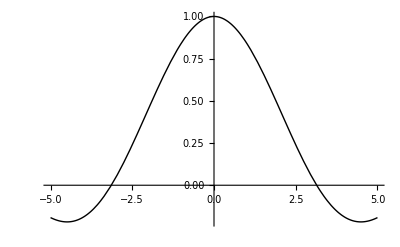
Если потребовать, чтобы A=1, т.е. изменим значение в 0 то получим новую функцию (непрерывную).

-Graphics-

Определение 20.3

Если в точке разрыва функции f существуют её конечные односторонние пределы, различные между собой, то такая точка называется точкой разрыва первого рода для f. 
(((lim_(x→a))_(x < a))_(x ∈ E))_ f(x) = f (a - 0) != f (a + 0) - (((lim_(x→a))_(x < a))_(x ∈ E))_ f (x)
При этом разность ∆f = f (a + 0) - f (a - 0) называется скачком функции в точке a.

Пример 20.2

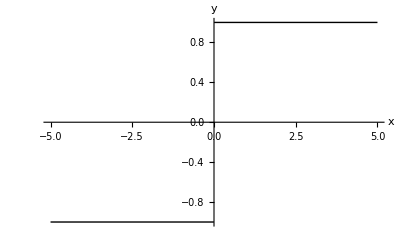
Функция sign x=Piecewise[{{1,, x>0,}, {0,, x=0,}, {-1,, x<0,}}]  в точке 0 имеет разрыв первого рода, т.к.  (lim_(x→a))_(x<0) sign x = -1, (lim_(x→a))_(x>0) sign x = -1 (скачок ∆_0 f = 2)

-Graphics-

Определение 20.4

Точка разрыва функции называется точкой разрыва второго рода, если в этой точке хотя бы один из пределов не существует или бесконечен.

Пример 20.3

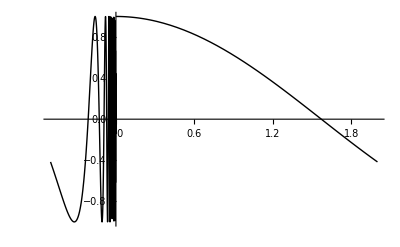
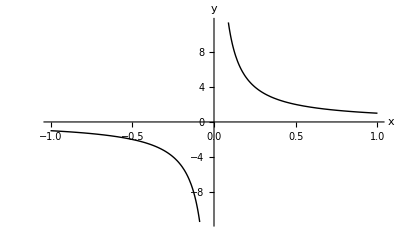
Каждая из функций:
f(x) = Piecewise[{{cos 1/x,, x<0,}, {cos x,, x≥0,}}] 

-Graphics-

g(x) = Piecewise[{{1/x,, x≠0}, {0,, x>0}}] 

-Graphics-

имеет в точке a=0 разрыв второго рода.

Определение 20.5.

Разрывная функция на множестве — это функция, имеющая хотя бы одну точку разрыва на области определения.

## 20.2. Некоторые понятия связанные с непрерывностью или точками разрыва функции.

Определение 20.6.

Функция f называется непрерывной слева (справа) в точке a, если для нее в этой точке предел слева (справа) существует и равен значению функции в точке a.
f(a-0)=f(a) ( f(a+0)=f(a) ).

Пример 20.4.

f(x)= Piecewise[{{x,, x≥0,}, {cos x,, x<0,}}]
f непрерывна справа от точки x=0.

Пример 20.5.

f(x)=sign(x)= Piecewise[{{1,, x>0,}, {0,
-1,, x=0,
x<0;}}]

имеет в точке a=0 разрыв первого рода, но не является в этой точке непрерывной ни слева, ни справа.

Упражнение 20.1.

Доказать, что для непрерывности f в точке a необходимо и достаточно, чтобы f была непрерывной одновременно слева и справа в этой точке.

Определение 20.7.

Функция f:[a;b]→ℝ называется кусочно непрерывной на отрезке [a,b], если она непрерывна на этом отрезке за исключением конечного числа точек разрыва первого рода или устранимых точек разрыва.

Если f непрерывна на [a;b], то множество ее точек разрыва пусто. Такие функции рассматриваются как частный случай непрерывной.

Примерами кусочно непрерывных на отрезке [a;b] функций являются:
1) f(x) = E(x) = [x]					2) f(x) = x - [x]

Функция непрерывна справа в точке x_n= n  ∈ ℕ, так как 
f(n + 0) = (lim_(x→n))_(x>n) sign x = -1 E(x) = n = [n] = f(n),
f(n - 0) =(lim_(x→n))_(x<n) E(x) = n - 1 < n = f(n).

## § 21. Локальные свойства непрерывной функции.

Определение 21.1.

Локальными называются такие свойства функций, которые определяются поведением функции в сколько угодно малой окрестности точки в ее области определения.
Таковыми являются, например, существование предела в точке, непрерывность в точке.
Укажем (без доказательства) основные локальные свойства непрерывных функций (они вытекают из свойств предела функций).

Теорема 21.1.

Пусть функция f: E -> ℝ непрерывна в точке a предельной для E. Тогда:
(a) f ограничена при x -> a, x ∈ E;
(в) если f(a) ≠ 0, то существует окрестность точки a, в которой f имеет тот же знак, что и число f(a).

Теорема 21.2. (о непрерывности арифметических комбинаций непрерывных функций)

Если функция f,g: E -> ℝ непрерывная в точке a∈ E, то в этой же точке непрерывна их сумма, разность, произведение и частность. 
(в последующих случаях значение знаменателя в точке a отлично от нуля).

Теорема 21.3 (о непрерывности композиций непрерывных функций)

Если функция f:E→Y непрерывна в точке a∈E, а функция g:Y→ℝ  непрерывна в точке b=f(a), то композиция g∘f:E→ℝ непрерывна в точке a. (Смотрите теорему о пределе композиции).

## § 22. Глобальные свойства непрерывности функции.

Определение 22.1

Глобальными называют такие свойства функции, которые зависят от значений функции во всей области ее определения. Например: четность, периодичность, ограниченность.

## 22.1. О структуре множества значений непрерывных функций.

Теорема 22.1 (Первая теорема Больцано-Коши о существовании корня непрерывной функции.

Пусть функция непрерывна на отрезке, и на его концах принимает значения разных знаков, тогда внутри отрезка существует точка, в которой функция обращается в нуль.

Пусть для функции f:[a,b]→ℝ известно, что f(a) · f(b) <0. Нужно доказать существование такой точки c∈(a;b), что f(c)=0. Применим метод половинного деления. Разделим отрезок [a;b] пополам точкой (a+b)/2. Если f((a+b)/2)=0, то полагаем с=(a+b)/2 и точка c найдена. Если же f((a+b)/2)≠0, то на концах одного из полученных отрезков(обозначим его [a_1;b_1] ) функция снова принимает значения разных знаков: f(a_1)·f(b_1)<0.

Продолжаем в случае необходимости этот процесс, мы либо на каком-то шаге получим точку c, где f(c)=a , либо получим последовательность вложенных отрезков:
[a;b]⊃[a_1;b_1 ] ⊃ ... ⊃ [a_n ;b_n ] (22.1)
Для каждого из этих отрезков f(a_n)·f(b_n)<0  и длина b_n -a_n  = (b-a)/2^n  → 0, n→+∞ .  Тогда по лемме о вложенных отрезках существует единственная точка c ϵ[a;b] , такая, что
	
(lim_(n→+∞))_ a_n =  lim_(n→+∞) b_n  =c .
Пользуясь непрерывностью функции f в точке c и переходя к пределу в неравенстве f(a_n) ·f(b_n)<0 , получаем f^2(c)⩽0 ⇒ f(c)=0.

Замечание 22.1
Для некоторых функций может существовать несколько точек c_k из [a;b] для которых f(c_k)=0 .

Пример 22.1

Докажем, что уравнение x^5-3x=1 имеет по крайней мере 1 вещественный корень на интервале (1;2):

Рассмотрим функцию f(x)=x^5 -3x-1, x∈[1,2].
Очевидно f (1)=-3, f(2)=25>0  , значит выполняется условие (22.1) ⇒   ∃c ∈(1;2): f(c)=0 .

Упражнение 22.1

Указать пример функции для которой Теорема о существовании корня неверна. (что-то поменять в условии)

Теорема 2.22. (2-я теорема Больцано-Коши о промежуточных значениях неприрывной функции)

Пусть f непрерывна на некотором промежутке и в точках a и b этого промежутка принимает разные значения:
f(a) = A, f(b) = B (A≠ B),
тогда для любого числа C, лежащего между A и B, найдется такая точка x_0 между a и b, что f(x_0) = C.

Не нарушая общности можно считать, что a < b, тогда отрезок [a ; b] лежит в исходном промежутке и функция φ(x) = f(x) - C непрерывна на отрезке [a; b]. Так как φ(a) · φ(b) = (A - C) · (B - C) < 0, то по первой теореме Больцано - Коши существует точка x_0 ∈ (a ; b), такая, что φ(x_0) - f(x_0) - C = 0, то есть f(x_0) = C.

## 22.2 Теорема Вейерштрасса о непрерывных функциях.

Теорема 22.3. (1-я теорема Вейерштрасса об ограниченности непрерывной функции)

Непрерывная на отрезке функция ограничена на этом отрезке.

ОП. f: [a ; b] ⟶ ℝ не ограничена (направлена сверху) на [a ; b]. Тогда: ∀ n ∈ ℕ ∃ x_0 ∈ [a ; b] : f(x_n) ⩾ n (22.2). Так как множество {x_n}_(n = 1)^∞ ∈ [a ; b], то из ограниченной последовательности (x_n) можно выделить сходящуюся подпоследовательность {x_n}_(n = 1)^∞ ⟶ x_n ∈ [a ; b]. В силу непрерывности функции f(x) в точке x_0

согласно определению непрерывности функции по Гейне должно быть
f(x_n_k)→f(x_0)— конечное число, но это невозможно, так как из (22.2) вытекает, что f(x_n_k)→+∞      
Противоречие возникло из-за того, что она не ограничена.  Аналогично можно прийти к противоречию, что f(x) не ограничена снизу.

Определение 22.2

Принято говорить, что функция  f:E→ℝ принимает на E своё наибольшее (наименьшее) значение, если существует такая точка x^*∈E (x_*∈E), что для всех x∈E выполняется неравенство: f(x)⩽f(x^*) (соответственно f(x)⩾f(x_*)). Наибольшее и наименьшее значения функции на множестве называется её экстремальными значениями.

Теорема 22.4 (2-я теорема Вейерштрасса)(об экстремальных значениях непрерывной функции)

Непрерывная на отрезке функция принимает на этом отрезке свои наибольшие и наименьшие значения.

В случае интервала (a , b) обе теоремы Вейерштрасса, вообще говоря, неверны.

Пример 22.2

Рассмотрим функции f_1(x)=1/x и f_2(x)=x, x∈(0,1).

f_1(x) — непрерывна и не ограничена на интервале (0,1), и f_2(x) — непрерывна, но не в одной точке интервала (0,1) не принимает наибольшего и наименьшего значений.

Упражнение 22.2

Привести примеры непрерывных f∈С [a,b] для которых верны обе теоремы Вейерштрасса.

Упражнение 22.3^*

Доказать, что при непрерывном отображении f≢const образом отрезка является снова отрезок:
f ∈ C_[a;b] ⇒  f : [a;b] →  [m;M].

## 22.3. Равномерная непрерывность. Теорема Кантора.

Если функция f :E→ ℝ непрерывна на множестве E, то по определению любой фиксированной точке x ∈ E:
∀ε > 0 ∃ δ > 0| ∀ε ∈ E : | t - x | < δ ⇒ | f(t) - f(x) | < ε .  (22.3)

Здесь вообще говоря δ = δ (ε, x), т.е. зависит не только от ε, но и от выбора x ∈ E. Если потребовать, чтобы δ зависело только от ε (независимо от точки x ∈ E), то мы приходим к определению нового класса функций.

Определение 22.3

Функция f : E → ℝ называется равномерно непрерывной на множестве E, если
∀ε > 0 ∃ δ > 0 | ∀x_1, x_2 ∈ E : | x_1 - x_2 | < δ (ε) | ⇒ |f (x_1) - f (x_2) | < ε.   (22.4)

Отметим некоторые факты, связанные с понятием непрерывности :

1. Если функция равномерно непрерывна на множестве, то она непрерывна на этом множестве в любой его точке.
Положив в 22.4 x_1=t, x_2= x  действительно равномерно непрерывная функция является непрерывной.

2. Если функция равномерно непрерывна на множестве E, то она является непрерывной на любом его подмножестве.
 Очевидно

3. Из непрерывности функции на множестве не вытекает равномерная непрерывность на этом множестве. (Можно показать на примерах)

Теорема 22.5 (теорема Кантора о равном.непр-ти)

Функция, непрерывная на отрезке, равномерно непрерывна на этом отрезке

ОП: пусть f∈ C[a;b] и не является равномерно непрерывной на [a;b]
Тогда записывая отрицание условия (22.4)
∃ ϵ_0 > 0 | ∀ n ∈ ℕ ∃ x'_n, x''_n ∈ [a, b] : | x'_n - x''_n | <1/n 
∧ | f (x'_n) - f (x''_n)|≥ ϵ_0     
(22.5)
Из определений последовательности x'_n∈[a;b] по принципу выбора в ℝ можно выделить сходящуюся подпоследовательность x_0∈[a;b]    x'_n_k → x_0 ∈ [a; b] и   x''_n_k →x_0
В силу непрерывности функции f в т. x_0∈[a;b] и из определения непрерывноти по Гейне должно быть: f(x'_n_k)→f(x_0) и f(x''_n_k)→f(x_0), 
т.е. |f(x'_n_k)-f(x''_n_k)|→0 при k→+∞, а это противоречит  (22.3/5)

Теорема Кантора может упростить доказательство непрерывности функций, непрерывных на открытых множествах, например на интервалах.
Для этого следует найти отрезок, который соединяет данное непрерывное множество и на которомм функция непрерывна.

## 22.4 Непрерывность обратной функции

Теорема 22.6(о существовании и непрерывности обратной функции)

Пусть f:E→ℝ - непрерывная и строго монотонная функция на множестве E. Тогда на множестве f(E) для нее существует обратная
функция f^-1:f(E)→E, которая также является непрерывной и строго монотонной в том же смысле, что и f.

Опускается

Таким образом для непрерывной функции (как для любой другой) существует обратная функция и её свойства тесно связаны со строгой  монотонностью исходной функции. В дополнение к этому утверждению относительно точек разрыва.

Теорема 22.7

Функция монотонная на множестве может иметь на этом множестве разрывы только 1 рода или устранимые разрывы.

## § 23. Непрерывность элементарных функций.

## 23.1 Основные элементарные функции.

Определение 23.1

Основными элементарными функциями действительной переменной называются функции каждого из следующих 5 типов, рассматриваемые в своей естественной области определения:
	I. Степенная функция;
	II. Показательная функция;
	III. Логарифмическая функция;
	IV. Тригонометрическая функция;
	V. Обратная тригонометрическая функция.

Рассмотрим каждый из этих типов и покажем, что функции непрерывны в своей естественной области определения.
I) Степенная функция — это функция вида y = x^α,  α ∈ ℝ — параметр.
Выделим несколько случаев в зависимости от значения параметра α.
I_1) α ∈ ℕ	x^α= x^n, n ∈ ℕ.
	f(ϰ) является непрерывной в ℝ, как произведение конечного числа непрерывной функции,  x^n =(ϰ · ϰ·...·ϰ)_n.

I_2) α∈ℤ \ ℕ, α≠0, т. е. α — целое отрицательное число. x^α=1/x^n, n∈ℕ — определена и непрерывна в ℝ\{0} как частное непрерывных функций со знаменателями отличными от нуля.
I_3) α=1/m, где m∈ℕ ⇒ y=x^(1/m)=x^(1/m). y=x^(1/m) непрерывна как обратная функции x=y^m, которая строго монотонна и непрерывна.
I_4) α∈ℚ, т.е. α=n/m, m∈ℕ, n∈ℤ. x^α=x^(n/m)=(x^(1/m))^n — композиция функций t=x^(1/m) и y=t^n. Область определения зависит от четности m и знака n. Функция x^(n/m) непрерывна во всей области определения как композиция непрерывных функций.
I_5)  α∈ℝ\ℚ, т. е. α — иррациональное число.
x^α при всех α определяется только при x>0 следующим образом:
	I_(5a)) если числа x>1 и α>0 фиксированы, то положим x^α=sup{x^r: r∈ℚ, r<α}  (рассмотрим все рациональные числа <α, берём супремум множества x^r). В качестве r можно брать рациональное приближение числа r с недостатком. С учетом теоремы о гранях это определение корректно, т. к. множество {x^r: r∈ℚ, r<α} ограничено сверху числом x^r_0, где r_0 — любое рациональное число >r.
	I_(5b)) аналогично при x∈(0; 1) и α>0 положим x^α=inf{x^r: r∈ℝ, r<α}.
	I_(5c)) при фиксированном x>0 и α<0: x^α=(1/x)^-α. замечание о непрерывности x^α, α∈ℝ\ℚ будет сделано ниже.

II Показательная функция

Показательная функция — это функция y=a^x , где x — аргумент, a — параметр, a>0, a≠1.
Область определения — множество ℝ. Область значений — (0;+∞).
При каждом x ϵ ℝ число a^x определяется подобно числу x^α.

Вид графиков при 
-Graphics-

exp(x):=e^x — экспонента.
Экспонента непрерывна при всех x ϵ ℝ, так как при любом фиксированном x: f(x,h)=e^(x+h)-e^x=e^x(e^h-1)∼e^x·h→0, h→0, то есть приращение аргумента соответствует приращению функции.

Показательная функция a^x также непрерывна в любой точке x ϵ ℝ она представима в виде a^x=e^(x·ln a); t=x ln a, y=e^t.

III Логарифмическая функция

Логарифмическая функция — это функция, обратная к показательной. 
Обозначения: y=log_a x, где a — параметр, a>0, a≠1.
При a=e: y=ln x — натуральный логарифм.
Область определения  — (0;+∞), область значений — (-∞;+∞).

График
-Graphics-

Логарифмическая функция y=log_a x непрерывна как обратная к показательной x=a^y. Теперь можно утверждать, что и степенная функция непрерывна как композиция непрерывных функций, так как x^α=e^(α ln x) , при α > 0 она непрерывна  на [0;+∞).

IV. Тригонометрические функции — это функции sin x , cos x, tg x, ctg x, определяемые для аргумента x, выраженного в радианах.

Функции sin x и cos x при всех x ∈ ℝ непрерывны,
так как 0 ≤  |sin( x+h) - sin x|=|2 cos(x+h/2) ·sin h/2|≤|h|→ 0 при h→ 0,
	0 ≤  |cos(h+x) - cos x|=|2 sin(x + h/2) ·sin h/2|≤ |h|→ 0.

Из непрерывности функций sin x и cos x вытекает непрерывность
функций tg x= (sin x)/(cos x) при всех x≠π/2+k π,
	и ctg x=(cos x)/(sin x) при x≠k π.

V. Обратные тригонометрические функции
Рассматривая тригонометрические функции на множествах, где они строго монотонны, а именно
1) y=arcsin x, x∈[-1; 1] — функция, обратная y=sin x: [- π/2; π/2]→ [-1;1];
2) y=arccos x, x∈[-1; 1] — функция, обратная y=cos x: [0, π]→ [-1;1];
3) y=arctg x, x∈ℝ — функция, обратная y=tg x: (- π/2; π/2)→ (-∞;+∞);
4) y=arcctg x, x∈ℝ — функция, обратная y=ctg x: (0; π)→ (-∞;+∞).

Обратные тригонометрические функции непрерывны по теореме обратности  непрерывной функции.

## 23.2. Элементарные функции.

Определение 23.2

Элементарными функциями называются все основные элементарные функции, а также функции, полученные из основных с помощью конечного числа арифметических операций и композиций.

Из этого определения вытекает, что если f, g — элементарные функции, то функции f±g, f· g, f/g, f∘g, g∘f — тоже элементарные функции.

Теорема 23.1

Каждая элементарная функция непрерывна во всех точках своей естественной области определения.

Все основные элементарные функции непрерывны в своей естественной области определения. Любую элементарную функцию можно получить из основных с помощью конечного числа арифметических операций и операции композиции. Но такие операции снова приводят к непрерывной функции. Поэтому любая элементарная функция непрерывна в своей естественной области определения.

# Глава 4. Дифференцируемые функции. Производная и её приложения.

Разделы анализа, связанные с понятиями дифференцируемости и производной, называются дифференциальным исчислением.

## § 24. Дифференцируемые функции. Понятия производной и дифференциала.

## 24.1. Основные определения.

Точка внутренняя для множества, если содержится в множестве вместе с некоторой окрестностью.

Определение 24.1

Функция f:E→ ℝ называется дифференцируемой во внутренней точке x∈E, если существует такое число A, что приращение функции f в точке x можно представить в виде
f(x+h)-f(x)=A ·h+O(h) при h→ 0.     						(24.1)
Функция называется дифференцируемой на множестве, если она дифференцируема в каждой точке этого множества.

Отметим, что постоянная A в (24.1) не зависит от h, но, вообще говоря, зависит от x (так есть A=A (x)).
Другая запись условия дифференцирования (24.1):
△ y=A·△ x+O(△ x), △ x→ 0.

Определение 24.2

Пусть y=f(x)  — функция, дифференцируемая в точке x, тогда дифференциалом функции f в точке x называется входящим в равенство (24.1) функция A·h от приращения аргумента.

Для дифференциала  y=f(x) используются следующие обозначения:
d y=A ·h=A·△ x=d f=d  f(x)=d f(x,h).

Определение 24.3.

Производной функции y=f(x) в точке x называется конечный предел отношения приращения функции к приращению аргумента, когда последний стремится к нулю.

Обозначения:
ƒ'(x) = lim _(h→0) (f(x+h)-f(x))/h=lim _(△ x→0) (f( x + △ x) - f(x))/(△ x)=lim _(△ x→0)   (△ y)/(△ x).			    (24.2)
Для производной используются и другие обозначения:
y'=y'(x)=(d y)/(d x)=(d f)/(d  x)=(d f(x))/(d x)=d/(d x)f(x).

Пример 24.1.

Пусть f(x)=C=const.

ƒ'(x) =lim _(h→0) (f(x+h)-f(x))/h=lim _(h→0) (C - C)/h=0, т.е. ƒ'(x) ≡0.

Пример 24.2.

Пусть f(x)=x .

Имеем для любого x:  lim _(h→0) ((x+h)-x)/h=lim _(h→0) h/h=1, т.е. ƒ'(x) ≡1.

Замечание 24.1.
Введенную в определении 24.3 производную называют также конечной производной, желая тем самым подчеркнуть, что рассматриваемый в (24.2) предел является конечным.
Ниже будет введено понятие бесконечной производной, когда предел 24.2 является бесконечным.

Замечание 24.2.
Точка x, в которой рассматривается производная всегда является конечной.

## 24.2. Условия дифференцируемости функции в точке.

Теорема 24.1 (Необходимое условие дифференцируемости)

Если функция дифференцируема в точке, то она и непрерывна в этой точке.

Запишем условие (24.1)  в виде:
 f (x + h) = f(x) +A·h + o(h) , h→0  ,
 переходя к пределу при  h→0 , получим 
lim _(h→0) f (x + h) = f(x) ,
что и означает непрерывность в точке x.

Отметим, что из непрерывности функции в точке не всегда вытекает дифференцируемость ее в этой точке.

Пример 24.3.

Функция  y = | x | непрерывна на ℝ (в частности в т. x = 0) , но не является дифференцируемой в т. x = 0 , ибо lim _(h→0) (f( 0 + h) - f(h))/h= lim _(h→0) (|h|)/h=lim _(h→0) sign h  
не существует (см. пример 15.1) .

Теорема 24.2.(аналогичный критерий дифференцируемости функции в точке)

Дифференцируемость функции в точке равносильна существованию у нее  конечной производной в этой точке.

Условия (24.1) можно записать в равносильном виде:
f(x + h) - f(x) = A · h + 0(h)⟺ lim _(h→0)  (f(x + h) - f(x))/h = A , но это и  означает что дифференцируемость функции f в т. x равносильна существованию в ней производной.       f'(x) = A.

Таким образом, с учетом равенства  A =ƒ'(x)  выражение для дифференциала функции f в т. x можно записать в виде:   d y =ƒ'(x) △ x .
В частном случае  функции  y(x) = x  имеем (см.прим 24.2):  
 d y = (x)^′·  △ x = △ x  . 
Отсюда еще одно обозначение для приращения аргумента:  
 △ x = d x  .
И еще: формула для дифференциала функции:   
 d y = ƒ'(x) · △ x .

Последнее равенство объясняет обозначение для прямой ƒ'(x)=(d y)/(d x), которое следует рассматривать не как единый символ, а как отношение дифференциалов.

## 24.3. Геометрический смысл производной и дифференциала.

Напомним, что графиком функции f: (a,b)→  ℝ называется множество 
Γ_f={(x, y): x ∈ (a, b), y=f(x)}.
-Graphics-

Определение 24.4.

Прямая l называется касательной к графику Γ_f в точке M_0 (M_0 ∈ Γ_f), если 
	1) точка M_0 лежит на прямой l;
	2) расстояние от точки M_0 графика до прямой l является бесконечно малым по сравнению с расстоянием между M и M_0при M -> M_0.

Будем говорить, что прямая плоскости является
	— наклонной, если она образует острый угол с осью O x (∈(0; ℼ/2));
	— вертикальной, если она перпендикулярна оси O x.

Справедлива

Теорема 24.3. (геометрический критерий дифференцируемости функции в точке)

Существование наклонной касательной к графику функции y=f(x) в точке M_0 (x_0; y_0)∈ Γ_f равносильно существованию конечной производной ƒ'(x_0). Эта производная равна угловому коэффициенту касательной в точке касания M_0 (то есть tg α, α — наклон касательной).
 f^′(x_0) = tg α 
 -Graphics-

Уравнение касательной к графику функции y=f(x) в точке (x_0,y_0) имеет вид y-y_0=f' (x_0)(x-x_0)  , где y_0=f(x_0).
Геометрический смыл дифференциала функции.
d y=f'(x_0)(x-x_0)d x.
На рисунке: 
d x=M_0 C — приращение аргумента.
Δ y=CM — приращение функции, соответствующее d x.
d y=BC — дифференциал.
-Graphics-
Геометрически дифференциал — это приращение ординаты касательной, соответствующее смещению аргумента d x. Чем меньше d x, тем точнее приближенное равенство. Δ y  = d y
Точное равенство: Δ y=d y+O(d x).

## 24.4. Односторонние и бесконечные производные.

Если считать, что в определении производной (формула 24.2) предел является односторонним, то мы приходим к пониманию односторонних производных:
	f'_-(x_0)=(lim _(x→x_0))_(x<x_0)(f(x)-f(x_0))/(x-x_0)=lim _(h→-0) (f(x+h)-f(x))/h — производная слева. 
	f'_+(x_0)=(lim _(x→x_0))_(x>x_0)(f(x)-f(x_0))/(x-x_0)=lim _(h→+0) (f(x+h)-f(x))/h— производная справа. 				(24.3)

Теорема 24.4 (а).

Для существования конечной производной в точке x_0 необходимо и достаточно, чтобы в этой точке f была непрерывна, и у нее существовали и совпадали конечные производные слева и справа.

Теорема 24.4 (б).

Если f имеет в точке конечную производную слева (справа), то она является непрерывной слева (справа) в этой точке.

-Graphics-

Если обе односторонние производные (24.3) конечны, то левая и правая касательные имеют следующие уравнения:
	y-y_0=f'_-(x_0)(x-x_0), 	y-y_0=f'_+(x_0)(x-x_0).

-Graphics-

Пример 24.4.

f(x)=|x|,
f'(0) не существует (следствие примера 24.3),
f'_-(0)=lim _(h→-0) (|0+h|-|0|)/h=lim _(h→-0) (|h|)/h=-1,
f'_+(0)=lim _(h→+0) (|0+h|-|0|)/h=lim _(h→+0) (|h|)/h=1.

Определение 24.6.

Функция f называется кусочно дифференцируемой на промежутке, если его можно разбить на конечное число промежутков, внутри которых функция дифференцируема, а на концах промежутка не только имеет предельные значения, но и односторонние производные (при условии, что на этих концах в качестве значений функции взяты ее предельные значения).

Дифференцируемая на промежутке функция рассматривается также, как и кусочно дифференцируемая на нем (промежуток разбить на одну часть).
Примерами кусочно дифференцируемых на любом промежутке функций могут служить:
	1) f(x)=|x| ;
	2) f(x)=sign x;
	3) f(x)=E(x)=[x].
	4) f(x)=x- [x].
	-Graphics-

Определение 24.7

Принято говорить, что функция  f → ℝ  имеет в точке x бесконечную производную, если в этой точке она удовлетворяет следующим условиям: 
	1) f —  непрерывна,
	2) ∃  lim_(h→0) |(f(x + h) - f(x))/h|=+∞.

Односторонние бесконечные производные могут возникать, когда один из пределов (24.3) или оба сразу бесконечные. При этом если обе производные f'_±(x_0) = +∞ ( или f'_±(x_0) = -∞), то существуют f'(x_0) = +∞ (или соответственно f'(x_0) = -∞). Во всех остальных случаях график функции имеет вертикальную касательную в этой точке.

Пример 24.5

Пусть f(x) =  x^(1/3), x_0 = 0;

f'_-(0) =  lim_(h→-0) (f(0 + h) -f(0))/h=  lim_(h→-0) h^(1/3)/h=+∞=f'_+(0)=f'(0).
Однако функция не является дифференцируемой в точке 0.
-Graphics-

Пример 24.6

Пусть f(x) =  √(|x|), x_0 = 0;

f'_-(0) = -∞,f'_+(0) = +∞ ⟹ ∃ f'(0) = ∞.
-Graphics-

Если функция имеет на промежутке E конечную производную, кроме конечного числа точек, где производная +∞, -∞, то будем говорить, что f — дифференцируема в ℝ̃ .

## § 25. Основные правила дифференцирования.

Дифференцированием функции называется операция нахождения ее производной.

Теорема 25.1( производная арифметической комбинации )

Пусть u = u(x), v = ν(x) — дифференцируемые в точке x и C — постоянная.
Тогда в точке x дифференцируемы сумма, разность, произведение и частное этих функций (при условии, что знаменатель отличен от 0) и справедливы формулы:
(a)  ( u±v) '= u'±v' ;
(b) ( u · v)  = u' v+u v'^;
(c) (C ·u )'= C·u ' ;
(d) (u/v) = (u' v - u v')/v^2, если v(x)≠0.

Докажем пункт (b)

Очевидно,  (u+v)'= lim _(h→ 0) (u(x+h) · v(x+h) - u(x)·v(x))/h= ♁ .
Представим разность в числителе в виде суммы двух выражений, каждое из которых содержит приращение только одной функции u или v.
С этой целью рассмотрим выражение
u(x+h)=[u(x+h) - u(x)]+u(x) 
и подставим его  в исходное.
Тогда, используя свойство предела функции и необходимость условия дифференцируемости (непрерывность), получим:
♁=  lim _(h→ 0)([u(x+h) -u(x)]v(x+h) + u(x)[v(x+h)-v(x)])/h = lim _(h→ 0)(u(x+h)-u(x))/h u(x+h)+ lim _(h→ 0) u(x)(v(x+h)-v(x))/h= u'(x)·v(x)+u(x)·v'(x). 
Пункт (a) доказывается непосредственно по определению производной.
(c) вытекает из (b) при C≡v(x).
(d) с помощью того же представления для u(x+h), что и в пункте (b).

Упражнение 25.1

Привести доказательство утверждения (а) и (d) в теореме 25.1.

Упражнение 25.2

Доказать, что если u_1, u_2, ..., u_n — функции, дифференцируемые в одной и той же точке, то в этой точке: (u_1·u_2· ...·u_n)'=u_1'·u_2·...·u_n+u_1·u_2'·...·u_n+...+u_1·u_2·...·u_n'.

Пример 25.1

Покажем, что если f(x)=|x|, то существует f'(x)=sign x, x≠0.

1) так как f(x)=|x|=Piecewise[{{x,, x⩾0}, {-x,, x<0}}] , то в любой точке x>0 на оси. (Пример 24.2 ) f'(x)≡1.
2) если x<0, то f(x)=-x=-1·x и на оси (теорема 25.1) f(x)=(-1·x)=-1·(x)'=-1.
3) в точке x=0 функция не имеет производной (см. пример 24.3), кроме того график функции в точке x не имеет касательной.

Теорема 25.2 (производная композиций функций)

Пусть функция u=f(x) дифференцируема в точке x, а функция y=g(u) дифференцируема в соответствующей точке u=f(x), тогда композиция y=(g∘f)(x)=g(f(x)). Справедлива формула: 
(g∘f)'(x)=(g(f(x)))'=g'(f(x))·f'(x) 					 (25.1)
То есть производная композиции дифференцируемых функций равна произведению производных внутренних и внешних функций в соответствующих точках.

Так как внешняя функция y=g(u) по условию дифференцируема в точке u=f(x), то для нее можно записать условие дифференцируемости:
 Δy=g'(u)Δ u+λ(Δ u)·Δ u, 							(25.2)
 где λ(Δ u)→0 при Δ u→0.
 Придадим аргументу x внутренней функции u=f(x) приращение Δ x≠0 и разделим равенство (25.2) на Δ x:
(Δ y)/(Δ x)=g^′(u) (Δ u)/(Δ x) + d (Δ u) (Δ u)/(Δ x)           	   	 				(25.3)
так как u = f(x) дифференцируема в точке x, то она и непрерывна
в этой точке, то есть Δ u → 0 при Δ x → 0 .
Тогда из (25.3) вытекает, что существует
lim _(Δ x → 0) (Δ y)/(Δ x) = g^′(u) lim _(Δ x → 0) (Δ u)/(Δ x) + lim _(Δ x → 0) d (Δ u) (Δ u)/(Δ x) = g^′(u) u^′(x) = g^′(f(x)) f'(x).

Пример 25.2

Пусть y = ((x - 1)/(x + 1))^2.

Найдем производную y' по
правилу дифференцирования композиции.
Представим y как композицию:
y = g(u(x)); где u = (x - 1)/(x + 1) — внутренняя, а
g(u) = u^2 — внешняя.
Имеем:
	   y^′ = d/(d x)·((x-1)/(x+1))^2= 2u(x) u'(x) = 2 (x-1)/(x+1)·((x-1)/(x+1))^′ = 2(x-1)/(x+1)·(x+1-x+1)/( x +1)^2 = (4(x-1))/(x+1)^2.

Формула, аналогичная (25.1), справедлива для композиции
трех и большего числа функций. Например,
	(h ·g·f)^′(x) = f^′(x)·g^′(f(x))·h^′(g(f(x))).

Теорема 25.3	(об инвариантности формы первого дифференциала)

Дифференциал композиции y = f(x(t)) можно записать
в форме d y = f^′(x)·d x , то есть так же,
как, если бы переменная x была независимой.

используя формулу (25.1), имеем: d y = f^′(x(t))·d x = f^′(x(t))·x^′(t)·d t = f^′(x)d x.

Теорема 25.4	(производная обратной функции)

Пусть функция y = f(x) , x ∈ [a ,b] строго монотонна,
непрерывна на [a ,b], имеет производную в локальной точке x ∈ [a ,b],
тогда обратная функция x = f^-1(y) имеет производную имеет производную в точке y = f ( x ), причем

 ( f^(− 1) ) '( y ) = 1/(f' ( x )).

Пусть △ x приращение аргумента исходной функции  в точке x . Обозначим △ y=f ( x +△ x )−f( x )  приращение функции в точке 
x Так как обе функции f и f^-1 строго монотонны и непрерывны, то (△ x→0)_(△ x ≠ 0)⇔△ y→0,△ y≠0.
Учитывая это, имеем:
(f^(−1))'(y) = lim _(△ y→ 0)  (f^-1 (y + △ y )-f^-1(y))/(△ y) = lim _(△ y→ 0)  ((x + △ x ) - x)/(△ y) =lim _(△ y→ 0)  (△ x)/(△ y) = lim _(△ y→ 0)  1/((△ x)/(△ y))  = 1/(lim _(△ y→ 0)  (△ x)/(△ y)) = 1/(f'(x)).

Замечание 25.1.
 Если f' ( x )≠0 в т. x , то производная отображения функции (f^-1)(y) конечна в т. y=f ( x ).

## § 26. Вычисление табличных производных

Используя стандартные пределы для функций, а также основные  правила дифференцирования, установим формулы табличных производных (т.е. производных основных  элементарных и некоторых других важных функций).

## 26.1. Производная степенной функции

Установим, что при каждом α∈ℝ  во всей естественной  области определения  D(f) степенной функции x^α справедлива формула
(x^α)' = α x^(α - 1) 								(26.1) 
1)Докажем сначала ∀x∈D ( f ) ,x ≠0 Считая приращение h аргумента таким , что x+h∈D(f) , имеем:
(x^α)' = lim _(h → 0) ((x + h)^α - x^α)/h = lim _(h → 0) ((1+ h/x)^α - 1)/h x^α = lim _(h → 0) ((1+ h/x)^α - 1)/(h/x)x^(α - 1)=d x^(α - 1) .
2) Пусть теперь x=0∈D ( f )    (Тогда необходимо α > 0 в этом случае)
((x^α)')_(| x =0) =lim _(h → 0) ((0+ h)^α - 0^α)/h = lim _(h → 0) h^(α-1) = {0 , α>1;          
 1 , α = 1;        
∞ ,0<α <1. 
Что согласуется с формулой (26.1).

## 26.2. Производная логарифмической функции.

Рассмотрим сначала 
1) y=ln x при любом фиксированном x>0 имеем:
y'=lim _(h→ 0) (ln (x+h)-ln x)/h=lim _(h→ 0) 1/h ln (1+h/x)=lim _(h→ 0) 1/x(ln (1+h/x))/(h/x)=1/x,
таким образом:
(ln x)'=1/x, x>0.
2) Пусть y=log_a x, x>0, при a=e ⇒ 1).
Так как log_a x=(ln x)/(ln a), то (log _a x)'=1/(x ln a), x>0.

3) Пусть, наконец, y=log _a|x|. Рассмотрим в данном случае композицию:
y=log_a t, t=|x| и, применяя теорему 25.2, получим при x≠0 следующее:
y'=1/(t ln a)t'(x)=(sign x)/(|x|ln a)=1/(x ln a),
таким образом: (log _a|x|)'=1/(x ln a), x≠0 .
-Graphics-

## 26.3. Производная показательной функции.

Производную от функции  y = a^x   найдем с помощью теоремы о производной обратной функции: так как y=a^x⇔x=log_a y, то d/(d x)a^x=1/(d/(d y)log_a y)=1/(1/(y ln a))=y ln a=a^x ln a.
Таким образом: 
(a^x)'=a^x ln a , x∈ℝ  
Отсюда при a=e имеем:
(e^x)'=e^x.

## 26.4. Производная от тригонометрических функций.

1) При  ∀∈ℝ:
	(sin x)'=lim  _(h→0) (sin(x+h)-sin(x))/h  = lim _(h→0) (2cos(x+h/2)·sin(h/2))/h=lim _(h→0) cos(x+h/2)·(sin(h/2))/(h/2)=cos x ,
    то есть   (sin x)'=cos x ,  x∈ℝ.

2) При  ∀x∈ℝ:
	cos x=sin(π/2-x)⟹(cos x)' =d/(d x)·sin(π/2-x)=cos(π/2-x)·(π/2-x)'=-sin x,
    таким образом (cos  x)'=-sin x , x∈ℝ.
    
3)  При     ∀x≠π/2+π·k , k∈ℤ:
	(tg x)'=((sin x)/(cos x))'=(cos x·cos x-sin x·(-sin x))/(cos^2 x)=1/(cos^2 x),
    таким образом (tg x)'=1/(cos^2 x), x≠ℼ/2+ℼ·k, k∈ℤ.
    
4) При   ∀x≠π·k ,k∈ℤ:
	(ctg x)'=((cos x)/(sinx x))'=(-sin x·sin x-cos x·cos x)/(sin^2 x)=-1/(sin^2 x),
    таким образом (ctg x)'=-1/(sin^2 x), x≠ℼ·k, k∈ℤ.

## 26.5. Производные от обратных тригонометрических функций.

Используем теорему о производной обратной функции
1) y=arcsin x, x∈(-1,1), так как обратная функция x=sin y, y∈(-ℼ/2,ℼ/2), то 
	(arcsin x)'=1/(d/(d y)·sin y)=1/(cos y)=1/(√(1-sin^2 y))= 1/(√(1-x^2)), |x|<1.
    Отсюда y'_∓(±1)=+∞
    	(arcsin x)'= 1/(√(1-x^2)), |x|<1.

Упражнение 26.1

Доказать формулы:
	(arccos x)'= -1/(√(1-x^2)), |x|<1;
	(arcctg x)'=-1/(1+x^2), x∈ℝ;
	(arctg x)'=1/(1+x^2), x∈ℝ.

## 26.6. Гиперболические функции и их производные.

Гиперболические функции вида определяются формулами:

Синус гиперболический:

sh(x) = (e^x- e^-x)/2
Косинус гиперболический:

ch(x) = (e^x+ e^-x)/2

Тангенс гиперболический:

th(x) = (sh x)/(ch x)

Котангенс гиперболический:

cth (x) = (ch x)/(sh x)=1/(th x)

Основные свойства гиперболических функций

1) Функции sh x , ch x, th x определены и непрерывны на всей вещественной оси ℝ функция cth x определена и непрерывна на ℝ \ { 0 } , ибо sh x=0 ⇔ e^x - e^-x = 0 ⇔ e^(2x) - 1 =0 ⇒ 2x = ln 1 = 0
2) Легко проверить следующие тождества для гиперболических функций:
ch^2 x−sh^2  x=1;
ch^2 x−sh^2  x = ch 2x;
sh 2x = 2 sh x ch x;
ch^2 x = (ch 2x +1)/2;
sh^2 x = (ch 2x -1)/2;
1- th^2 x = 1/(ch^2 x);
cth^2 x - 1 =  1/(sh^2 x).

Производная гиперболических функций
	(sh x)'= ((e^x - e^-x)/2)' = (e^x - ( -e^-x))/2 = (e^x + e^-x)/2 = ch x ;
	(ch x)' = ((e^x + e^-x)/2)' = (e^x + ( -e^-x))/2 = (e^x - e^-x)/2 = sh x;
	(th x)' = ((sh x)/(ch x))' = (ch x · ch x - sh x · sh x)/(ch^2 x) = (ch^2 x - sh^2 x)/(ch^2 x) = 1/(ch^2 x) ;
	(cth x)' =((ch x)/(sh x))' = (sh x · sh x - ch x · ch x)/(sh^2 x) = (sh^2 x - ch^2 x)/(sh^2 x) = -1/(sh^2 x).
Графики th x и cth x можно получить рассматривая представления: 
 	y = th x = (e^x - e^-x)/(e^x + e^-x)= (e^(2x)-1)/(e^(2x)+1)=1 - 2/(e^(2x)+1);
	y = cth x = 1/(th x) = (e^(2x)+1)/(e^(2x)-1)=1+2/(e^(2x)-1).
Графики гиперболических функций
-Graphics-

## 26.7. Таблица производных.

f(x) | f'(x) | Ограничения
сonst | 0 |  
x^α | α x^(α - 1) | x>0, при α иррац. или α = n/m∈Q, m =2k
√x | 1/(2 √x) | x > 0
1/x | -1/x^2 | x≠0
|x| | sign x | x≠0
α^x | α^x·ln α | α>0, α≠0
e^x | e^x | □
log_α x | 1/(x · ln α) | x > 0
ln x | 1/x | x > 0
sin x | cos x | □
cos x | -sin x | □
tg x | 1/(cos^2 x) | π/2+ 2πn, n∈ℤ
ctg x | -1/(sin^2 x) | 2πn, n∈ℤ

## 26.8. Дифференцируемость элементарных функций.

Теорема 26.1 (a)

Любая элементарная функция, в представлении которой не участвует композиция основных элементарных функций, дифференцируема во всех точках своей естественной области определения.

Теорема 26.1 (b)

Если в представление элементарной функций входит такая композиция, то эта функция дифференцируема в тех внутренних точках естественной области определения, где выполняется теорема о дифференцируемости композиции.

Теорема 26.1 (c)

Производная элементарной функции является элементарной функцией.

Пример 26.1

Рассмотрим  y = |x|. Точка x_0 — точка естественной области определения. Функция y представлена в виде композиции основных элементарных функций y =√t, t =x^2. В точке t_0=0 (ей соответствует точка x_0=0) не выполняется теорема о дифференцировании композиции (внешняя функция √t не имеет конечной производной), поэтому y = |x| не дифференцируема в точке x_0=0.

## § 27. Производные и дифференциалы высших порядков.

## 27.1. Производные высших порядков. Определение и обозначение.

Производная ƒ'(x) называют также первой производной или производной первого порядка от f(x).

Определение 27.1.

Если ƒ'(x) — непрерывная функция на E, то ƒ'(x) называется непрерывно дифференцируемой функцией на E.
	Обозначение: f(x)∈C'(E).

Определение 27.2.

Производной второго порядка от функции f в точке x называется производная от первой производной и обозначается:
	f''(x):= (f')'(x)
Производная n-го порядка f^(n)(x) определяется по индукции равенства:
	f^(n)(x) := (f^(n-1))'(x) 								(27.1)

Чтобы формула (27.1) была верна и для первой производной (то есть для n=1), обычно полагают
	f^(0)(x) := f(x)

Определение 27.3.

Производные f'', f^(′′′), ...  называется производными высших порядков.
Применяются следующие обозначения n-ых производных от функции y = f(x):
	f^(n)(x) = y^(n) = (d^n y)/(d x^n)=  d^n/(d x^n)f(x)
Обозначение  f^(n)(x) или y^(n) , как правило используют лишь при n>=4 ( и при n = 0)

Определение 27.4.

Функция f:E-> ℝ называется n-кратно дифференцируемой на открытом множестве E, если в любой точке x ∈ E она имеет производные до порядка n включительно. Функция  f:E-> ℝ называется бесконечно дифференцируемой на множестве E если в каждой точке  x ∈ E она имеет производные любого порядка n.
Принято обозначать C^n(E) множество функций f: E ->ℝ, имеющие непрерывные на E производные до порядка n включительно. Символом C^∞(E) обозначается пространство бесконечно дифференцируемых на E функций.

## 27.2. Вычисление производных высших порядков от некоторых элементарных функций. Формула Лейбница.

1. Рассмотрим многочлен степени n от x:
P_n(x)=a_0+a_1 x+...+a_n x^n, (a_n ≠ 0 )
его последовательные производные равны:
P'_n(x)=a_1+2 a_2 x+...+n a_n x^(n-1)=Q_(n-1)(x);
P''_n(x)=2! a_2+3·2 a_3 x+...+n(n-1)a_n x^(n-2)=Q_(n-2)(x) ;
. . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . 
P_n^(n)(x)=n!a_n=Q_0(x).
Поэтому:
P_n^(k)(x)=Piecewise[{{Q_(n-k)(x), k⩽n;, }, {0, k>n., }}]

2. Покажем, что (sin x)^(n)=sin(x+(π n)/2), n ∈ ℕ, x ∈ ℝ 					(27.2)
Применим ММИ:
1) при n=1, (sin x)'=sin(x+π/2 )=cos x – верно.
2) Покажем, что если n ∈ ℕ, то (sin x)^(n)=sin(x+(π n)/2)⇒(sin x)^(n+1)=sin(x+((n+1)π)/2).
    Пусть (27.1) верна при каждом n, тогда
    (sin x)^(n+1)=((sin x)^(n))'=(sin(x+(π n)/2))'=(cos(x+(n π)/2)(x+(n π)/2)'=cos(x+(π n)/2)=⊗;
    верно cos t=sin(t+π/2);
    ⊗=sin(x+(π n)/2+π/2)=sin(x+((n+1)π)/2)=(sin x)^(n+1)

Упр. 27.1

Доказать формулы n -х производных следующих функций:
3) (cos x)^(n)=cos(x+(π n)/2), n ∈ ℕ, x ∈ ℝ;
4) (a^x)^(n)=(a^x(ln a))^n, n ∈ ℕ, x ∈ ℝ;
5) d^n/(d x^n)ln(1+x)=(-1)^(n-1) · ((n-1)!)/(1+x)^n, n ∈ ℕ, x>-1.
6) d^n/(d x^n)(1+x)^α=α(α-1)· ... · (α-n+1)(1+x)^(α-n), n ∈ ℕ, x ∈ D(f).

Производную n-го порядка от произведения двух функций можно находить, последовательно вычисляя.
Однако для этого существует более простое и наглядное правило.
Оно напоминает формулу бинома Ньютона:
(a + b)^n=∑ _(k=0)^n C_n^k a^(n-k)b^k=∑ _(k=0)^n (n!)/(k!(n-k)!)a^(n-k)b^k ← бином.

Теорема 27.1. (о производной n-го порядка для произведения 2-х функций)

Если функции  𝓊=𝓊(x) и v=v(x) имеют в точке x конечные производные до порядка  n включительно, то в этой точке справедлива формула Лейбница:

(𝓊·v)^n=∑ _(k=0)^n C_n^k 𝓊^(n-k)v^k=𝓊^n v+C_n^k 𝓊^(n-k)v^k+...+𝓊·v^n 			      	    (27.3.)

Доказательство(методом математической индукции).

При n=1 и n=2 формула (27.3.) легко проверяется.
Затем с использованием этой формулы вычисляют (𝓊·v)^(n+1)=((𝓊·v)^(n))'.
В итоге получаем формулу 27.3., где вместо n фигурирует n+1 при этом используется лемма Паскаля (для биномиальных координат векторов).
C_n^k+C_n^(k-1)=C_(n+1)^k.

## 27.3. Дифференциалы высших порядков.

Напомним, что если y=𝒻(x) дифференцируема на множестве, то её дифференциалом (или 1-м дифференциалом) называется выражение:
𝒹 y=𝒹𝒻(x)=𝒻'(x)𝒹 x.
Вид нового выражения  не зависит от того является ли x независимой переменной или является функцией x(t) .
Отметим, что для суммы и произведения функций 𝓊(x) и v(x) имеют место формулы:
𝒹(C)=0, (C=const).

d(u±v) = (u±v)' d x = d u ±d v;
d(u·v)=(u v)' d x =(u ' v+u v')d x=v·d u + u·d v ;				(27.4)
d(u/v) = (u/v)' d x = (v d u - u d v)/v^2 (v ≠0)  .

Дифференциалы высших порядков (как и производные) определяются индуктивно.

Определение 27.5

Дифференциалом n-го порядка (или n-ым дифференциалом) d^n y  от функции y =f(x) в некоторой точке называется дифференциал в этой точке от её (n-1) -го дифференциала d^n y =d(d^(n-1)y)  .
При этом дифференциал второго порядка d^2 y определяется исходя из правила (27.4) для произведения, т.е.
d^2 y=d(d y) = d(ƒ' (x) d x) =  d(ƒ' (x)) d x + ƒ' (x)·d(d x) = ƒ'' (x) (d x)^2+ ƒ' (x) d^2 x.

Замечание 27.2. 
1) Обозначение d x^2 понимается как (d x)^2, а не как дифференциал функции y = x^2, который обознается так: (d(x))^2.
2) При вычислении дифференциалов высших порядков   важно учитывать, что для независимой переменной x ее дифференциал d x  есть произвольное независящее от x  число  (d x) = Δ x которое при дифференциации по x   следует рассматривать как постоянный множитель : d^2 x= d(d x)= 0
Таким образом,   в случае независимой переменной x  следует считать, что:
d^2 x = d^3 x  = ... = d^n x = ... = 0. 
Тогда из (27.4) будем иметь:
 d^2 y = d(d y)=d(y' ·d x) = d y'·d x = (y''·d x)=y^(′′)·d x^2.
  d^3 y = d(d^2 y)=d(y'' ·d x^2) =  (y'''·d x)·d x^2=y^(′′′)·d x^3.
 По индукции можно доказать, что в случае независимой переменной
 d'' y = y^(n)(x)·d x^n .									       (27.5)
 3)Дифференциалы высших порядков (при n>=2 ) для функции y = f(x) не обладают свойством инвариантности в случае , когда аргумент является зависимой переменной (исключая случай линейной функции x(t)=a t + b)

Пример 27.1

Найти 2-ой дифференциал функции y = sin (x^2), считая x :
 а) независимой переменной ;
б) функцией от некоторой переменной.

а) Согласно формуле (27.5):
d^2 y = y''(x) d x^2
Для этого вычислим 1-ю и 2-ю производные данной функции по x: 
y'(x) = 2x·cos x^2
y''(x) = 2 cos x^2-4x^2·sin x^2
Поэтому 
d^2 y = (2 cos x^2-4x^2·sin x^2)d x^2
б) По определению 2-ю дифференциала имеем: 
d^2 y = d(d sin x^2) = d(2x·cos x^2· d x )= d(2x·cos x^2)·d x + 2x cos x^2·d x^2=(2 cos x^2-4x^2·sin x^2)d x^2 + 2x cos x^2 d x^2

Заметим, что если x — независимая переменная , то положив в последнем выражении d^2 x = 0 получим результат пункта а).

## § 28. Основные теоремы о дифференцируемых функциях.

## 28.1. Необходимые условия экстремума дифференцируемой функции.

Определение 28.1

Точка x_0∈E называется точкой локального экстремума функции 𝒻:E→ℝ, если существует такая проколотая окрестность U^◦(x_0) этой точки, что ∀x∈U^◦(x_0) выполняется хотя бы одно из неравенств:

(a) 𝒻(x) < 𝒻(x_0) (строгий локальный максимум в т. x_0);
(b) 𝒻(x) ⩽ 𝒻(x_0) (локальный максимум в т. x_0);
(c) 𝒻(x) > 𝒻(x_0) (строгий локальный минимум в т. x_0);
(d) 𝒻(x) ⩾ 𝒻(x_0) (локальный минимум в т. x_0);

Определение 28.2

Значение функции в точках локального экстремума называется локальными экстремумами функции(соответственно (строгим) локальным максимумом или минимумом)

-Graphics-
(a) Точки строгого локального максимума 𝒻(x) : x_1и b;
(b) Точки локального максимума 𝒻(x) : x_1, x_3, x_4, b;
(c) Точки строгого локального минимума 𝒻(x) : a и x_5;
(d) Точки локального минимума 𝒻(x) : a, x_2, x_3, x_5;

Теорема 28.1 (П. Ферма; необходимое условие экстремума дифференциальной функции)

Пусть функция  𝒻:E→ℝ дифференцируема внутренней точке x_0∈E и имеет локальный экстремум в этой точке.
Тогда необходимо 𝒻'(x_0) = 0.

Пусть, например, x_0 — точка минимума(для максимума рассуждение аналогичное). Заметим, что
(f(x) - f(x_0))/(x - x_0)⩽ 0 при x < x_0 и (f(x) - f(x_0))/(x - x_0)⩾ 0 при x > x_0.
Отсюда, переходя к пределу в этих неравенствах:
lim _(x → x + 0) (f(x) - f(x_0))/(x - x_0) = 𝒻'(x_0) = lim _(x → x - 0) (f(x) - f(x_0))/(x - x_0) ⩽ 0
Таким образом, 0 ⩽ 𝒻'(x_0) ⩽ 0, то есть 𝒻'(x_0) = 0.

Теорема Ферма дает лишь необходимое условие экстремума, которое не является достаточным.
В качестве примера можно рассмотреть функцию 𝒻(x) = x^3 в окрестности точки x_0 = 0.
-Graphics-
Геометрически утверждение 𝒻'(x_0) = 0 означает, что касательная к графику дифференцированной функции в точке экстремума параллельна оси O x.

## 28.2. Формула конечных приращений

Теорема 28.2 (М. Ролль; о нуле производной)

Пусть функция f:
1) непрерывна на отрезке [a; b];
2) дифференцируема на интервале (a; b);
3) на концах отрезка принимает равные значения: f(a) = f(b).
Тогда внутри отрезка существует то c, в которой 𝒻'(с) = 0.

Если  𝒻(x)≡ const, то в качестве c можно взять любую точку из (a; b).
Пусть 𝒻(x)≢ const. Тогда по теореме Вейерштрасса(об экстремальных значениях(теорема 3.25)) внутри отрезка [a; b] существует точка c, в которой функция f принимает либо наибольшее, либо наименьшее значение. точка c а таком случае является точкой экстремума для f. Тогда по теореме Ферма 𝒻'(с) = 0.

Геометрический смысл теоремы Ролля.
Если выполнены условия теоремы, то внутри отрезка существует по крайней мере 1 точка, в которой касательная к графику f(x) является горизонтальной(то есть параллельна оси O x).
-Graphics-

Теорема 28.3 (Лагранжа, о конечных приращениях)

Пусть функция f(x) непрерывна на отрезке [a, b] и дифференцируема на соответственном интервале (a;b). Тогда существует такая точка с ∈ (a, b), что
f(b) - f(a) = ƒ'(c)(b - a) 							(28.1)

Перейдем к случаю равных значений функции на концах [a; b], (то есть к условия теоремы Ролля). Для этого рассмотрим вспомогательную функцию F(x) = f(x) - λ x, где λ — постоянная(параметр). очевидно, F(x) также непрерывна на [a; b] и дифференцируема на (a; b). Параметр λ подберем так чтобы было:
F(a) = F(b) ⇔ f(a) - λ a = f(b) - λ b ⇔ λ = (f(b) - f(a))/(b - a) 
Тогда для функции F(x) = f(x) - (f(b) - f(a))/(b - a)x все условия теоремы Ролля. отсюда вытекает, что существует  с ∈ (a, b), такое, что ƒ'(c) = ƒ'(c) - (f(b) - f(a))/(b - a) = 0.
Последнее равносильно (28.1).

Равенство (28.1) называется еще формулой конечных приращений.
Приведем 2 следствия из теоремы Лагранжа.

Следствие из теоремы Лагранжа 1)

Пуст функция f(x) дифференцируема на промежутке E и ее производная ƒ'(x) ≡ 0, x∈E. Тогда  f(x) ≡ const, x∈E.

Следствие из теоремы Лагранжа 2)

Пусть f(x) дифференцируема на промежутке E и имеет там отличную от нуля производную: ƒ'(x) ≠ 0, ∀x ∈ E.
Тогда f(x) строго монотонна на E.

Упражнение 28.1

Доказать следствия 1) и 2). (Указание: рассмотреть функцию f(x) на произвольном отрезке [x_1, x_2] ⊂ E и применить Теорему Лагранжа).
С помощью теоремы Лагранжа можно доказывать некоторые неравенства для дифференциальных функций.

Пример 4.11

Доказать неравенство |cos x - cos y| ⩽ 1/2|x - y|, ∀x, y ∈ [0, ℼ/6]

Зафиксируем ∀x, y ∈ [0, ℼ/6], x ≠ y. Тогда на отрезке [x, y] функция f(x) = cos x удовлетворяет условию теоремы Лагранжа, согласно которой |cos x - cos y| = |sin c| |x - y|, где c — точка между x и y. Так как с ∈ [0, ℼ/6], то |sin c| ⩽ sin ℼ/6 = 1/2, откуда вытекает требуемое.

Теорема 28.4 (Коши; обобщенная формула конечных приращений)

Пусть функции f(x) и g(x) непрерывны на отрезке [a, b] и дифференцируемы на соответствующем интервале (a; b), причем g'(x) ≠ 0 ∀x∈(a; b).
Тогда существует такая точка c∈(a; b), что
(f(b) - f(a))/(g(b) - g(a)) = (ƒ'(c))/(g'(c)).								 (28.2)
Вводя вспомогательную функцию
F(x) = f(x) - λ g(x),
где λ — параметр, и рассуждая как и при доказательстве теоремы Лагранжа, можно получить  (28.2).
Очевидно, теорема Лагранжа есть частный случай теоремы Коши при g(x) ≡ x.

Упражнение 28.2

Доказать теорему 28.4

Упражнение 28.3

Объяснить нельзя ли получить равенство (28.2) проще, если записать формулу конкретных произведений (28.1) для каждой из функций f и g и разделить одно равенство на другое.

## § 29. Правило Лопиталя

Для раскрытия неопределённостей типа 0/0, ∞/∞(и других) часто может быть использовано правило Лопиталя. В сущности оно сводится к тому, что предел отношения функций в некоторой точке равен пределу отношения их производных в этой же точке, если последний существует.

## 29.1. Неопределенности типа 0/0 и ∞/∞

Теорема 29.1 (правило Лопиталя для неопределенностей типа 0/0 и ∞/∞)

Пусть функции f(x) и g(x):
1) дифференцируемы в окрестности точки a ∈ (ℝ̃)^(за исключением, быть может, самой этой точки), причем g'(x) ≠ 0;
2) обе являются либо б.м., либо б.б., при x → a;
3) в точке a существует конечный либо бесконечный предел отношения производных этих функций:
lim _(x → a) (ƒ' (x))/(g' (x)) = l									(29.1)
Тогда в точке a существует и предел отношения самих функций, равный пределу отношения их производных:
lim _(x → a) (f(x))/(g(x)) = lim _(x → a) (ƒ'(x))/(g'(x))

Доказательство проведёт только для случая неопределенностей типа 0/0  a,l∈ℝ .
Доопределим (в случае необходимости) функции f и g в точке a по непрерывности равенством f(a) = g(a) = 0 и применим к ним теорему Коши(обобщенную формулу конечных приращений) для каждого x ∈ U^∘(a):
(f(x))/(g(x)) = (f(x) - f(a))/(g(x) - g(a)) = (ƒ'(c_x))/(g'(c_x)) 						           (29.2)
где c_x —некоторая точка между a и x. Но в силу теоремы о пределе композиций функций существует предел
lim _(x → a) (ƒ'(c_x))/(g'(c_x)) = l 								(29.3)
Действительно, существует предел внутренней функции
t = c_x = c(x) при x → a
lim _(x → a) c_x =lim _(x → a) c(x)=a
и при этом внутренняя функция не принимает своего предельного значения: c_x ≠ a, ∀x ∈ U^∘(a). На основании (29.1) существует предел внешней функции:
lim _(t → a) (ƒ'(t))/(g'(t)) = l .
Поэтому из (29.1) — (29.3) получаем требуемое.

Многие пределы, рассмотренные в главе, вычисляются с помощью правила Лопиталя гораздо проще.
Например,
lim _(x → 0)  (sin x)/x = lim _(x → 0)  ((sin x)')/x' = lim _(x → 0)  cos x = 1,
lim _(x → 0)  (ln (1 + x))/x = lim _(x → 0)  ((ln (1 + x))')/x' = lim _(x → 0)  1/(1 + x) = 1,
lim _(x → 0)  (e^x - 1)/x = lim _(x → 0)  ((e^x - 1)')/x' = lim _(x → 0)  e^x = 1,
lim _(x → 0)  (ln x)/x = lim _(x → 0)  ((ln x)')/x' = lim _(x → 0)  1/x = 0,
lim _(x → 0)  ((1 + x)^µ - 1)/x = lim _(x → 0)  (((1 + x)^µ - 1)')/x' = lim _(x → 0)  µ (1 + x)^(µ - 1)  = µ.

## 29.2 Другие типы неопределенностей

1^° Неопределенность типа 0 * ∞.
Пусть lim _(x → a) U(x) = 0, lim _(x → a) V(x) = ∞.
Тогда U(x) V(x) = (U(x))/(1/(V(x))) = (V(x))/(1/(U(x))).
Первая из полученных неопределенностей типа 0/0, а вторая ∞/∞.
К одной из них может быть применено правило Лопиталя.
2^° Неопределенность типа ∞ - ∞.
Пуст имеем выражение U(x) - V(x),
где lim _(x → a) U(x)=+∞, lim _(x → a) V(x)=+∞. Тогда можно свести это выражение к неопределенности типа 0/0 следующим образом:
U(x)-V(x)=1/(1/(U(x)))-1/(1/(V(x))) =(1/(V(x)) - 1/(U(x)))/(1/(U(x) V(x))).
3^° Показательные типы неопределенностей(1^∞, 0^0, ∞^0).
К таким неопределенностям приводит нахождение пределов вида
lim _(x → a) y(x)=(lim _(x → a) [U(x)])^(V(x)), где U(x) > 0.
Очевидно, lim _(x → a) ln y(x)=lim _(x → a) V(x) ln U(x) есть неопределенность типа 0 * ∞. Если lim _(x → a) ln y(x) = K (или +∞;-∞), то lim _(x → a) y(x) = e^K(или +∞;0).
Отметим в заключение два важные обстоятельства
1) Перед использованием правила Лопиталя следует обязательно убедиться в выполнении всех трёх условий теоремы 29.1.
2) Не всегда применение правила Лопиталя является наиболее простым способом при вычислении пределов указанных типов неопределенностей (иногда привило Лопиталя вообще нельзя применять).

## § 30 Формула Тейлора

## 30.1 Формула Тейлора для многочлена и произвольной функции

Из определения дифференцируемости функции f(x) в точке a вытекает, что её можно представить вблизи этой точки в виде суммы многочлена 1-ой степени и бесконечно малой величины:
f(x) = f(a) + ƒ'(a)(x-a) + o(x - a) = P_1(x) + o (x - a), x → a.
Поставим теперь более общую задачу о локальном представлении функции в виде суммы многочлена степени n и некоторой бесконечно малой добавки:
f(x) = P_n(x) + o((x - a)^n),x→a.								(30.1)
Сначала заметим, что любой алгебраический многочлен степени n
P(x) = a_0 + a_1 x + a_2 x^2 + ... + a_n x^n, a_n ≠ 0,
можно представить по степени разности x - a:
P(x) = c_0 + c_1 (x - a) + c_2 (x - a)^2 + ... + c_n (x - a)^n 					(30.2)
Для этого найдем новые коэффициенты c_k, k = 0,1,2,3...,n.
Выписывая последовательно производные P(x), имеем из (30.2):
P'(x) = c_1 + 2 c_2(x-a)+... _ n (c_n(x - a))^(n - 1)
P''(x) = 2 ! c_2 + 3 2 c_3(x - a) + ... + n (n - 1) c_n (x - a)^(n - 2),
-------------------------------------------------------------------------,
P^(n)(x) = n^1 c_n
Полагая x = a в этих равенствах, а также в (30.2), найдем c_0 = P(a), c_1 = (P^1(a))/(2!), ... , c_n = (P^(n)(a))/(n!)
Тогда приходим к следующему представлению:
P(x) = P(a) + (P'(a))/(1!)(x - a) + (P''(a))/(2!)(x - a)^2 + ... + + (P^(n)(a))/(n!)(x - a)^n
это представление называется формулой Тейлора для многочлена P(x) степени n в точке x = a. Оно справедливо для всех x ∈ ℝ.
Можно рассмотреть многочлен такого же типа для произвольной функции.

Определение 30.1

Пусть функция f имеет в точке a конечные производные до порядка n включительно. Тогда многочлен
T_n(x,a,f):= ∑_(k=0)^n (f^(k)(a))/(k!)(x - a)^k = f(a) + (ƒ'(a))/(1!)(x - a) + (ƒ''(a))/(2!)(x - a)^2 + ... + (f^(n)(a))/(n!)(x - a)^n
называется полиномом Тейлора n-го порядка для f в точке a.

Отметим, что если f имеет в точке a производную n-го порядка, то в некоторой окрестности U(a) этой точки должны существовать все предыдущие производные:
ƒ'(x), ƒ''(x), ... , f^(n - 1)(x).

Если f(x) не является многочленом степени n, то разность f(x) - T(x,a,f) = 𝒥_n(x, a) ≢ 0. Отсюда f(x) = T_n(x,a,f) + 𝒥_n(x, a) и мы приходим к следующему определению.

Определение 30.2

Пусть f(x) имеет в точке a конечные производные до порядка n включительно. Тогда представление
f(x) = f(a) + (ƒ'(a))/(1!)(x - a) + (ƒ''(a))/(2!)(x - a)^2 + ... + (f^(n)(a))/(n!)(x - a)^n + 𝒥_n(x, a) 								(30.3)
называется формулой Тейлора для f(x) в точке a, а функция 𝒥_n(x, a) — остаточным членом(или n-ым остаточным членом) формулы Тейлора в точке a.

Частный случай формулы Тейлора при a = 0 называется обычно формулой Маклорена, а многочлен Тейлора — многочленом Маклорена:
f(x) = f(o) + (ƒ'(o))/(1!)x + (ƒ''(o))/(2!)x^2 + ... + (f^(n)(o))/(n!)x^n + 𝒥_n(x)

## 30.2 Локальная формула Тейлора(с остаточным членом в форме Пеано)

Приведем теперь условия, при которых функцию f можно представить в окрестности точки a в форме (30.1), то есть в виде f(x) = P_n(x) + 0 ((x - a)^n), x → a.

Теорема 30.1 (об оценке остаточного члена формулы Тейлора)

Пусть функция f(x) имеет в точке a конечные производные до порядка n включительно. Тогда остаточный член формулы Тейлора для f(x) допускает оценку
𝒥_n(x, a) = o((x - a)^n), x → a  					(30.4)

Доказательство опускается

Таким образом, если f(x) можно представить формулой Тейлора (30.3), то для ее остаточного члена справедливо свойство (30.4).

Определение 30.3

Запись формулы Тейлора для f(x) в виде
f(x) = f(a) + (ƒ'(a))/(1!)(x - a) + (ƒ''(a))/(2!)(x - a)^2 + ... + (f^(n)(a))/(n!)(x - a)^n + o((x - a)^n), x → a 						(30.5)
называется локальной формулой Тейлора, а величина 𝒥_n(x, a) = o((x - a)^n) — остаточным членом в форме Пеано.

Название формулы (30.5) — локальная объясняется тем, что она характеризует связь функции с её многочленом Тейлора только при x → a. Эта формула удобна в некоторых вопросах. Например, описание асимптотики функции при x → a : f(x) ~ T_n(x,a,f); вычисление пределов.
Однако эта формула не служить для приближенных вычислений, пока нет оценки величины 𝒥_n(x, a) = o((x - a)^n).

Теорема 30.2 (единственность локальной функции Тейлора)

Пусть f(x) можно представить в окрестности точки a по локальной формуле Тейлора (30.5). Тогда не существует полинома P(x) степени n, отличного от полинома Тейлора T_n(x,a,f), для которого было бы справедливо аналогичное представление
f(x) = P(x) + o((x-(a))^n) при x → a.

Доказательство опускается

## 30.3 Представление остаточного члена формулы Тейлора в формах Лагранжа и Коши

Теорема 30.3

Пусть функция f(x) имеет (n + 1)-ю производную f^(n + 1)(x) в некоторой окрестности конкретной точки c_0. Тогда остаточный член формулы Тейлора для f(x) может быть записан в форме Лагранжа:
𝒥_n(x, a) =(f^(n + 1)(с_x))/((n + 1)!)(x - a)^(n + 1) 							(30.6)
где c_x = x_0 + θ_x(x - a), 0 < θ_x < 1 — некоторая точно между c_0 и x.

Доказательство опускается

Формула (30.6) для 𝒥_n(x, a) легко запоминается, ибо напоминает (n + 1)-ый член формулы Тейлора: (f^(n + 1)(a))/((n + 1)!)(x - a)^(n + 1)
Таким образом, формула Тейлора с остаточным членом в форму Лагранжа имеет вид
f(x) = f(a) + (ƒ'(a))/(1!)(x - a) + ... + (f^(n)(a))/(n!)(x - a)^n + (f^(n + 1)(a + θ_x(x - a)))/((n + 1)!)(x - a)^(n + 1)
В частности, при n = 2 отсюда получаем:
f(x) - f(a) = ƒ'(c)(x - a) — формула конечных приращений.

Теорема 30.4

При наличии f^(n + 1)(x), x ∈ U(a), полагая в (5) остаточный член формулы Тейлора можно записать и в форме Коши:
𝒥_n(x, a)  = (f^(n + 1)(a + θ(x - a)))/(n!)(1 - θ)^n(x - a)^(n + 1)(θ = θ_x ∈ (0;1)).

Доказательство опускается

## 30.4 Разложения по формуле Маклорена важнейших элементарных функций

Приведём конкретный вид формулы Тейлора с остаточным членом в форме Лагранжа в случае a = 0:
f(x) = f(o) + (ƒ'(o))/(1!)x + ... + (f^(n)(o))/(n!)x^n + (f^(n + 1)(θ x))/((n+1)!)x^(n+1) 				(30.7)
для рассматриваемых ниже функций (Напомним, что здесь 0 < θ < 1 и, кроме того, θ = θ(x)). Будем использовать выражения для произвольных высших порядков функций, приведённые в п.30.2. Отметим также, что в приведенных ниже формулах степень n полинома Тейлора может быть любым натуральным числом. Это — следствие того, что все рассматриваемые функции производные любого порядка.

1^° e^x = 1 + x + x^2/(2!)+...+x^n/(n!) + 𝒥_n(x), x ∈ ℝ

Здесь остаточный член в форме Лагранжа, вычисленный в точке 0 + θ x = θ x имеет вид: 𝒥_n(x) = e^(θ x)/((n+1)!)x^(n+1)
Локальная формула в краткой записи имеет вид:
e^x = ∑_(k=0)^n x^k/(k!) + o(x^n), x → 0

2^° sin x = x - x^3/(3!) + ... + (-1)^n x^(2n+1)/((2n +1)!) + 𝒥_(2n+1)(x), x ∈ ℝ

𝒥_(2n+1)(x) =((-1)^(n+1) sin θ x)/((2n+2)!)x^(2n+2)
В краткой записи при x → 0
sin x = ∑_(k=0)^n (-1)^k x^(2k+1)/((2k+1)!) + o(x^(2n+1)), x → 0

3^° cos x = 1 - x^2/(2!) + ... + (-1)^n x^(2n)/((2n)!) + 𝒥_(2n)(x), x ∈ ℝ

где 𝒥_(2n)(x) = ((-1)^(n+1) sin θ x)/((2n+1)!) x^(2n+1)
краткая запись при x → 0:
cos x = ∑_(k=0)^n (-1)^k x^(2k)/((2k)!) + o(x^(2k)), x → 0

4^°1/(1-x) = 1+x+x^2+...+x^n+ 𝒥_n(x), x≠ 1

где 𝒥_n(x) = x^(n+1)/(1-θ x)^(n+2)
в краткой форме при x → 0:
1/(1-x) = ∑_(k=0)^n x^k + o(x^n), x → 0

5^° Заменяя в 4^° x на -x, получаем:

1/(1+x)=1-x+x^2+...+(-1)^n x^n+𝒥_n(x), x≠ 1
Краткая форма:
1/(1+x)=∑_(k=0)^n (-1)^k x^k + o(x^n), x → 0

6^° ln (1+x)=x-x^2/2+...+(-1)^(n-1)x^n/n+𝒥_n(x)

Здесь 𝒥_n(x)=(-1)^n/((n+1)(1+θ x)^(n+1))x^(n+1)
В краткой форме: ln(1+x)=∑_(k=0)^n  (-1)^k x^k/k+o(x^n), x→0

7^° Заменяя в 6^° x на -x, получим: ln (1-x)=-x-x^2/2-...-x^n/n+𝒥_n(x)

8^° Для f(x) = (a+x)^λ, где λ∈ℝ, имеем:

(1+x)^λ=1+λ x+(λ(λ-1))/(2!)x^2+...+(λ(λ-1)...(λ-n+1))/(n!)x^n+𝒥_n(x), x>-1
где 𝒥_n(x)=(λ(λ-1)...(λ-n))/((n+1)!)(1+θ x)^(λ-n-1)x^(n+1)
В краткой форме записи при  x→0:
(1 + x)^λ = 1 + ∑_(k=1)^n (λ(λ-1)...(λ-k+1))/(k!)x^k o(x^n),x→0

## 30.5 Некоторые приложения функции Тейлора

1) Приближенные вычисления

Пусть требуется найти значения функции f(x) при x=x_0 c заданной степенью точности ϵ. Предположим, что f(x) имеет производные любого порядка в окрестности U(x_0). Тогда при любом a∈U(x_0) функцию f можно представить по формуле Тейлора
f(x)=f(a)+(ƒ'(a))/(1!)(x-a)+...+(f^(n)(a))/(n!)(x-a)^n+𝒥_n(x, a)				 (30.8)
и использовать эту формулу для приближенного нахождения значения f(x_0).

Обычно в качестве a выбирают точку близкую к x_0 и такую, в которой легко вычисляется значение функции f(a) и производные f^(k)(a), k=1,2,...,n+1. Параметр n (то есть степень полинома Тейлора в  (30.8) подбирается минимально такой, чтобы при заданной степени точности ϵ выполнялось неравенство
max _(x∈E) |𝒥_n(x, a)|< ϵ
Здесь E — отрезок с концами в точках a и x_0, а 𝒥_n(x, a) — остаточный член, взятый, например, в форме Лагранжа.

2) Вычисление пределов

В некоторых случаях при раскрытии неопределенностей(например lim _(x→a) (f(x))/(g(x)) типа 0/0) функции f(x) и g(x) представляют по формуле Тейлора в окрестности точки a. Этот способ может быстрее привести к цели, чем многократное применение правила Лопиталя.

Пример 30.1

lim _(x→0) (sin x - x)/x^3=lim _(x→0) ((x - x^3/(3!)+o(x^3)) - x)/x^3=lim _(x→0) (-1/6+(o(x^3))/x^3)=-1/6
Правило Лопиталя в данном случае пришлось бы применять трижды.

## § 31 Условие монотонности и внутреннего локального экстремума функции

## 31.1 Условия монотонности дифференцируемой функции

Теорема 31.1

(a) Для монотонности дифференцируемой на интервале (a;b) функции f(x) необходимо и достаточно, чтобы её производная не меняла знак на (a;b), то есть чтобы либо ƒ'(x)⩾0,∀x∈(a;b) либо ƒ'(x)⩽0, ∀x∈(a;b).

(b) характер монотонности f(x) связан с её производной ƒ'(x) следующим образом:
1) ƒ'(x)⩾0⟺f возрастает,
2) ƒ'(x)>0⟺f строго возрастает,
3) ƒ'(x)≡0⟺f≡const,
4) ƒ'(x)⩽0⟺f убывает,
5) ƒ'(x)<0⟺f строго убывает.

(a) Зададим произвольные точки x_1,x_2∈(a;b), x_1<x_2.

Применяя теорему Лагранжа о конечных приращениях для отрезка [x_1;x_2], заключаем, что существует точка c∈(x_1,x_2) такая, что
f(x_2) - f(x_1)=ƒ'(c)(x_2-x_1) 															(3.1)

Так как x_2-x_1>0, то разность слева характеризуется числом ƒ'(c). Поэтому, если производная ƒ'(x) не меняет знак на (a;b), то f — монотонная на этом интервале.

Обратно пусть f монотонная на (a;b)(направление возрастает).
Тогда при x∈(a;b), h>0, (x+h)∈(a;b) имеем
(f(x+h)-f(x))/h⩾0.

Переходя здесь к пределу при h→+0, получим, что ƒ'(x)⩾0. Аналогично для убывающей функции получим ƒ'(x)⩽0.

(b) Характер монотонности функции f(x) определяется на основании формулы (31.1) свойствами производной ƒ'(x) на интервале (a;b).

Заметим, что отсутствие равносильности в условиях 2) и 5) теоремы 31.1  можно пояснить на примере функции y=x^3, которая строго возрастает, например на (-1;1), но её производная y' = 3 x^2⩾0 (y'(0)=0).

Пример 31.1.

Доказать неравенство sin x < x, x>0.

Достаточно доказать это неравенство для x∈(0;ℼ/2)(при x⩾ℼ/2 оно очевидно).
Рассмотрим функцию f(x)=x-sin x, x∈(0;ℼ/2)
Так как ƒ' x(x)=1-cos x, то f(x) строго возрастает на (0;ℼ/2). Но f(0)=0, поэтому f(x)=x-sin x>0, то есть sin x < x, x∈(0;ℼ/2).

-Graphics-

Пример 4.14 Найти число вещественных корней уравнения x^5+2 e^x-7=0.

Так как y'=5 x^4+2 e^x>0, для всех x∈ℝ, то y строго возрастает на ℝ, кроме того
lim _(x → -∞) (x^5+2 e^x-7)=-∞, lim _(x → +∞) (x^5+2 e^x-7)=+∞

Тогда по теореме о существовании корня непрерывной функции существует точка x_0∈ℝ, такая что x_0^5+2 e^x_0-7=0.

Так как график непрерывной и строго монотонной функции пересекает любую горизонтальную прямую(в том числе и ось O x) в одной точке, то исходное уравнение имеет единственный вещественный корень.

## 31.2 Достаточное условие локального экстремума функции

Необходимое условие локального экстремума функции в точке a дифференцируемой функции дает теорема Ферма: ƒ'(a)=0. Однако как показывает пример функции y=x^3, a=0, это условие не является достаточным.

Условимся говорить, что функция f, при переходе через точку a меняет знак с - на + (или с + на -) если существует такая окрестность U(a), что при x∈U^°(a) выполнено sign f(x) = sign (x - a) (соответственно sing f(x) = -sign (x - a)).

Теорема 31.2 (достаточное условие экстремума в терминах 1-ой производной)

Пусть функция f непрерывная в некоторой окрестности U(a) точки a и дифференцируема в U^°(a). Тогда

1) если при переходе через точку a производная ƒ' меняет знак, то a — точка экстремума, а именно:
— точка строго min, если ƒ' меняет знак с - на +,
— точка строго max, если ƒ' меняет знак с + на -,

2) если при переходе через точку a производная ƒ' не меняет знак, то в точке a экстремума нет.

1) Пусть при переходе через точку a ƒ' меняет знак, например, с - на +. Тогда при x∈U(a) в силу теоремы Лагранжа примененной к отрезкам [x;a] и [a;x], имеем:

f(x)-f(a)=ƒ'(c_1)(x-a)>0, ибо f(c_1)<0 при c_1∈U^°(a)
f(x)-f(a)=ƒ'(c_2)(x-a)>0, ибо f(c_2)>0 при c_2∈(U^+)^°(a)

-Graphics-

А это означает что в точке a функция имеет строгий min.
Аналогично в случае перемены знака.

-Graphics-

2) Если слева и справа от a знаки ƒ' совпадают, то знаки разности f(x)-f(a) различные, что и означает отсутствие экстремума в точке a.

-Graphics-

В некоторых случаях исследования знака производной ƒ'(x) слева и справа от точки a можно заменить на вычисление последовательных производных f в самой точке a.

Теорема 31.3 (достаточное условие экстремума в терминах высших производных)

Пусть функция f дифференцируема в точке a n раз и выполнены условия:
ƒ'(a)=ƒ''(a)=...=f^(n)(a)=0,	f^(n)(a)≠0(то есть n — номер первой отличной от нуля производной в точке a)
Тогда:
1) если n четное, то в точке a f  имеет экстремум, причем a — точка строгого max при f^(n)(a)<0 и точка строгого min при f^(n)(a)>0;
2) если n нечетное, то a не является точкой экстремума

В данном случае по локальной формуле Тейлора:
f(x)-f(a)=(f^(n)(a))/(n!)(x-a)^n+o((x-a)^n)=[(f^(n)(a))/(n!)+λ(x)](x-a)^n, где λ(x)→0 при x→a. Так как f^(n)(a)≠0, то найдется окрестность точки a, что sign [(f^(n)(a))/(n!)+λ(x)]=signf^(n)(a), x∈U(a).

Следовательно, если n — четное, то sign [f(x)-f(a)=sign f^(n)(a) и экстремум в точке a есть. Его характер определяется знаком числа f^(n)(a).

Если же n — нечетное, то (x-a)^n меняет знак при переходе через точку a. Тогда и разность f(x)-f(a) тоже меняет знак при переходе через точку a, то есть экстремума в точке a нет.

## 31.3 Разыскание наибольшего и наименьшего значений функции(глобальных экстремумов)

Пусть f(x)∈C[a;b]. Рассмотрим задачу отыскания величин
m=inf_(x∈[a;b]) f(x)=min _(x∈[a;b]) f(x),
M=sup_(x∈[a;b]) f(x)=max _(x∈[a;b]) f(x).

По теореме Вейштрасса об экстремальных значениях на [a;b] существуют точки в которых функция принимает эти значения. Каждая из таких точек либо совпадает с одним из концов [a;b], либо лежит внутри него. В последнем случае она обязательно совпадает с одним из внутренних локальных экстремумов.
Таким образом для разыскания наибольшего и наименьшего значений функции f на отрезке [a;b] необходимо:
1) разыскать все точки, где производная ƒ'(x)=0 (или не существует);
2) найти значения функции в этих точках;
3) найти значения f на концах отрезка, то есть f(a) и f(b);
4) среди найденных значений выбрать наименьшее(это будет m) и наибольшее(которое равно M).

## § 32 Выпуклые функции

## 32.1 Определение и условия выпуклости функции

Определение 32.1

Функция f:(a,b)→ℝ называется выпуклой вниз(вверх) на интервале (a;b), если на любом внутреннем интервале (x_1;x_2)⊂(a;b) выполняется неравенство
f(x)⩽l(x) (f(x)⩾l(x)), x_1<x<x_2, 							(32.1)
где y = l(x) - уравнение хорды, соединяющей точки (x_1;fx_1) и (x_2;fx_2) графика функции f(x) . При этом , если в (32.1) строгое неравенство , то функция f  называется строго выпуклой вниз (вверх)

Геометрически выпуклость вниз функции означает, что точки любой дуги графика лежат не выше хорды, стягивающей эту дугу. Аналогично для выпуклости вверх

-Graphics-

По этой причине часто под выпуклостью функции понимают выпуклость графика этой функции.

Приведем другие, равносильные формы определения выпуклости функции. Уравнение y=f(x) хорды, стягивающей точки A(x_1;f(x_1)) и B(x_2;f(x_2)) графика, можно записать в виде:
(x - x_1)/(x_2-x_1)=(y-f(x_1))/(f(x_2)-f(x_1))

Выражая отсюда y запишем неравенство (32.1) (то есть определение выпуклости, например, вниз) в виде:
f(x)⩽(x_2-x)/(x_2-x_1)f(x_1)+(x-x_1)/(x_2-x_1)f(x_2), x_1<x<x_2 						(32.2)

Далее, умножая это неравенство на x_2-x_1 и учитывая, что x_2-x_1=(x_2-x)+(x-x_1), можно, в свою очередь переписать (32.2) в виде
(f(x)-f(x_1))/(x-x_1)⩽(f(x_2)-f(x))/(x_2-x), x_1<x<x_2 							(32.3)

Геометрически смысле последнего неравенства заключается в следующем. Если C(x;f(x)) — текущая точка графика f(x), то угловой коэффициент хорды A C не превосходит угловой коэффициент хорды B C.

-Graphics-

Аналогично для выпуклости вверх — неравенства (32.2) и (32.3) обратного смысла.

Из неравенства (32.3) предельным переходом может быть получена

Теорема 32.1 (критерий выпуклости через 1-ю производную)

Пусть функция f(x) дифференцируема на интервале (a;b). Тогда выпуклость функции f вниз(вверх) равносильна возрастанию(убыванию) производной ƒ'.
Если же производная ƒ' строго возрастает(убывает), то функция f строго выпуклая вниз(вверх).

Доказательство опускается

Если f(x) имеет 2-ю производную, то условие монотонности ƒ'(x) может быть выражено через её производную (то есть через ƒ''(x)).

Теорема 32.2 (критерий выпуклости через 2-ю производную)

Пусть на интервале (a;b) существует 2-я производная ƒ'' функции f. Тогда выпуклость вниз(вверх) функции f на (a;b) равносильна тому, чтобы
ƒ''(x)⩾0 (ƒ''(x)⩽0) ∀x∈(a;b)
При этом, если неравенство строгое, то и выпуклость строгая.

Доказательство опускается

Теперь можно объяснить, почему графики основных элементарных функций рисуются с тем или иным характером выпуклости.

Пример 32.1

y=x^2, y''=2>0 — строгая выпуклость вниз на любом интервале.
y=-x^2, y''=-2<0 — строгая выпуклость вверх на любом интервале.

-Graphics-

Пример 32.2

y=ln x, y''=(1/x)'=-1/x^2<0, x>0.
Функция строго выпуклая вверх на ∀ интервале из (0;+∞).

-Graphics-

Теорема 32.3 (геометрическое условие выпуклости)

Для того, чтобы дифференцируемая на интервале (a;b) функция f была выпуклой вниз(вверх), необходимо и достаточно, чтобы график f лежал не ниже(не выше) любой касательной к нему во всех точках (a;b).

-Graphics-

Доказательство опускается

Свойство выпуклости функции может быть использовано при доказательстве некоторых неравенств

1° si x>2/π x, 0<x<π/2
Так как y''=(sin x)''=-sin x<0 при 0<x<π, то функция y=sin x строго выпукла вверх на (0;π) поэтому sin x>2/π x, x∈(0;π/2)

-Graphics-

2° ln (1+x)<x, x>-1, x≠0
Так как (ln t)''=(1/t)''=1/t^2<0,t>0, то функция y=ln t при t>0 строго выпукла вверх. Поэтому ее график лежит ниже касательной в точке t=1. Уравнение этой касательной: y=f(1)+ƒ'(1)(t-1)=t-1. Поэтому ln t<t-1,t>0,t≠1.
Полагая здесь t-1=x, t=1+x, получаем требуемое
-Graphics-

## 32.2 Точки перегиба

При построении графиков функций важную роль играют точки, при переходе через которые направление выпуклости графика функции изменяется.

Определение 32.2

Пуст функция f определена и непрерывна на интервале (a;b). Точка x_0∈(a;b) называется точкой перегиба функции, если существует такая окрестность этой точки, что в обеих её полу окрестностях функция f строго выпукла с разными направлениями выпуклости.

Из условия выпуклости в геометрической форме вытекает, что если в точке (x_0;f(x_0)) существует касательная к графику f(x), то в разных полу окрестностях точки x_0 график должен быть расположен по разные стороны от касательной(график “перегибается” через касательную). В связи с этим точка перегиба функции называется также точкой перегиба графика этой функции.

-Graphics-

На рисунке показан график функции с точками перегиба, абсциссы которых равны x_1,x_2,x_3,x_4(причем в точке x_3 ƒ'(x) не существует, а ƒ'(x_2)=+∞).

Теорема 32.4 (необходимое условие перегиба функции)

Пусть функция f дифференцируема в некоторой проколотой окрестности точки x_0, непрерывна в x_0 и имеет перегиб в этой точке. Тогда при x=x_0 необходимо выполнить одно из условий:
1) существует 2-ая производная, причем ƒ''(x_0)=0;
2) не существует конечной производной ƒ''(x_0).

Доказательство опускается

Заметим, что приведенные в теореме (32.4) необходимые условия перегиба не являются достаточными

Пример 32.3

f(x)=x^4, x_0=0. Существует ƒ''(x)=12 x^2, x∈ℝ, ƒ''(0)=0. Но в точке (0;0) перегиба нет.

-Graphics-

Теорема 32.5 (первое достаточное условие перегиба)

Пусть :
1) f дважды дифференцируема в некоторой проколотой окрестности точки x_0
2) ƒ''(x_0)=0 и имеет разные знаки слева и справа от x_0.
Тогда x_0 — точка перегиба для f(x).

Доказательство опускается

Теорема 32.6 (второе достаточное условие перегиба)

Пусть f(x) имеет в окрестности точки x_0 производные до порядка n включительно (n⩾2). Пусть, далее, выполняются условия:
ƒ''(x_0)=ƒ'''(x_0)=...=f^(n-1)(x_0)=0, f^(n)(x_0)≠0 (то есть n — номер 1-ой отличной от нуля производной в точке x_0)
Тогда при нечетном n точка x_0 является точкой перегиба, а при четном n не является таковой.

Доказательство опускается

Пример 32.4

f(x)=x^2, x_0=0
ƒ''(0)=2x=0
ƒ''(0)=2≠0⇒n=2 - четное — перегиба нет.

-Graphics-

Пример 32.5

f(x)=x^3, x_0=0
ƒ'(0)=3 x^2=0
ƒ''(0)=(6x)/(x=0)=0
ƒ'''(0)=6≠0⇒n=3 — перегиб есть.

-Graphics-

## § 33 Построение графиков

Существуют разные способы построения графиков функций. например с помощью простейших преобразований графиков основных элементарных функций(параллельный перенос, растяжение, сжатие, зеркальное отражение относительно осей координат). Но, как правило, только с помощью методов дифференциального исчисления можно добиться наиболее точного отражения на графике особенностей функции.

## 33.1 Асимптоты графика функции

Определение 33.1

Прямая y=k x + b называется наклонной асимптотой графика функции f:E→ℝ, если выполняется хотя бы одно из условий:
lim _(x→-∞
x∈E) [f(x)-(k x+b)]=0 или  lim _(x→+∞
x∈E) [f(x)-(k x+b)]=0. 				(33.1)
Заметим, что необходимым условием наличия наклонных асимптот является неограниченность множества E значений функции.

Определение 33.2

Прямая x=a называется вертикальной асимптотой графика функции f:E→ℝ, если в точке a хотя бы один из односторонних пределов lim _(x→a-0
x∈E) f(x) или lim _(x→a+0
x∈E) f(x) равный +∞ или -∞.

Теорема 33.1 (критерий существования наклонной асимптоты)

Для того, чтобы график функции f:E→ℝ имел наклонную асимптоту при x→+∞, необходимо и достаточно,чтобы существовали два конечных предельных значения
lim _(x→+∞
x∈E) [f(x)-k x]=b и lim _(x→+∞
x∈E) (f(x))/x=k 		   				(33.2)

Нужно установить равносильность: (33.1)⟺(33.2).

1) (33.1)⟺(33.2) Пусть y=k x+b — наклонная асимптота для f(x). Тогда f(x)=k x+b+λ(x), где λ(x)=o(1) при x→+∞. Но в таком случае существуют оба предела в (33.2):
lim _(x→+∞
x∈E) (f(x))/x=lim _(x→+∞
x∈E) (k x+b+λ(x))/x=k
lim _(x→+∞
x∈E) [f(x)-k x]=lim _(x→+∞
x∈E) [b+λ(x)]=b

2) (4.31)⟺(4.32)
В этом случае из существования второго предела в (4.32) ⟹, что f(x)-k x=b+λ(x).
Тогда f(x)-(k x+b)=λ(x)→0 при x→+∞, x∈E.
Но это и означает, что (33.1)⟹(33.2)

Аналогичный вид имеют условия существования наклонной асимптоты при  x→-∞, x∈E.

Пример 33.1

Выяснить существуют ли асимптоты функции y=arctg x,x∈ℝ.

lim _(x→+∞) (f(x))/x=lim _(x→+∞) (arctg x)/x=0=k_1
Аналогично
lim _(x→-∞) (f(x))/x=lim _(x→-∞) (arctg x)/x=0=k_2
Далее
lim _(x→+∞) [f(x)-k_1 x]=lim _(x→+∞) arctg x=ℼ/2=b_1
lim _(x→-∞) [f(x)-k_2 x]=lim _(x→-∞) arctg x=-ℼ/2=b_2
Значит, прямые y=k_1 x+b_1=ℼ/2 и y=k_2 x+b_2=-ℼ/2 — асимптоты

-Graphics-

Пример 33.2

y=1/x, x∈ℝ\{0}.

lim _(x→+_-∞) (f(x))/x=lim _(x→+_-∞) 1/x^2=0
lim _(x→+_-∞) [f(x)-0 x]=lim _(x→+_-∞) 1/x=0
Значит прямая y_1=0 x+0=0 — асимптота.
Кроме того, lim _(x→-0) 1/x=-∞, lim _(x→+0) 1/x=+∞⟹x=0 —восстановленная асимптота.

-Graphics-

Упражнение 33.1

Доказать или опровергнуть утверждение: если при некоторых k и b существует lim _(x→+∞) (f(x))/(k x+b)=1, то прямая y=k x+b — асимптота графика f(x).

## 33.2 Порядок построения графика функции

Приведем некоторые общие рекомендации. Они относятся, проще всего, к схеме предварительного исследования функции

1° Указать область определения функции
2° Выяснить, нельзя ли построить график данной функции методом простых преобразований графиков основных элементарных функций. Если это так, то исследование по дальнейшей схеме можно не проводить.
3° Исследовать функцию на четную, нечетную(симметрия графика), а также на периодичность.
4° Исследовать функцию непрерывность и точки разрыва
5° Выяснить асимптотическое поведение функции при подходе к граничным точкам её области определения. В частности, найти асимптоты, если они существуют.
6° Найти промежутки монотонности функции и указать её локальные экстремумы. Разрывы свести в таблицу.
7° Уточнить характер выпуклости графика и указать точки перегиба. Результат свести в таблицу.
8° Отметить другие особенности графика(знак функции во всей области определения; точки пересечения с осями координат; поведение)
9° С учетом проведенного исследования построить эскиз графика

Упражнение 33.2

Построить график функции f(x)=-x^3/2

# Глава 5. Неопределенный интеграл

## §34. Неопределённый интеграл.

В дифференциальном исчислении рассматривалась задача нахождения производной от заданной функции. В интегральном исчислении возникает обратная задача: найти функцию, если известна её производная. Данная глава посвящена изложению способов решения этой задачи.

## 34.1. Первообразная и определенный интеграл. Таблица основных интегралов.

Как обычно, говоря о точках в концевых точках отрезка или полуинтервала, будем иметь в виду односторонние производные.

Определение 34.1.

Функция F(x) называется первообразной функцией или, коротко, первообразной для f(x) на некотором промежутке, если во всех точках этого промежутка F (x) дифференцируема и F'(x) = f(x).

Отметим, что первообразная функция F для f на промежутке обязательно непрерывна (так как она там дифференцируема).

Пример 34.1.

Функция F(x) = arctg x является первообразной для  f(x) =1/(1+x^2) на (-∞; +∞),  ибо (arctg x)'=1/(1+x^2), x ϵ ℝ.

Теорема 34.1.

Множество всех первообразных для f(x) на некотором промежутке имеет вид F(x) + C, где F(x) —  какая-либо первообразная для f(x) на этом промежутке, а C – произвольная постоянная.

С одной стороны, если F(x) — первообразная для f(x), то F(x) + C, где C = const, также будет первообразной, ибо 
				(F(x) + C)'= F'(x) = f(x).
С другой стороны, можно показать, что разность между любым двумя первообразными для f(x) на одном и том же промежутке является постоянной. Действительно, пусть F(x) и Φ(x) — любые две первообразные на E.
Обозначим R (x) = Φ (x) - F(x). Очевидно, R' (x) ≡ 0, ∀x∈E. Тогда ∀x_0∈E по теореме Лагранжа о конечных приращениях:
				R(x) - R(x_0)=R'(C)(x -x_0 )  ,
то есть R(x) ≡ R(x_0)=C .

Определение 34.2

Неопределенным интегралом от функции f на некотором промежутке называется множество всех первообразных для f на этом промежутке и обозначается символом ∫f(x)d x.
На основании теоремы 34.1 для первообразных имеет
				∫f(x)d x=F(x) + C ,
где F — любая первообразная для f, а C — произвольная вещественная постоянная.
Таким образом можно считать, что неопределённый интеграл — это функция с параметром в виде постоянного слагаемого.

Поясним обозначения в символе неопределенного интеграла:
∫  – знак неопределенного интеграла,
f(x)d x – подынтегральное выражение,
f(x) —  подынтегральная функция .
Задачи нахождения неопределенного интеграла (то есть, по существу первообразной) по заданной функции называется задачей (неопределенного) интегрирования.

Простейшие свойства неопределенного интеграла (эти свойства вытекают из 34.1).
1. Производная от неопределенного интеграла равна подынтегральной функции:
				d/(d x)∫f(x)d x = f(x)
2. Дифференциал от неопределённого интеграла равен подынтегральному выражению:
				d∫f(x)d x= f(x)d x .

Интеграл от дифференциала функции F равен F(x)+ C, где  C  —  произвольная постоянная, т.е
∫ d F(x) = ∫ F'(x) d x=F(x)+ C .
Это свойство показывает, что операции дифференцирования и интегрирования являются взаимно обратными.

## 34.2. Таблица основных интегралов.

Учитывая, что ∫ f(x) d x = F(x)+ C  ⇔  F'(x) = f(x), можно в некоторых случаях найти первообразную на основании формулы для производных от элементарных функций. Проще всего это сделать, если f — табличная производная. Другими словами, таблицу основных производных можно переписать “справа налево” и получить таблицу основных интегралов. Приведем расширенный вариант этой таблицы, учитывая важность помещенных в ней интегралов.

Каждая из формул следующей таблицы справедлива на любом промежутке, содержащая в области определения соответствующей подынтегральной функции. Если таких промежутков несколько, то постоянная C в правой части может меняться от промежутка к промежутку.

## § 35. Общие методы неопределенного интегрирования.

Пусть требуется найти ∫ f(x)  d x. Если это не табличный интеграл, то можно попытаться различными преобразованиями привести его к табличному виду ∫ g(t) d t,  где t=t(x).
В общем случае можно выделить несколько методов интегрирования. Чаще всего приходится использовать комбинацию этих методов.

## 35.1. Метод разложения.

Иногда подынтегральную функцию можно представить в виде суммы функций, являющихся табличными производными. Тогда неопределенный интеграл от исходной функции будет равен сумме интегралов от слагаемых. В основе этого метода лежит

Теорема 35.1 ( линейность неопределенного интеграла)

Интеграл от линейной комбинации интегрируемых функций равен той же линейной комбинации интегралов этих функций:

∫ [ ∑ _(k=1)^n λ_k f_k(x)]d x = ∑ _(k=1)^n λ_k ∫ f_k(x)d x .      (35.1)

Доказательство вытекает из того факта, что производные общий частей равенства (35.1) совпадают

Отсюда, в частности, вытекает, что постоянный множитель можно выносить за знак интеграла:
∫A  f(x) d x = A ∫ f(x)d x.

Пример 35.1

∫ cos^2 x/2 d x = ∫1/2(1 + cos x)d x = 1/2∫d x + 1/2∫cos x d x = 1/2(x + sin x)+ C

Отметим, что успех применения метода разложения зависит от удачного представления подынтегральной функции в виде линейной комбинации функций, для которых интегралы находятся легко.

## 35.2 Метод внесения под знак дифференциала

Может оказаться, что в интеграле ∫f(x) d x  подинтегральная функция f(x) представлена произведением композиции некоторых функций на производную внутренней функции, либо этого можно добиться очевидным образом. А именно, в выражении для f(x) выделяют такую дифференцируемую функцию u(x), что 
f(x) = M · g[u(x)] · u'(x),
где M — некоторая постоянная (возьмём M=1), а g(u) такая функция, для которой известна первообразная G(u). Тогда:
∫f(x)d  x =M∫g[u(x)]·u'(x)d x=M∫g(u)d u=M·G(u)+C=M G[u(x)]+C=F(x)+C.
Заметим, что здесь функция u'(x), по существу, вносится под знак дифференциала. Отсюда и название метода. Справедливость этой формулы вытекает из того факта, что
(F(x)+C)'=(M G[u(x)]+C)'=M G'[u(x)]·u'(x)=M g[u(x)]·u'(x)=f(x).

Пример 35.2

∫(e^(x^2))/(cos^2 x)d x.

∫(e^(x^2))/(cos^2 x)d x=[u(x)=tg x
d u=(d x)/(cos^2 x)]=∫e^u d u=e^u+C=e^(tg x)+C.

Обозначение u=u(x) использовать необязательно.

Пример 35.3

∫x e^(x^2)d x.

∫x e^(x^2)d x = 1/2∫e^(x^2)d (x^2)=1/2 e^(x^2)+C.

## 35.3 Метод подстановки (замена переменной)

Этот метод вычисления ∫f(x)d x, наоборот, сводиться к построению композиции подинтегральной функции f(x) к некоторой специально подобранной дифференциуемой функции  x=φ(t) (то есть в подинтегральное выражение вместо x подставляют φ(t)).
Обоснованием метода подстановки служит

Теорема 35.2 (о замене переменной в неопределённом интеграле)

Пусть при x∈[a;b] существует неопределённый интеграл ∫f(x)d x и отображение x=φ(t):[α;β]⟶[a;b]
Является дифференцируемым и биективным.
Тогда: ∫f(x)d x=∫f[φ(t)]φ'(t)d t где t∈[α;β]	.		(35.2)

Пусть F(x) — первообразная для f(x), то есть ∫f(x)d x=F(x)+C, x∈[a;b] 		(35.3) 
Тогда композиция F[φ(t)] будет первообразной для f[φ(t)]·φ'(t) , ибо F[φ(t)]'=F'[φ(t)]·φ'(t)=f[φ(t)]·φ'(t).
Следовательно, имеем:
∫f[φ(t)]·φ'(t)d t=F[φ(t)]+C, t∈[α;β]		(35.4)
Таким образом, при x=φ(t) правые части формул (35.3) и (35.4) совпадают. Поэтому совпадают и левые части, откуда вытекает равенство (35.2)

Отметим, что подстановка x=φ(t) призвана либо сразу свести исходный интеграл к табличному, либо значительно упростить его.
Часто к требуемой подстановке x=φ(t) приводит более очевидная замена t=λ(x), где λ(x) — некоторая биективная функция, входящая в выражение для f(x). Откуда уже определяется x=φ(t).

Пример 35.4

Вычислить ∫(x d x)/(√(x+1)).

Добьёмся того, чтобы знаменатель был наиболее простого вида, то есть. Обозначим его через t.
Тогда: ∫(x d x)/(√(x+1))=[(x=t^2-1)_(d x=2t d t)^(√(x+1)=t)]=∫((t^2-1)2t d t)/t=2∫(t^2-1)d t=2∫t^2 d t -2∫d t=2/3 t^3-2t+C=2/3 √((x+1)^3)-2 √(x+1)+C.

## 35.4. Метод интегрирования по частям

Этот метод основан на применении следующей теоремы.

Теорема 35.3.

Пусть функции u = u(x) и v = v(x) дифференцируемы на промежутке E и существует первообразная для одной из функций: u(x)v'(x) или  u'(x)v(x).
Тогда существует первообразная и для другой функции, которую можно найти из равенства: ∫u(x)d v(x) = u(x)v(x) - ∫v(x)d u(x) 			(35.5).

Дифференцируя произведение u(x)v(x), получим, что
 d(u(x)v(x)) = u(x)d v(x) + v(x)d u(x)				 (35.6).
Отсюда заключаем, что если существует один из интегралов, например: ∫v d u, то существует и другой интеграл ∫u d v. 
Действительно, из (5.7) имеем: u d v = d(u v) - v d u, и, значит ∫u(x) d v(x) = ∫d(u(x)v(x)) - ∫v(x)d u(x) = u(x)v(x) - ∫v(x) d u(x).
Такое же соотношение получится, если допустить, что существует ∫u d v.

Замечание.
Равенство (35.5), сокращенно записанное в виде: ∫u d v = u v - ∫v d u, называется формулой интегрирования по частям.

Формула (35.5) означает, что отыскание первообразной для функции u(x)v'(x) можно свести к отысканию первообразной для функции v(x)u'(x), что может упростить задачу.  
Успешное применение данного метода зависит от удачного представления f(x)d x = u(x)d v(x). 
Это представление должно быть таким, чтобы функция u(x) упрощалась при последующем дифференцировании, а интеграл ∫v(x) d u(x) легко вычислялся.
Укажем типичные виды интегралов, вычисляемых по частям (n ∈ ℕ) :
I) ∫x^n e^x d x    
       ∫x^n sin x d x
       ∫x^n cos x d x  }  (u(x) = x^n)  II)∫x^n ln x d x            
      ∫x^n arcsin x d x
      ∫x^n arccos x d x
      ∫x^n arctg x d x   
     ∫x^n arcctg x d x 
}  u(x) — трансцендентная функция (ln x, arcsin x,...).

Пример 35.5.

∫x sin x d x = [ u = x,
d u = d x,d v = sin x d x
v = -cos x  ] = -x cos x + ∫cos x d x = -x cos x + sin x + C.

Важной разновидностью метода интегрирования по частям является способ сведения интеграла к исходному виду (или к самому себе).
Поясним это на примере.

Пример 35.6.

J= ∫e^(a x)cos b x d x = [ u = e^(a x),
d u = a e^(a x)d x,d v = cos b x d x
v = 1/b sin b x  ] = 1/b e^(a x)sin b x - a/b∫e^(a x)sin b x d x
= [ u = e^(a x),
d u = a e^(a x)d x,d v = sin b x d x
v = -1/bcos b x  ] = 1/b e^(a x)sin b x - a/b(-1/b e^(a x)cos b x + a/b∫e^(a x)cos b x d x).
Итак    J= 1/b e^(a x)sin b x + a/b^2 e^(a x)cos b x - a^2/b^2 J. 
Отсюда    J=∫e^(a x)cos b x d x=(a cos b x + b sin b x)/(a^2 + b^2)e^(a x)+C.

## § 36 Интегрирование рациональных функций

## 36.1 Постановка задачи интегрирования в конечном виде

Напомним, что элементарной функцией называется  функция, которая может быть выражена через основные элементарные функции с помощью  конечного числа арифметических действий и композиций.
Правила дифференцирования таковы, что производная от любой элементарной функции также является элементарной. Иначе обстоит дело с  неопределенным интегрированием. Переход к первообразной для элементарной функции может привести  к функции  неэлементарной.
Установлено, например, что не являются элементарными функциями следующие интегралы, встречающиеся в приложениях:
∫(sin x)/x d x  (интегральный синус);
∫(cos x)/x d x (интегральный косинус);
∫(d x)/(ln x) (интегральный логарифм);
∫e^(λ x)/x d x (интегральная показательная функция);
∫e^(λ x^2)d x  (интеграл вероятностей);
∫(d x)/(√(x^3+1)),  ∫(d x)/(√(x^4+1)) (эллиптические интегралы);
∫sin(x^2)d x, ∫cos(x^2)d x (интегралы Френеля)
и многие другие.
В связи с этим представляет интерес нахождение таких классов элементарных функций f, интегралы от которых ∫f(x) d x тоже являются элементарными функциями.

Определение 36.1

Принято говорить, что интеграл ∫f(x)d x выражается в конечном виде (или в элементарных функциях), если первообразная для функции f является элементарной функцией.

Замечание. 
Для того, чтобы ∫f(x)d x выражался в конечном виде, необходимо, чтобы сама функция f была элементарной.

Известны немногие классы функций, для которых интегрирование может быть выполнено в конечном виде. Это, в первую очередь, класс рациональных функций, а также функций, сводящихся к таковым с помощью композиций.
Основной результат для рациональных функций доказывается по следующей схеме. Сначала рациональную функцию представляют в виде конечной суммы рациональных функций простого вида. Затем производят интегрирование каждого слагаемого и пользуются свойством линейности интегралов (то есть складывают первообразные для слагаемых).

## 36.2 Разложение рациональной функции на простые дроби

Напомним, что (дробной) рациональной функцией от переменного x называется отношение многочленов от x с произвольными вещественными коэффициентами
  (P(x))/(Q(x))=(a_l x^l + a_(l-1)x^(l-1) + ... + a_1 x + a_0)/(b_m x^m + b_(m-1)x^(m-1) + ... + b_1 x + b_0),
где a_l≠0, b_m≠0. Рациональная функция иначе называется рациональной дробью. Если l<m , то дробь называется правильной, а в случае l⩾m — неправильной. 
   В математических курсах доказываются следующие свойства многочленов и рациональных функций.

Свойство  1

Каждый многочлен  Q(x)=b_m x^m + b_(m-1)x^(m-1) + ... + b_1 x + b_0 (с вещественными коэффициентами) однозначно разлагается (над полем ℝ) на линейные неприводимые квадратичные множители:
Q(x)=(b_m(x-a_1))^k_1(x-a_2)^k_2...(x-a_ν)^k_ν(x^2+p_1 x+q_1)^n_1(x^2+p_2 x+q_2)^n_2...(x^2+p_s x+q_s)^n_s (36.1) 
где k_1,k_2, ... ,k_ν,n_1,n_2,...,n_s∈ℕ k_1.  При этом k_1+k_2+ ... +k_ν+2(n_1+n_2+...+n_s)=m — степень многочлена Q(x).
   Если, в частности, k_1=k_2= ... =k_ν=1  , то говорят, что Q(x) имеет простые вещественные корни. Если k_j_0>1 при некотором j=j_0 ,то Q(x) имеет кратный нуль в точке a_j_0.

Свойство 2

Всякую рациональную дробь (P(x))/(Q(x)) можно однозначно представить в виде
   (P(x))/(Q(x))=q(x)+(r(x))/(Q(x)),
   где q(x) и r(x) — многочлены, причём дробь (r(x))/(Q(x)) правильная. Если исходная дробь (P(x))/(Q(x)) — правильная, то q(x)≡0 .

Свойство 3

Простыми рациональными дробями называются рациональные функции следующих четырёх типов
I)A/(x-a)
II)A/(x-a)^k (k∈ℕ, k>1)
III)(Bx+C)/(x^2+p x+q)
IV)(Bx+C)/((x^2+p x+q)^n) (n∈ℕ, n>1),
где A, B, C, a, p и q — вещественные числа, и, кроме того, дискриминант p^2-4q<0.

Свойство 4

Каждая правильная рациональная дробь (P(x))/(Q(x)) в соответствии с разложением (36.1) знаменателя Q(x) на множители может быть представлена в виде конечной суммы простых дробей. При этом каждому множителю вида  (x-a)^k в разложении (36.1) знаменателя соответствует группа из k простых дробей
A_1/(x-a)+A_2/(x-a)^2+ ... +A_k/(x-a)^k,
а множителю вида (x^2+p x+q)^n — группа из n простых дробей
(B_1 x+C_1)/(x^2+p x+q)+(B_2 x+C_2)/((x^2+p x+q)^2)+...+(B_n x+C_n)/((x^2+p x+q)^n).

Таким образом, зная разложение (5.8) знаменателя дроби (P(x))/(Q(x)) можно на основании свойства 2 записать разложение всей дроби в виде

(P(x))/(Q(x))=q(x)+(r(x))/(Q(x))=q(x)+∑ _(j=1)^ν (∑ _(k=1)^k_j A_k^(j)/(x - a_j)^k)+∑ _(j=1)^s (∑ _(n=1)^n_j (B_n^(j)x+C_n^(j))/((x^2 + p_j x + q_j)^n)) (36.2)

Пример 36.1

(2 x^2 + 2x + 13)/((x - 2)(x^2 + 1)^2).

На основании изложенного имеем (2 x^2 + 2x + 13)/((x - 2)(x^2 + 1)^2)=A/(x - 2)+(B x + C)/(x^2 + 1)+(D x + E)/((x^2 + 1)^2).

Однако разложение (36.2) остается неопределенным до тех пор, пока не найдены коэффициенты  A_k^(j), B_n^(j) и C_n^(j). Их можно найти по методу неопределенных коэффициентов. С этой целью в (36.2) приравнивают правильную рациональную дробь (r(x))/(Q(x)) к правой части без q(x). Затем полученное равенство умножают на знаменатель Q(x) и приравнивают коэффициенты слева и справа при одинаковых степенях x. Полученная система уравнений относительно неизвестных A_k_j, B_n_j, и C_n_j всегда однозначно разрешима. Это вытекает из принципиальной возможности разложения (36.2).
Вернемся к примеру 1. Имеем:
2 x^2+ 2x + 13 = (A(x^2 + 1))^2 + (B x + C )(x - 2 )( x^2 + 1 ) + ( D x + E )(x - 2 ) 
Приравнивая коэффициенты при одинаковых степенях, придем к системе из пяти уравнений:
x^4 |  A + B = 0
x^3 | -2B + C =0
x^2 | 2A + B - 2C + D = 2
x^1 | -2B + C -2D + E  = 2
x^0 | A -2C - 2E = 13
x^3 - 3 x^2 - 2x =  (x - 1 )( x^2 + 1 ) - 2( x^2 + 1 ) + ( C x + D )( x - 1 )^2  	(36.3)
Продифференцируем это равенство: 
3 x^2 - 6x -2 = A( x^2 + 1 ) + 2A x ( x - 1 ) - 4x + 4x( x - 1 ).	(36.4)
При x = 1 находим : -5 = 2A - 4, или A =- 1/2. 
Коэффициенты C и D найдем из (36.3) или (36.4) при A =- 1/2, составляя систему двух уравнений. Отправляясь, например, от равенства (36.3), получим:
x^3 | 1=- 1/2 + C ⟹ C = 3/2
x^0 | 0 = 1/2 - 2 + D ⟹ D = 3/2
Окончательно
(x^3 - 3 x^2 - 2x)/(( x - 1 )^2( x^2 + 1 )) =- 1/(2( x- 1 )) - 2/( x - 1 )^2 + (3( x + 1 ))/(2( x^2 + 1 )).

Замечание: 
Как  правило, эффект дает комбинация описанных приемов нахождения неопределенных коэффициентов.

## 36.3 Интегрирование рациональных функций

Покажем, что простые дроби каждого из типов можно проинтегрировать в конечном виде.
1. ∫(A d x)/(x - a) =A∫(d( x - a ))/(x - a) = A ln| x - a | + C .
2. При k > 1: ∫( x - a )^-k d( x - a ) = A/(1 - k)· 1/( x - a )^(k-1) + C.
3. Рассмотрим интеграл I = ∫(B x + C)/(x^2 + p x + q)d x.

В данном случае p^2 - 4q < 0 и x^2 + p x + q > 0, x ∈ℝ.
Представим числитель дроби под знаком интеграла в виде линейной функции от производной знаменателя: B x + C = α(2x + p ) + β.

Почему I=∫(β/2(2x+ p) + (C - (β p)/2))/(x^2+ p x + q)d x = β/2∫(d (x^2 + p x + q))/(x^2 +p x + q) + (C-(β p)/2)∫(d  x)/((x + p/2)^2 + (q - p^2/4))= β/2 ln(x^2 + p x + q) + M∫(d t)/(t^2 + a^2) , , где M = C - (β p)/2 , t = x + p/2 и q - p^2/4 = a^2 > 0 .  Применяя формулу для последнего интеграла , имеем:

∫(β x + C)/(x^2 + p x + q)d x = β/2 ln(x^2 + p x + q) + M/a arctg(x + p/2)/(√(q - p^2/4))+ OverTilde[C.] 

IV	При  n > 1 имеем ( как и в предыдущем случае III):

∫(β x + C)/((x^2 + p x + q)^n)d x = β/2∫(d (x^2+ p x + q))/((x^2 + p x + q)^n) + (2C - β p)/2 ∫(x + p/2)/([(x + p/2)^2+√(q - p^2/4)]^n) = β/(2(1 - n))· 1/((x^2 + p x + q)^(n-1))+M∫(d t)/((t^2 + a^2)^n) , где  M =(2C - β p)/2  ,  t = x + p/2 ,  a =√(q - p^2/4).

Осталось вычислить интеграл 

I_n= ∫(d t)/((t^2 + a^2)^n)= 1/a^2∫((t^2 + a^2)-t^2)/((t^2 + a^2)^n)d t =  1/a^2 I_(n-1)-1/a^2∫(t^2 d t)/((t^2 + a^2)^n).

К последнему интегралу применим метод интегрирования по частям, полагая 

u = t                  d v = (td t)/((t^2 + a^2)^n) = 1/2 · (d  (t^2 + a^2))/((t^2 + a^2)^n)
d u=d t           v = (td t)/((t^2 + a^2)^n) = 1/(2(1 - n)) (t^2 + a^2)^(1-n).

Имеем:

∫(t^2 d t)/((t^2 + a^2)^n) = t/(2(1-n)(t^2 + a^2)^(1-n)) - 1/(2(1 - n)) ∫(d t)/((t^2 + a^2)^(n-1)). 

Таким образом, 

I_n = 1/a^2     I_(n-1)- 1/a^2(1/(2(1-n)) · t/((t^2 + a^2)^(n-1))-1/(2(1-n))   I_(n-1) )

или 
I_n = 1/(2a^2(n-1))· t/((t^2 + a^2)^(n-1)) + (2n-3)/(2a^2(n-1)) I_(n-1)			(36.4)

Эта  рекуррентная формула даёт явное выражение I_n через I_(n-1). Так как

I_1= ∫(d t)/(t^2+a^2) = 1/a arctg [t/a]+ C̃, 

то рекуррентная формула позволяет  вычислить I_2, затем I_3 и вообще I_n любого натурального n.

Следовательно, простую рациональную дробь типа IV также можно выразить в конечном виде через переменную x. То есть можно сформировать окончательный рез-т.

	Интегралы от рациональных функций.

Теорема 5.5

Интеграл от любой рациональной функции можно вычислить в конечном виде.

Используя разложение рациональной функции (P(x))/(Q(x)) на простые дроби в виде (36.2), получим:

∫(P(x))/(Q(x))d x = ∫[q(x) + (r(x))/(Q(x))]d x = ∫q(x)d x +Σ_j Σ_k A_k^(i)∫(d x)/(x-a_j)^k + Σ_j Σ_n∫(B_n^(i)x + C_n^(i))/((x^2+p_j x+p_j)^n)d x .

Интеграл от многочлена ∫q(x)d x является многочленом. Также в конечном виде выражаются все остальные интегралы.

## § 37. Метод Остроградского выделение рациональной части интеграла

Вычисление интеграла ∫(P(x))/(Q(x))d(x) от рациональной функции вообще говоря усложняется при увеличении кратности k_i и n_i множителей входных в разложение знаменателя Q(x). Замечено, что результат вычисления интеграла от любой рациональной функции можно представить в виде
∫(P(x))/(Q(x))d(x)= R(x) +∑ _k λ_klog_10[R_k(x)]+∑ _i μ_ⅈ arctg r_i(x) , где λ_κ, μ_j — вещественные коэффициенты, a R(x), R_κ(x) и r_j(x) — некоторые рациональные функции. Входящая в правую часть этого равенства функция R(x) называется рациональной частью интеграла ∫(P(x))/(Q(x))d(x), а сумма всех остальных слагаемых — трансцендентной частью этого интеграла. Русский математик М.В. Остроградский  (1801 - 1861) определил метод позволяющий предварительно находить рациональную часть интеграла и тем самым упрощать его вычисление. Изложим кратко суть этого метода.
Пусть требуется вычислить ∫(P(x))/(Q(x))d(x) от правильной рациональной дроби (P(x))/(Q(x)), знаменатель которой представим в виде произведения (5.8). Метод дает эффект, когда не все показатели k_j,n_i  равны единице.
Положим
Q_2(x)=(x - a_1)(x - a_2)...(x - a_v)(x^2+ p_1 x+q_1)...(x^2+ p_s x+q_s)
Q_1(x)=(x - a_1)^(k_1-1)...(x - a_v)^(k_ν-1)(x^2+ p_1 x+q_1)^(n_1-1)...(x^2+ p_s x+q_s)^(n_s-1)		(37.1)
Таким образом, Q_1(x)=НОД (Q(x);Q'(x)). Его можно найти с помощью алгоритма Евклида.
Очевидно, что Q(x) ≡Q_1(x)Q_2(x). Следуя М.В. Остроградскому, будем искать представление данного интеграла в виде ∫(P(x))/(Q(x))d(x)=(P_1(x))/(Q_1(x))+∫(P_2(x))/(Q_2(x))d(x)							 (37.2), 
где числители P_1(x) и P_2(x) — многочлены с неопределенным коэффициентами, степени которых на 1 меньше соответственно степеней Q_1(x) и Q_2(x). 
Соотношение (37.2) называется формулой Остроградского. Коэффициенты многочленов P_1(x) и P_2(x) находятся по методу неопределенных коэффициентов. С этой целью найдем производные от обеих частей равенства (37.2)
(P(x))/(Q_1(x)Q_2(x))= (P'_1(x)Q_1(x)-P_1(x)Q'_1(x))/(Q_1(x))^2+(P_2(x))/(Q_2(x)),
умножая это равенство на Q_1(x)Q_2(x), имеем: 
P(x) =Q_2(x)P'_1(x)- (Q_1'(x))/(Q_1(x))Q_2(x)P_1(x)+Q_1(x)P'_2(x) .		(37.3)
Из (5.12) вытекает, что функция (Q'_1(x))/(Q_1(x))Q_2(x) — многочлен. Тем самым (37.3) — равенство многочленов. Из этого равенства по методу неопределенных коэффициентов найдем сами многочлены  P_1(x) и P_2(x). Таким образом, дело сводится к вычислению интеграла ∫(P_2(x))/(Q_2(x))d(x), который проще исходного.

Пример.

Вычислить ∫(d x)/((x^3 - 1)^2).

Задействуем формулу Остроградского для данного случая:
∫(d x)/((x^3 - 1)^2)=(A x^2+ B x+ C)/(x^3 - 1)+∫(D x^2+ E x+ F)/(x^3 - 1)d x
Дифференцируя это равенство получим:
1/((x^3 - 1)^2)=((2A x^2 + B)(x^3 - 1)-3x^2(A x^2+ B x+ C))/((x^3 - 1)^2)+(D x^2+ E x+ F)/(x^3 - 1).

Отсюда : 1=(2A+B)(x^3-1)-3x^2(A x^2+B x+C)+(x^3-1)(D x^2+E x+F)





x^5| D=0
x^4| -A+E=0
x^3| -2B+F=0
x^2| -3C-D=0
x^1| -2A-E =0
x^0| -B-F=1   ⇒A=E=0, B=-1/3, C=D=0,F=-2/3
Таким образом,
∫1/((x^3-1)^2)d x=-x/(3(x^3-1))-2/3∫1/(x^3-1)d x.
Далее, полагая 1/(x^3-1)=a/(x-1)+(b x+c)/(x^2+x+1), находим коэффициенты a,b,c и значение интеграла справа.

Умножая на x-1 и полагая x=1, получим a=1/3.
Далее, умножим все равенство на x^3-1 :
(b x +c)(x-1)=1-1/3(x^2+x +1)⇒ при x=0 : c=-2/3.
Дифференцируем последнее равенство (при a=1/3, c=-2/3):
b(x-1)+b x-2/3=-2/3 x-1/3.
Отсюда, при x=1, b=-1/3. Значит, 
1/(x^3-1)=1/(3(x-1))-1/3·(x+2)/(x^2+x+1) .
Тогда 
∫(d x)/(x^3-1)=1/3[∫(d x)/(x-1)-1/2∫(d (x^2+x+1))/(x^2+x+1)-3/2∫(d (x+1/2))/((x+1/2)^2+ 3/4)]=1/3 ln|x-1|- 1/6ln(x^2+x+1)-√3 arctg((2x+1)/(√3))+C.
Окончательно
∫(d x)/((x^3-1)^2)=-x/(3(x^3-1))-2/9 ln((|x-1|)/(√(x^2+x+1)))-(2 √3)/3 arctg((2x+1)/(√3))+C.

## § 38. Интегралы от тригонометрических выражений и гиперболических функций

## 38.1 Применение универсальной подстановки

В этом и последующем разделах рассмотрим некоторые виды интегралов, которые различными подстановками сводятся к интегралам от рациональных функций и, следовательно, вычисляются в конечном виде. 
Напомним, что многочленом от двух переменных называется выражение вида
P(x,y)=∑ _(k,l=0)^n a_(k l)x^k y^l= a_00+a_10 x+a_01 y+a_11 x y+...+a_(n n)x^n y^n,   где a_k∈ℝ, n∈ℕ. 
Рациональная функция от двух переменных — это отношение многочленов от двух переменных
R(x,y)=(P(x,y))/(Q(x,y)).
Отметим, что если r_1(t) и r_2(t) — рациональные функции одной переменной, а R(x,y) — рациональная функция двух переменных, то композиция R[r_1(t),r_2(t)] будет рациональной функцией одной переменной. Это следствие того факта, что 4 арифметических действий над рациональными функциями снова приводят к рациональным функциям.
Сначала укажем общий способ сведения интегралов от тригонометрических выражений к интегралам от рациональных функций.

Теорема 38.1.

Интегралы вида 
∫R (sin x, cos x)d x 			 (38.1), 
где R(u, v) — рациональная функция от переменных u и  v, вычисляются в конечном виде.

Доказательство

Произведём в интеграле (38.1) замену t = tg x/2 ,x ≠ π + 2k π. Отсюда x = 2arctg t + 2k π, d x = (2d t)/(1 + t^2). 
Выразим sin x и cos x через t:
sin x = (2sin x/2 cos x/2)/(sin^2 x/2 + cos^2 x/2)= (2tg x/2)/(1 + tg^2 x/2) = (2t)/(1 + t^2) , 
cos x = (cos^2 x/2 - sin^2 x/2)/(sin^2 x/2 + cos^2 x/2) = (1 - tg^2 x/2)/(1 + tg^2 x/2) = (1 - t^2)/(1 + t^2) .
Подставляя найденные выражения для sin x , cos x и d x в (38.1), получим
∫R (sin x, cos x)d x = ∫R ((2t)/(1 + t^2) ;(1 - t^2)/(1 + t^2)) (2d t)/(1 + t^2) = ∫r(t)d t,
где функция r(t) рациональная как произведение композиции рациональных функций на рациональную функцию 2/(1 + t^2). Отсюда на основании п.5.3 заключаем, что интеграл (38.1) вычисляется в конечном виде.

Подстановка t = tg x/2, с помощью которой рационализируются интегралы вида (38.1), называется универсальной.

Пример 38.1

∫(d x)/(3sin x + 4cos x + 5) = [ t = tg x/2 , sin x = (2t)/(1 + t^2) , cos x = (1 - t^2)/(1 + t^2) , d x =(2d t)/(1 + t^2) ] = ∫((2d t)/(1 + t^2))/((6t)/(1 + t^2)+  4(1 - t^2)/(1 + t^2) + 5) = 2∫(d t)/(t^2 + 6t + 9) = 2∫(t+3)^-2 d(t+3) = -2/(t + 3) + C = - 2/(3 + tg x/2) + C .

## 38.2 Некоторые частные случаи для интеграла ∫R(sin x, cos x)d x.

Подстановка t = tg x/2 часто приводит к громоздким вычислениям. Поэтому прибегать к ней следует только тогда, когда не видно других путей к вычислению интеграла.
Укажем некоторые случаи, когда вычисление интеграла (38.1) можно значительно упростить. (Обоснования приводимых ниже утверждений вытекают из свойств рациональных функций двух переменных  R(u, v), доказываемых в курсе алгебры).

1) Если функция R(u,v) нечётная по переменной u = sin x, то есть
	 R(-sin x, cos x) ≡ -R(sin x, cos x),
то удобно использовать подстановку t = cos x, x ∈ [0; π].

Пример 38.2

∫(d x)/(sin x · cos 2x) = ∫(d x)/(sin x (2 cos^2 x - 1)) = [ R(-sin x, cos x) ≡-R(sin x, cos x) ⇒ t = cos x, x ∈ (0; π), x = arccos t, d x = (-d t)/(√(1 - t^2)), sin x = √(1 - t^2) ] = ∫(- (d  t)/(√(1 - t^2)))/(√(1 - t^2) (2 t^2 - 1)) = ∫(d t)/((1 - t^2)(1 - 2 t^2)) = ∫(-1/(2(1 - t)) - 1/(2(1 + t)) + 1/(1 - t √2) + 1/(1 + t √2))d t = 1/(√2)ln |(1 + t √2)/(1 - t √2)| + 1/2 ln |(1 - t)/(1 + t)| + C ,
где t = cos x.

Замечание: 
В данном случае можно было поступить по-другому:
	∫(d x)/(sin x cos 2x)= ∫(sin x d x)/(sin^2 x (2 cos^2 x - 1))= ∫(d (cos x))/((1- cos^2 x)(1- 2 cos^2 x))= ∫(d t)/((1- t^2)(1-2 t^2)) .

2°) Если R(sin x,-cos x)≡ -R(sin x , cos x), т. е. рациональная функция R(u,v) нечётная по переменной v=cos x, то следует применить подстановку t=sin x, x∈ [-π/2; π/2].

3°) В случае, когда функция R(u,v) чётная сразу по обоим аргументам: 
	R(-sin x, -cos x)≡R(sin x, cos x), 
используется подстановка t=tg x,  x∈(-π/2; π/2).
Сюда, в частности, относятся интегралы ∫R_1(tg x)d x, где R_1(u) — рациональная функция, ∫R(sin^2 x , cos^2 x).
Если положить t=tg x, то x=arctg t, d x=(d t)/(1+t^2), cos^2 x=1/(1+t^2), sin^2 x=1-cos^2 x=t^2/(1+t^2) и  
∫R_1(tg x)d x=∫R_1(t)(d t)/(1+t^2)=∫r_1(t)d t,
∫(sin^2 x , cos^2 x)d x=∫R(t^2/(1+t^2);1/(1+t^2))(d t)/(1+t^2)=∫r_2(t)d t, 
где r_k(t) —  рациональные функции. В последнем случае можно также воспользоваться формулами понижения степени:
	sin^2 x=(1-cos 2x)/2, cos^2 x=(1+cos 2x)/2.

В курсе алгебры доказывается, что любая рациональная функция  R(u,v) может быть представлена в виде суммы функций указанных типов 1°) — 3°).

4°) Интегралы вида ∫sin^α x  cos^β x d x  		(38.2)
где α,β∈ℤ, т. е.  произвольные целые числа, можно вычислять двумя способами.
	1) Применение искусственных приёмов, основанных на тригонометрических формулах.
	2) Использование подстановок 1°) — 3°).
В частности,
	2а) если α и β — целые числа одинаковой чётности, то подынтегральная функция в (38.2) удовлетворяет условию R(-sin x, -cos x)≡R(sin x, cos x) и, согласно 3°), подстановка t=tg x;
	2б) если α и β — целые числа разной чётности, то одно из них нечётное (например, α=2k+1, k∈ℤ ).
Тогда:
	∫sin^(2k+1) x  cos^β x d x=∫(1-cos^2 x)^k cos^β x sin x d x=∫R_1(cos x)d(cos x)  (подстановка t=cos x).

I способ
	t=cos x
	 x = arccos t
	 d x = (-d t)/(√(1-t^2))
	 sin x=sin(arccos t)=√(1-t^2)
	 I=-∫(d t)/(√(1-t^2)√(1-t^2)t^2)=∫(d t)/(t^2(t-1)(t+1))

Пример 38.3 (II способ)

∫(d x)/(sin x cos^2 x)

∫(d x)/(sin x cos^2 x)=∫(sin^2 x +cos^2 x)/(sin x cos^2 x)d x=∫(sin x)/(cos^2 x)d x+∫(d x)/(sin x)=-∫(d (cos x))/(cos^2 x)+ ∫(sin x)/(sin^2 x)d x=1/(cos x)-∫(d (cos x))/(1-cos^2 x)=1/(cos x)+1/2 ln (1-cos x)/(1+cos x)+C.

## § 39. Интегрирование некоторых иррациональных выражений

## 39.1. Интегралы от дробно-линейных иррациональностей

Теорема 39.1.

Интегралы вида 
∫R(x, ((a x+b)/(c x+d))^(1/n))d x,					(39.1)
где R(u, v) — рациональная функция, n∈ℕ, вычисляются в конечном виде.

▼ Можно считать, что в (39.1) определитель Δ=(a | b
c | d)≠0. Если Δ=0, то a x+b=λ(c x+d), т. е. (a x+b)/(c x+d)≡const и имеем интеграл от рациональной функции одной переменной.
	Произведем в интеграле (39.1) следующую замену:
t=((a x+b)/(c x+d))^(1/n),            t^n=(a x+b)/(c x+d),               x=(-d t^n+b)/(c t^n-a),            d x=nΔt^(n-1)/((a-c t^n)^2)d t
Тогда получим
	∫R(x, ((a x+b)/(c x+d))^(1/n)) d x=∫R((-d t^n+b)/(c t^n-a), t)(n Δ t^(n-1))/((a-c t^n)^2)d t=∫r(t) d t,
где r(t) — рациональная функция. Таким образом, интеграл (39.1) рационализируется подстановкой t=((a x+b)/(c x+d))^(1/n).  ▲

Замечание.
Функции, стоящие под знаком интеграла в (39.1) иногда называют дробно-линейными иррациональностями.

Пример 39.1

J=∫√((1+x)/(1-x))·(d x)/(1-x).

Положим 	   t=√((1+x)/(1-x)), 	   t^2=(1+x)/(1-x), 	x=(t^2-1)/(t^2+1),        d x=(4td t)/((t^2+1)^2), 	1-x=2/(t^2+1)
Тогда: J=∫(t(t^2+1))/2·(4t d t)/((t^2+1)^2)=2∫(t^2 d t)/(t^2+1)=2t-2arctg t+C=
=2(√((1+x)/(1-x))-arctg √((1+x)/(1-x)))+C.
Иногда сначала следует привести подинтегральное выражение к виду (39.1)

Пример 39.2

∫(d x)/(((x-1)(x+1)^2)^(1/3))

∫((x+1)^(1/3)d x)/(((x-1)(x+1)^3)^(1/3))=∫((x+1)/(x-1))^(1/3)·(d x)/(x+1); 
t=((x+1)/(x-1))^(1/3).

Замечание.
Интегралы вида ∫R(x; ((a x+b)/(c x+d))^(1/q_1); ((a x+b)/(c x+d))^(1/q_2); ... ; ((a x+b)/(c x+d))^(1/q_n))d x вычисляются в конечном виде с помощью подстановки t=((a x+b)/(c x+d))^(1/q), где q=НОК(q_1, q_2,... , q_n).

## 39.2. Интегрирование квадратичных иррациональностей. Подстановка Эйлера.

Теорема 39.2.

Интегралы типа
       ∫R(x, √(a x^2+b x+c))d x   (a≠0, b^2-4a c≠0) ,      (39.2)
где R(u, v) — рациональная функция, вычисляются в конечном виде.

▼ Доказательство проведем с помощью так называемых подстановок Эйлера. Все рассуждения проводим в области определения подинтегральной функции.
	1) Пусть a>0. Тогда применяем 1-ую подстановку Эйлера:
			√(a x^2+b x+c)=√a x+t

Отсюда 
	a x^2+b x+c=a x^2+2 √a x t+t^2 , 
т. е. x=(t^2-c)/(b-2 √a t)=φ(t) –– рациональная функция; d x=φ'(t)d t.
Поэтому 
	∫ R(x, √(a x^2+b x +c))d x=∫ R(φ(t), t+√a· φ(t))·φ'(t)d t=∫ r(t) d t,
 где r(t) –– рациональная функция.
2) При c > 0 можно применить 2-ую подстановку Эйлера (независимо от знака):
		√(a x^2+b x+c)=x t+√c.
Отсюда: a x^2+b x+c=x^2 t^2+2 √c x t+c, или, сократив на x: a x+b=2 √c t+x t^2, x=(2 √c t-b)/(a-t^2)=ψ(t) –– рациональная функция, d x=ψ'(t)d t. Снова интеграл (39.2) можно представить в виде ∫ r(t)d t, где r(t) –– рациональная функция.
3) Пусть, наконец, a<0, c ⩽ 0. При этом необходимо должно выполняться условие D=b^2-4a c > 0 (иначе множество определения корня √(a x^2+b x+c) пусто или состоит из одной точки). В таком случае квадратный трёхчлен a x^2+b x+c обязательно имеет два вещественных корня: x_1<x_2.
	Так как при x_1<x<x_2:
		√(a x^2+b x+c) = √(a (x-x_1)(x-x_2)) =
= √(a (x-x_1)^2·(x-x_2)/(x-x_1)) = (x-x_1)·√(a(x-x_2)/(x-x_1)) ,
то получаем, что
	∫ R(x, √(a x^2+b x+c))d x = ∫ R(x, (x-x_1)·√(a(x-x_2)/(x-x_1)))d x,
т.е. исходный интеграл сводится к интегралу от дробно-линейной иррациональности. Поэтому, обозначив t=√(a(x-x_2)/(x-x_1)), приходим к 3-ей подстановке Эйлера:
	√(a x^2+b x+c)=t (x-x_1)      (a<0, c⩽0, x_1<x<x_2).
	Таким образом, во всех случаях интеграл от квадратичной иррациональности сводится к интегралу от рациональной функции ▲

Заметим, что в случаях 1-ой и 2-ой подстановок Эйлера слагаемые в правой части можно брать с любыми знаками:
	√(a x^2+b x+c)=±√ax±t
√(a x^2+b x+c)=±x t±√c
	В итоге получится ответ в разных формах.
	Часто при нахождении одного и того же интеграла от квадратичной иррациональности применимы различные подстановки Эйлера.

Пример 39.3.

Вычислить ∫(d x)/(x+√(x^2-x+1)).

▼ В данном случае a=1>0 и c=1>0. Применяя, например, 1-ую подстановку, имеем:
	√(x^2-x+1)=t-x, 	x^2-x+1=t^2-2x t+x^2,	x=(t^2-1)/(2t-1),
	d x=2(t^2-t+1)/(2t-1)^2 d t  и, соответственно,
	I=∫ (2 t^2-2t+2)/(t (2t-1)^2)d t=∫ (2/t-3/(2t-1)+3/(2t-1)^2)d t=-3/2·1/(2t-1)+2ln|t|-3/2 ln|2t-1|+C,
	где t=x+√(x^2-x+1). ▲

## 39.3 Использование тригонометрических и гиперболических подстановок

В заключении заметим, что интегралы вида ∫R(x; √(a x^2+b x+c))d x могут быть также вычислены и третьим способом с применением тригонометрических и гиперболических подстановок.
Преобразуя квадратный трехчлен a x^2+b x+c=(a(x+b/(2a)))^2-D/(4a) в сумму или разность квадратов, можно свести рассматриваемый интеграл к одному из следующих интегралов.

1) ∫R(u;√(u^2+m^2)) d u — подстановка u=m tg t или u=m sh t ;
2) ∫R(u;√(u^2-m^2)) d u — подстановка u=m/(cos t) или u=m ch t ;
3) ∫R(u;√(m^2-u^2)) d u — подстановка u=m sin t или u=m th t .

Пример 39.4.
 I=∫(d x)/((x+1)^2 √(x^2+2x+2)).

Так как x^2+2x+2=(x+1)^2+1=u^2+1 ,
то полагаем 
u=x+1=tg t , d x=(d t)/(cos^2 t) ,
I=∫((d t)/(cos^2 t))/(tg^2 t √(tg^2 t +1))=∫(d t)/(sin^2 t 1/(cos t))=∫(d(sin t))/(sin^2 t)=-1/(sin t)+C.
Но 1+ctg^2 t=1/(sin^2 t)⇒sin^2 t=1/(1+ctg^2 t)=(tg^2 t)/(1+tg^2 t)⇒
sin t=(tg t)/(√(1+tg^2 t))=(x+1)/(√((x+1)^2+1))=(x+1)/(√(x^2+2x+2))
Окончательно:
∫(d x)/((x+1)^2 √(x^2+2x+2))=-(√(x^2+2x+2))/(x+1)+C .

## 39.4 Интегрирование дифференциальных биномов.

Определение

Дифференциальными биномами (или биномиальными дифференциалами) называются дифференциалы вида (x^m(a+b x^n))^p d x , где a, b ∈ ℝ , m, n, p ∈ ℚ .

Такие дифференциалы являются обобщением дифференциалов, рассмотренных выше:
1) m ∈ ℤ , n=1 , 1/p ∈ ℤ — дробно-линейная иррациональность;
2) m ∈ ℤ , n=2 , p=1/2 — квадратичная иррациональность.

Теорема 5.9(Чебышева).

Интеграл от дифференциального бинома 
∫(x^m(a+b x^n))^p d x 					 (39.3)
вычисляется в конечном виде тогда и только тогда, если целым является хотя бы одно из следующих трех чисел: 
p , (m+1)/n , p+(m+1)/n .

1) ⟸ Пусть p ∈ ℤ . Приведя в случае необходимости рациональные числа m и n к общему знаменателю λ , то есть считая, что m=m'/λ , n=n'/λ получим, что 
∫(x^m(a+b x^n))^p d x=∫(x^(1/λ))^m'(a+(b(x^(1/λ)))^n')^p d x=∫r(x^(1/λ))d x , где r(t) — рациональная функция, ибо m' и n' — целые числа.
Получим интеграл от дробно-линейной иррациональности. Тогда достаточно применить подстановку t=x^(1/λ)=x^(1/(Н О З  (m,n))).
2) p ∉ ℤ , но (m+1)/n ∈ ℤ . Преобразуем сначала интеграл (5.19) с помощью замены: x^n=u , x=u^(1/n) , d x=1/n u^(1/n-1)d u .
Имеем:
∫(x^m(a+b x^n))^p d x=1/n∫(a+b u)^p u^((m+1)/n-1)d u=1/n∫(a+b u)^p u^q d u , 		(39.4)
где q=(m+1)/n-1.

Так как по условию(m+1)/n∈ℤ, то и q∈ℤ. Поэтому, если ν — знаменатель рационального числа p, то в данном случае исходный интеграл можно записать в виде ∫(x^m(a+b x^n))^p d x=∫R(u,(a+b u)^(1/ν))d u, т.е. снова имеем интеграл от дробно-линейной иррациональности. Достаточно теперь положить t=(a+b u)^(1/ν)=(a+b x^n)^(1/ν), т.е. t = (a + b x^n)1/(знам.p). 
3) Пусть, наконец, число p+(m+1)/n — целое.
Снова, применив в исходном интеграле (39.3) замену x^n=u, придём к интегралу (39.4). Перепишем последний интеграл в виде
 ∫((a+b u)/u)^p u^(p+q)d u.
 В данном случае число p+q=p+(m+1)/n-1 — целое. Поэтому, как и выше, если ν — знаменатель дроби p, то
  ∫((a+b u)/u)^p u^(p+q)d u=∫R(u,((a+b u)/u)^(1/ν))d u  .

Таким образом, подстановка t=((a+b u)/u)^(1/ν), t=((a+b x^n)/x^n)^(1/(знам. p)) рационализирует исходный интеграл в случае 3).

2) ⇒ (доказательство необходимости опускается)

Замечание. 
Приведённые случаи интегрируемости дифференциальных биномов были, по существу, известны ещё Ньютону. Но только в середине XIX века русский математик П.Л. Чебышев доказал, что других случаев интегрируемости нет. Иначе говоря, если ни одно из чисел p, (m+1)/n, p+(m+1)/n не являются целыми, то интеграл (39.3) не вычисляется в конечном виде.

В заключение заметим, что интегралы ∫sin^α x cos^β x d x , рассмотренные в §38 при целых α и β, в случае произвольных рациональных показателей могут быть сведены к интегралам от дифференциальных биномов ∫(x^m(a+b x^n))^p d x c помощью подстановок t=sin x или t=cos x.

Действительно, в случае, например, t=√(1-t^2), и  ∫sin^α x cos^β x d x=∫(t^α(√(1-t^2)))^β·(d t)/(√(1-t^2))=∫(t^α(1-t^2))^((β-1)/2) d t.
 Здесь m=α, n=2, p=(β-1)/2.

# Глава 6. Интеграл Римана и его приложения

## § 40. Понятие интеграла Римана. Необходимое условие интегрируемости.

## 40.1 Понятие интеграла Римана. Необходимое условие интегрируемости.

Решение многих задач из математики, физики и других наук основано на определении искомых величин с помощью специального предельного перехода. Этот переход совершается на некотором числовом множестве сумм, построенных по определенному закону, и  лежит в основе конструкции, называемый (определённым) интегралом Римана. Таковы, например, задачи о вычислении длин кривых, площадей и объёмов фигур, задачи о длине пути, пройденного неравномерно движущимся телом, и так далее. Перейдем к точным определениям.

Определение 40.1.

а) Разбиением отрезка [a;b] называется множество его точек T={x_0,x_1,... x_(n-1), x_n},  таких, что a= x_0< x_1 <x_2<...<x_(n-1)<x_n =b .
б) Отрезки [x_0; x_1],[x_1; x_2],... [x_(n-1), x_n] называются (частичными) отрезками разбиения.
c) Если Δx_k=x_k-x_(k-1) — длина отрезка  [x_(k-1), x_k], k=1,2,...,n, то число λ(T)=max{Δ x_1, Δ x_2,...,Δ x_n} называется диаметром разбиения T.
Диаметр разбиения отрезка называют также параметром или рангом разбиения.

Определение 40.2.

Разбиением с отмеченными точками отрезка [a;b] называется пара (T,ξ), где T — разбиение [a;b], а ξ={ξ_1, ξ_2,..., ξ_n} — совокупность произвольно зафиксированных точек ξ_k∈ [x_(k-1); x_k], k=1,2,...,n.

Определение 40.3.

Пусть задана функция f:[a;b]→ℝ и (T,ξ) — разбиение с отмеченными точками отрезка [a;b]. 
Сумма
              δ(f, T, ξ):=∑ _(k=1)^n f(ξ_k)·Δ x_k
называется интегральной суммой Римана для функции f, соответствующей данному разбиению (T,ξ) отрезка [a;b].

Определение 40.4.

Функция f называется интегрируемой в смысле Римана на отрезке  [a;b], если существует конечный предел  I интегральных сумм σ(f,T,ξ) при λ(T)→0:lim _(λ(T)→0) σ(f,T, ξ)=I то есть, если
             ∀ ε>0 ∃ δ>0 |∀(T,ξ):λ(T)<δ⇒|δ(f, T,ξ)-I|<ε  (40.1).
Этот предел называется (определённым) интегралом Римана для f по отрезку [a;b] и обозначается ∫ _a^b f(x)d x (читается: интеграл от a до b f от x d x).

В обозначении определённого интеграла числа a и b называются соответственно нижним и верхним пределами интегрирования, f(x) — подынтегральной функцией,  а f(x)d x — подынтегральным выражением.
Тот факт, что  f интегрируема в смысле Римана на  [a;b], обозначается так: f ∈ R [a;b]. Таким образом, R [a;b] — класс функций, интегрируемых в смысле Римана на [a;b].
Из определения 40.4. вытекает, что функция считается интегрируемой на отрезке, если существует конечный предел интегрируемых сумм, как бы ни разбивать отрезок на части и как бы ни выбирать отмеченные точки на этих частях при условии, что диаметр разбиения стремится к нулю.

Пример 40.1.

Составляя интегральные суммы для интеграла ∫ _a^b d x (где, очевидно, подынтегральная функция f(x)=1), то получим:
               σ(1, T, ξ):=∑ _(k=1)^n 1·Δ x_k= b-a ⟶b-a  при  λ(T)→0.
Поэтому ∫ _a^b d x= b-a, то есть, такой интеграл выражает длину отрезка [a;b].

Теорема 40.1. (необходимое условие интегрируемости.)

Если функция интегрируема в смысле Римана на некотором отрезке, это она ограничена на этом отрезке.

Допустим противное, то есть  f ∈ R [a;b] и не ограничена на этом отрезке. Тогда при любом разбиении [a;b] функция f будет неограничена на каком-то отрезке этого разбиения [x_(k-1);x_k]. Поэтому интегральная сумма, соответствующая любому разбиению отрезка [a;b]:
σ (f, T, ξ)=Σ_(k=1)^n f(ξ_k)Δ x_k=f(ξ_k_0)Δ x_k_0+Σ_(k≠k_0)f (ξ)Δ x_k 

может быть сделана сколь угодно большой (по модулю) за счёт выбора точки ξ_k_0 в слагаемом   f(ξ_k_0)Δ x_k_0. Но тогда такая сумма не может удовлетворять условию (6.1) в определении интегрируемости функции.

Вместе с тем, ограниченность функции не является достаточным условием её интегрируемости. Это показывает пример функции Дирихле 
D (x) = Piecewise[{{1,, x ∈ ℚ,}, {0,, x ∈ ℝ\ℚ.}}] 
Действительно, любой отрезок [a,b] ⊂ ℝ  содержит бесконечно много как рациональных, так и иррациональных точек. Поэтому при построении интегральных сумм для (∫ _a)^b D(x)d x все отмеченные точки можно выбирать либо рациональными (тогда D (ξ_k)=1 и все σ=b-a) либо иррациональными (тогда D (ξ_k)=0 и все σ=0).
Поэтому lim _(λ(T)→0) σ (D,T,ξ)  не существует.
Т.о., для интегрируемости функции по Риману кроме ограниченности следует наложить ещё и другие условия.

## § 41. Критерий Дарбу интегрируимости функции.

## 41.1 Суммы Дарбу и их свойства.

Пусть T={x_(0,) x_(1,)... x_n} — разбиение отрезка [a;b] и Δ_k:=[x_(k-1);x_k] — частичные отрезки разбиения.

Определение 41.1.

Нижней и верхней суммами Дарбу ограниченной функции  f:[a;b]⟶ℝ, построенными для разбиения  T, называются соответственно суммы S̲ (f,t):=(Σ^n)_(k=1)m_k Δ x_k, S̄ (f,t):=(Σ^n)_(k=1)M_k Δ x_k, где m_k=inf_(x ∈ Δ_k) f(x), M_k=sup_(x ∈ Δ_k) f(x), Δ x_k=x_k-x_(k-1) — длина Δ_k .

Геометрический смысл сумм Дарбу

Если f(x)>0, то нижняя сумма S̲ (f,t) равна площади ступенчатой фигуры, расположенной внутри криволинейной трапеции (рисунок 1). Верхняя сумма S̄ (f,t) равна площади ступенчатой фигуры, содержащей внутри себя ту же криволинейную трапецию (рисунок 2).
Отметим, что суммы Дарбу не всегда являются  интегральными суммами. Для производной  ограниченной  функции  могут не существовать точки  ξ'_k и ξ''_k ∈Δ_k, в которых m_k= f(ξ'_k), M_k= f(ξ''_k) .

Упражнение 41.1.

Доказать, что для f ∈ C[a;b] нижняя и верхняя суммы Дарбу всегда будут интегральными суммами.

Упражнение 41.2.

Построить пример функции  f: [a;b]⟶ℝ и  разбиения T отрезка [a;b], для которого S̲ (f,T) и S̄ (f,T) не являются интегрируемыми суммами.

## 41.2 Свойства сумм Дарбу

Свойство 1^◦.

Для любой ограниченной функции  f : [a; b]⟶ℝ и любого разбиения с отмеченными точками (T, ξ) отрезка [a; b] справедливы неравенства
			S̲( f, T) ⩽ G( f, T, ξ) ⩽ S̄( f, T),		(41.1)
причем,
S̲( f,T) ==  inf_ξ σ( f,T,ξ)⩽S( f,T), S( f, T, ξ) = sup_ξ σ( f, T, ξ),		(41.2)
где нижняя и верхняя суммы берутся по всевозможным совокупностям отмеченных точек ξ = {ξ_1, ξ_2,... , ξ_n}.

Складывая почленно неравенства m_k Δ x_k ⩽ f(ξ_k)Δ x_k ⩽ M_k Δ x_k, получим неравенства (41.1). 
Учитывая, что m_k = (inf f(ξ_k))_(ξ ∈Δ_k),  M_k = (sup f(ξ_k))_(ξ ∈Δ_k), заключаем, что справедливы равенства (41.2). ▼

Свойство 2^◦.

При измельчении разбиения T, то есть при переходе к новому разбиению T' ⊃ T нижняя сумма Дарбу может только увеличиться, а верхняя сумма Дарбу может только уменьшиться:
			S̲( f, T') ⩽ S̲( f, T'),   S̄( f, T') ⩽ S̄( f, T) .

Доказательство опускается ▼

Свойство 3^◦.

Любая нижняя сумма Дарбу не превосходит любой верхней суммы Дарбу, даже если они построены для различных разбиений, то есть:
			∀ T', T'' : S̲( f, T') ⩽ S̲( f, T'') .

Для разбиения T=T'∪T'' справедливы включения:
			T' ⊂ T, T'' ⊂T. 
Учитывая свойство 2^◦, имеем:
			S̲( f, T') ⩽ S̲( f, T) ⩽ S̄( f, T) ⩽ S̄( f, T'') . ▼

Свойство 4^◦.

Для любой ограниченной функции  f : [a; b] ⟶ ℝ существуют числа
			I_* = sup_{T} S̲( f, T) — нижний интеграл Дарбу,
			I^* = sup_{T} S̄( f, T) — верхний интеграл Дарбу,
причем I_* ⩽ I^*.

На основании свойства 3^◦ множество нижних сумм Дарбу {S̲( f, T)} ограничено сверху любой верхней суммой Дарбу, а множество {S̄( f, T)} ограничено снизу любой нижней суммой Дарбу. Отсюда по теореме о гранях числовых множеств заключаем, что существуют числа I_*, I^*, причем, очевидно, I_* ⩽ I^*. ▼

## 41.3 Необходимые и достаточные условия существования интеграла Римана.

Теорема 41.1 (Критерий Дарбу)

Для интегрируемости ограниченной функции  f : [a; b] ⟶ ℝ в смысле Римана по отрезку [a;b] необходимо и достаточно, чтобы выполнялось условие 
			 lim_(λ(T) → 0) [S̄( f, T) - S̲( f, T)] = 0 .		(41.3)

Пусть существует интеграл 
 I = ∫ _a^b f(x) d x =  lim_(λ(T) → 0) σ( f, T, ξ).
Надо показать, что выполняется условие (41.3).

Из существования интеграла вытекает, что 
∀ε > 0 ∃δ>0 ∀(T, ξ) ∶ λ (T)<δ⇒I-ε<σ(f, T, ξ)<I+ε.
Рассматривая здесь sup и inf по всем совокупностям отмеченных точек, будем
иметь для всех разбиений T: 
I-ε ≤S̲(f, T)⩽S̄(f, T)≦I+ε.
Следовательно, 
λ(T)<δ⇒ S̄(f, T)-S̲(f, T)⩽2ε, 
что равносильно (6.4), т.е.
 lim _(λ(T) →  0) [S̄(f, T) - S̲(f, T)]=0.
Так как S̲(f, T)≤ I_*≤ I^*≤ S̄(f, T),  то
 0≤ I_*-I^*≤ S̄(f, T) -S̲(f, T).
Отсюда, в силу (6.4), следует общее значение I для I_* и I^*:
 I_*=I^*=I.
Итак, имеем:
 Piecewise[{{S̲(f, T)≤  σ(f, T, ξ) ≤  S̄(f, T),, }, {S̲(f, T)≤  I≤ S̄(f, T);, }}]
Или
 Piecewise[{{S̲(f, T)≤  σ(f, T, ξ) ≤  S̄(f, T),, }, {- S̄(f, T)≤  - I≤ - S̲(f, T)., }}]
Складывая почленно последние неравенства получаем, что
 |σ(f, T, ξ)-I|≤ S̄(f, T) -S̲(f, T)→ 0 при λ(T) →  0 .
Следовательно, существует
 lim _(λ(T) →  0) σ(f, T, ξ)=I.

Так как
 M_k-m_k=ω(f, Δ_k)Δ x_k= 0 — колебание  f на отрезке ∆_k, то условие (41.3)
можно записать в виде: 
 lim _(λ(T) →  0) ∑ _(k=1)^n ω(f, ∆_k)x_k.		(41.4) 
Отсюда:

Теорема 41.2 (Критерий Дарбу в терминах колебаний)

Для интегрируемости функции в смысле Римана по отрезку [a; b] необходимо и достаточно, чтобы выполнялось условие
∀ε > 0 ∃δ>0 ∀(T, ξ) ∶ λ (T)<δ⇒∑ _(k=1)^n ω(f, ∆_k)x_k<ε.		 (41.5)

Замечания.
1) Если λ(T)→ 0, то необходимо n→ +∞, либо n≥ (b-a)/(λ(T)).
2) Критерий Дарбу чаще всего используется в виде (41.5) или в равносильном виде (41.4).

## 41.4. Классы интегрируемых функций.

Используя критерий Дарбу, можно установить интегрируемость функций, обладающих следующими свойствами.

Теорема 41.3

1) Непрерывная на отрезке функция интегрируема.
2) Если функция ограничена и имеет конечное число точек разрыва на отрезке, то она интегрируема.
3) Монотонная на отрезке функция интегрируема.

▼ 
1) Для доказательства интегрируемости  f проверим выполнение условия (41.4):
            lim_(λ(T)→0)  ∑_(k=1)^n ω( f,△_k)△ x_k=0.
Так как  f непрерывна на [a; b], то, по теореме Кантора, она и равномерна непрерывна на нем, то есть
            ∀ε>0 ∃δ>0:  {_(|𝓍'-𝓍''| < δ)^(∀𝓍', 𝓍''∈ [a,b])⇒| f(𝓍')-f(𝓍'')| <ε/(b-a) .           (41.6)
Выберем любое разбиение T, для которого λ(T)<δ . 
Тогда, в силу (6.7) будет: ω( f,△_k)<ε/(b-a) и, значит, 0⩽ ∑_(k=1)^n ω( f,△_k)△ x_k<ε/(b-a) ∑_(k=1)^n △ x_k=ε/(b-a)(b-a)=ε.
Итак, ∀ε>0 ∃δ>0| ∀T : λ(T)<δ ⇒ ∑_(k=1)^n ω( f,△_k)△ x_k<ε , то есть выполнено условие (41.5).
     2) Доказательство опускается.
     3) Заметим, что монотонная на отрезке функция ограничена, так как все ее значения заключены между   f(a) и  f(b).
Если  f(a)= f(b), то  f≡const и   f∈R[a; b].
Пусть  f(a)≠ f(b). Задавая ε>0, положим δ=ε/(| f(b)- f(a)|).
Пусть T — разбиение, для которого λ(T)<δ . Тогда, в силу монотонности функции  f, имеем:              
             ∑_(k=1)^n ω( f,△_k)△ x_k<δ ∑_(k=1)^n | f(x_k)-f(x_(k-1))|=δ| ∑_(k=1)^n [ f(x_k)-f(x_(k-1))]|=δ| f(b)-f(a)|=ε, то есть  f∈R[a; b]. ▲

Отметим, что монотонная на отрезке функция может иметь на этом отрезке бесконечное множество точек разрыва (Ι рода или устранимых).

## §42 Основные свойства определенного интеграла.

## 42.1 Линейность интеграла.

Теорема 42.1

Интеграл от линейной комбинации интегрируемых на отрезке функций равен той же линейной комбинации интегралов от отдельных слагаемых:
              ∫_a^b ( ∑_(k=1)^n c_k f_k(x))d x= ∑_(k=1)^n c_k ∫_a^b f_k(x)d x.

▼ Доказательство вытекает из того факта, что при любом разбиении с отмеченными точками интегральная сумма для функции 
 ∑_(k=1)^n c_k f_k(x) представима в виде аналогичной линейной комбинации интегральных сумм для функций  f_k(x) (с последующим переходом к пределу при λ(T)→0). ▲

## 42.2 Аддитивность интеграла.

Теорема 42.2

1) Если функция  f интегрируема на [a;b], то для любого отрезка [α;β]⊂[a;b] она интегрируема и на [α;β].
2) Для любой интегрируемой на [a;b] функции интеграл по всему отрезку равен сумме  интегралов по составляющим его частям, то есть при a=a_0<a_1<a_2<...<a_n=b : 
              ∫_a^b f(x)d x= ∑_(k=1)^n  ∫_(a_(k-1))^a_k f(x)d x.               (42.1)

▼ 1) Если T' — любое разбиение отрезка [α;β], то его можно “достроить” до разбиения T⊂T' отрезка [a;b] с тем же диаметром.
Тогда  
            0⩽ ∑_(△_k∈[α,β]) ω( f, △_k)△ x_k⩽ ∑_(△_k∈[a,b]) ω( f, △_k)△ x_k 
и утверждение 1) вытекает из критерия Дарбу для  f на [a;b].

2) Докажем утверждение для частного случая , когда [a;b]=[a;c ]∪[c;b],a<c<b , т.е покажем , что
 ∫_a^b  f(x)d x=∫_a^c f(x)d x+∫_c^d f(x)d x.         (42.2)
(Общий случай 6.8 можно доказать по индукции). Запишем интегральные суммы для ∫_a^b  f(x)d x . Т.к. по условию теоремы этот интеграл существует , то можно считать , что все рассматриваемые разбиения содержат точку c:
a=x_0<x_1<...<x_k=c<...<x_n=b.
Тогда
∑ _(k=1)^n f(ξ_k)Δ x_k=∑ _(k=1)^k_0 f(ξ_k)Δ x_k+∑ _(k=k_0+1)^n f(ξ_k)Δ x_k.
и интегральные суммы сходятся при λ(T)→0 к соответствующим интегралам в (42.2) в силу первой части теоремы.

Определение 42.1

Если a>b и функция  f интегрируема на [b;a], то положим
∫ _a^b f(x)d x:=-∫ _b^a f(x)d x.
Кроме того, будем считать, что
∫ _a^a f(x)d x:=0.

При таком соглашении равенство (42.2) остается справедливым при любом расположении точек a ,b и c друг относительно друга, лишь бы  f была интегрируема на отрезке, содержащем все эти точки. Подобное равенство обычно записывается в виде: 
∫ _a^b f(x)d x+∫ _b^c f(x)d x+∫ _c^a f(x)d x=0.
Аналогично и в более общем случае типа (42.1). Если  f(x) интегрируема на отрезке , содержащем точки a_0,a_1,... ,a_n , то при любом расположении этих точек справедливо равенство (общая теорема об аддитивности интеграла):
∫ _a_0^a_1 f(x)d x+ ∫ _a_1^a_2 f(x)d x+ ... +∫ _(a_(n-1))^a_n f(x)d x+ ∫ _a_n^a_0 f(x)d x =0.
3. Монотонность интеграла.

Теорема 42.3

Если функции  f и g интегрируемы на [a;b] и  f(x)≤g(x) при x∈[a;b] , то
∫ _a^b f(x)d x≤∫ _a^b g(x)d x .		(42.3)

Доказательство вытекает из предельного перехода в очевидном неравенстве для интегральных сумм:
∑ _(k=1)^n f(ξ_k)Δ x_k≤∑ _(k=1)^n g(ξ_k)Δ x_k.
Т.к  f,g∈R[a;b] , то для их интегральных сумм можно брать любые разложения (T,ξ) — в частности одинаковые.

В подобных случаях принято говорить, что неравенство (42.3) получено почленным интегрированием неравенства  f(x)≤g(x).

Следствие

Пусть  f(x) интегрируема на [a;b].
Тогда
1) Если m≤f(x)≤M ,x∈[a;b] , то
 m(b-a)≤∫ _a^b f(x)d x≤M(b-a).		(42.4)
2) Если  f(x)≥0  на [a;b] , то
 ∫ _a^b f(x)d x≥0.	(42.5)

Двойное неравенство (42.4) получено почленным интегрированием каждого из неравенств m≤f(x) и f(x)≤M . Неравенство (42.5) вытекает из (42.4) при m=0.

4. Интегрируемость модуля функции. Оценка интеграла.

Теорема 42.4

Если функция f интегрируема на [a;b] , то и функция |f| также интегрируема на [a;b] , причем
|∫ _a^b f(x)d x|≤∫ _a^b |f(x)|d x.	(42.6)
т.е модуль интеграла не превосходит интеграла от модуля.

Рассматривая в обеих частях неравенства
||f(x')|-|f(x'')||≤|f(x')-f(x'')|.
sup по всем x',x''∈ Δ_k , получим:
ω (|f| ,Δ_k)≤ω (f,Δ_k) ,
где Δ_k=[x_(k-1);x_k] — отрезок разбиения.

Отсюда
 0⩽∑ _(k=1)^n ω( |f |,Δ_n) ·x_k⩽∑ _(k=1)^n ω(f ,Δ_k) ·Δ x_k,
поэтому 
f ∈ R_[a; b] ⟹ |f | ∈ R_[a; b].
Наконец, из неравенств

-|f(x)|⩽f(x)⩽|f(x)|,x∈[a;b] .
и свойства монотонности интеграла получаем, что
-∫_a^b |f(x)|d x⩽∫_a^b f(x)d x⩽∫_a^b |f(x)|d x  .
то есть неравенство (6.13).

Как следствие, отсюда можно получить оценку для модуля интеграла от функции f ∈R_[a;b]:
| ∫_a^b f(x)d x | ⩽M(b-a) ,			(42.7)
где   M=sup_(x∈[a;b]) |f (x)| .
Действительно, из неравенства
∑ _(k=1)^n |f (ξ_k)| ·Δ x_k⩽M ∑ _(k=1)^n Δ x_k=M(b-a) .
переходим к пределу при  λ(T)⟶0 и с использованием оценки (42.7) получаем:
| ∫_a^b f(x)d x  | ⩽∫_a^b |f(x)|d x⩽ M(b-a)  .
Если, кроме того, f  непрерывна на [a;b], то 
| ∫_a^b f(x)d x| ⩽max _(x∈[a;b]) |f(x)|·(b-a) .
Таким образом, модуль интеграла от непрерывной функции не превосходит максимума модуля этой функции, умноженного на длину отрезка интегрирования.

## § 43. Теоремы о среднем значении для интегралов

При выводе основных результатов будет использоваться следующая теорема

Теорема 43.1 (об интегрируемости произведения функций)

Если две функции интегрируемы на одном и том же отрезке, то их произведение также интегрируемо на этом отрезке.

Установим сначала, что если h∈R_[a; b], то и h^2∈R_[a; b] .
Т.к. h интегрируема, то она и ограничена, т.е. при некотором B >0 : |h(x)|⩽B  для всех x∈[a;b] .
Далее,

0⩽|[h(x' )]^2-[h(x'')]^2|=|h(x')+h(x'')|·|h(x')-h(x'')|⩽2B|h(x')-h(x'')| .

Рассматривая здесь sup по всем x', x''∈Δ_k  , получим, что

0⩽ ω(h^2,Δ_k)⩽2B·ω(h^2,Δ_k) .

Поэтому, на основании критерия Дарбу заключаем, что h^2∈R_[a; b]
В общем случае представим произведение интегрируемых функций f ·g  в виде

f (x) · g (x)=1/4{[f(x)+g(x)]^2-[f(x)-g(x)]^2} .

Отсюда по доказанному выше следует, что f ·g∈R_[a; b] .

Теорема 43.2 (1-ая теорема о среднем для интегралов)

Пусть выполнены условия:
1) функции  f ,g∈R_[a; b] ,   a<b ;
2) хотя бы одна из функций неотрицательна на [a;b] (например,  g (x)⩾0) ;
3) m =inf_(x∈[a;b]) f (x), M=sup_(x∈[a;b]) f (x)  .

Тогда существует такое число μ∈[m;M], что

∫_a^b f(x)·g(x)d x =μ∫_a^b g(x)d x  .		(43.1)

Умножим двойное неравенство m ≤f(x)≤M на g(x)≥ 0, имеем
m g(x)≤ f(x)·g(x)≤  M g(x).
Далее интегрируем почленно это неравенство по отрезку [a;b] (интегрируемость произведения f·g установлена выше), получим оценку интеграла от произведения функций:
v  ∫_a^b g(x)d x≤  ∫_a^b  f(x)g(x)d x≤ M ∫_a^b g(x)d x.   (43.2)
Если окажется, что  ∫_a^b g(x)d x=0, то тогда и  ∫_a^b  f(x)g(x)d x=0 и равенство (43.1) справедливо при любом μ.
Пусть теперь  ∫_a^b g(x)d x>0. Тогда из неравенств (43.2) имеем
m ≤ (∫ _a^b  f(x)d x)/(∫ _a^b g(x)d x) ≤  M.
Обозначив здесь отношение интегралов через μ, получим равенство (43.1) при некотором μ∈ [m; M].

Заметим, что в оценке (43.2) интеграла от произведения постоянные m и M, по существу, могут быть любыми такими числами , что m≤  f(x )≤ M.

Следствие

Если в условиях теоремы 6.10 функция f, кроме того, непрерывна на [a;b], то, по теореме о промежуточных значениях существует такая точка c∈[a; b], что μ=f(c). Тогда формула (6.15) принимает вид
 ∫ _a^b f(x)d x=f(c) ∫ _a^b g(x)d x, c∈[a;b].

Иногда  используется частный случай теоремы 43.2 при g(x)≡1 (его еще называют первой теоремой о среднем для одной функции):
 ∫ _a^b f(x)d x =μ(b-a),				(43.3)
или в случае непрерывной f:
 ∫ _a^b f(x)d x =f(c)(b-a).				(43.4)

Определение 43.1.

Число μ=1/(b-a) ∫_a^b  f(x)d x в равенстве (43.3) (или f(c) в случае (43.4) непрерывной f(x)) называется средним значением функции f∈R_[a;b] на отрезке [a;b].

Теорема 43.3 (вторая теорема о среднем для интегралов)

Пусть функции f и g интегрируемы на [a;b] и одна из функций (например, g) монотонна на [a;b]. Тогда существует такая точка ξ∈[a;b], что  ∫_a^b  f(x)g(x)d x=g(a) ∫_a^ξ  f(x)d x+g(b) ∫ _ξ^b f(x)d x. 		 (43.5)

Доказательство опускается

Замечание:
Если дополнительно считать, что g(x) неотрицательна, то формула (43.5) упрощается. А именно, в случае убывания g(x) существует такое η ϵ [a;b], что 
 ∫ _a^b f(x)g(x)d x=g(a) ∫ _a^η f(x)d x . 						(43.6).
В случае возрастания g(x) существует такое η∈[a;b], что 
 ∫ _a^b f(x)g(x)d x=g(b) ∫ _η^b f(x)d x.   						 (43.7)

Формулы (43.6) и (43.7) называются формулами Бонне.

## § 44 Существование первообразных. Формула Ньютона – Лейбница.

## 44.1 Интеграл с переменным верхним пределом.

Если функция f ∈R[a;b], то по свойству аддитивности (теорема 42.2) она интегрируема также на любом отрезке [a;x]⊂[a;b] . Следовательно, в таком случае определена новая функция Φ(x) = ∫ _a^x f(t)d t, x∈[a;b], которая называется интегралом с переменным верхним пределом для f.
Рассмотрим свойства этой функции .

Теорема 44.1 (о непрерывности интеграла с переменным верхним пределом)

Если функция f интегрируема на [a;b], то её интеграл с переменным верхним пределом является непрерывной функцией на этом отрезке.

Так как f∈R[a;b], то f ограничена и ∃M>0 : |f(x)|≤M на [a;b]. Поэтому, используя свойство аддитивности и оценку (42.6), получим, что для любых 
x∈[a;b],[x+h]∈[a;b]: 
|△Φ|=|Φ(x+h)-Φ(x)|=|∫_a^(x+h) f(t)d t - ∫_a^x f(t) d t| = |∫_x^(x+h) f(t) d t| ≤ M·(h)⟶0 при h⟶0.

Теорема 44.2 (о дифференцируемости интеграла с переменным верхним пределом)

Пусть функция f интегрируема на [a;b] и непрерывна в точке x_0∈[a;b]. Тогда её интеграл с переменным верхним пределом Φ имеет производную в точке x_0, причём Φ'(x_0)=f(x_0).

Покажем, что lim_(h→0) (Φ(x_0+h) - Φ(x_0))/h = f(x_0)     (44.1)
(Если x_0 = a или x_0=b, то речь идет об односторонних производных). Зададим ε>0 и найдем δ>0 так, чтобы при |t-x_0|<δ выполнялось : |f(t)-f(x_0)|<ε. Тогда, если 0<|h|<δ, то |(Φ(x_0 + h) - Φ(x_0))/h - f(x_0)| = |1/h ∫_x_0^(x_0+h) [f(t) - f(x_0)] d t|⩽ 1/(|h|) ∫_x_0^(x_0+h) |f(t) - f(x_0)| d t< ε , что равносильно (44.1).

Заметим, что доказанную теорему можно сформулировать в другом виде так.
Производная интеграла с переменным верхним пределом от непрерывной функции равна подинтегральной функции, вычисленной в верхнем пределе:
d/(d x) ∫_a^x f(t) d t  = f(x).

Справедлива более общая формула d/(d x) ∫_(a(x))^(b(x)) f(t) d t = f[b(x)]·b'(x) - f[a(x)]·a'(x). Здесь функции a(x) и b(x) дифференцируемы на [A;B], а f(t) непрерывна на отрезке [a(x);b(x)] при каждом x∈[A;B].

## 44.2 Существование первообразных. Формула Ньютона — Лейбница.

Теорема 44.3 (о существовании первообразных)

Если функция f непрерывна на [a;b], то у неё существует первообразная на этом отрезке. Любая первообразная для f имеет вид
F(x) = ∫_a^x f(t) d t + C, x∈[a;b], где C — некоторая постоянная.

Это утверждение вытекает непосредственно из теоремы 44.2 и описания класса первообразных (смотреть §34.1).

Теорема 44.4 (формула Ньютона — Лейбница)

Если функция f непрерывна на [a;b], то (∫_a^b f(x) d x = F(b) - F(a) =: F(x)|)_a^b где F — любая первообразная для f.

На основании теоремы 44.3 для любой первообразной F найдется такая постоянная C, что F(x) = ∫_a^x f(t) d t + C, x∈[a;b].
Для определения C положим здесь x=0. Тогда C = F(a) и F(x) = ∫_a^x f(t) d t + F(a), x∈[a;b].
Наконец, пологая x=b, получим равенство (44.2).

В заключении заметим, что на основании теоремы 44.2 можно считать, что любая интегрируемая функция имеет первообразную (хотя бы в обобщённом смысле). В качестве такой обобщённой первообразной можно взять непрерывную функцию
 Φ(x) = ∫_a^x f(t) d t, x∈[a;b]   (44.3)
Такое определение корректно по следующим причинам.
1) Если f непрерывна на [a;b], то на основании теоремы 44.3 существует Ф'(x)=f(x), x∈[a;b] (то есть это — обычная первообразная).
2) Для обобщенной первообразной также справедлива формула Ньютона  – Лейбница : ∫_a^b f(x) d x = Φ(b) - Φ(a). Для этого в (44.3) следует положить x=b и учесть, что Φ(a) = 0.

## § 45. Вычисление определённых интегралов

## 45.1. Правило замены переменной

Теорема 45.1.

Пусть выполняются условия:
1) функция f непрерывна на отрезке [a; b];
2) функция φ: [α; β] → [a; b] непрерывно дифференцируема на [α; β];
3) φ(α) = a, φ(β) = b.
Тогда справедлива формула замены переменной в определённом интеграле
 ∫_a^b f(x)d x =∫_α^β f[φ(t)] · φ'(t)d t  .           (45.1)

Так как функция f(x) непрерывна на на [a;b], то она имеет дифференцируемую первообразную F(x).
Тогда для функции f[φ(t)] · φ'(t) первообразной будет композиция F[φ(t)] на [α; β].
Поэтому, применяя формулу Ньютона-Лейбница, получим ∫_a^b f(x)d x = F(x)|x=b
x=a= F[φ(t)]|t=β
t=α= ∫_α^β f[φ(t)] · φ'(t)d t ,
что и означает равенство (45.1).

Пример 45.1.

Рассмотрим I= (∫_)_0^a √(a^2-x^2)d x  (a>0).

Положим x = a sin t : [0; π/2 ]  → [0; a]. Тогда 
I = ∫_0^(π/2) √(a^2-a^2 sin^2 t)a cos t d t = a^2((∫_0^(π/2) cos^2 t d t = a^2(∫_0^(π/2) (1 + cos 2t)/2 d t = a^2/2(t + (sin 2t)/2))_|)_0^(π/2))_= (π a^2)/4.

Теорема 45.1 остаётся справедливой, если ослабить ограничения на функцию f (только интегрируемость), но зато усилить требования на φ (плюс строгая монотонность).

Теорема 45.2.

Пусть выполнены условия:
1) функция f интегрируема на отрезке [a; b];
2) функция φ: [α; β] → [a; b] непрерывно дифференцируема и строго монотонна на [α; β];
3) φ(α)= a; φ(β)= b.
Тогда функция f[φ(t)] · φ'(t) также интегрируема на [α; β] и справедлива формула  ∫_a^b f(x)d x =∫_α^β f[φ(t)] · φ'(t)d t.

Доказательство опускается.

## 45.2. Интегралы от чётных, нечётных и периодических функций

В качестве приложения формулы замены переменной в определении интеграла приведём две теоремы.

Теорема 45.3.

Интеграл от чётной интегрируемой функции по симметричному относительно нуля промежутку равен удвоенному интегралу по половине промежутка, а интеграл от нечётной функции равен нулю:
∫_-a^a f(x)d x =Piecewise[{{2∫_0^a f(x)d x, если  f — чётная функция,, }, {0, если f — нечётная функция., }}]

∫_-a^a f(x)d x = ∫_-a^0 f(x)d x + ∫_0^a f(x)d x. Но ∫_-a^0 f(x)d x = [x = -t
d x = -d t] = ∫_a^0 f(-t)(-d t) =  ∫_a^0 f(-t)d t= Piecewise[{{∫_0^a f(x)d x, f — чётная,, }, {(-∫)_0^a f(x)d x, f — нечётная., }}]
Значит, ∫_-a^a f(x)d x= Piecewise[{{2∫_0^a f(x)d x,  f — чётная,, }, {0,  f — нечётная., }}]

Теорему 45.3 можно обобщить на случай интегрируемой функции  f:[a;b]→ℝ, четной или нечетной относительно середины отрезка [a;b], то есть удовлетворяющей условию  f((a+b)/2-t)=±f((a+b)/2+t),t ∈ [0;(b-a)/2] или  f(a+t)=±f(b-t),t ∈ [0;(b-a)/2]. 
Тогда ∫ _a^b f(x)d x=Piecewise[{{2∫ _a^((a+b)/2) f(x)d x, для четной  f,}, {0, для нечетной  f.}}]
Действительно, заменой переменного t=x-(a+b)/2 можно перейти к случаю симметричного относительно точки t=0 отрезка [-(b-a)/2;(b-a)/2] и воспользоваться теоремой 45.3.

Теорема 45.4.

Пусть функция  f:ℝ→ℝ имеет период T и интегрируема на каждом отрезке [a;b]⊂ℝ. Тогда интеграл от  f по любому отрезку длины T сохраняет постоянное значение: 
∫ _a^(a+T) f(x)d x=∫ _0^T f(x)d x, ∀a ∈ ℝ.

Пользуясь свойствами аддитивности интеграла, имеем: 
∫ _a^(a+T) f(x)d x=∫ _a^T f(x)d x+∫ _T^(a+T) f(x)d x .     			 (45.2)
Но ∫ _T^(a+T) f(x)d x=[x=t+T
d x=d t] =∫ _0^a f(t+T)d t=∫ _0^a f(t)d t.
Поэтому на основании (45.1) имеем: ∫ _a^(a+T) f(x)d x=∫ _a^T f(x)d x+∫ _0^a f(x)d x=∫ _0^T f(x)d x.

Пример 45.2

∫ _0^(2π) (sin^3 x  cos^2 x)/(5-4cos x)^2 d x=∫ _-π^π (sin^3 x  cos^2 x)/(5-4cos x)^2 d x=0, так как  f нечетная.

## § 46 Интегрирование по частям в определенном интеграле. Приложения к формуле Тейлора.

## 46.1 Формула интегрирования по частям.

Теорема 46.1

Пусть функции u=u(x),  v=v(x) имеют на отрезке [a,b] интегрируемые производные.
Тогда (∫ _a^b u(x)v'(x)d x=u(x)v(x) |)_a^b-∫ _a^b v(x)u'(x)d x .      (46.1)

Так как все функции u, v, u', v' интегрируемы на [a,b], то интегрируемы и их произведения (теорема 43.2).
Из равенства
 d/(d x)[u(x)v(x)]=u'(x)v(x)+u(x)v'(x) 
 следует, что функция u(x)v(x) является первообразной для u'(x)v(x)+u(x)v'(x). Тогда по формуле Ньютона-Лейбница имеем:
 (∫ _a^b [u'(x)v(x)+v'(x)u(x)]d x=∫ _a^b u'(x)v(x)d x+∫ _a^b v'(x)u(x)d x=u(x)v(x) |)_a^b.
Отсюда вытекает равенство (46.1)

Замечание.
Формулу интегрирования по частям обычно для краткости записывают в виде (∫ _a^b u d v=u v |)_a^b-∫ _a^b v d u.
 Как и в случае неопределенного интеграла , успех применения этой формулы зависит от того, насколько удачно подынтегральное выражение в исходном интеграле разбито на произведение u(x)v'(x)d x.

```mathematica
пусто (вставить?)
```

4. В общем случае площадь многоугольной фигуры равна сумме площадей замкнутых треугольников без общих внутренних точек, которые составляют эту фигуру.
Можно показать, что так определенная площадь не зависит от способа разбиения многоугольной фигуры на треугольники.
Кроме того, площади многоугольных фигур обладают следующими свойствами: 
5. (неотрицательность) Для любой многоугольной фигуры A⊂ℝ^2 имеем:  μ(A)⩾0.
6. (аддитивность) μ(A_1∪A_2 ) = μ(A_1)+μ(A_2)-μ(A_1∩A_2).
7. (монотонность) A_1⊂A_2⇒ μ(A_1)≤μ(A_2).
8. (инвариантность) Если фигуры A_1 и A_2 конгруэнтны, то есть параллельным переносом и поворотом их можно совместить, то μ(A_1)=μ(A_2).

## 46.3. Квадрируемые фигуры

Понятие площади можно обобщить на произвольные плоские фигуры. Для любой фигуры A ⊂ ℝ^2 существуют многоугольные фигуры P и Q такие, что P⊂A⊂Q.
Такие фигуры всегда существуют (в качестве P можно взять, например, пустое множество ∅, включив его в число многоугольных фигур, а в качестве Q — квадрат K⊃A ).
Так как P⊂Q, то в силу свойства монотонности 7 :  μ(P)≤μ(Q) 				(46.2).
Из этого неравенства вытекает, что множество площадей всех “вписанных в A” многоугольных фигур P ограничено сверху, а множество площадей всех “описанных около A” многоугольных фигур Q ограничено снизу.

Определение 46.1.

Внутренней площадью фигуры A называется число μ_⋆(A)=sup μ(P)  по всем P⊂A.
Внешней площадью фигуры A называется число μ^⋆(A)=inf μ(Q) по всем Q⊃A.

Из теоремы существования точных границ и из (46.2) следует, что для любой плоской фигуры оба числа μ_⋆(A) и μ^⋆(A) существуют и связаны неравенствами 0⩽μ_⋆(A)≤μ^⋆(A)<+∞.

Определение 46.2.

Плоская фигура A называется квадрируемой, если её внутренняя и внешняя площади совпадают. В этом случае общее значение этих площадей называется площадью фигуры A: μ(A):= μ_⋆(A)= μ^⋆(A) .

Квадрируемые множества называют множествами, измеримыми по Жордану, а площадь квадратной фигуры — её мерой Жордана. Очевидно, что любая многоугольная фигура квадрируема,  а её площадь в смысле определения 46.2 совпадают площадью в том смысле, как она определялась для многоугольных фигур. Таким образом, определение 6.8 распространяет понятие площади на классы плоских фигур, более общие, чем многоугольные. Для квадрируемых фигур справедливы те же свойства 5°-7°, что и для многоугольных фигур (неотрицательность; аддитивность; монотонность). Однако, не каждая плоская фигура является квадрируемой ( тоже в смысле определения (46.2)).

Пример 46.1.

Пусть A — множество точек единичного квадрата, имеющее рациональные координаты, тоесть.
			 A = { (x,y) ∈ ℚ^2  :  0⩽ x ⩽ 1, 0 ⩽ y ⩽ 1}.
 Внешняя площадь этой фигуры, очевидно, равна 1: μ^⋆(A) = 1.  В то же время не существует многоугольных фигур  P, таких, что Piecewise[{{P ⊂ A, }, {μ( P )>0, }}] μ_⋆(A) . 
 Таким образом, μ_⋆(A) ≠ μ^⋆ (A) , то есть данная фигура

## 46.4 О критериях квадрируемости плоских фигур.

Приведём без доказательства несколько необходимых и достаточных условий, при которых плоская фигура имеет площадь.

Теорема 46.2 (первый критерий квадрируемости)

Для того, чтобы плоская фигура A была квадрируемой, необходимой и достаточной, чтобы ∀ε > 0 Существовали такие квадрируемые (в частности многоугольные) фигуры P и Q, что Piecewise[{{P ⊂A ⊂ Q, }, {0 ≤ μ(Q) - μ(P) < ℰ, }}]

Теорема 46.3 (второй критерий квадрируемости)

Для того, чтобы плоская фигура A была квадрируемой, необходимой и достаточной, чтобы ∀ℰ > 0 Существовали такие квадрируемые фигуры P̃ и Q̃, что
 Piecewise[{{P̃ ⊂A ⊂ Q̃, }, {0 ≤ μ(Q̃) - μ(P̃) < ℰ, }}]

Теорема 46.4 (второй критерий квадрируемости)

Для квадрируемости плоской фигуры необходимой и достаточной, чтобы её граница была фигурой площади ноль.
С помощью этих критериев можно, например, доказать, что график непрерывный на отрезке функции имеет нулевую площадь.

## § 47 Вычисление площадей, объёмов и длин некоторых фигур.

## 47.1 Площадь криволинейной трапеции

Определение 47.1

Пусть  f : [a,b]⟶ ℝ — неотрицательная функция. Криволинейной трапецией называется множество A = {(x,y) ∈ ℝ^2 : a≤  x ≤ b, 0 ≤ y ≤ f(x)}.

Теорема 47.1

Пусть y=f(x) — неотрицательная интегрируемая на отрезке [a;b] функция. Тогда криволинейная трапеция A= {(x,y) ∈ ℝ^2 : a ≤  x ≤ b, 0 ≤ y ≤  f(x)} квадрируема и её площадь равна интегралу
 μ(A) =∫ _a^b f(x) d x.       (47.1)

По каждому разбиению T={a=x_0<x_1<...<x_n=b} отрезка [a,b] построим многоугольные (ступенчатые) фигуры: вписанную в криволинейную трапецию и описанную около неё. Площади этих фигур равны соответственно: нижней сумме Дарбу s(f,T) (заштрихованная часть) и верхней сумме Дарбу S(f,T). В силу критерия интегрируемости выполняется условие lim _(λ(T)→0)  [S(f, T) - s(f, T)] = 0. В частности при любом ε>0 существует разбиение T для которого 0≤S(f,T)-𝓈(f,T)≤ε. Это означает, что для криволинейной трапеции выполнены условия первого критерия квадрируемости. Значит, она квадрируема. Для нахождения ее площади μ(A) запишем неравенства 𝓈(f,T)≤μ(A)≤S(f,T).          (47.2)                                                                        Так как lim _(λ(T)→0) s(f,T)≤lim _(λ(T)→0) S(f,T)=∫ _a^b f(x) d x, то в пределе из (47.2) получаем  равенство (47.1).

Пример 47.1

Вычислить площадь фигуры A, ограниченной параболой y=x(2-x) и осью O x.

Имеем: (μ(A)=∫ _0^2 x(2-x) d x=∫ _0^2 (2x-x^2) d x= (x^2-x^3/3) |)_0^2=4-8/3=4/3(кв. ед).

С помощью теоремы 47.1 можно вычислять площади широкого класса плоских фигур. Например, таких, которые являются объединением криволинейных трапеций без общих внутренних точек.
   Если функция f(x)⩽0 на [a;b], то интеграл ∫ _a^b f(x) d x равен взятой со знаком минус площади криволинейной трапеции B = {x,y} ∈ ℝ^2 : a ≤  x ≤ b, f(x) ≤ y ≤  0.
   В общем случае, когда функция  f:[a;b]⟶ℝ меняет знак на [a;b], рассмотрим представление: 
       ∫ _a^b f(x)d x=∫ _a^b (|f(x)|+f(x))/2 d x - ∫ _a^b (⌊f(x)|-f(x))/2 d x.
Здесь первый интеграл справа равен сумме площадей криволинейных трапеций, соответствующих тем участкам отрезка [a;b], где f(x)>0, а второй интеграл, тем участкам, где f(x)<0.

Отсюда заключаем, что интеграл  ∫ _a^b f(x)d x равен алгебраической сумме площадей криволинейных трапеций, ограниченных графиком функции f и лежащих соответственно выше и ниже оси O x. При этом площади трапеций, лежащих выше оси O x, считается положительными, а ниже — отрицательным.

## 47.2 Площадь криволинейного сектора.

Теорема 47.2.

Пусть (r, φ)  — полярные координаты точек плоскости и неотрицательная функция r = r(φ) интегрируема на отрезке [α; β]. Тогда криволинейный сектор  
C = { (r, φ): α⩽φ⩽β, 0⩽r⩽r(φ)}
квадрируем, и для его площади справедлива формула
μ (C) = 1/2∫ _α^β r^2(φ)d φ						 (47.3)

Обоснование формулы (47.3) проводится подобно случаю криволинейной трапеции с использованием 1-го критерия квадрируемости. Каждому разбиению α = φ_0<φ_1<...<φ_n = β отрезка [α; β] соответствует совокупность вписанных в C и описанных около C круговых секторов, радиусы которых равны соответственно m_k = (inf r(φ))_(φ ∈ Δ_k) и M_k = (sup r(φ))_(φ ∈ Δ_k).
Тогда, очевидно,
S̲(f, T) = 1/2 Σ_(k = 1)^n m_k^2 Δφ_k, S̄(f, T) = 1/2 Σ_(k = 1)^n M_k^2 Δφ_k.
Переходя в этих равенствах к общему пределу при λ(T)→0 и используя 1-ый критерий квадрируемости, получаем формулу (47.3).

## 47.3 Вычисление объёмов тел по известных поперечным сечениям

Пространственным телом (или просто телом) будем называть любое ограниченное множество из трёхмерного координатного пространства ℝ^3. (Ограниченность понимается по аналогии с  ℝ^2). Подобно тому, как была введена квадрируемость (измеримость по Жордану) плоских фигур, можно ввести понятие кубируемости (измеримости по Жордану) пространственных тел. Опуская соответствующие построения, отметим здесь только один используемый ниже факт. Прямой цилиндр в  ℝ^3, высота которого равна h, а основанием является плоская квадрируемая фигура A, кубируем, и его объём равен V = μ(A)·h .

Теорема 47.3 (объём тела по известным поперечным сечениям)

Пусть B ⊂ ℝ^3 — тело, расположенное между касающимися его плоскостями x = a и x = b. Пусть, далее, пересечение B с любой плоскостью x = x_0∈ [a; b], перпендикулярной оси O x, квадрируется, и имеет площадь S(x_0). Если функции S(x) интегрируема на [a; b ], то тело B кубируется, и его объём равен интегралу V(B) = ∫ _a^b S(x)d x .				(47.4)

В соответствии с разбиением отрезка [a; b] точками x_k тело B можно "разрезать" на части параллельными плоскостями x=x_k. Объем полученной части приближенно равен S (ξ_k)·△ x_k, где ξ_k∈[x_(k-1);x_k] — отмеченные точки разбиения, а объем всего тела: V(B)≈∑ _(k=1)^n=S(ξ_k)△ x_k .
Отсюда, переходим к пределу при λ(T)⟶0 , получается формула (47.4).

Пример 47.2

Покажем, что объем любой пирамиды равен произведению площади ее основания на треть высоты: V=1/3 S·h.

◂ В принципе вопрос сводится к случаю треугольной пирамиды ( любую пирамиду можно разбить на треугольные). Рассмотрим сечение пирамиды плоскостью, параллельной основанию и отстоящей от вершины на x. Площади параллельных сечений относятся как квадраты их расстояний от вершины: (S(x))/S=x^2/h^2.
Отсюда S(x)=S/h^2 x^2, 0⩽x⩽h. Значит,  V=∫ _0^h S(x)d x =S/h^2∫ _0^h x^2 d x=S/h^2·x^3/3|_0^h=1/3 S·h. ▸

Теорема 47.4 (объем тела вращения)

Пусть функция  f интегрируема на отрезке [a;b] . Тогда тело, полученное вращением вокруг оси O x криволинейной трапеции {(x,y) : a⩽x⩽b, 0⩽y⩽| f(x)|} кубируемо, и его объем равен
 V_x=π∫ _a^b f^2(x)d x.      (47.5)

◂ Формула (47.5) вытекает из (47.4) при S(x)=π[ f(x)]^2. ▸

Пример 47.2

Вычислить объем шара радиуса R.

В данном случае S(x)=π y^2(x), где  y(x)=√(R^2-x^2), x∈[-R;R]. Поэтому
 V=π∫ _-R^R (R^2-x^2)d x=2π∫ _0^R (R^2-x^2)d x=2π(R^2 x-x^3/3)|_0^R=4/3 π R^3.

## 47.4. Нахождение длины кривой.

Пусть x=x(t), y=y(t) — пара функций, непрерывно дифференцируемых на отрезке [α;β] . Образ этого отрезка, то есть совокупность точек из ℝ^2 с координатами (x(t);y(t)), t∈[α;β], будем называть в упрощенном понимании (плоской) кривой, а пары функций (x(t);y(t)) — параметризацией этой кривой.
Кривая является гладкой (то есть имеющей касательную) во всех точках, где [x'(t)]^2+[y'(t)]^2>0 (то есть обе производные одновременно не обращаются в нуль) .
Будем рассматривать кривые, для которых разным значениям t_1 и t_2 из [α; β] соответствуют различные точки на кривой ( то есть без самопересечений). Длину такой кривой можно определить следующим образом. Зададим разбиение T={α=t_0<t_1<...<t_n=β} отрезка [α; β]. Обозначим x_k=x(t_k) , y_k=y(t_k) , k=1,2, ... , n — координаты точек A_k(x_k;y_k) на кривой. Найдем длину l(T) ломаной с вершинами в точках A_k, которая вписана в эту кривую:  l(T)=∑ _(k=1)^n =√((x_k-x_(k-1))^2+(y_k-y_(k-1))^2).
Эта величина дает приближенное значение длины кривой, которое тем ближе к точному значению, чем меньше диаметр разбиения.
Преобразуя величину l(T) с помощью формулы конечных приращений, получим:  l(T)=∑ _(k=1)^n =√([x' (τ_k)]^2+[y' (θ_k)]^2)(△t)_k  (τ_k,θ_k∈[t_(k-1;)t_k]).
Можно показать, что предел таких сумм существует при λ(T)⟶0 и равен интегралу l=∫ _α^β √([x'(t)]^2+[y'(t)]^2)d t.
Величина l дает точные значения длины кривой. Кривая, имеющая конечную длину, называется спрямляемой.
Задание функции в явном виде, то есть y=f(x), x∈[a;b], всегда можно записать в параметрическом виде: Piecewise[{{x=t, }, {y=f(t), }}] , t∈[a;b].
С учетом этого длину графика непрерывно дифференцируемой функции y=f(x) , x∈[a;b] можно вычислить по формуле: l=∫ _a^b √(1+[ f'(x)]^2)d x.

## 47.5. Площадь поверхности вращения.

Определение 47.2.

Поверхность вращения графика функции  y = y(x), a≤x≤b, вокруг оси O x называется квадрируемой, если ограничено сверху множество {S (T)}  площадей поверхностей вращения всех ломаных линий, вписанных в этот график. За величину площади поверхности вращения принимают точную верхнюю границу S множества {S(T)}, взятую по всем разбиениям T отрезка [a;b]:
S =sup_T {S(T)}.

Теорема 47.5.

Пусть функция y=y(x) имеет на отрезке [a;b] непрерывную производную. Тогда поверхность вращения графика этой функции вокруг оси O x квадрируема, и её площадь можно вычислить по формуле
S_x= 2π ∫ _a^b |y(x)|√(1+[y'(x)]^2)d x .                                  (47.6)

Искомая площадь равна S =sup_T {S(T)}. Сначала найдём выражение для S(T).
Разбиению a =x_0<x_1<...<x_n =b отрезка [a,b] соответствуют точки A_k(x_k,y_k),k = 1,2,...n на графике кривой  y=y(x).
Они определяют ломаную, вписанную в этот график. Площадь S(T) вращения этой ломаной даёт приближенное значение искомой площади и состоит из суммы боковых поверхностей усечённых конусов (или цилиндров):
S(T) =∑ _(k=1)^n 2π (y_(k-1)+y_k)/2 √(Δ x_k^2 + Δ y_k^2).
С помощью теорем о свойствах непрерывных функций и теоремы Лагранжа о конечных приращениях (для Δ y_k=y_k-y_(k-1)) эту сумму можно переписать в виде
S(T) =2π∑ _(k=1)^n y(η_k)√(1+[y'(x)]^2)Δ x_k, (ξ_k, η_k ∈ [x_(k-1);x_k]).
Наконец, можно установить, что существует конечный предел таких сумм, что при  λ(T)→0, совпадающий с S=sup_T {S(T)}. Этот предел равен интегралу (47.6).

# Глава 7. Функции нескольких переменных ( отображение из ℝ^n в ℝ^m ). Дифференциальное исчисление.

## § 48. Евклидово пространство ℝ^n.

## 48.1. Определение евклидова пространства ℝ^n.

Определение 48.1.

Пространством ℝ^n называется декартово произведение: 
 ℝ^n:=(ℝ×ℝ×...×ℝ)_n,    n∈ℕ,
т.е. множество упорядоченных наборов (x_1,x_2,...,x_n), состоящих из n действительных чисел x_i, i=(1,2,...,n).

Пример 48.1.

ℝ^1=ℝ — множество действительных чисел (числовая прямая);
ℝ^2 — координатная (декартова) плоскость;
ℝ^3— трехмерное пространство.

По аналогии с пространствами ℝ^1, ℝ^2, ℝ^3 будем каждый элемент пространства ℝ^n называть также точкой или вектором и обозначать одной буквой:  x⃗= (x_1, x_2,... ,x_n).

На множестве ℝ^n естественным образом вводятся операции сложения и умножения над числом: 
x⃗+y⃗=(x_1, x_2,... ,x_n)+(y_1, y_2,... ,y_n):=(x_1+y_1, x_2+y_2,... ,x_n+y_n);
a x⃗=a(x_1, x_2,... ,x_n):=(a x_1, a x_2,... ,a x_n), ∀a∈ℝ.
Эти операции превращают ℝ^n в n-мерное векторное пространство.

Стандартный базис пространства ℝ^n — это система n векторов:
(e⃗)_1=(1,0,...,0),
(e⃗)_2=(0,1,...,0),
....  .....   ......  .......
(e⃗)_n=(0,0,...,1).
У вектора (e⃗)_k k-ая координата равна 1, а остальные - нули.

С помощью этого базиса каждый вектор x⃗∈ℝ^n можно однозначно представить в виде:
x⃗=x_1(e⃗)_1+x_2(e⃗)_2+...+x_n(e⃗)_n.
Числа x_1,x_2,... ,x_n называются координатами вектора, А векторы x_1(e⃗)_1,...,x_n(e⃗)_n — его компонентами или составляющими.

На множестве ℝ^n можно ввести между точками подобно тому, как это делается в ℝ^2 или ℝ^3. Для расстояния употребителен термин “метрика”.

Определение 48.2. (евклидово расстояние)

Евклидовым расстоянием (или евклидовой метрикой) в ℝ^n называется  функция: d(x⃗,y⃗)=√(∑ _(ⅈ=1)^n (x_k-y_k)^2)(48.1), где x⃗=(x_1,x_2,...,x_n), y⃗=(y_1,y_2,...,y_n).

Евклидова метрика в ℝ^n обладает следующими свойствами:
1) Неотрицательность: d(x⃗,y⃗)⩾0, причём d(x⃗,y⃗)=0⇔x⃗=y⃗;
2) Симметричность: d(x⃗,y⃗)=d(y⃗,x⃗);
3) Неравенство треугольника: ∀x⃗,y⃗, z⃗ ∈ ℝ^n : d(x⃗,y⃗)⩽d(x⃗,z⃗)+d(z⃗,y⃗).

Доказательство 3) основано на неравенстве Коши - Буняковского (Буняковский Виктор Яковлевич (1804 - 1889) — русский математик).

Лемма (неравенство Коши - Буняковского)

Для любых действительных чисел a_1,a_2,... ,a_n и b_1,b_2,... ,b_n справедливо неравенство:
|∑ _(k=1)^n a_k b_k|⩽√(∑ _(k=1)^n a_k^2)·√(∑ _(k=1)^n b_k^2)     (3)

Обозначим A=∑ _(k=1)^n a_k^2,B=∑ _(k=1)^n b_k^2,C=∑ _(k=1)^n a_k^2 b_k^2. Рассмотрим квадратный трехчлен от переменного t∈ℝ:P(t)=A t^2+2C t+B=∑ _(k=1)^n (a_k t+b_k)^2. Так как A>0 и P(t)⩾0 при всех t∈ℝ, то необх. дискриминант этого трехчлена ⩽0, т.е. C^2-A B⩽0. Отсюда вытекает неравенство (3).

Определение 48.3. (длина вектора)

Длиной (или Евклидовой нормой) вектора  x⃗=(x_1,x_2,...,x_n) называется число |x⃗|, определяемое по формуле:|x⃗|=√(x_1^2+x_2^2+...+x_n^2).

Если x⃗=x_1 OverVector[e_1]∈ ℝ, то|x⃗|=(x_1^2)^(-_2^1)=|x_1| — обычный модуль действительного числа. Поэтому длина в ℝ^n играет ту же роль, что и модуль в ℝ.

Некоторые свойства величины|x⃗|:
1. С учётом (48.1) при любом a⃗∈ℝ^n  имеем:|x⃗-a⃗|=d(x⃗, a⃗).
    В частности, если OverVector[0]=(0, 0, ... , 0) — начало координат в  ℝ^n, то |x⃗|=|x⃗-OverVector[0]|=d(x⃗;OverVector[0]).
2. Длина вектора x⃗ удовлетворяет условиям:
    а) неотрицательность: |x⃗|⩾0, причём |x⃗|=0 ⟺x⃗=0;
    б) однородность: ∀a ∈ ℝ: |a·x⃗|=|a|·|x⃗|; отсюда при a=1:|-x⃗|=|x⃗|;
    в) неравенство треугольника: |x⃗+y⃗|≤|x⃗|+|y⃗|.
3. Длина вектора стандартного базиса равна 1: |OverVector[e_1]|=|OverVector[e_1]|=...=|OverVector[e_n]|=1.
4. Если x⃗=(x_1,x_2,...,x_n)∈ ℝ^n, то ∀i=OverVector[1,n]  имеем следующие оценки сверху и снизу для |x⃗|:|x_ⅈ|⩽|x⃗|⩽∑ _(k=1)^n|x_k| (48.2).
    Т. к. x⃗=x_1(e⃗)_1+...+x_n(e⃗)_n  и |(e⃗)_n|=1, k=OverBar[1,n], то, применяя неравенство треугольника, получим: 
  |x_i|=√(x_i^2)⩽√(∑ _(k=1)^n x_k^2)=|x⃗|=|∑ _(k=1)^n x_k(e⃗)_k|⩽∑ _(k=1)^n|x_k(e⃗)_k|=∑ _(k=1)^n |x_k|.

Определение 48.4. (скалярное произведение векторов)

Скалярным произведением векторов x⃗=(x_1,...,x_n) и y⃗=(y_1,...,y_n) называется число (x⃗,y⃗)∈ℝ, вычисляемое по формуле: (x⃗,y⃗):=x_1·y_1+x_2·y_2+...+x_n·y_n.

Употребительны и другие обозначения для скалярного произведения: x⃗·y⃗,<x⃗,y⃗>,<x⃗|y⃗>.

Можно доказать, что|(x⃗,y⃗)|⩽|x⃗|·|y⃗| (неравенство Коши-Буняковского), т.е. модуль скалярного произведения векторов из ℝ^n не превосходит произведение их длин.

Определение 48.5.

Пространство ℝ^n, в котором расстояние между элементами x⃗=(x_1,...,x_n) и y⃗=(y_1,...,y_n) и их скалярное произведение определены соответственно формулами:
d(x⃗,y⃗)=√(Σ_(k=1)^n(x_k-y_k)^2) ,
d(x⃗,y⃗)=Σ_(k=1)^n x_k·y_k. 
называется евклидовым пространством ℝ^n.

## 48.2 Сходимость в ℝ^n. Полнота Евклидова пространства ℝ^n.

Сходимость в ℝ^n определяется подобно пространству ℝ.

Определение 48.6.

Последовательность векторов из ℝ^n:(OverVector[x_1],OverVector[x_2],...,OverVector[x_k],...) называется сходящейся к вектору a⃗∈ℝ^n, если lim _(k⟶+∞) d(OverVector[x_k],a⃗)=0.
Это определение можно записать ещё так:
(lim _(k⟶+∞) OverVector[x_k]=a⃗)⟺(∀ε>0 ∃n_ε |∀k⩾n_ε: |OverVector[x_k]-a⃗|<ε)

Теорема 48.1. (о покоординатной сходимости векторов)

Сходимость в ℝ^n последовательности OverVector[x_k]=(x_(k,1),x_(k,2),...,x_(k,n)),k=1,2,... к вектору a⃗=(a_1,a_1,...,a_n) равносильна покоординатной сходимости, т. е.
(lim _(k→+∞) OverVector[x_k]=a⃗)⟺(∀i=1,2,...,n:lim _(k→+∞) x_(k,i)=a_i)

Применяя к разности OverVector[x_k]-a⃗ неравенства (48.2), имеем ∀i=1,2,...,n:|OverVector[x_(k,i)]-(a⃗)_i|⩽|OverVector[x_k]-a⃗|⩽Σ_(i=1)^n|OverVector[x_(k,i)]-(a⃗)_i|, откуда вытекает требуемое.

Из левого неравенства получаем, что если (OverVector[x_k])_(k=1)^∞ сходится к a⃗, то при любом i вещественная последовательность (x_(k,i))_(k=1)^∞ сходится к a_i. Аналогично, из правого неравенства вытекает, что если сходятся одновременно все вещественные последовательности (x_(k,i))_(k=1)^∞ к числам a_i, то сходится и векторная последовательность (OverVector[x_k])_(k=1)^∞ к вектору a⃗.

Теорема 48.2.  (критерий Коши)

Последовательность векторов  (OverVector[(x_k]))_(k=1)^∞ сходится в ℝ^n тогда и только тогда, когда она фундаментальна, то есть выполняется условие:
 ∀ ε > 0 ∃ n_ε | ∀ k,m ⩾ n_ε : d (OverVector[x_k],OverVector[x_m]) < ε.

Доказательство опускается.

Следствие 48.1.

Евклидово пространство ℝ^n является полным.

## § 49. Основные топологические понятия в ℝ^n .

## 49.1. Открытые и замкнутые множества в ℝ^n.

Определение 49.1.

Окрестностью точки a⃗∈ℝ^n (или δ-окрестностью точки a⃗) будем называть  при ∀ δ>0 множество: U (a⃗,δ):={x⃗ ∈ℝ^n :d (x⃗,a⃗)<δ}. (49.1)
А проколотой окрестностью — множество:  U^∘(a⃗,δ)=U(a⃗,δ) \ {a⃗}.
В частности, при:
n=1: U(a⃗, δ) = {|x-a| < δ} = (a-δ, a+δ)  — интервал;
n=2: (т. е. когда a⃗=(a_1,a_2); x⃗=(x,y)):
U( a⃗,δ)=√((x-a_1)^2+(y-a_2)^2)<δ (δ-круг с центром в точке a⃗ и радиусом δ)
n=3:U( a⃗,δ)=√((x-a_1)^2+(y-a_2)^2+ (z-a_3)^2) — шар.

По аналогии с последним случаем множество (49.1) также называют шаром (или δ - шаром) в ℝ^n. В дальнейшем, если радиус δ - окрестности значения не имеет, то пользуются сокращенными обозначениями U (a⃗)(U^∘(a⃗)). Множество E ⊂ ℝ^n называется открытым в ℝ^n, если оно содержит каждую свою точку вместе с некоторой её окрестностью.

Пример 49.1.

ℝ^n — открытое множество в ℝ^n.

Пример 49.2.

∅ по определению считается открытым в ℝ^n.

Пример 49.3.

Шар U( a⃗,r) — открытое множество в ℝ^n.

-Graphics-

Возьмем ∀x⃗∈U_(a⃗)(r) и покажем, что ∃U_(x⃗)(δ)⊂U_(a⃗)(r). Фиксированное положительное число δ=r-d(x⃗,a⃗)>0. Тогда ∀y⃗∈U_(x⃗)(δ) имеем: d(y⃗,a⃗)⩽d(y⃗,x⃗)+d(x⃗,a⃗)⩽δ+d(x⃗,a⃗)=r-d(x⃗,a⃗)+d(x⃗,a⃗)=r.

Множество F⊂ ℝ^n называется замкнутым в ℝ^n, если его дополнение C F=ℝ^n ∖ F открыто в ℝ^n.

Пример 49.4.

Множество U( a⃗,r) ={x⃗∈ℝ^n:d(x⃗,a⃗)⩽r} называют замкнутым шаром в ℝ^n. Это простейший пример замкнутого множества (ибо его дополнение открыто).

Определение 49.2.

Множество S(a⃗,r):={x⃗∈ℝ:d(x⃗,a⃗) =r} называется сферой с центром в a⃗ и радиусом r. При n=2 сфера — это окружность. Сфера — замкнутое множество, т.к. ее дополнение открыто в ℝ^n.

Определение 49.3.

Точка a⃗∈ℝ^n по отношению к множеству E⊂ ℝ^n называется:
а) внутренней точкой E, если она содержится в E вместе с некоторой окрестностью (объединение внутренних точек E называется внутренностью E_ο);
б) внешней точкой E, если она внутренняя для дополнения C E (объединение внешних точек E называется внешностью E, обозначается C E_ο);
в) граничной точкой E, если она не является ни внутренней, ни внешней для E (объединение граничных точек E называется границей E, обозначается ∂ E);
г) предельной точкой E, если для ∀U(a⃗) пересечение U_E(a⃗) = U(a⃗)∩E есть бесконечное множество (объединение E и всех его предельных точек называется замыканием E и обозначается Ē);
д) изолированной точкой, если ∃U(a⃗), для которой U_E(a⃗) = a⃗.

Объединение всех граничных точек множества E называется границей E и обозначается δ E.

Объединением множества E и всех его предельных точек называется замыканием множества E и обозначается E^—.

В связи с этими определениями отметим следующие факты:
1) Любая точка x⃗∈ℝ^n является для каждого непустого множества E либо внутренней, либо внешней, либо граничной;
2) Если E≠∅, то любая его точка является либо предельной, либо изолированной для E;
3) В любой окрестности граничной точки множества E есть точки, принадлежащие E и точки не принадлежащие E;
4) Граница любого множества является замкнутым множеством;
5) Замыканием множества E можно определить и так: E^—=E∪δ E;
6) Для того, чтобы множество E∈ℝ^n было замкнутым в ℝ^n, необходимо и достаточно, чтобы оно содержало все свои предельные точки, т.е. чтобы оно совпадало со своим замыканием.
7) Множества ℝ^n и ∅ являются одновременно открытыми и замкнутыми в ℝ^n.

Докажем свойство 7).
1) ℝ^n открыто, так как ∀x⃗∈ℝ^n:U(x⃗)⊂ℝ^n. ℝ замкнуто в ℝ^n, так как оно содержит все свои предельные точки.
2) ∅ замкнуто в ℝ^n. ∅ открыто по определению.

Пример 49.5.

Множество E={(x,y)⊂ℝ^2:x^2+y^2⩽1} — замкнутый единичный круг — является замкнутым в ℝ^2. Аналогично, замкнутый шар U^—(a⃗,r)={x⃗∈ℝ^n:d(x⃗,a⃗)⩽r} является замкнутым в ℝ^n.

Пример 49.6.

Сфера S(a⃗,r) является границей как шара U(a⃗,r), так и замкнутого шара U^—(a⃗,r).

Пример 49.7.

Пусть E — некоторая последовательность точек из ℝ, сходящаяся к числу a∈ℝ и a∈E. Тогда:
— a — предельная точка для E;
— E — замкнутое в ℝ^2 множество, т. е. E^—=E (так как C E открытое в ℝ^n∀n;
— все точки E, отмеченные от a являются изолированными для E;
— δ E=E (т. к. любая точка из E удовлетворяет определению граничной точки.
-Graphics-

## 49.2. Компактность и связность в ℝ^n.

Определение 49.4.

Множество E⊂ ℝ^n называется ограниченным, если оно сходится внутри n-мерного шара, т.е. ∃B>0|∀x⃗∈E:|x⃗|<B.

Определение 49.5.

Множества E ⊂ ℝ^n называется компактным (или компактом) в ℝ^n, если оно замкнуто и ограничено.

Пример 49.8.

1) Замкнутый шар {x⃗ ∈ E^n: d (x⃗ ,a⃗)⩽r} компактен в ℝ^n.
2) Отрезок E = [a,b] ∈ ℝ компактен в ℝ^n при ∀ n, так как при n⩾2E=δ E.
3) Все пространство ℝ^n не компактно в ℝ^n (оно замкнуто, но не является ограниченным).
4) Замкнутый n-мерный параллелепипед (брус) Π^— =[a_1,b_1]× [a_2,b_2]× . . . ×[a_n,b_n] является компактным в ℝ^n.

Компактные множества играют в ℝ^n играют ту же роль, что и отрезки в ℝ.

Определение 49.4.

Множество E ⊂ ℝ^n, содержащее более одной точки, называется связным, если для любого его разбиения  E = E_1∪E_2_на два непустых подмножества E_1и E_2 хотя бы одно из них содержит предельную точку другого.

В случае открытого множества понятие связности эквивалентно понятию линейной связности, т.е. возможности соединить любые две точки множества кривой, целиком состоящей из точек данного множества. В общем случае связное множество может не быть линейно связным.
Таким образом, связность — это свойство множества из одного “сплошного куска”.
-Graphics-

Определение 49.5.

Область в ℝ^n — это любое открытое связное множество точек из ℝ^n.

Пример 49.9.

1) Любой шар {x^⟶: |x^⟶|<r};
2) Все пространство ℝ^n;
3) (Открытый) брус:  Π=(a_1, b_1)×(a_2, b_2)×…×(a_m, b_m).

Объединение касающихся открытых кругов в ℝ^2 не является областью (нарушено условие связности).

-Graphics-

## § 50. Отображение из ℝ^n в ℝ^m. Функции нескольких переменных и их пределы.

## 50.1. Виды отображений из ℝ^n в ℝ^m.

Отображениями из ℝ^n в ℝ^m называются отображения вида:
	f:E⟶ℝ^m, где  E⊂ℝ^n,           (50.1)
т.е. одному вектору сопоставляется другой вектор.
В зависимости от величин размерностей n  и m различают следующие виды отображений:
	I) В случае n=m=1 (т. е  f:ℝ⟶ℝ) отображение (50.1) является скалярной функцией скалярного аргумента.
Например, функция y=f(x), x∈[a, b].
	II) При n>1, m=1 (т.е.  f:ℝ^n⟶ℝ) отображение (50.1) является скалярной функцией векторного аргумента.
Типичная запись такого отображения:
		y=f(x_1,x_2,… ,x_n), где  x_i∈ℝ, i=OverBar[1,n], y∈ℝ.
Например, объем конуса V, радиуса r и высоты H равен:
	V=1/3 π r^2 H, т. е.  V=V(r,H) — отображение типа V:ℝ^2⟶ℝ.
	Пример: отображение проектирования на i-ю координатную ось: π_i(x⃗)=x_i∈ℝ, где x⃗=(x_1,x_2,...,x_n).
	III) В случае n =1, m>1 (т.е. f:ℝ→ℝ^m) имеем векторную функцию скалярного аргумента.
     Форма записи:
                    y=f(x) или (y_1,y_2,...,y_m)=f(x),x∈ℝ.                    (50.2)
     Здесь f(x)  — вектор в ℝ^m.  Его координаты можно записать в виде: f_i(x),i=OverBar[1,m],
     т.е.      f(x)=f_1(x)·OverVector[e_1]+f_2(x)·OverVector[e_2]+...+f_m(x)·OverVector[e_m].
     Тогда векторное равенство можно записать в виде системы скалярных равенств:
                      {y_1=f_1(x),
y_2= f_2(x),
...............
y_m = f_m(x),где x∈ℝ, y_i∈ℝ,i=OverBar[1,m] ,       (50.3)
     например, любая кривая в ℝ^3:{x=x(t),
y= y(t),
z=z(t), t=[a,b]⊂ℝ,
     есть отображение типа f:ℝ→ℝ^3, т.е. векторная функция скалярного аргумента.
	IV) В случае n >1, m>1 (т.е. f:ℝ^n → ℝ^m) отображение (50.1) является векторной функцией
векторного аргумента. Такое отображение можно задать векторным равенством:
                           y⃗=f(x⃗) или  (y_1,... ,y_n)=f(x_1,. . . ,x_n)=f_1(x⃗)OverVector[e_1]+...+f_m(x⃗)OverVector[e_m].      (50.4)
     Тогда (50.4) можно записать в виде равносильной системы скалярных равенств:
                      {y_1=f_1(x_1,x_2,..,x_n),
y_2=f_2(x_1,x_2,..,x_n),
..............................
y_m=f_m(x_1,x_2,..,x_n).
      Здесь, а также в (50.3), функции f_i называются координатными функциями отображения f.

## 50.2 Пределы отображений из ℝ^n в ℝ^m

Определение и свойства пределов отображений из ℝ^n в ℝ^m, в общем случае, аналогичны частному случаю пределов скалярных функций скалярного аргумента. Будем пользоваться сокращенным таким сокращенным обозначением:
				U_e^o(a⃗)=U(a⃗)∩E

Определение 50.1.

Пусть a⃗ — предельная точка множества E⊂ℝ^n. Принято говорить, что b⃗⊂ℝ^m является пределом
для f:E⟶ℝ^m в точке  a⃗  по множеству E, если выполняется одно из следующих условий:
1) (определение в терминах окрестности): ∀ V(b⃗)  ∃ U^o(a⃗): f((U^o)_E(a⃗)) ∈ V(b⃗) 
2) (определение в терминах ε-δ): ∀ ε>0  ∃δ=δ( ε)>0|∀ x⃗∈E:0<d(x⃗,a⃗)<δ ⇒d(f(x⃗),b⃗)<ε
3) (определение в терминах последовательности, по Гейне): f(OverVector[x_k])→b⃗ при k→+∞ для любой последовательности (OverVector[x_k])_(k=1)^∞|(OverVector[x_k])∈E, (OverVector[x_k])≠a⃗, (OverVector[x_k])→a⃗.

Предел в смысле определения 50.1 называется кратным пределом. В случае E⊂ℝ^2 — двойным, E⊂ℝ^3— тройным.
Факт существования предела для f:ℝ^n⟶ℝ^m в точке a⃗ записывается обычным образом:
				(lim _(x⃗→a⃗))_(x⃗∈E)f(x⃗)=b⃗	или f (x⃗) ->b⃗ при x⃗⟶a⃗, x⃗∈E.
В случае, когда a⃗ — внутренняя точка E, используют упрощенное обозначение предела:
				lim _(x⃗→a⃗) f(x⃗) .

Замечание 50.1.
Из приведенного определения предела вытекает, что если существует (lim _(x⃗→a⃗))_(x⃗∈E)f(x⃗)=b⃗, то существует также и (lim _(x⃗→a⃗))_(x⃗∈E_1)f(x⃗)=b⃗ по любому подмножеству E_1⊂E, для которого a⃗ также предельная точка.

Следствие 50.1.

Если найдутся два подмножества E_1⊂E и E_2⊂E, для которых пределы (lim _(x⃗→a⃗))_(x⃗∈E_1)f(x⃗) и (lim _(x⃗→a⃗))_(x⃗∈E_2)f(x⃗) существуют и различны, или хотя бы один из них не существует, то общий (lim _(x⃗→a⃗))_(x⃗∈E)f(x⃗) не существует.

Во многих случаях это позволяет устанавливать факт отсутствия предела. В качестве подмножеств множества E можно брать графики простых кривых с концом (или началом) в точке a⃗. Например, это могут быть лучи, выходящие из точки a⃗, т.е. подмножества x⃗=a⃗+l⃗ t, где l⃗=OverVector[0] — любой фиксированный вектор из ℝ^n, а t∈ℝ_+, т.е. t⩾0.

Пример 50.1.

Покажем, что не существует двойной lim _((x,y)→(0,0)) (x y)/(x^2+y^2)   (50.5)

Выберем подмножества E_k в виде лучей: E_k={(x,y)∈ℝ^2:y=k x, x>0, x<0, k∈(-∞,+∞)}.
Очевидно, что (lim _((x,y)→(0,0)))_((x,y)∈E_k)(x y)/(x^2+y^2)=lim _(x→+0) (x k x)/(x^2+k^2 x^2)=k/(1+k^2) — зависит от k. Значит общий предел (50.5) не существует.

Важную роль в теории многомерных пределов играет следующая теорема.

Теорема 50.1.

Существование конечного (lim _(x⃗→a⃗))_(x⃗∈E)f(x⃗) векторнозначной функции f : E→ ℝ^m,E∈ℝ^n равносильно существованию конечных пределов всех ее координатных функций.

Пусть (lim _(x⃗→a⃗))_(x⃗∈E)f(x⃗)=b⃗. b⃗=(b_1,b_2,...,b_n). Обозначим f(x)=f_1(x_1,x_2,...,x_n)OverVector[e_1]+...+f_m(x_1,x_2,...,x_n)OverVector[e_m]. Тогда для каждого i=OverBar[1,m] имеем: |f_i(x_1,x_2,...,x_n)-b_i|⩽|f(x⃗)-b⃗|⩽ ∑_(k=1)^m|f_k(x_1,x_2,...,x_n)-b_k|, откуда и вытекает требуемое.

Эта теорема позволяет сводить изучение пределов вектор-функций к изучению пределов числовых (координатных) функций.
И вообще, для отображений из ℝ^n в ℝ^m справедливы основные свойства пределов скалярных функций скалярных аргументов:
1) о пределе постоянного отображения;
2) о единственности предела;
3) об ограниченности отображения, имеющего конечный предел;
4) о предельном переходе в арифметических операциях над скалярными отображениями;
5) о пределе композиций отображений;
6) критерий Коши существования предела отображения.

## 50.3. Повторные пределы.

Пределу (lim _(x⃗→a⃗))_(x⃗∈E)f(x⃗), E⊂ℝ^n, определенному выше, можно придать иной смысл. 
Если x⃗=(x_1,x_2,. . . ,x_n), a⃗=(a_(1,)a_2,. . . ,a_n), то сначала можно рассматривать этот предел, когда x_1→ a_1, а остальные переменные x_2, ... ,x_n фиксированы. Затем можно перейти к пределу по x_2→ a_2, считая фиксированными x_3, ..., x_n и т.д. При этом, порядок переменных не важен. Такие пределы, в отличие от кратных, называются повторными.

Приведем точное определение.

Определение 50.2.

Повторными пределами отображения f : E →  ℝ^n (E⊂ℝ^n) в точке a⃗=(a_1,a_2, ..., a_n) предельной для E, называются пределы по множеству E, вида:lim _(_(x_i_1→ a_i_1)) [lim _(_(x_i_2→ a_i_2)) [...[lim _(_(x_i_n→ a_i_n)) f(x_1,... ,x_2)]...]], где числа i_1, i_2,... , i_n   образуют любую перестановку чисел 1,2,...,n.

Число всевозможных повторных пределов, соответствующих данному кратному пределу, равно n! .
В случае f:ℝ^2→ℝ повторных пределов 2:
1) lim _(x→a) [lim _(y→b) f(x,y)];
2) lim _(y→b) [lim _(x→a) f(x,y)].
-Graphics-

Представляет интерес выяснение связи между повторными пределами и кратным пределом.

Из определения кратного предела отображения вытекает следующая теорема.

Теорема 50.2.

Если множество E⊂ℝ^n содержит проколотую окрестность своей предельной точки a⃗, то из существования кратного предела: (lim _(x⃗→a⃗))_(x⃗∈E)f(x⃗),E⊂ℝ^n=lim _((x_1, ... , x_n)→(a_1, ... , a_n)) f(x_1, x_2, ... , x_n)  вытекает существование всех повторных пределов в этой точке и совпадение их с кратным.

Доказательство опускается.

Обратное утверждение неверно. Из существования повторных пределов (и даже их совпадения) не вытекает в общем случае существование кратного предела.

Пример 50.2.

Как установлено выше, двойной предел lim _((x,y)→(0,0)) (x y)/(x^2+y^2) не существует. Однако, в точке (0,0) существуют оба повторных предела: lim _(x→0) [lim _(y→0) (x y)/(x^2+y^2)]=lim _(x→0) 0=0, lim _(y→0) [lim _(x→0) (x y)/(x^2+y^2)]=lim _(y→0) 0=0. Однако если множество E не содержит ни одной проколотой окрестности U^∘(a⃗) своей предельной точке a⃗, то существование кратного предела не гарантирует существование повторных.

Пример 50.3.

f(x,y)=x  sin 1/y+y sin 1/x:x⃗∈E={(x,y)∈ℝ^2:x y≠0}.

На этом множестве: 0⩽|x  sin 1/y+y sin 1/x|⩽|x|+|y|. Поэтому существует двойной предел: lim _((x,y)→(0,0)
     x y≠0) f(x,y)=0.
Но при этом не существует ни один из повторных пределов:
 (lim _(x→0))_(x y≠0)[(lim _(y→0))_(x y≠0) (x sin 1/y+y sin 1/x)];
(lim _(y→0))_(x y≠0)[(lim _(x→0))_(x y≠0)( x sin 1/y+ y sin 1/x)].

Замечание 50.2.
Более того, даже если существует двойной предел и один из повторных, то другой повторный может не существовать. то не факт.

Пример 50.4.

Функция f(x,y)=x sin 1/y определена при y≠0.

Так как |x sin 1/y|⩽|x|, то существует двойной предел lim _((x,y)→(0,0)
     y≠0) x sin 1/y=0.
Далее, существует и один из повторных пределов lim _(y→0) [(lim _(x→0))_(y≠0)( x sin 1/y)]=lim _(y→0) 0=0.
Однако, другой повторный предел lim _(x→0) [(lim _(y→0))_(y≠0)( x sin 1/y)] не существует. И в данном случае множество определения f(x,y):E=ℝ^2\{y=0} не содержит никакой U^∘(0,0).

## § 51. Непрерывные отображения из ℝ^nв ℝ^m.

## 51.1. Основные определения.

Так как определение предела отображения f:ℝ^n⟶ℝ^m аналогично одномерному случаю  f:ℝ⟶ℝ, то и в определении непрерывности сохраняется та же аналогия.

Определение 51.1.

Пусть множество E⊂ℝ^n, a⃗∈E — предельная точка этого множества. Отображение f:E→ℝ^m называется непрерывным в точке a⃗ по множеству E, если выполняется одно из условий:
1) Основное определение:
	∃  lim _(x⃗→a⃗
x∈E) f(x⃗)=f(a⃗);
2) Определение в терминах окрестностей:
	∀V(f(a⃗))⊂ℝ^m∃U(a⃗)⊂ℝ^n:f(U_E(a⃗))⊂V(f(a⃗)). Таким образом, если в определении предела функции заменить проколотую окрестность точки a⃗ на полную, то получится определение непрерывности функции.
3) Определение в терминах ε-δ:
	∀ε>0 ∃δ(ε)>0|∀x⃗∈E:d(x⃗,a⃗)<δ(ε)⇒ⅆ(f(x⃗),f(a⃗))<ε.
4) Определение в терминах последовательностей (по Гейне):
∀((x⃗)_k)_(k=1)^∞:(x⃗)_k∈E,(x⃗)_k→a⃗  при k→+∞⇒f((x⃗)_k)→f(a⃗).

Если в определении 51.1. потребовать, чтобы a⃗ была внутренней для E, то отображение на f называют кратко непрерывным в точке a⃗. 
Непрерывность в смысле определения 51.1 называется также непрерывностью по совокупности переменных. Отображение непрерывно на множестве, если оно непрерывно в каждой его точке.
-Graphics-
Совокупность всех отображений, непрерывных на E, обозначается так: C(E) .
Точка a⃗∈E⊂ℝ^n называется точкой разрыва отображения f:E⟶ℝ^m , если там не выполняется непрерывность.

Определение 51.2.

Пусть a⃗ — внутренняя точка множества E⊂ℝ^n и переменная x⃗=(x_1,x_2,...,x_n)∈E. Отображение f:E→ℝ^n называется непрерывным в точке a⃗=(a_1,a_2,...,a_n) по переменной x_k, если существует конечный предел lim _(x_k→a_k) f(a_1, a_2, ... , a_(k-1),x_k, a_(k+1), ... , a_n)=f(a_1, a_2, ... , a_k,...,a_n).

Фактически, это определение означает, что f(x⃗) как функция одной переменной x_k, непрерывна в точке a⃗ по прямой “параллельной” оси O x_k и проходящей через точку a⃗.

В качестве примера рассмотрим скалярную функцию 2-х переменных u=f(x,y).
Непрерывность по переменной x в точке a⃗=(a_1,a_2) означает, что lim _(x→a_1) f(x, a_2)=f(a_1, a_2).
Аналогично, непрерывность по переменной y в этой же точке означает, что lim _(y→a_2) f(a_1,y)=f(a_1, a_2).
Очевидно, что если f(x⃗) непрерывна в некоторой точке, то она непрерывна в этой же точке и по любой переменной в отдельности. Обратное, вообще говоря, неверно.

Пример 51.1.

Функция f(x,y)=Piecewise[{{(x y)/(x^2+y^2),, (x,y)≠(0,0)}, {0,, x=y=0}}] не является непрерывной в точке (0,0), ибо не существует двойной предел в этой точке. В то же время по каждой из переменных в отдельности эта функция непрерывна в точке (0,0):
 lim _(x→0) f(x,0)=lim _(x→0) 0=0;
 lim _(y→0) f(0,y)=lim _(y→0) 0=0.

Точка a⃗∈E⊂ℝ^n называется точкой разрыва отображения f:E⟶ℝ^m, если в этой точке отображение не является непрерывным.

## 51.2. Свойства непрерывных отображений.

Как и в “одномерном” случае f:ℝ⟶ℝ, локальными свойствами (т.е. относящимися к некоторой точке) называются такие свойства отображений, которые определяются его значениями в сколь угодно малой окрестности данной точки.

При изучении локальных свойств важную роль играет следующая теорема.

Теорема 51.1.

Непрерывность отображения f:E⟶ℝ^m (E⊂ℝ^n)  в точке a⃗∈E равносильно непрерывности в этой точке всех координатных функций данного отображения. f(x⃗)=f_1(x_1,x_2,...,x_n)(e⃗)_1+...+f_m(x_1,x_2,...,x_n)(e⃗)_m.

Эта теорема является простым следствием соответствующей теоремы о пределе вектор-функций. Она позволяет сводить изучение непрерывности вектор-функций к изучению непрерывности скалярных функций f_k:E⟶ℝ (E⊂ℝ^n).

Поэтому локальные свойства непрерывных отображений формулируются подобно случаю f:ℝ→ℝ. Их доказательство либо основывается на теореме 51.1, либо проводится так же, как и в одномерном случае.

Сформулируем, например, теорему о непрерывности композиции отображений.

Теорема 51.2.

Пусть отображение f:X→Y(X⊂ℝ^n,Y⊂ℝ^m) непрерывно в точке a⃗∈X, а отображение g:Y→ℝ^p непрерывно в точке b⃗=f(b⃗)∈Y. Тогда композиция g∘f:X→ℝ^p непрерывна в точке a⃗.

Глобальными называются такие свойства отображений, которые зависят от их значений на всём множестве определения. В одномерном случае — это прежде всего:
     1. Теорема о промежуточных значениях непрерывной функции (в частности, теорема о существовании корня);
     2. Теорема Вейерштрасса об ограниченности и достижении наибольшего и наименьшего значений, непрерывных на отрезке функции;
     3. Теорема Кантора о равномерной непрерывности.
     
Аналогичные утверждения (по крайней мере для скалярных функций) справедливы и в многомерном случае. Важную роль при этом играют такие свойства множеств, как компактность и связность.

Определение 51.3.

Отображение f:E⟶ℝ^m называется непрерывным на множестве E⊂ℝ^n, если оно непрерывно в каждой точке множества E.

Определение 51.4.

Отображение f:E⟶ℝ^m называется равномерно непрерывным на множестве E⊂ℝ^n, если ∀ε∃δ(ε)>0|∀OverVector[x_1],OverVector[x_2]∈E:d(OverVector[x_1],OverVector[x_2])<δ(ε)⇒d(f(OverVector[x_1]),f(OverVector[x_2]))<ε.

Приведем аналоги теорем для непрерывных функций одной переменной.

Теорема 51.3. (Теорема Кантора)

Если отображение  f:K→ℝ^m непрерывно на компакте K⊂ℝ^n , то оно равномерно непрерывно на K.

Доказательство аналогично скалярному случаю.

Доказательство аналогов теорем Вейерштрасса опирается на следующий факт из топологии.

Теорема 51.4.

Пусть отображение f:K→ℝ^m непрерывно на компакте K. Тогда множество f(K) также является компактным. Отсюда вытекает Теорема Вейерштрасса.

Теорема 51.5. (Теорема Вейерштрасса)

Если скалярная функция f непрерывна на компактном множестве E , то она ограничена на нём, и существуют (x⃗)_* и (x⃗)^*∈E , в которых f принимает свои наибольшие и наименьшие значения.

По теореме 51.4. множество f(E) компактно, т.е. ограничено и замкнуто. Ограниченность множества f(E) означает ограниченность f.
Далее, так как f(E)⊂ℝ и f(E) — ограничено, то ∃sup f(E)=M∈ℝ и ∃inf f(E)=m∈ℝ. Числа M и m — точные границы множества f(E). Это предельные точки множества f(E). В силу замкнутости этого множества: M∈f(E) и m∈f(E).
Последнее означает: ∃ (x⃗)_*∈E:f( (x⃗)_*)=m и ∃ (x⃗)^*∈E:f( (x⃗)^*)=M.

Аналог теоремы о промежуточных значениях опирается на следующий факт.

Теорема 51.6.

Если отображение f:E⟶ℝ^m непрерывно на связном множестве E⊆ℝ^n, то его образ f(E) также является связным множеством.

Теорема 51.7.

Если множество E⊂ℝ связно , а скалярная функция f:E→ℝ непрерывна на E , то ∀y_1,y_2∈f(E) функция f принимает в некоторых точках множества E каждое значение, заключенное между y_1 и y_2.

По теореме 51.6. множество f(E) связно. Так как f(E)⊂ℝ, то оно является числовым промежутком.

## § 52. Дифференцируемые отображения из ℝ^n в ℝ^m

## 52.1. Линейные отображения из ℝ^n в ℝ^m.

Напомним, что отображение (или оператор)  L:X→Y векторного пространства X в векторное пространство Y называется линейным над полем ℝ, если выполнены два условия:
1) ∀OverVector[x_1],OverVector[x_2]∈X:L(OverVector[x_1],OverVector[x_2])=L(OverVector[x_1])+L(OverVector[x_2]);
2) ∀x⃗∈X,∀λ∈ℝ:L(λ x⃗)=λ L(x⃗).

Или коротко: оператор называется линейным, если его значение от линейной комбинации векторов равно соответствующей комбинации значений на этих векторах:
∀OverVector[x_1],OverVector[x_2]∈X,∀λ_1,λ_2∈ℝ:L(λ_1 OverVector[x_1]+λ_2 OverVector[x_2])=λ_1 L(OverVector[x_1])+λ_2 L(OverVector[x_2]).

Отсюда при λ_1=λ_2=1 получается условие 1 (см.выше), а при λ_1=λ,λ_2=0 — условие 2 (см.выше).

Рассмотрим какое-нибудь линейное отображение L:ℝ^n→ℝ^m. Его задание L(x⃗)=L_1(x⃗)OverVector[e_1]+...+L_n(x⃗)OverVector[e_n] (как и задания f:ℝ^n⟶ℝ^m) равносильно заданию системы скалярных функций: 
Piecewise[{{L_1=, L_1(x_1,... ,x_n)}, {L_2=, L_2(x_1,... ,x_n)}, {. . . . . ., . . . . . . . . . . . . . .}, {L_m=, L_m(x_1,... ,x_n)}}]
 где x⃗=(x_1,x_1,... ,x_n), L=(L_1,L_1,... ,L_n). Функции L_i=L_i(x⃗) — координатные функции отображения.

В курсе линейной алгебры доказывается следующая теорема.

Теорема 52.1.

Отображение L: ℝ^n⟶ ℝ^m линейно тогда и только тогда, когда линейными являются все его координатные функции.

Также из курса линейной алгебры известно, что любой линейный оператор, в частности L: ℝ^n⟶ ℝ^m, можно представить в виде:
y⃗=A·x⃗, или (y_1
⋮
y_m)=(a_11 | a_12 | . . . . . . | a_(1n)
a_21 | . . . . . . | . . . . . . | a_(2 n)
. . . . . | . . . . . . | . . . . . . | . . . . .
a_(m 1) | . . . . . . | . . . . . . | a_(m n))(x_1
x_2
⋮
x_n)
В развернутой форме эта запись выглядит так:
Piecewise[{{y_1=, a_11·x_1+a_12·x_2+...+a_(1n)·x_n}, {. . . . ., . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . . .}, {y_m=, a_(m 1)·x_1+a_(m 2)·x_2+...+a_(m n)·x_n}}]     (52.1)

Здесь A=(a_(i j)),i=1,...n,j=1,...,m — матрица данного линейного оператора. Её элементами являются значения координатных функций L_i(x⃗) оператора L на базисных векторах пространства ℝ^n: a_(i j)=L_i(OverVector[e_j]),i=OverBar[1,m],j=OverBar[1,n].

Все линейные отображения из ℝ^nв ℝ^m различаются лишь соответствующей матрицей A.
В частности, в случае 𝓃=𝓂=1 (т.е. L: ℝ→ℝ), система (52.1) сводится к виду y=a·x. Роль роль матрицы A играет число. И наоборот, в общем случае L: ℝ^n⟶ ℝ^m роль коэффициента a играет матрица A.

Напомним, что длиной вектора x⃗=(x_1,... ,x_n)∈ℝ^n называется число |x⃗|=√(x_1^2+...+x_n^2).

Теорема 52.2.

Для любого линейного отображения L: ℝ^n⟶ ℝ^m существует такая вещественная постоянная C_L, что ∀x⃗∈ℝ^n: |L(x⃗)|⩽C_L|x⃗|    (52.2).

В данном случае L(x⃗)=A x⃗, где A=(a_(i j)),i=1,...n,j=1,...,m — матрица этого преобразования. Тогда имеем оценку:
|L(x⃗)|=| ∑_(i=1)^m L_i(x⃗)OverVector[e_i]|⩽ ∑_(i=1)^m|L_i(x⃗)OverVector[e_i]|⩽ ∑_(i=1)^m|L_i(x⃗)|= ∑_(i=1)^m |a_(i 1)x_1+...+a_(i n)x_n|⩽ ∑_(i=1)^m (max _j |a_(i j)|)(|x_1|+...+|x_n|)=(C̃)_L(|x_1|+...+|x_n|), где (C̃)_L= ∑_(i=1)^m max _j|a_(i j)|. 
Но |x_1|+...+|x_n|⩽n·|x⃗|. Поэтому окончательно |L(x⃗)|⩽(C̃)_L·n·|x⃗|=C_L.

Из предыдущей теоремы, как следствие, вытекает следующая теорема.

Теорема 52.3.

Линейное отображение L(x⃗) непрерывно в любой точке x⃗∈ℝ^n.

Действительно, на основании 52.2 для любого OverVector[x_0]∈ℝ^n и любой последовательности (OverVector[x_n])⟶OverVector[x_0] имеем:
|L(OverVector[x_n])-L(OverVector[x_0])|=|L(OverVector[x_n]-OverVector[x_0])|⩽C_L|OverVector[x_n]-OverVector[x_0]|⟶0 при n⟶+∞, т.е.  существует  lim _(OverVector[x_n]→OverVector[x_0]) L(OverVector[x_n])=L(OverVector[x_0]). Последнее и означает непрерывность L(x⃗) в точке OverVector[x_0].

## 52.2. Понятия производной и дифференциала отображения.

Напомним, что скалярная функция f одного переменного называется дифференцируемой в точке x, если существует такое число A, что приращение f ( x+h) - f(x) = A·h +ο(h),h→0  (A не зависит от h),
или, что то же самое, (учитывая, что A=f'(x) ):
lim _(h→0) (f(x+h)-f(x)-f' (x)·h)/h=0   (52.3).

Запишем это условие в таком равносильном виде, чтобы его можно было использовать для определения дифференцируемости в многомерном случае.

Для фиксированной точки x произведение f^′(x)·h  является линейной функцией от h. Её можно обозначить так: L_x(h)=f'(x) ·h. Тогда условие дифференцируемости f в точке x можно определить как условие существования такой линейной функции L_x(h),  для которой 
lim _(h→0) (|f(x+h)-f(x)-L_x (h)|)/(|h|)=0  
Это условие равносильно (52.3).

Чтобы упростить изложение, всюду в этой главе будем рассматривать отображения f:E⟶ℝ^m, где E⊂ℝ^n — открытое множество (в частности, область).

Определение 52.1.

Отображение f:E→ ℝ^m,E⊂ℝ^n называется дифференцируемым в точке (x⃗)^∈E , если для него существует такой линейный оператор, т.е. отображение L_(x⃗) (h⃗) : ℝ^n→ ℝ^m, что 
lim _(h⃗→ OverVector[0]^) (|f(x⃗+h⃗)-f(x⃗) -L_(x⃗)(h⃗)|)/(|h⃗|)=0     (52.4)
Значения L_(x⃗) (h⃗) называется дифференциалом отображения f в точке x⃗ на векторе h⃗.

В этом случае оператор L_(x⃗) называется производной отображения f в точке x⃗. В одномерном случае производной в точке x можно называть оператор x⟶f'(x).

Значение линейного оператора L_(x⃗) на векторе h⃗, т.е. L_(x⃗) (h⃗) называется дифференциалом отображения в точке x⃗ на векторе h⃗.

Замечание 52.1.
Обозначения:
1) для производной: L_(x⃗)=ⅅf(x⃗)=f'(x);
2) для дифференциала: L_(x⃗) (h⃗)=ⅅf(x⃗)(h)=f'(x)(h⃗).

Замечание 52.1.
Для линейного оператора L_(x⃗) (h⃗) есть представление : L_(x⃗) (h⃗) = A(x⃗)·h⃗  , где A(x⃗) — его матрица.
Поэтому (52.4) можно переписать в виде:
 lim _(h⃗→ OverVector[0]) (|f(x⃗+h⃗)-f( x⃗ ) -A(x⃗)·h⃗|)/(|h⃗|) =0.

Тогда по аналогии с одномерным случаем (52.3), матрицу A( x⃗ ) можно назвать производной отображения f: E → ℝ^m в точке x⃗ ∈ E, т. е. f'(x⃗)=A(x⃗).
Учитывая, что f'(x⃗) — матрица, для производной используют также обозначение [f'(x⃗)]. В соответствии с этим дифференциал L_(x⃗) (h⃗) можно записать в привычном виде: L_(x⃗)( h⃗ )=A(x⃗) h⃗=f'(x⃗)h⃗=d f (x⃗,h⃗ ).

## 52.3. Свойства дифференцируемых отображений.

Приведем соответствующие утверждения.

1^∘ Непрерывность дифференцируемого отображения
	Если  f: E→ ℝ^m,E⊂ℝ^n дифференцируемо в точке  x⃗, то оно непрерывно в этой точке.
2^∘ Дифференцируемость композиции отображений
	Пусть X⊂ℝ^n,Y⊂ ℝ^m — открытые множества. Пусть, далее, f:X→Y — дифференцируемо в точке a⃗ ∈ X, а g: Y→ ℝ^p дифференцируемо в точке f(a⃗)∈Y. Тогда композиция g∘f дифференцируема в точке a⃗ и справедливо равенство:
			(g∘f )'  ( a⃗) = g' (f(  a⃗ ) ) · f'(  a⃗ ).

Докажем 1^∘.
Из определения дифференцируемости 52.1 вытекает, что
	lim _(h⃗→ OverVector[0]^) |f(x⃗+h⃗)-f(x⃗) -L_(x⃗)(h⃗)|=0.
Тогда, используя неравенство треугольника, имеем:
0⩽|f(x⃗+h⃗)-f(x⃗)|⩽f(x⃗+h⃗)-f(x⃗) -L_(x⃗)(h⃗)|+|L_(x⃗)(h⃗)|⟶0 при h⃗⟶0 в силу 52.3.
Последнее означает, что
	lim _(h⃗→ OverVector[0]^) f(x⃗+h⃗)=f(x⃗),
т.е. f непрерывно в точке x⃗.
Доказательство 2^∘ опускается.

Следствие 52.1.

Очевидно, матрица, входящая в дифференциал композиции g∘f , равна произведению соответствующих матриц для g и f. Это аналог теоермы для производной от композиции функций типа f:ℝ⟶ℝ.

Приведем общие теоремы о дифференцируемости.

Теорема 52.4. (о дифференцируемости постоянного отображения)

Если f:ℝ^n→ ℝ^m — постоянное отображение, т.е. f(x⃗)≡c⃗∈ℝ^m, то оно дифференцируемо в любой точке x⃗∈ℝ^n и f'(x)=O^*, где O^* — нуль-оператор, т.е. O^*(h⃗)=OverVector[0]∀h⃗∈ℝ^n (ему соответствует матрица, состоящая из нулей).

Если в определение дифференцируемости для отображения f(x⃗)≡c⃗ положить L_(x⃗)(h⃗)=O^*(h⃗), то при h⃗≠0 получим:
(|f(x⃗+h⃗)-f(x⃗) -L_(x⃗)(h⃗)|)/(|h⃗|)=(|c⃗-c⃗-OverVector[0]|)/(|h⃗|)=0.
Таким образом, f — дифференцируемо, и в силу единственности производной: f'(x)=O^*.

Теорема 52.5. (о дифференцируемости линейного оператора)

Если f:ℝ^n→ ℝ^m — линейное отображение (оператор), то оно дифференцируемо в каждой точке x⃗∈ℝ^n.

Так как f — линейное отображение, то f(x⃗+h⃗)=f(x⃗)+f(h⃗). Поэтому, полагая L_(x⃗)(h⃗)=f(h⃗), получим, что условие дифференцируемости выполняется, ибо
(|f(x⃗+h⃗)-f(x⃗) -L_(x⃗)(h⃗)|)/(|h⃗|)=(|f(x⃗)+f(h⃗)-f(x⃗) -f(h⃗)|)/(|h⃗|)≡0.

В дополнение к уже приведенным двум утверждениям, приведем еще три.

3^∘ О покоординатной дифференцируемости
	Дифференцируемость отображения f:E→ℝ^m в точке x⃗ ∈E⊂ℝ^n равносильна дифференцируемости всех его координатных функций f_k, причём справедливо координатное представление дифференциала отображения:
			f'(x⃗ )·h⃗= ∑ _(k=1)^m (f_k'(x⃗)·h⃗)(e⃗)_k,
	где ((e⃗)_1,(e⃗)_2,...,(e⃗)_m) — стандартный базис в ℝ^m.

4^∘ (линейность операции дифференцирования)
	Пусть отображения f,g:E→ℝ^m,E⊂ℝ^n, дифференцируемы в точке x⃗∈E и α,β - вещественные числа. Тогда отображение α f+β g также дифференцируемо в точке x⃗, причем 
		(α f + β g)'(x⃗)=α·f'(x⃗)+β·g'(x⃗).

Имеем:
(α f+β g)(x⃗+h⃗)-(α f+β g)(x⃗)=α[f(x⃗+h⃗)-f(x⃗)]+β[g(x⃗+h⃗)-g(x⃗)]=α(f'(x⃗)·h⃗+ο(|h⃗|))+β(g'(x⃗)·h⃗+ο(|h⃗|))=(α·f'(x⃗)+β·g'(x⃗))·h⃗+ο(|h⃗|) при h⃗→OverVector[0].
Значит, отображение α f+β g дифференцируемо в точке x⃗ и 4^∘ справедливо.

Над скалярными, т.е. вещественнозначными функциями выполнимы операции умножения и деления (если знаменатель отличен от нуля). Поэтому справедливо следующее свойство.

5^∘ Если скалярные функции f,g:E→ℝ^m,E⊂ℝ^n дифференцируемы в точке x⃗∈E, то их сумма, произведение и частное (при g(x⃗)≠0) также дифференцируемы в точке x⃗, причем:
1. (f+ g)'(x⃗)=f'(x⃗)+g'(x⃗);
2. (f · g)'(x⃗)=f'(x⃗)·g(x⃗)+f(x⃗)·g'(x⃗);
3. (f/g)'(x⃗)= = (f'(x⃗)·g(x⃗)-f(x⃗)·g'(x⃗))/(g^2(x⃗)).

Доказательство этой теоремы совпадает с доказательством соответствующей теоремы в случае f:ℝ→ℝ.

## § 53. Частные производные скалярных функций

## 53.1. Основные определения

Если в выражении для скалярной функции векторного аргумента зафиксировать все переменные, кроме какой-нибудь одной, получим обычную функцию одной переменной. Рассматривая производную этой функции, приходим к следующему понятию.

Определение 53.1

Частной производной первого порядка скалярной функции f(x_1,...,x_n) по переменной x_k в точке a⃗=(a_1,...,a_n)∈ℝ^n называется обыкновенная производная функции f (a_1,...,a_(k-1),x_k,a_(k+1),...,a_n) в точке a_k∈ℝ, то есть предел:
 (∂f(a⃗))/(∂x_k):=lim _(x_k->a_k) (f(a_1,...,a_(k-1),x_k,a_(k+1),...,a_n) - f(a_1,...,a_n))/(x_k - a_k)          (53.1)

Считается,что частная производная существует, если предел (53.1) существует и конечен. Употребительны и другие обозначения частной производной в точке a⃗:
(∂f(a⃗))/(∂x_k)=∂/(∂x_k)f(a_1,..., a_n)=f'_x_k(a⃗).
А также обозначения, не относящиеся к конкретной точке:
(∂f)/(∂x_k)=(∂f(x⃗))/(∂x_k)=f'_x_k.

Обозначение D_k f(x⃗) используется, в основном, в теории, когда переменные занумерованы индексами, например, (a_1,...,a_n).

Заметим, что символ ∂/(∂x_k) используется исключительно для обозначения частных производных (в отличие от символа ⅆ/(ⅆ x_k) для обыкновенной производной функции одной переменной x_k).

Для скалярной функции двух переменных f(x,y) нахождение частных производных (∂f)/(∂x) и (∂f)/(∂y) в точке (a;b) равносильно нахождению обыкновенных производных для функции f, рассмотренной на прямых y=b и x=a. 
-Graphics-

Пример 53.1.

1) Для функции f(x,y)=sin(x·y^2) имеем в любой точке (x,y)∈ℝ^2:
(∂ sin (x y^2))/(∂x) = y^2 cos(x·y^2);(∂f(0,1))/(∂x)=1;
(∂ sin(x y^2))/(∂y) = 2x y cos(x·y^2);(∂f(...))/(∂y)=0.
2) Для функции g(x,y)=x^y имеем при x>0,y∈ℝ:
∂/(∂x)x^y=y x^(y-1);
∂/(∂y)x^y=x^y ln x.
3) f(x,y)=x^2+y^2:
∂/(∂x)(x^2+y^2)=2x;
∂/(∂y)(x^2+y^2)=2y.

Может оказаться, что для f:E→ℝ существует частная производная ∂/(∂x_k)f(x⃗) во всех точках x⃗∈E открытого множества E⊂ℝ^n. Тогда можно ставить вопрос о существовании частных производных у функции ∂/(∂x_k)f(x⃗) по любой переменной x_j.

Определение 53.2.

Частная производная второго порядка по переменным x_k и x_j в точке a⃗ определяется равенством: 
∂/(∂x_j)((∂f)/(∂x_k))(a⃗)=(∂^2 f(a⃗))/(∂x_j∂x_k) =lim _(x_j→a_j) (f'_x_k(a_1,..., x_j, ..., a_n)- f'_x_k(a_1, ..., a_n))/(x_j-a_j)           (53.2)
Если при этом j≠ k, то такая производная называется смешанной.

Используются и другие обозначения производных второго порядка:
(∂^2 f)/(∂x_j∂x_k)=((f'_x_k)')_x_j=f''_(x_k x_j).

Заметим что как вытекает из 53.2, в обозначении (∂^2 f)/(∂x_j∂x_k)  дифференцирование производится по принципу “справа налево”: сначала по переменной x_k, а затем — по x_j.
В то же время, в обозначении  f''_(x_j x_k)  дифференцирование идет “слева направо”: сначала по x_j, а потом по x_k.
Если повторное дифференцирование идет по той же переменной, то пользуются обозначениями:
∂/(∂x_k)((∂f)/(∂x_k))=(∂^2 f)/(∂x_k^2)= f''_(x_k^2)  .
Так как индексы k иj независимо друг от друга принимают значения 1,2,...,n, то f(x_1,x_2, ...,x_n) может иметь n^2 частных производных второго порядка. Например, функция двух переменных f(x,y) может иметь 4 частных производных второго порядка: (∂^2 f(x,y))/(∂x^2),(∂^2 f(x,y))/(∂x∂y),(∂^2 f(x,y))/(∂y∂x),(∂^2 f(x,y))/(∂y^2).

## 53.2. Условия равенства смешанных производных .

Частные производные более высоких порядков определяются аналогично по индукции:
(∂^k f(x⃗))/(∂x_i_1· ∂x_i_2·...·∂x_i_k)=∂/(∂x_i_1)(∂/(∂x_i_2)(...(∂/(∂x_i_k))...)).
Число k всех индексов этой записи называется порядком частной производной (при этом любой  из индексов i_1,i_2,...,i_k может повторяться). Например, (∂^4 f(x,y,z))/(∂y· ∂x^2·∂z) — частная производная четвертого порядка.

“Показатель степени в числителе дроби” обязательно должен быть равен сумме “показателей степеней в знаменателе”.

Важным для анализа является вопрос о влиянии порядка дифференцирования на вычисляемую смешанную производную. Другими словами, всегда ли верно, что:
(∂^2 f(a))/(∂x_j x_k)=(∂^2 f(a))/(∂x_k x_j), j≠k.    (53.3)
В общем случае равенство (53.3) может не выполняться.

В общем случае равенство (53.3) может не выполняться. Например, можно  показать, что для функции
	f(x,y)={x·y(x^2-y^2)/(x^2+y^2) ,(x,y)≠(0,0)
0,(x,y)=(0,0) 
будет
	f''_(x y) (0,0)=lim _(y→0) (f'_x(0,y)-f'_x(0,0))/y=1,
	f''_(y x)(0,0)=lim _(x→0) (f'_y(x,0)-f'_y(0,0))/x=-1,
  т.е f''_(x y) (0,0)≠f''_(y x)(0,0).

Для совпадения нужны некоторые условия. Можно показать, что справедлива следующая теорема.

Теорема 53.1 (о смешанных производных)

Если смешанные частные производные (∂^2 f)/^(∂x_k∂x_j) и (∂^2 f)/^(∂x_j∂x_k) существуют в некоторой окрестности точки a⃗ и непрерывны в самой точке a⃗, то они совпадают в этой точке, т.е. (∂^2 f(a⃗))/^(∂x_k∂x_j) =(∂^2 f(a⃗))/^(∂x_j∂x_k).

Доказательство опускается.

Из этой теорема по индукции вытекает следующее. Пусть скалярная функция f:E→ℝ имеет в области E⊂ℝ^n все непрерывные частные производные до порядка k включительно. Тогда значение (∂^k f(x⃗))/(∂x_i_1· ∂x_i_2·...·∂x_i_k) частной производной k-го порядка не зависит от очередности дифференцирования по отдельным переменным, т.е. остается тем же при любой их перестановке.

Например, для функции f(x,y,z)=sin (x·y· z) справедливы равенства (∂^4 f)/(^(∂x∂y∂z^2))=(∂^4 f)/(^(∂z^2∂y∂x))=(∂^4 f)/^(∂z∂x∂y∂z)= ... В процессе дифференцирования должны участвовать все переменные из первого выражения.

## § 54 Условия дифференцируемости отображения в точке

## 54.1 Матрица Якоби. Основные условия дифференцируемости.

Определение 54.1.

Матрицей Якоби (Карл Густав Якоби (1804 - 1851) - выдающийся немецкий математик) отображения f(x⃗)=f_1(x⃗)·OverVector[e_1]+...+f_m(x⃗)·OverVector[e_m] в точке a⃗∈E⊂ℝ^n называется матрица размером m×n, составленная из частных производных его координатных функций отображения f_j(x⃗) в точке a⃗:
((∂f_j(a⃗))/(∂x_k))_(k=(1,n)^─)^(j=(1,m)^─)=((∂f_1(a⃗))/(∂x_1) | (∂f_1(a⃗))/(∂x_2) | ... | (∂f_1(a⃗))/(∂x_n)
... | ... | ... | ...
(∂f_m(a⃗))/(∂x_1) | ... | ... | (∂f_m(a⃗))/(∂x_n))

В случае квадратной матрицы Якоби (m=n) ее определитель называется якобианом отображения f.

Если m=1 (т.е. f — скалярная функция), матрица Якоби состоит из одной строки, т.е. представляет собой вектор. Этот вектор называется градиентом скалярной функции векторного аргумента и обозначается 	grad f(a⃗)=((∂f(a⃗))/(∂x_1) | ... | (∂f(a⃗))/(∂x_n)).

Теорема 54.1. (Необходимое условие дифференцируемости)

Если отображение f:E→ℝ^n дифференцируемо в точке a⃗∈E⊂ ℝ^n, то в этой точке существует его матрица Якоби и она совпадает с матрицей f'(a⃗) линейного оператора L_(a⃗) (h⃗) = f'(a⃗) · h⃗ в определении дифференцируемости f в точке a⃗.

В самом деле, если h⃗= ∑_(i=1)^m h_k OverVector[e_k], то имеем: f'(a⃗) · h⃗= ∑_(j=1)^m f_j'(a⃗)( ∑_(k=1)^n h_k OverVector[e_k])OverVector[e_j]'= ∑_(j=1)^m ( ∑_(k=1)^n h_k f_j'(a⃗)·OverVector[e_k])OverVector[e'_j]= ∑_(j=1)^m ( ∑_(k=1)^n (∂f_j(a⃗))/(∂x_k)h_k)OverVector[e'_j]=((∂f_1(a⃗))/(∂x_1) | (∂f_1(a⃗))/(∂x_2) | ... | (∂f_1(a⃗))/(∂x_n)
... | ... | ... | ...
(∂f_m(a⃗))/(∂x_1) | ... | ... | (∂f_m(a⃗))/(∂x_n))(h_1
h_2
⋮
h_n)=f'(a⃗) · h⃗.

Следствие 54.1.

Из этой теоремы следует, что вычисление дифференциала отображения сводится к нахождению его матрицы Якоби, т. е. в конечном счёте к нахождению частных производных координатных функций.

## 54.2. Дифференциал скалярной функции.

В случае, когда f — скалярная функция векторного аргумента, выражение для дифференциала может быть записано в виде скалярного произведения: ⅆf(a⃗,h⃗)=f'(a⃗) ·h⃗=(grad f(a⃗),h⃗)=(∂f(a⃗))/(∂x_1) · h_1+(∂f(a⃗))/(∂x_2)·h_2+…+(∂f(a⃗))/(∂x_n)·h_n.

Часто по аналогии с одномерным случаем приращение h⃗ =(h_1 ,h_2 … h_n) обозначают символом ⅆ x⃗=(ⅆ x_1,...,ⅆ x_n).

Поэтому для дифференциала скалярной функции f(x_1 ,x_2 … x_n) употребляется также кратная запись: ⅆf = (∂f)/(∂x_1)ⅆ x_1+(∂f)/(∂x_2)ⅆ x_2+…+(∂f)/(∂x_n)ⅆ x_n.

Рассмотрим в заключение частный случай скалярной функции двух переменных f(x ,y). Для нее матрица Якоби есть двумерный вектор f'(a⃗) = (A,B) . Поэтому условие дифференцируемости для f(x,y) в точке a⃗ =(a,b): (lim _(h⃗→0))_(|f(a⃗+h⃗) - f(a⃗) - f'(a⃗) ·h|)/(|h⃗|)=0 (h⃗=(h_1,h_2)) можно сформулировать в другом виде так (см. ниже).

Должны существовать постоянные не зависящие от h_1,h_2 такие, что приращения функции f в точке (a,b) можно представить в виде:
(△ f=f(a+h_1,b+h_2)-f(a,b)=A·h_1+B·h_2+o(√(h_1^2+h_2^2)) при h_1,h_2→0.
Если такие A,B существуют, то необходимо:
A=f'_x(a,b);
B=f'_y(a,b).
Дифференциал такой функции f имеет вид:
ⅆf(x,y)=(∂f(x,y))/(∂x)ⅆx+(∂f(x,y))/(∂y)ⅆy.                             (54.1)

## 54.3. Достаточное условие дифференцируемости отображения в точке.

Для скалярной функции одной переменной дифференцируемость в точке равносильна существованию в этой точке конечной производной. В случаем функций векторного аргумента ситуация усложняется. В силу теоремы 54.1 из дифференцируемости f в точке a⃗ вытекает существование в этой точке всех частных производных, т.е. существование матрицы Якоби. Обратное, вообще говоря, не верно. Существование матрицы Якоби в точке не гарантирует дифференцируемость отображения в этой точке.

Пример 54.1

Рассмотрим f(x,y)=Piecewise[{{(x^2 y)/(x^2+y^2),, (x,y)≠(0,0)}, {0,, (x,y)=(0,0)}}].

Так как в данном случае:
_((∂f(0,0))/(∂y)=lim _(k→0) (f(0,0+k)-f(0,0))/k=0)^((∂f(0,0))/(∂x)=lim _(h→0) (f(0+h,0)-f(0,0))/h=0)⇒ⅆf(0,0)=0.
Поэтому, если бы f была дифференцируема в точке (0,0) , то должно было выполняться равенство:
 lim _((h,k)→(0,0)) (|f(o+h,o+k)-f(0,0)-f'(0,0)·(h,k) |)/(√(h^2+k^2))=lim _((h,k)→(0,0)) (|h^2 k|)/((h^2+k^2)^(3/2))=0.
Однако, этот предел не существует. Так, например, по направлению h=0 (ось ординат) предел равен нулю, а по биссектрисе k=h предел равен 1/2^(3/2)=1/(√8).

Теорема 54.2.  (Достаточное условие дифференцируемости)

Если частные производные всех координатных функций ((∂f_j(a⃗))/(∂x_k))_(k=(1,n)^─)^(j=(1,m)^─) отображения f:E→ℝ^m существуют в окрестности точки a⃗∈E⊂ℝ^n и непрерывны в самой этой точке, то отображение f дифференцируемо в точке a⃗.

Доказательство опускается.

## § 55. Некоторые применения матрицы Якоби

## 55.1. Матрица композиции отображений.

Пусть отображение f:E→Y дифференцируемо в точке a⃗∈E⊂ℝ^n, а g:Y→ℝ^p дифференцируемо в точке f(a⃗). Тогда (см. пункт 52.3) композиция этих отображений g∘f:E→ℝ^p также дифференцируема в точке a⃗ и его производная (т.е. матрица Якоби) равна произведению соответствующих матриц для g и f: 
 (g∘f)'(a⃗)=g'(f (a⃗))·f'(a⃗)                                  (55.1)

Рассмотрим несколько примеров на нахождение матриц Якоби для композиции отображений.

Пример 55.1.

Пусть f(x_1,... , x_n) — скалярная функция. Произведя замену переменной x_k= x_k(t_1,... , t_n) , k= OverBar[1,m], найти частные производные  (∂u)/(∂t_j) композиции функций: f[x⃗(t⃗)]=f[x_1(t_1,... , t_n) ,... , x_m(t_1,... , t_n)]≡u(t_1,... , t_n).

В данном случае согласно 55.1:
(f∘x⃗)'(t⃗)=f'(x⃗)·x⃗'(t⃗)=((∂f)/(∂x_1), ... , (∂f)/(∂x_m))·((∂x_1)/(∂t_1) | ... | (∂x_1)/(∂t_m)
... | ... | ...
(∂x_m)/(∂t_1) | ... | (∂x_m)/(∂t_n))=((∂u)/(∂t_1),...,(∂u)/(∂t_n)).
Поэтому:
Piecewise[{{(∂u)/(∂t_1)=, (∂f)/(∂x_1)·(∂x_1)/(∂t_1)+(∂f)/(∂x_2)·(∂x_2)/(∂t_1)+...+(∂f)/(∂x_m)·(∂x_m)/(∂t_1)}, {(∂u)/(∂t_2)=, (∂f)/(∂x_1)·(∂x_1)/(∂t_2)+(∂f)/(∂x_2)·(∂x_2)/(∂t_2)+...+(∂f)/(∂x_m)·(∂x_m)/(∂t_2)}, {. . . . . ., . . . . . . . . . . . . . .}, {(∂u)/(∂t_n)=, (∂f)/(∂x_1)·(∂x_1)/(∂t_n)+(∂f)/(∂x_2)·(∂x_2)/(∂t_n)+...+(∂f)/(∂x_m)·(∂x_m)/(∂t_n)}}].

Пример 55.2.

Найти матрицу Якоби отображения g∘f:(x,y)→(z_1,z_2), заданного системами равенств:
	g:Piecewise[{{z_1=, u+v-w}, {z_2=, u-v+w}}];f:Piecewise[{{u=, x+y}, {v=, x·y}, {w=, x/y}}]

Так как g∘f=Piecewise[{{z_1=, F_1(x,y)}, {z_2=, F_2(x,y)}}], то имеем:
(g∘f)'(x,y)=((∂F_1)/(∂x) | (∂F_1)/(∂y)
(∂F_2)/(∂x) | (∂F_2)/(∂y))=((∂z_1)/(∂u) | (∂z_1)/(∂v) | (∂z_1)/(∂w)
(∂z_2)/(∂u) | (∂z_2)/(∂v) | (∂z_2)/(∂w))((∂u)/(∂x) | (∂u)/(∂y)
(∂v)/(∂x) | (∂v)/(∂y)
(∂w)/(∂x) | (∂w)/(∂y))=(1 | 1 | -1
1 | -1 | 1)(1 | 1
y | x
1/y | -x/y^2)=(1+y-1/y | 1+x+x/y^2
1-y+1/y | 1-x-x/y^2)
Тем самым получены явные выражения для частных производных (∂F_1)/(∂x),(∂F_1)/(∂y),(∂F_2)/(∂x),(∂F_2)/(∂y).

## 55.2. Производная по направлению.

Определение 55.1.

Пусть E — открытое множество в ℝ^n и   𝒻:E ⟶ ℝ — скалярная функция. Пусть, далее, l⃗∈ℝ^n — некоторый единичный вектор. Тогда производной по направлению l⃗ называется число: 
(∂f(a⃗))/(∂l⃗)=lim _(t→+0) (f(a⃗+t·l⃗)-f(a⃗))/t,
если этот предел существует и конечен.
-Graphics-

Напомним, что любой однозначный вектор l⃗∈ℝ^n имеет координаты l⃗(cos α_1,cos α_2,...,cos α_n), где cos α_k — направляющие косинусы векторы l⃗ (т.е. данного направления).

Можно показать, что справедлива следующая теорема.

Теорема 55.1.

Пусть E⊂ℝ^n  — открытое множество и скалярная функция f: E ⟶ ℝ^m дифференцируема в точке a⃗∈E. Тогда в этой точке существует производная по любому направлению l⃗(cos α_1,...,cos α_n) и верно равенство:
(∂f(a⃗))/(∂l⃗)=(∂f(a⃗))/(∂x_1)cosα_1+...+(∂f(a⃗))/(∂x_n)cos α_n.            (55.2)

В условии дифференцируемости f в точке a⃗:
lim _(h⃗→OverVector[0]) (|f(a⃗+h⃗)-f(a⃗)-f'(a⃗)·h⃗ |)/(|h⃗|)=lim _(h⃗→OverVector[0]) |(f(a⃗+h⃗)-f(a⃗))/(|h⃗|)-f'(a⃗)·(h⃗)/(|h⃗|)|=0
положим h⃗=l⃗·t,t>0. Тогда |h⃗|=t. Из этого мы получаем, что существует
(∂f(a⃗))/(∂l⃗)=f'(a⃗)·l⃗=((∂f(a⃗))/(∂x_1),...,(∂f(a⃗))/(∂x_n))·(cosα_1,...,cos α_n)       (55.3)
Последнее в развернутом виде дает 55.2.

Замечание 55.1.
Можно получить выражение для (∂f(a⃗))/(∂h⃗) в случае, когда h⃗ не является единичным вектором, т.е. |h⃗|=|h_1 OverVector[e_1]+...+h_n OverVector[e_n]|≠1. Действительно, из 55.3 вытекает, что в этом случае 
(∂f(a⃗))/(∂h⃗)=f'(a⃗)·h⃗=(∂f(a⃗))/(∂x_1)h_1+(∂f(a⃗))/(∂x_2)h_2+...+(∂f(a⃗))/(∂x_n)h_n     (55.4)
Выражение 55.4 называется иногда производной по вектору h⃗.

Следствие 55.1.

Из (55.2) вытекает, что частная производная (∂f(a⃗))/(∂x_k) — это производная по направлению базисного вектора OverVector[e_k]=(0,...,1,...0) (единица на k-ом месте): (∂f(a⃗))/(∂x_k)=(∂f(a⃗))/(∂OverVector[e_k]).

Следствие 55.2.

Равенство (55.2) можно записать так:
(∂f(a⃗))/(∂l⃗)=(grad f(a⃗),l⃗)=|grad f(a⃗)|cos φ,				 (55.5)
где φ — угол между векторами l⃗ и grad f(a⃗).

Следствие 55.3.

Производная (∂f(a⃗))/(∂l⃗) выражает скорость изменения скалярной функции в точке a⃗ по данному направлению l⃗. Тогда из 55.5 вытекает физический смысл градиента: 
grad f(a⃗) — это вектор, в направлении которого скалярная функция, имеет наибольшую скорость изменения (ибо в этом случае φ=0⇒cos φ=1).

## 55.3. Теорема Лагранжа о конечных приращениях.

Для дифференцируемых скалярных функций скалярного аргумента известна теорема Лагранжа:
f(a+h)-f(a)=f'(ζ)·h,
при некотором ζ∈(a,a+h). Для скалярных функций векторного аргумента справедлива аналогичная теорема.

Отрезком в ℝ^n с началом в точке a⃗ и концом в точке a⃗+h⃗ называется множество {x⃗∈ℝ^n:x⃗=a⃗+t h⃗,0⩽t⩽1}, а интервалом с концами в этих же точках множество {x⃗∈ℝ^n:x⃗=a⃗+t h⃗,0<t<1}. Для отрезка и интервала в ℝ^n используются обычные обозначения: [a⃗;a⃗+h⃗] и (a⃗;a⃗+h⃗).

Справедлива следующая теорема.

Теорема 55.2.

Пусть скалярная функция f:E→ℝ,E⊂ℝ^n, непрерывна на отрезке [a⃗;a⃗+h⃗]⊂E и дифференцируема во всех точках интервала (a⃗;a⃗+h⃗). Тогда существует такая точка ζ∈(a⃗;a⃗+h⃗), что 
f(a⃗+h⃗)-f(a⃗)=f'(ζ⃗)·h⃗.

Доказательство опускается.

Заметим, что для векторнозначных функций эта теорема, вообще говоря, не верна.

Как следствие, отсюда вытекают следующие утверждения.

Следствие 55.4.

Если все частные производные скалярной функции f:E→ℝ тождественно равны нулю в области E⊂ℝ^n, то f≡const.

Следствие 55.5.

Пусть E⊂ℝ^n — область и матрица Якоби отображения f:E→ℝ^m является нуль-матрицей в E (т.е. все ее элементы — нули). Тогда отображение f≡const.

Вытекает из следствия 55.4, ибо в этом случае постоянными являются все координатные функции.

В заключение заметим, что для векторнозначных функций теорема 55.1, вообще говоря, не верна.

## § 56. Дифференциалы высших порядков и формула Тейлора.

Определение 56.1.

Дифференциалом второго порядка от скалярной функции f в точке x⃗ на векторе h⃗  называется дифференциал от первого дифференциала: ⅆ^2 f(x⃗,h⃗) = ⅆ(ⅆf(x⃗,h⃗))=ⅆ(∑ _(k=1)^n (∂f)/(∂x_k)·h_k).

Теорема 56.1.

Если все частные производные первого порядка скалярной f дифференцируемы в точке x⃗ , то ⅆ^2 f(x⃗,h⃗) , где h⃗=(h_1,h_2,...,h_n) существует и является квадратичной формой от переменной h_1,h_2,...,h_n.

При ∀h⃗ первый дифференциал имеет вид: 
         ⅆf(x⃗,h⃗)=(∂f)/(∂x_1)·h_1+...+(∂f)/(∂x_n)·h_n и является линейной комбинацией функций, зависящих от x_1,x_2,...,x_n с коэффициентами h_1,h_2,...,h_n , не зависящими от x_1,x_2,...,x_n.
Поэтому, вычисляя дифференциал от такой комбинации и пользуясь свойством линейности, имеем:
        ⅆ(ⅆf(x⃗, h⃗))=ⅆ(∑ _(k=1)^n (∂f)/(∂x_k)·h_k)=∑ _(k=1)^n ⅆ((∂f)/(∂x_k)·h_k)=∑ _(k=1)^n h_k(∑ _(j=1)^n (∂^2 f)/(∂x_j∂x_k)·h_j)=∑ _(k=1)^n ∑ _(j=1)^n (∂^2 f)/(∂x_j∂x_k)·h_j h_k.

Для введения дифференциалов более высоких порядков определены понятия формы степени p.

Определение 56.2.

Формой степени p от n-переменных h_1,h_2,...,h_n называется целая рациональная функция (полином), однородная степени p от этих переменных, т.е. функция:
          (h_1,h_2,...,h_n)⟶∑ _(i_1+i_2+...+i_n=p
        (i_k∈ℕ_0))a_(i_1 i_2... i_n)·h_1^i_1·h_2^i_2·...·h_n^i_n , 
где a_(i_1 i_2... i_n) — числовые коэффициенты.

Пример 56.1.

Форма степени 1 (линейная форма):	a_1·h_1+ a_2·h_2+ ⃛ +a_n·h_(n .)
В частности, таковым является любой дифференциал первого порядка в любой 	фиксированной точке.

Пример 56.2.

Форма степени 2 (квадратичная форма) имеет вид ∑ _(k,j=1)^n a_(k j) h_k h_j .
В частности, таковым будет любой дифференциал второго порядка.

Пример 56.3.

Целая степень линейной формы: (a_1 h_1+...+a_n h_n)^p есть форма степени p. В частности, разложение бинома Ньютона (a+b)^p = ∑ _(k=0)^p C_p^k a^(p-k)b^k есть форма степени p.

Определение 56.3.

Дифференциал порядка p+1 от функции f в точке x⃗ на векторе h⃗ называется дифференциал от дифференциала порядка p этой функции:
ⅆ^(p+1)f(x⃗,h⃗)=ⅆ(  ⅆ^p f(x⃗,h⃗)).

Теорема 56.2.

Если все частные производные порядка p от функции f дифференцируемы в точке x⃗, то дифференциал порядка ⅆ^(p+1)f(x⃗,h⃗) существует и является формой степени p+1 от переменных h_1,h_2,⃛ ,h_n.

Доказательство опускается

Формулы для вычисления дифференциалов в общем случае можно компактно записать в символьном виде:
ⅆ f(x⃗,h⃗)=(h_1·∂/(∂x_1)+h_2·∂/(∂x_2)+ ⃛ + h_n·∂/(∂x_n))·f(x⃗)
ⅆ^2 f(x⃗,h⃗)=(h_1·∂/(∂x_1)+⃛ + h_n·∂/(∂x_n))^2·f(x⃗)
………………………………………………………
ⅆ^p f(x⃗,h⃗)=(h_1·∂/(∂x_1)+⃛ + h_n·∂/(∂x_n))^p·f(x⃗)
……………………………………………………… .

Заметим, что если все частные производные до порядка p непрерывны в точке x⃗, то операторы ∂/(∂x_k) и ∂/(∂x_j) перестановочны. Поэтому со степенью оператора (h_1·∂/(∂x_1)+⃛ + h_n·∂/(∂x_n)) можно обращаться как со степенью обычного многочлена (т.е. можно приводить подобные).

Пример 56.4.

Для функции двух переменных f(x, y), имеющей непрерывные частные производные порядка p, имеем:
 d^2 f=(h∂/(∂x)+k∂/(∂y))^2 f=(h^2∂^2/(∂x^2)+2∂^2/(∂x∂y)h k+k^2∂^2/(∂y^2))f=(∂^2 f)/(∂x^2) h^2+2(∂^2 f)/(∂x∂y) h k+(∂^2 f)/(∂y^2)k^2.

Теорема 56.3.

Пусть скалярная функция f:E→ℝ имеет в точке OverVector[x_0] области E⊂ℝ^n дифференциалы до порядка p включительно. Если отрезок [OverVector[x_0];OverVector[x_0]+h⃗]⊂E, то справедлива следующая формула Тейлора:
f(OverVector[x_0]+h⃗)=f(OverVector[x_0])+ⅆf(OverVector[x_0],h⃗)+(ⅆ^2 f(OverVector[x_0],h⃗))/(2!)+...+(ⅆ^p f(OverVector[x_0],h⃗))/(p!)+R_p(h⃗), где R_p(h⃗)=o(|h⃗|^p) при h⃗→OverVector[0].
Если, кроме того, ∀x⃗∈[OverVector[x_0];OverVector[x_0]+h⃗] существует дифференциал ⅆ^(p+1)f(OverVector[x_0],h⃗), то при некотором ζ∈(OverVector[x_0],OverVector[x_0]+h⃗) остаточный член можно записать в форме Лагранжа:
R_p(h⃗)=1/((p+1)!)ⅆ^(p+1)f(ζ⃗,h⃗).

Доказательство опускается.

Пример 56.5.

Для функции двух переменных f(x, y), имеющей непрерывные частные производные порядка p, дифференциал можно находить по формуле бинома Ньютона:
ⅆ^p f(x, y, h, k)=(h ∂/(∂x) + k ∂/(∂y) )^p,
f(x,y)=∑ _(j=0)^p C_p^j (∂^p f(x,y))/(∂x^j∂y^(p-j))h^j k^(p-j).

Пример 56.6.

Формула Тейлора для функций двух переменных имеет вид:
f(x_0+h,y_0+k)=f(x_0,y_0)+(h∂/(∂x)+k∂/(∂y))f(x_0,y_0)+1/(2!)(h∂/(∂x)+k∂/(∂y))^2 f(x_0,y_0)+...+1/(p!)(h∂/(∂x)+k∂/(∂y))^p f(x_0,y_0)+R_p(h,k).

## § 57. Локальные экстремумы скалярной функции векторного аргумента.

## 57.1. Необходимое условие локального экстремума дифференцируемой скалярной функции.

Определение  57.1

Пусть E⊂ℝ^n — область. Точка  a⃗∈E называется точкой (внутреннего) локального экстремума скалярной функции f:E →ℝ, если существует ее проколотая окрестность U^∘ (a⃗) , во всех точках которой выполнено одно из неравенств:
1) f(x⃗)<f(a⃗) —  строгий локальный максимум;
2) f(x⃗)≤f(a⃗) —  локальный максимум;
3) f(x⃗)>f(a⃗) —  строгий локальный минимум;
3) f(x⃗)⩾f(a⃗) —  локальный минимум.

Теорема 57.1 (необходимое условие локального экстремума скалярной функции)

Пусть скалярная функция f:E →ℝ дифференцируема  в точке a⃗ ∈E⊂ℝ^n и имеет локальный экстремум. Тогда в этой точке все частные производные первого порядка равны нулю
			(∂ f(a⃗))/(∂ x_k)=0 ,         k =OverBar[1,n].

Так как f дифференцируема в (a⃗)_1 то в a⃗ ∃ все частные производные (∂ f(a⃗))/(∂ x_j). Выделим x_k из x_1, ..., x_(n .) Полагая x_ⅉ= a_j для 𝒿≠k, получим g(x_k)=f(a_1,... , x_k,... , a_n). Очевидно, что g дифференцируема в a⃗ и имеет локальный экстремум. Тогда по лемме Ферма
g'(a_k)=(∂ g(a⃗))/(∂ x_k)=0.

Стационарной точкой для f:E →ℝ будем называть такую точку  a⃗ ∈E, в которой f дифференцируема и f(a⃗)=0, то есть равны нулю все частные производные.

## 57.2. Достаточное условие локального экстремума.

Определение 57.2

Квадратичная форма A(h⃗) =∑ _(k,j=1)^n a_(k j)h_k h_j , где a_(k j)=a_(j k), называется:

• положительно определенной, если ∀h⃗≠OverVector[0]: A(h⃗) >0;

• отрицательно определенной, если ∀h⃗≠OverVector[0]: A(h⃗)<0;

• неопределенной, если ∃((h⃗)_1)^≠OverVector[0], ∃(h⃗)_2≠0 : A((h⃗)_1)>0 и A((h⃗)_2)<0.

Главный минор матрицы квадратичной формы A(h⃗) =∑ _(k,j=1)^n a_(k j)h_k h_j — это следующие определители:

Δ_1=a_11, Δ_2=[a_11 | a_12
a_21 | a_22] , … , Δ_n=[a_11 | a_12 | … | a_(1n)
… | … | … | …
a_(n 1) | a_(n 2) | … | a_(n n)]

Из курса алгебры известен критерий Сильвестра:
  • положительная определенность квадратичной формы A(h⃗) равносильна тому, чтобы все главные миноры ее матрицы были положительны: Δ_1>0, Δ_2>0, ..., Δ_n>0;
   • отрицательная определенность равносильна чередованию знаков главных миноров, причем: Δ_1<0, Δ_2>0, ..., (-1)^n Δ_n>0.

Теорема 57.2 (достаточное условие локального экстремума скалярной функции векторного аргумента)

Пусть a⃗ — стационарная точка для f и в ней существует второй дифференциал ∂^2 f(a⃗,h⃗) .
Если квадратичная форма ∂^2 f(a⃗,h⃗):
• положительно определенная, то f имеет в a⃗ строгий локальный минимум;
• отрицательно определенная, то f имеет в a⃗ строгий локальный максимум;
• неопределенная, то f не имеет экстремумов в точке a⃗.

Представим функцию f по формуле Тейлора в окрестности точки a⃗:
f(a^⟶ +h^⟶)=f(a^⟶) + d f(a^⟶ + h^⟶)+1/(2!)d^2 f(a^⟶ ,h^⟶)+...+r_2(a^⟶,h^⟶) (57.1)
Здесь d f (a^⟶,h^⟶)=0, т.к. a^⟶ — стационарная точка.
Далее, т.к. r_2 f (a^⟶,h^⟶)=O(|h^⟶|^2)  при h^⟶⟶0^⟶, то r_2 f (a^⟶,h^⟶)= (|h|)^2 h(a^⟶,h^⟶)  , где h (a^⟶ ,h^⟶)⟶0  при  h^⟶⟶0^⟶. 
Таким образом, если положить h^⟶=t l^⟶, где |l^⟶|=1, t>0 , то на основании (57.1) Δ f (a^⟶,h^⟶) представимо в виде:
Δ f (a^⟶,h^⟶)=f(a^⟶ + h^⟶)-f(a^⟶)=t^2/2[d^2 f (a^⟶,h^⟶)+2d (t l^⟶)].
Поэтому при t⟶0 знак Δ f (a^⟶,h^⟶) совпадает со знаком d^2 f (a^⟶,h^⟶), откуда вытекает требуемое.

В случае функции от двух переменных эта теорема принимает следующий вид:

Теорема 57.3

Пусть (a,b) — стационарная точка дифференцируемой скалярной функции f(x,y)=z . Пусть, далее, существуют частные производные второго порядка функции f, непрерывные в точке (a,b). Пусть, наконец, A=(∂^2 f(a,b))/(∂ x^2); B=(∂^2 f(a,b))/(∂x∂y)=(∂^2 f(a,b))/(∂y∂x); C=(∂^2 f(a,b))/(∂y^2).
Тогда :
1. Если A>0 , A C-B^2>0 , то в (a,b) строгий локальный минимум.
2. Если A>0 , A C-B^2>0 , то в (a,b) строгий локальный максимум.
3. Если A C-B^2<0 , то в (a,b) нет экстремума.
4. Если A C-B^2=0 , то необходимо исследование.
(могут реализовываться все случаи).

Опускается

## § 58. Теорема о неявных функциях.

Определение 58.1.

Принято говорить, что y=y(x) задана  на  ℝ неявным уравнением F(x,y)=0, если выполняется тождество:
F(x,y(x))≡0, x∈Ε

Например, если y=f(x),  то соотношение F(x,y)=y-f(x)=0 можно рассматривать неявное задание x как функции y.
Основная проблема теории неявных функций — это проблема существования.
Дано F(x,y)=0. Требуется узнать, существует ли y=y(x) которая неявно задается на множестве.
Если такая функция существует, то возникают проблемы её единственности, непрерывности, дифференцируемости и т.д.
В простых случаях существование неявной функции можно установить, решив F(x,y)=0 относительно y.
Например, x^2+y^2=1 задаёт: y=±√(1 - x^2) на множестве E=[-1;1].
Чаще встречаются более сложные случаи, когда нахождение y из  F(x,y)=0 затруднительно. Например √(x^3+y^3-3a x y=0), ln √(x^2+y^2) -arctg(y/x)=0.
В связи с этим неявные функции изучают по уравнению F(x,y)=0.

Теорема 58.1. (существование, единственность, непрерывность)

Пусть выполнено следующее:
1^∘ F(x,y)  непрерывна  в некотором прямоугольнике:
{(x,y)∈ℝ^2:|x-x_0|<Δ, |y-y_0|<Δ} с центром в (x_0,y_0)
2^∘ F(x_0,y_0)=0
3^∘ При каждом x ∈ [x_0-Δ,x_0+Δ] функция F(x,y) строго монотонна по y. Тогда в некоторой окрестности  (x_0-δ, x_0+δ) ∃! непрерывная y=y(x) такая, что:
F(x,y(x))≡0, y(x_0)=y_0

Данная теорема носит локальный характер. Т.е. существование неявной функции гарантируется лишь в окрестности.

Теорема 58.2 ( Существование, единственность, дифференцируемость )

Пусть выполнены условия:
1. Скалярная  F(x, y)=0  имеет непрерывные частные производные первого порядка  в окрестности точки ( x_(0 ,)y_0).
 2. F (x_0,y_0)=0.
 3. F'(x_0,y_0)≠0 ⇔  строго монотонна.
Тогда в некоторой окрестности ( x_0-δ,x_0+δ) ∃! дифференцируемая функция y=y(x) , для которой:
• F [ x ,y(x) ]=0;
• y (x_0)=y_0;
• y'( x )=(F'_x ( x , y ))/(F'_y( x , y )).

Доказательство опускается

Фактически, формула  y'=-(F'_x(x,y))/(F'_y(x,y))   получается, если продифференцировать по x тождество : F (x,y(x))≡0.
Рассматривая ее левую часть как композицию
F[ u (x ,y),v (x ,y)] , где u (x ,y)=x ,v (x ,y)=y (x)
и применяя правило диференцирования композиции (п.54.1):
∂/(∂x)F[u (x ,y),v(x ,y)]=(∂F)/(∂u)(∂u)/(∂x)+(∂F)/(∂v)(∂v)/(∂x)=F'_x+F'_y-y'(x)=0.
Можно показать, что при наличии у F непрерывных частных производных высших порядков неявная функция также имеет такие производные. Для их вычисления дифференцируется по x равенство

F''_(x x)(x ,y)+y' F'_y( x ,y)=0
F''_(x x)(x ,y)+y' F''_(x y)( x ,y)+y'' F'_y(x ,y)+y'[F''_(y x)(x ,y)+F''_(y y)(x ,y)y']=0.
Отсюда, с учетом того, что F''_(x y)=F''_(y x) и формулы (58.1), подставив y', находится y'' и так далее .

## 58.2. Неявные функции векторного аргумента.

Определение 58.2.

Пусть F(x⃗ ,y) —  скалярная функция векторного аргумента (x⃗ ,y)⊂ℝ^(n+1).
Принято говорить , что скалярная функция y=y (x⃗) задана на E⊂ℝ^n неявно уравнением F(x⃗ ,y)=0 ,  если при ∀x⃗ ∈E  имеем:
F[x⃗ ,y(x⃗)]≡0 .

Основные теоремы для этого случая аналогичны теоремам неявной функции скалярного аргумента.

Теорема 58.3. ( О существовании дифференцируемой функции векторного аргумента )

Пусть выполнены условия:
1) F(x⃗ ,y) имеем непрерывные частные производные первого порядка в точке ((x⃗)_0 ,y_0) ;
2) F(x⃗ ,y)=0;
3) F y'(x⃗ ,y)≠0.
Тогда ∃U((x⃗)_0) , в которой F(x⃗ ,y)=0 определяет единственную дифференцируемую y=y(x)  такую, что:
1) F(x⃗ ,y (x⃗))≡0;
2) y((x⃗)_0)=y_0;
3) (∂y(x⃗))/(∂x_k)=- (F' x_k(x⃗ , y))/(F' y (x⃗ , y)) ,k=OverBar[1,n].

Опускается

# Глава 8. Числовые ряды

## § 59. Основные понятия для числовых рядов. Простейшие свойства.

## 59.1. Основные определения и обозначения.

Определение 59.1.

Числовым (бесконечным) рядом будем называть последовательность конечных сумм вида:      S_n=a_1+a_2+…+a_n, n=OverBar[1, k],  					(59.1)
 построенных по примеру (a_n)_(n+1)^∞.

Общеприняты следующие определения и обозначения:
1. Числовой ряд (ч.р.) обозначается в виде:
a_1+a_2+…+a_n+… или (∑ _(n=1)^(+∞) a_n)^ .					 (59.2)
2. Каждое из чисел  a_n, n=1, 2... называется общим или энным членном ряда (∑ _(n=1)^(+∞) a_n)^.
3. Конечные суммы (59.1), то есть
 S_n=a_1+a_2+…+a_n=(∑ _(k=1)^n a_k)^ 
 называются частичными (частными) суммами ряда (59.2).
4. При ∀n ряд (∑ _(n=1)^(+∞) a_k=a_(n+1)+a_(n+2)+…+…)^ называется остатком (или энным остатком) ряда (59.2).
5. При ∀ n, p ∈ ℕ конечные суммы: 
∑ _(k=n+1)^(n+p) a_k=a_(n+1)+a_(n+2)+…+a_(n+p)
называются отрезками ряда (иногда частичные суммы удобно считать отрезками ряда).
6^°. Ряд  ∑ _(k=1)^(+∞) a_k называется знакопостоянным,   если все его члены   a_k имеют один знак.
В случае a_k>0 — (знако) положительный.            
В случае a_k<0  — (знако) отрицательный.
                   
7^°. Ряд называется знакопеременным, если в нем есть как положительный, так и отрицательный члены, иначе говоря, у него нет ни одного знакопостоянного остатка.  
8^°. Ряд называется знакочередующимся, если соседние члены имеют разные знаки.
Очевидно, что знакочередующийся ряд — знакопеременный.

Определение 59.2

Числовой ряд ∑ _(k=1)^(+∞) a_k называется сходящимся, если ∃ конечный предел последовательности  его частичных сумм:
S= lim _(n→+∞) S_n.     (59.3)

Такое число S называется суммой ряда.
Если предел (59.3) не существует или бесконечен, то ряд является расходящимся.
Сумму ряда принято обозначать теми же символами , что и ряд:
      S=∑ _(k=1)^(+∞) a_k    или      S=a_1+a_2+...+a_k+...

Основным вопросом теории числовых рядов является вопрос сходимости. Дан ряд и нужно определить: сходиться или  не сходится. Если сходится, то встает вопрос о значении суммы.
В общем случае S≈S_(n.)

Пример 59.1

Рассмотрим ряд:
∑ _(k=1)^(+∞) 1/(k(k+1))=1/(1·2)+1/(2·3) + ...  + 1/(k(k+1)) + ...

По индукции можно доказать: S_n=1/(1·2)+1/(2·3) + ...  + 1/(n(n+1)) =(1/1-1/2)+(1/2-1/3)+…+(1/n-1/(n-1))=n/(n+1).
Поэтому (∃lim S_n)_(n→ +∞)=(lim n/(n+1))_(n→ +∞)=1⇒(59.4) сходится к S=1.

Пример 59.2

Исследуем на сходимость ряд:
∑ _(k=1)^(+∞) ln[1+1/k].

S_n=∑ _(k=1)^n ln[1+1/k]=∑ _(k=1)^n ln[(k+1)/k]=ln[2/1·3/2·...·n/(n-1)·(n+1)/n]=ln[n+1] .
Поэтому (lim S_n)_(n→ +∞)=lim _(n→ +∞) ln[n+1]=+∞ ⇒ ряд расходится.

Пример 59.3

Рассмотрим сумму членов геометрического ряда
∑ _(k=1)^(+∞) q^(k-1)=1+q+q^2+…+q^(k-1)+…       (59.5)
При q≠1 имеем:
S_n=1+q+q^2+…+q^(n-1)=(1-q^n)/(1-q)           (59.6)

Рассмотрим разные случаи относительно q:
1) |q|<1— бесконечно убывающая геометрическая прогрессия:
     (∃lim S_n)_(n→ +∞)=1/(1-q);
2) |q|>1— не существует ни конечный, ни бесконечный (q< -1) 
     предел при n→ +∞ ⇒ ряд расходится;
3) q==-1 ⇒  S_n= ∑ _(k=1)^n 1 , т.е. (lim S_n)_(n→ +∞)=+∞   ; 
4) q==-1 , исходный ряд имеет вид:
    ∑ _(k=1)^(+∞) (-1)^(k-1)=1-1+1-1⃛             (59.7)
    Его частичная сумма, на основании (59.6), равна:
    S_n=(1-(-1)^n)/2=(0,1,0,1,⃛)
    (∄lim S_n)_(n→ +∞)⇒S_n— расходится.
 Таким образом, геометрический ряд сходится только при |q|<1 .

## 59.2. Простейшие свойства числовых рядов.

1^∘ Умножение членов ряда на число:
Если ряд  ∑_(k=1)^(+∞) a_k и k — число, то ряд  ∑_(k=1)^(+∞) λ a_k также сходится и суммы рядов связаны равенством: 
                                                                        ∑_(k=1)^(+∞) λ a_k = λ  ∑_(k=1)^(+∞) a_k.
2^∘ Почленное сложение рядов:
Если ряды  ∑_(k=1)^(+∞) a_k  и  ∑_(k=1)^(+∞) b_k  сходятся, то   ∑_(k=1)^(+∞) (a_k+b_k)  сходится.
                                          ∑_(k=1)^(+∞) (a_k+b_k) = ∑_(k=1)^(+∞) a_k+  ∑_(k=1)^(+∞) b_k .

Упражнение 59.1.

Доказать 1^∘ и 2^∘.

Упражнение 59.2.

Объяснить, верно ли обратное для 1^∘ и 2^∘.

3^∘ Группировка членов ряда

Пусть a_1+a_2+ ... +a_k+ ...  — числовой ряд и 1≤ n_1≤n_2≤ ...  —  произвольная возрастающая последовательность чисел.
Пусть образован новый ряд b_1+b_2+ ... , где
b_1= a_1+ ... +a_n_1,_   
b_2= a_(n_1+1)+ ... +a_n_2,
. . . . . . . . . . . . . . . . . . . 
Тогда, если исходный ряд сходится, то новый ряд также сходится и их суммы равны.

Пусть (S_n)_(n=1)^(+∞)  — последовательность частичных сумм исходного ряда.
По условию lim_(n→+∞) S_n, = S — число.
Для частичных сумм σ_k нового ряда справедливо равенство:
σ_k =  ∑_(j=1)^k b_j= (a_1+ ... +a_n_1)+(a_(n_1+1)+ ... +a_n_2) + ... +(a_(n_(k-1)+1)+ ... +a_n_k) = S_n_k  ,
 то есть    (σ_k)_(k=1)^(+∞)  = (S_n_k)_(k=1)^(+∞)  .
 Итак, σ_k— подпоследовательность сходящейся последовательности S_n .
 Поэтому, по критерию Гейне:
  lim_(k→+∞) δ_k=lim_(k→+∞) S_n_k=lim_(n→+∞) S_n=S .

Заметим, что требование сходимости исходного ряда в свойстве 3° существенно. Например, возьмём расходящийся ряд (59.7)
	∑ _(k=1)^∞ (-1)^(k-1)=1-1+1-1+1+...
и будем по-разному группировать его члены:
(a) (1-1)+(1-1)+...= 0 +0 + ... = 0  — сходящийся ряд (сумма 0);
(b)  1+(-1+1)+(-1+1)+ ... =1+0+... — сходящийся ряд (сумма 1);
(c) (1-1+1)-(1-1+1)+(1-1+1)+...=1-1+1+... — расходящийся ряд.
Из способа (a) вытекает, что утверждение, обратное свойству 3°,  неверно, если ряд сходится, то после раскрытия скобок полученный ряд может оказаться расходящимся.

4°( перестановка конечного числа членов в ряда)
Любая перестановка конечного числа членов ряда не нарушает его свойств сходимости и не изменяет его сумму.

Упражнение 59.3.

Доказать свойство 4°.

Заметим, если перестановка бесконечного количества членов ряда,  то характер его сходимости может измениться.

## § 60. Общее условие сходимости числовых рядов.

## 60.1 Необходимый признак сходимости ряда. Три критерия сходимости.

Обычно не удается получить явное выражение для суммы S_nи тогда неясен характер сходимости.
В подобных случаях используют следующие утверждения сходимости, называемые признаками сходимости. Они основаны на 
Признаки сходимости  носят достаточный характер и обычно выводятся.

Теорема 60.1 (необходимый признак сходимости ряда)

Если числовой ряд сходится, то его общий член стремится к нулю.

▲  Для сходимости ряда ∑ _(k=1)^∞ a_k его конечные суммы ⟶ S:
           S_n= ∑_(k=1)^n a_k⟶S, при n ⟶ +∞.
     Тогда для общего члена ряда имеем:
            a_n=(S_n-S_(n-1))⟶(S-S)=0    ▲

Таким образом, если общий член ряда не стремиться к 0, то такой ряд расходится. Однако это условие не является достаточным. Вернемся к примеру 58.2, где было установлено, что  ∑_(k=1)^∞ ln(1+1/k)=+∞ (т.е. ряд сходится), но тем не менее его общий член ⟶0:  a_k= ln(1+1/k)⟶0.

Теорема 60.2 (Критерий Коши для рядов)

Сходимость числового ряда    ∑_(k=1)^∞ a_k равносильна выполнению следующего условия:
   ∀ε > 0 ∃n_ε | ∀k ⩾n_ε ∀p ∈ N: |  ∑_(k=n+1)^(n+p) a_k | < ε,
т.е. любой отрезок, начатый с какого-то номера, может быть сколь угодно малым.

▲ Вытекает из критерия Коши для последовательностей частичной суммы S_n и того факта, что
                        S_(n+p)-S_n = ∑_(k=n+1)^(n+p) a_k.  ▲

Теорема 60.3 (Критерий сходимости ряда)

Для сходимости числового ряда необходимо и достаточно, чтобы выполнялись условия:  
    1)  Сходится любой из остатков ряда.    
    2) Плоскость из остатков ряда ⟶ 0.

▲  При ∀ фиксированном n_0 при каждом n >n_0
                   S_n=S_n_0+ ∑_(k=1+n_0)^n a_k . ▲

отсюда :
lim _(n⟶∞) S_n =S ∈ ℝ ⟺ lim _(n⟶∞) ∑ _(k=n_0+1)^n a_k =r_n_0... ∈ ℝ
2) Для сходящегося к S ряда при ∀ k имеем:
   S=S_n +r_n  , где r_n  — сумма n-ого остатка  
     отсюда  lim _(n→+∞) (S-S_n)=0⟺lim _(n→+∞)r_n =0.

Теорема 60.4 (критерий сходимости ряда с неотрицательными членами)

Сходимость числового ряда с неотрицательными членами равносильна  ограниченности сверху последовательности его частных сумм.

Так как все a_k≥ 0 , то последовательность всех его частных сумм (S_n) возрастает и имеет конечный или бесконечный  предел.
Этот предел конечен , то есть ряд ∑ _(k=1)^∞ a_k сходится ⟺ когда (S_n)  ограничена сверху.

## 60.2 Признаки сходимости для рядов с неотрицательными членами

Напомним, что если (a_k) и (b_k) две числовые последовательности, то под обозначением a_k = 0(b_k), k⟶ +∞ понимают (самостоятельно к 10.2) существование такой последовательности  
M >0 , что |a_k| ≤ M |b_k| , k=1,2...        (60.1)

Теорема 60.5 (Мажорантный признак )

Пусть ∑ _(k=1)^∞ a_k  и   ∑ _1^∞ b_k — с неотрицательными членами и a_k = 0(b_k),
тогда:
 1) ∑ _1^∞ b_k  сходится ⟹ ∑ _(k=1)^∞ a_k  —  сходится;
  2) ∑ _(k=1)^∞ a_k  расходится ⟹ ∑ _1^∞ b_k  — расходится;

Суммируя неравенство 60.1 имеем для частной суммы рядов из a_k и b_k соотношение:
                   0 ≤ ∑ _(k=1)^n a_k

отсюда на основании критерия сходимости  рядов с неотрицательными членами получаем требуемое.

Пример 60.1

Ряд ∑ _(k=1)^∞ (sin^2 k α)/2^k сходится ∀α ∈ℝ , т. к. 0⩽(sin^2 k α)/2^k⩽1/2^k и ряд ∑ _(k=1)^∞ 1/2^kсходится.

Теорема 60.6 (признак сравнения предельной формы)

Пусть ряд ∑ _1^∞ a_k и ∑ _1^∞ b_k знакоположительные ряды и ∃ lim _(k→∞)  a_k/b_k= L ϵ [0; +∞], тогда:
	1) При  0 < L <+∞ ряды ∑ _1^∞ a_k и ∑ _1^∞ b_k сходятся или расходятся одновременно.
	2) При  L = 0 из сходимости ∑ _1^∞ b_k вытекает сходимость ∑ _1^∞ a_k.
		∑ _1^∞ b_k сходится ⇒ ∑ _1^∞ a_k сходится 
	3) При  L = +∞ :
		∑ _1^∞ b_kрасходится ⇒ ∑ _1^∞ a_k расходится

1) если a_k/b_k→ L ϵ (0; +∞), то при достаточно малом ε_0>0 и k⩾k_0:
Piecewise[{{a_k/b_k<L +ε_0, < +∞}, {a_k/b_k>L -ε_0, >0}}]⇒Piecewise[{{a_k=, o(b_k)}, {b_k=, o(a_k)}}]
2) если lim _(k→∞) a_k/b_k=0, то a_k=o(b_k)⇒a_k=o(b_k) и на основании мажорантного признака получаем требуемое.
3) если lim _(k→∞) a_k/b_k=+∞, то ∀ M>0 ∃ n_m| ∀ k⩾n_m:   a_k>M  b_k
отсюда из расходимости ряда b_k следует расходимость ряда a_k.

Теорема 60.6 (признак сравнения отношений)

Пусть ∑ _1^∞ a_k и ∑ _1^∞ b_k знакоположительные ряды и для всех a_k и b_k верно:
	(a_(k+1))/a_k⩽(b_(k+1))/b_k
Тогда:
	1) если ∑ _1^∞ b_k сходится ⇒ ∑ _1^∞ a_k сходится;
	1) если ∑ _1^∞ a_k расходится ⇒ ∑ _1^∞ b_k расходится;

Доказательство опускается.

Теорема 60.8 (Признак Коши (с корнем))

Пусть ряд ∑ _1^∞ a_k с неотрицательными членами, для которого lim _(n→∞) a_n^(1/n)=q, тогда
	1) при q<1 ряд сходится
	2) при q>1 ряд расходится
	3) при q=1 необходимо дополнительное исследование ряда.

1) если q<1, то выберем ε>0 так, чтобы было q+ε<1, так как q=lim _(n→∞) sup{a_n^(1/n),(a_(n+1))^(1/(n+1)),...}  , то, начиная с некоторого номера, выполнено неравенство
	sup{a_n^(1/n),(a_(n+1))^(1/(n+1)),...}<q+ℰ<q_1
и значит для тех же n a_n^(1/n)<q_1 или a_n<q_1^n, n⩾n_0 , так как 0<q_1<1 и ∑ _(n=1)^∞ q_1^n ряд сходится, то по мажорантному признаку сравнения ряд ∑ _(n=1)^∞ a_n так же сходится.
2) Пусть теперь q>1 . По свойству верхних пределов существует последовательность (n_k)→+∞ такая, что 
	lim _(n→∞) a_n^(1/n)=q.
Следовательно a_n_k⩾1 начиная с некоторого номера и не выполняется основное условие сходимости ряда ⇒расходится.
3) при q=1 ряд ∑ _(n=1)^∞ a_n может как сходиться, так и расходиться (это подтверждают примеры сходящегося ряда ∑ _(n=1)^∞ 1/n^2 и расходящегося ряда ∑ _(n=1)^∞ 1/n.

Признак Коши очевидно справедлив и в случае, когда (∃lim)_(n→∞)a_n^(1/n)=q, который всегда совпадает с верхним.

Применение признака Коши может дать эффект в тех случаях, когда общий член ряда содержит степени каких-нибудь величин.

Пример 60.1

Ряд  ∑_(n=1)^∞ n/2^n сходится по признаку Коши, т.к.существует точный предел lim _(n→+∞) (n/2^n)^(1/n)= lim _(n→+∞) n^(1/n)/2 = 1/2 < 1.

## § 61. Интегральный признак сходимости. Использование эквивалентности при исследовании рядов.

Часто по виду общего члена знакопостоянного числового ряда ∑ _(k=1)^∞ a_k можно указать функцию f(x), т.ч. a_k=f(k), k ∈ ℕ, тогда сходимость ряда ∑ _(k=1)^∞ a_k=∑ _(k=1)^∞ f(k) (при некоторых ограничениях на f(x)) можно связать со свойствами первообразной f(x).

Теорема 61.1 (интегральный признак Маклорена - Коши)

Пусть f:[1,+∞]→ℝ — положительная убывающая функция, тогда сходимость числового ряда ∑ _(k=1)^∞ f(k) равносильна существованию конечного предела lim _(x→+∞) F(x) первообразной F(x) для f(x).

▲ Опускается ▲

Отметим, что теорема верна и в случае, когда образованная для ряда функция f:[1;+∞) → ℝ удовлетворяет всем условиям на промежутке [a;+∞), a > 1.
Смысл названия признака “интегральный” прояснится ниже, когда будет определено понятие несобственного интеграла.
Интегральный признак имеет приложение ко многим рядам. В первую очередь — обобщенные гармонические ряды ∑ _(n=1)^∞ 1/n^p , p ∈ ℝ.

Теорема 61.2

Обобщенный гармоничный ряд ∑ _(n=1)^∞ 1/n^p сходится при p>1 и расходится при p ≤ 1.

∆

Функция  f(x)=1/x^p является образующей для ряда ∑ _(n=1)^∞ 1/n^pи  удовлетворяет на [1; +∞) всем условиям интегрального признака при p>0. Её первообразная
F (x)=∫_1^x ⅆt/t^p=Piecewise[{{1/(1-p)(x^(1-p)-1),, p≠1,}, {ln x,, p=1,}}]
имеет конечный предел при x→+∞ только при p>1 отсюда из интегрального признака вытекает требуемое.

∆

Пример 61.1

Гармоничный ряд ∑ _(n=1)^∞ 1/n расходится (p = 1) .

В качестве следствия из теоремы 61.2 приведем еще одно полезное утверждение.
Напомним, что под записью a_n=O^*(b_n),n→+∞ понимается тот факт, что существует конечный lim _(n→+∞) a_n/b_n≠0  в таком случае существует A=1 такая, что 
   a_n=0^*(b_n)⇔_(n→+∞)a_n∼A·b_n.

Теорема 61.3 (Степенной признак сравнения)

Если для общего члена ряда ∑ _(n=1)^∞ a_n при некотором p >0 выполняется условие: 
a_n=0^*(1/n^P), n→+∞, то такой ряд сходится при  p > 1 и расходится при  p ≤ 1.

∆

Доказательство утверждения следует из теоремы 61.2 и признака сравнения в предельной форме (теорема 61.6)

∆

Пример 61.3

Рассмотрим ряд ∑ _(n=1)^∞ n/((n^5+1)^(1/2)).

Очевидно 
n/((n^5+1)^(1/2))=n/n^(5/2)·1/((1+1/n^5)^(1/2))=O^*(1/n^(5/2)) (и даже n/((n^5+1)^(1/2))∼1/n^(5/2) сходится 1/n^(5/2) ⇒ сходится исходный ряд.

## § 62 Признак Куммера и следствие из него

## 62.1 Признак Куммера

Существует ряд утверждений о сходимости рядов ,содержащих отношения соседних членов.

Теорема 62.1    (Признак Куммера)

Пусть ∑ _(n=1)^∞ a_n знакоположительный ряд и (c_n); n = 1,2, ...
 некоторая последовательность положительных чисел.
Пусть далее k_n= c_n a_n/(a_(n+1))-c_(n+1) ,  n = 1,2, ... 
это переменная Куммера для ряда a_n, построенная по последовательности  c_n , и существует конечный или бесконечный предел: lim _(x→∞)  k_n=k.
Тогда: 
1. если k>0, то ∑ _(n=1)^∞ a_n сходится;
2. если k<0, ∑ _(n=1)^∞ 1/c_n расходится, то ∑ _(n=1)^∞ a_n расходится;
3. если k = 0, то необходимы дополнительные исследования.

В случае k>0 по свойству пределов последний существует δ > 0
(например, δ = k/2) и номер n_0 k_n≥ δ>0, n≥ n_0 .
Тогда при тех же  n   из (62.1) получаем: 
a_(n+1)= 1/δ(a_n×c_n-a_(n+1)×c_(n+1))
Складывает n = n_0, N, получим: 
∑ _(n=n_0)^(n=N) a_n+1≤ 1/δ ∑ _(n=n_0)^(n=N) (a_n c_n - a_(n+1)c_(n+1)) = 1/δ(a_n_0 c_n_0)(a_n_0 c_n_0-a_(n+1)c_(n+1))  (a_n_0×c_n_0)/δ.
Это означает, что частичная сумма ограничена сверху и по правилу 59.4 ряд сходится. Если k <0 ,
то также по свойству у пределов k_n= c_n× a_n/(a_(n+1))-c_(n+1)≤ 0, для n_1. Это равенство можно переписать в виде: (a_(n+1))/a_n≥(1/(c_(n+1)))/(1/c_n), n≥ n_1 , 
тогда расходимость ∑ _(n=1)^∞ a_n вытекает из расходимости ∑ _(n=1)^∞

C_n=n,n=1,2, ... ∑ _(n=1)^∞ 1/C_n — расходится.
Тогда переменную Куммера можно выразить через переменную Раабе:
K_n=n a_n/(a_(n+1))-(n+1)=n(a_n/(a_(n+1))-1)-1=R_n-1. 
Поэтому
 lim _(x → +∞) K_n >K⇔lim _(n → +∞) (R_n-1)=K⇔lim _(n → +∞) R_n =1+K
откуда и следует требуемое.

Теорема 62.4 (Признак Бертрана)

Пусть для положительного ряда ∑ _(n=1)^∞ a_n  существует конечный или бесконечный предел
 B=lim _(n → +∞) B_n 
его переменная Бертрана 
  B_n=(R_n-1) ln n , где R_n — переменная Раабе.
   (1^0)  B>1 — сходится;
   (2^0) B<1 — расходится;
   (3^0)  B=1 — необходимо исследовании.

Утверждение следует из признака Кулемера при c_n=n ·ln n
                       ∑ _(n=1)^∞ 1/(n· ln n)  — расходится.

Признаки Даламбера, Раабе и Бертрана можно записать в виде одного признака.

Теорема 62.5 (признак Гаусса)

Пусть ∑ _(𝓃=1)^∞ a_𝓃   — положительный ряд.
Пусть существует постоянные λ, μ такие, что a_n/(a_(n+1)) можно записать в виде:
a_n/(a_(n+1))=λ+μ/n+θ_n/(n·ln n) , где θ_n=o(1),  n→∞.                                           (62.2)
 (1^0)  Ряд расходится, если {λ > 1;
λ = 1,μ>1;
λ=μ=1, θ_n→θ>1.

(2^0)  Ряд сходится, если  {λ < 1;
λ = 1,μ<1;
λ=μ=1, θ_n→θ<1.

Свойство абсолютной сходимости может быть использовано как достаточный признак сходимости ряда.

Пример 62.1

∑ _(n=1)^∞ (sin(n π)/4)/(n √n).

т.к. |(sin(n π)/4)/(n √n)|≤1/(n √n) и ряд  ∑ _(n=1)^∞ 1/(n √n) сходится, то исходный ряд сходится абсолютно ,  следовательно сходится.

Пример 62.2

∑ _(n=1)^∞ (-1)^(n-1)/n .

Для ряда ∑ _(n=1)^∞ (-1)^(n-1)/n имеем:
	  (|(-1)^(n-1)|)/(|n|)=1/n и ряд ∑ _(n=1)^∞ 1/n расходится,  следовательно
	  исходный ряд не является абсолютно сходящимся.

Теорема 62.2

Абсолютная сходимость знакопеременного ряда равносильна сходимости рядов, состоящих из его положительных и отрицательных членов.

▲Опускается▲

Определение 62.2

Знакопеременный ряд называется условно (не абсолютно) сходящимся, если он сходится, но ряд, состоящий из модулей его членов, расходится.

Таким образом, понятие условной сходимости применимо только для знакопеременных рядов.

Теорема 62.3

Если знакопеременный ряд сходится условно, то ряды составленные из его положительных и отрицательных членов, расходятся.

▲Опускается▲

## 62.2. Знакочередующиеся ряды. Признак Лейбница.

Знакочередующийся ряд: ∑ _(n=1)^∞ (-1)^(n-1)b_n=b_1 -b_2+b_3-...
     (все b_n>0 или b_n<0).

Теорема 62.4 (признак Лейбница)

Пусть (b_n)_(n=1)^∞ — последовательность положительных  чисел, монотонно стремящаяся к нулю.
1)∑ _(n=1)^n (-1)^(n-1)b_n сходится.
2) Модуль суммы любого остатка ряда не превосходит модуль первого члена этого ряда:
|∑ _(k=n)^∞ (-1)^(k-1)b_k|⩽ b_n , n=1,2,...

◂ S_n = ∑ _(k=1)^n (-1)^(k-1) b_k — n-ая частичная сумма этого ряда.
Для суммы с четными номерами имеем:
S_(2n+2)= (b_1 - b_2)+ (b_3-b_4)+...+(b_(2n-1) - b_(2n))+(b_(2n+1)-b_(2n+2)),
т.к. b_(2n+1)- b_(2n+2) ⩾ 0  в силу убывания b_n.
Т.о., S_(2n) является возрастающей.

Преобразуем S_(2n+2) к виду:
	S_(2n+2) = b_1- (b_2-b_3) - (b_4 - b_5)-...-(b_(2n)-b_(2n+1))-b_(2n+2).

Отсюда видим, что S_(2n) ⩽ b_1.
т.о.	(S_(2n))_(n=1)^∞ возрастает и ограничена  сверху ⇒ она сходится ⇒lim _(n→+∞) S_(2n)= S∈ ℝ, причем S⩽b_1.

Т.к.	S_(2n+1) = S_(2n)+b_(2n+1) и b_k→ 0, k→+∞, то lim _(n→+∞) S_(2n +1)= lim _(n→+∞) S_(2n)= S.

Заметим далее, что S_2[n/2] ⩽ S_n ⩽S_2 [n/2+1] ([x] - целая часть)
В этом можно убедиться, если положить, что n = 2k и n= 2k+1.
Переходя к пределу, получим:  lim _(n→+∞) S_n = S ⩽ b_1.
Применяя этот результат  к n-1 - ому остатку, т.е. к ряду ∑ _(n=1)^∞ (-1)^(k-1) b_k , заключаем, что он сходится, причем: 
		|∑ _(k=1)^∞ (-1)^(k-1)b_k|⩽ b_n, n=1,2... ▸

Ряды, удовлетворяющие признаку Лейбница, называются рядами типа Лейбница. Сумму такого ряда можно вычислить приближенно, полагая S≈ S_(n-1). Теорема Лейбница дает возможность оценить погрешность:
		|S - S_(n-1)| = |r_(n-1)| ⩽ b_n .		
Рассмотренный в примере 62.1 ряд ∑ _(n=1)^∞ (-1)^(n-1)/n не является абсолютно сходящимся, но является рядом типа Лейбница, и, следовательно, сходится (условно).

## 62.3. Сходимость знакопеременных рядов.

Теорема 62.5 (Принцип Дирихле)

Ряд ∑ _(k=1)^∞ a_k b_k сходится, если выполнены условия:
1) частичные суммы ряда ∑ _(k=1)^∞ a_k ограничены в совокупности;
2) последовательность (b_k)_(k=1)^∞ монотонна и стремиться к 0.

▲Опускается▲

Замечания 
62.1 Из условия 1 Теоремы 62.5 не следует, что существует конечный предел частных сумм.
62.2 Последовательность (b_k) может быть монотонна начиная с любого k.
62.3 Выполнение признака Дирихле гарантирует только условную сходимость.
62.4 Признак Дирихле — обобщение признака Лейбница ∑ _(k=1)^∞ (-1)^(k-1)b_k , где b_k — монотонная и стремится к нулю, и a_k=(-1)^(k-1). 
Тогда частичные суммы ряда ∑ _(k=1)^∞ a_k  ограничены  в совокупности.

Теорема 62.6 (признак Абеля)

Ряд ∑ _(k=1)^∞ a_k b_k —  сходится, если выполнены условия:
1) ряд ∑ _(k=1)^∞ a_k — сходится;
2) последовательность (b_k)_(k=1)^∞ монотонна и ограничена.

▲ Из 2 следует, что (b_k) сходится к числу b. Кроме того, (b_k-b)→0 монотонно. 
Т.к. ∑ _(k=1)^∞ a_k —  сходится, то последовательность его частичных сумм ограничена.

поэтому по признаку Дирихле сходится ряд ∑ _(k=1)^∞ (a_k)· (b_k · b) , но тогда по свойству суммы сходящихся рядов, должен сходится и ряд ∑ _(k=1)^∞ a_k b_k , потому что ∑ _(k=1)^∞ a_k· (b_k · b) + b·∑ _(k=1)^∞a_k = ∑ _(k=1)^∞ [a_k· (b_k - b) + b·a_k ] = ∑ _(k=1)^∞ a_k· b_k  .

Эффективность применения признаков Абеля и Дирихле зависит от способа представления общего члена ряда ∑ _(k=1)^∞ c_k  в виде c_k= a_k · b_k.

Несмотря на то, что Дирихле обобщает Абеля, в ряде случаев удобнее использовать признак последнего.

Пример 62.3

Рассмотрим ряд ∑ _(k=1)^∞ (-1)^k· (1 - 2^-k)/k^(1/2)

Положим, a_k^= (-1)^k/k^(1/2),  b_k= 1 - 2^-k — монотонно возрастающая, ∑ _(k=1)^∞ a_k сходится по Лейбницу  ⇒ исходный ряд сходится по Абелю. 

Сходимость условная, потому что:
 |(-1)^k· (1 - 2^-k)/k^(1/2)| =  (1 - 2^-k)/k^(1/2)  ∼  1/k^(1/2),  k→+ ∞ и ряд ∑ _(k=1)^∞ 1/k^(1/2) расходится.

# Глава 9. Функциональные последовательности и ряды.

## § 63. Равномерная сходимость функциональных последовательностей и рядов.

## 63.1. Поточечная сходимость.

Функциональной последовательностью называется последовательность, все члены которой — функции. Аналогично определяется функциональный ряд(ФР).

Определение 63.1

Функциональная последовательность (f_n)_(n = 1)^∞ называется сходящейся поточечно на множестве  E⊂ ℝ  к функции f, если все f_n определены на  E и ∀ x_0∈ E  числовая последовательность (f_n(x_0))_(n=1)^∞ сходится к числу f (x_0).
Функция f(x) называется в этом случае предельной функцией последовательности.
Запись такого факта:
 lim _(n→+∞) f_n(x) = f(x)   или  f_n(x) ⟶ f(x)  при n⟶+∞, x ∈ E .

Определение 63.2

Функциональный ряд ∑ _(n=1)^∞ u_n(x) называется сходящейся поточечно на E к сумме S(x), если последовательность его частичных сумм сходится поточечно к S на E:
∑ _(n=1)^∞ u_n(x)-S(x), x ∈ E.

Аналогично случаю числовых рядов, определяются абсолютная и условная сходимости функциональных рядов при тех или иных условиях.

Сходимость последовательностей или рядов — понятия равносильные. Каждое из них сводится к другому. Именно, сходимость ряда  ∑ _(n=1)^∞ u_n определяется как сходимость функциональной последовательности (S_n)_(n=1)^∞ его частичных сумм S_n=u_1+u_2+...+u_n. Обратно, сходимость функциональной последовательности (S_n)_(n=1)^∞ можно определить как сходимость функционального ряда  ∑ _(n=1)^∞ u_n(x), где u_1 = S_1, u_2 = S_2-S_1, ..., u_n =S_n-S_(n-1), то есть ряда S_1+∑ _(n=1)^∞ (S_n-S_(n-1)) . Учитывая это, в дальнейшем формулировки и результаты для функциональной последовательности и функционального ряда будем излагать параллельно.

Областью сходимости функциональной последовательности (f_n(x))_(n=1)^∞ или функционального ряда ∑ _(n=1)^∞ u_n(x) называется множество всех значений x, при которых сходится эта последовательность или ряд.

Пример 63.1.

Найти множество сходимости и предельную функцию для f_n(x)=1/(x^2+n)=0, n ∈ ℕ.

Так как 0<1/(x^2+ n) ⩽ 1/n , ∀ x ∈ ℝ, то существует lim _(n→+∞) 1/(x^2+ n) = 0, для любого x ∈ ℝ. В данном случае область сходимости функциональной последовательности функциональной последовательности — все множество ℝ. Предельная функция f(x) ≡ 0, x ∈ℝ.

Основные проблемы в теории функций функциональных последовательностей и функциональных рядов сводятся к следующему. Если члены последовательности или ряда обладают, например, свойством непрерывности, дифференцируемости или интегрируемости, то будет ли обладать этим свойством предельная функция последовательности или сумма ряда? На отдельных примерах можно убедиться, что это не всегда так. Иначе говоря, свойства поточечной сходимости для этого недостаточно. Нужны дополнительные условия.

## 63.2. Понятие равномерной сходимости.

Запишем условие поточечной сходимости f_n→f на E
			∀ ε>0   ∀ x∈E   ∃ n_ε(x)∈ℕ | ∀ n⩾n_ε(x):   |f_n(x)-f(x)|<ε.                                                                                   (63.1)

При переходе от одной точки x к другой этот номер n_ε(x) может меняться. Если все же найдется такой номер n_(ε,)который при заданном  ε > 0 подходит сразу для всех x∈E, то мы приходим к новому понятию сходимости.

63.3 Определение

Функциональная последовательность (f_n)_(n=1)^∞ называется сходящейся равномерно на множестве E к функции f:E→ℝ, если:	
			∀ ε>0  ∃ n_ε| ∀ n⩾n_ε ∀ x∈E: |f_n(x) - f(x)|<ε      								(63.2)                                                                                              
Функциональный ряд называется сходящимся равномерно, если этим свойством обладает последовательность его частичных сумм.
-Graphics- 									-Graphics-
		Рис.63.1														Рис. 63.2

Для равномерной сходимости (f_n)_(n=1)^∞ к f на множестве E используют обозначение:
f_n OverVector[→] f на E или f_nOverVector[→]^Ef.
Геометрический смысл понятия равномерной сходимости f_n OverVector[→] f .
При любом ε>0 график всех функций f_n(x), x∈E, начиная с некоторого номера n_ε попадает в ε-полоску графика f(x).	
-Graphics-

Пример 63.2

Исследовать на равномерную сходимость последовательность:
f_n(x) = 1/(x^2+n), x∈ℝ, n∈ℕ .

Предельная функция f(x)≡0, x∈ℝ     (смотрите пример 63.1).
Очевидно, |f_n(x)-f(x)| = 1/(x^2+n)⩽1/n⩽ε, ∀ x∈ℝ⇒n>1/ε⇒n = [1/ε]+1. Поэтому можно положить n = [1/ε]+1. Значит, 1/(x^2+n)OverVector[→]0 на ℝ.

Замечание:
6.3.1. Если выполняется условия (63.2) равномерной сходимости, то выполняется и условие (63.1), в котором можно положить: n_ε(x)≡ n_ε. Другими словами, из равномерной сходимости f_n OverVector[→]f  на E вытекает поточечная сходимость. Обратное не всегда верно.
6.3.2. В тех случаях, когда поточечная сходимость f_n→ f на E есть, a равномерной сходимости нет, то используют термин “неравномерная сходимость” последовательности или ряда.

## 63.3. Условие равномерной сходимости последовательности и рядов.

Сначала приведем два критерия равномерной сходимости функциональной последовательности и функциональных рядов.

Теорема 63.1. (критерий Коши равномерной сходимости функциональных последовательностей)

Равномерная сходимость функциональной последовательности  (f_n)_(n=1)^∞ на множестве E равносильна выполнению условия:
∀ε>0  ∃ n_ε| ∀n,m ≥ n_ε, ∀ x ∈ E:|f_n(x) - f_m(x)|< ε.

Доказательство опускается.

Теорема 63.2. (критерий Коши равномерной сходимости функциональных рядов)

Равномерная сходимость функционального ряда ∑ _(n=1)^∞ u_n(x)  на множестве E равносильна выполнению условия:
∀ε>0  ∃ n_ε| ∀n ≥ n_ε, ∀p ∈ ℕ, ∀x ∈ E:|∑ _(k=n+1)^(n+p) u_k(x)|< ε .

Доказательство опускается.

С практической точки зрения эффективным является следующий критерий.

Теорема 63.3. (супремальный критерий равномерной сходимости функциональной последовательности)

Для того, чтобы последовательность (f_n(x))_(n=1)^∞  сходилась равномерно к функции f(x) на множестве E выполнялось, необходимо и достаточно, чтобы выполнялось условие:
	lim _(n→+∞) sup_(x ∈ E)|f_n (x)  - f(x)| = 0.   						(63.3)

Обозначим sup_(x ∈ E) |f_n (x)  - f(x)|=M_n. 
1)(⇒): Пусть сначала f_n OverVector[→] f на E. Тогда выполнено условие равномерной сходимости:  ∀ε >0  ∃ n_ε | ∀n ≥ n_ε∀ x ∈ E:|f_n(x) - f_m(x)|< ε.
Рассматривая здесь sup по всем x∈E, получим:
∀ε>0  ∃ n_ε| ∀n ≥ n_ε: 0<M_n< ε. 
А это означает, что M_n → 0 , то есть выполняется условие (63.3).
2) (⇐): Обратно, пусть выполнено условие (9.3), то есть M_n → 0 при n→∞. Тогда получим  ∀x ∈E:
∀ε >0  ∃ n_ε | ∀n ≥ n_ε:|f_n(x) - f_m(x)| ⩽ M_n< ε, то есть выполнено условие равномерной сходимости f_n OverVector[→] f на E.

Сформулируем аналогичный результат для рядов.

Теорема 63.4 (супремальный критерий равномерной сходимости функционального ряда)

Для равномерной сходимости функционального ряда ∑ _(n=1)^∞ u_n(x) на множестве E необходимо и достаточно, чтобы последовательность его остатков равномерно сходилась к нулю на множестве E, то есть чтобы выполнялось условие:
	lim _(n→+∞) sup_(x ∈ E)|∑ _(k=n+1)^∞ u_k(x)| = 0. 							(63.4)

Вытекает из (63.1).

Доказательство опускается.

Пример 63.3

Исследовать на равномерную сходимость функциональный ряд:
∑  _(k=1)^∞ (-1)^k/(x+k), при  x∈(0;+∞).

Применяя признак Лейбница к остатку ряду и учитывая, что x > 0, имеем |∑  _(k=1)^∞ (-1)^k/(x+k)|⩽1/(n+x)⩽1/n, ∀x∈(0;+∞).
Поэтому, sup_(x>0) |∑  _(k=1)^∞ (-1)^k/(x+k)|⟶0 при n⟶∞ и ряд сходится равномерно на (0;+∞) влекут.				(9.4)

Упражнение 63.1.

1) Доказать, что если f_n OverVector[→] f и g_n OverVector[→] g на E, то (f_n±g_n)OverVector[→] f±g на E.
2) Доказать, что если все члены равномерно сходящейся на E последовательности (или ряда) умножить на одну и ту же ограниченную на E функцию, то в результате получится равномерно сходящаяся на E последовательность(или ряд).

Приведем еще три условия равномерной сходимости функционального ряда.

Теорема 63.5 	(признак Вейштрасса равномерной сходимости функционального ряда)

Функциональный ряд ∑ _(n=1)^∞ u_n(x) сходится равномерно на множестве  E, если для него выполнены условия:
1) |u_k(x)⩽c_k| для всех x∈E и x=1,2,... ;
2) Числовой ряд ∑ _(k=1)^∞ C_k сходится.

Так как сходится ряд ∑ _(k=1)^∞ C_k, где C_k⩾0, то по критерию Коши для числового ряда:
∀ε >0  ∃ n_ε | ∀n ≥ n_ε ∀p ∈ℕ: ∑ _(k=n+1)^(n+p) C_k< ε.

Пример 63.4

Если числовой ряд  ∑  _(n=1)^∞ a_n сходится абсолютно, то функциональные ряды  ∑  _(n=1)^∞ a_n cos(n x) и ∑  _(n=1)^∞ a_n sin(n x) сходится равномерно на ℝ то признаку Вейштрасса, ибо 
|a_n cos(n x) ⩽|a_n| и |a_n sin(n x) ⩽|a_n| при ∀x∈ℝ.

Функциональная последовательность (φ_n(x))_(n=1)^∞ называется ограниченной в совокупности(или равномерно по n и по x) на множестве E, если существует такое число M > 0, что
∀n∈ℕ ∀x∈E:|φ_n(x)|⩽M.

Теорема 63.6 	(признак Дирихле равномерной сходимости функционального ряда)

Ряд ∑  _(k=1)^∞ a_k(x) b_k(x) сходится равномерно на множестве E,  если
1) частичные суммы  ∑  _(k=1)^n a_k(x) ограничены в совокупности на E;
2) последовательность (b_k(x))_k^∞ равномерно сходится к нулю на E и монотонна по K при каждом x∈E.

Доказательство опускается.

Теорема 63.7 	(признак Абеля равномерной сходимости функционального ряда)

Ряд ∑  _(k=1)^∞ a_k(x) b_k(x) сходится равномерно на множестве E,  если
1) ряд  ∑  _(k=1)^n a_k(x) сходится равномерно на E;
2) последовательность (b_k(x))_k^∞ ограничена в совокупности на E и монотонна по K при каждом x∈E.

Доказательство опускается.

Может оказаться, что в признаках Дирихле и Абеля члены одной из функциональных последовательностей  (a_k(x))_k^∞ и  (b_k(x))_k^∞ не зависят от x (то есть это — числовая последовательность). Тогда ограниченность в совокупности функциональной последовательности (b_k(x))_k^∞ означает обычную ограниченность числовой последовательности (b_k). Аналогично, равномерная сходимость функционального ряда ∑  _(k=1)^∞ a_k(x), где a_(k(x))≡a_k, k=1,2,... означает обычную сходимость числового ряда  ∑  _(k=1)^∞ a_k(x).

Теорема 64.5 	(признак Дини равномерной сходимости функционального ряда)

Пусть члены ряда - непрерывные и неотрицательные на отрезке функции. Пусть ряд имеет непрерывную на этом отрезке сумму. Тогда ряд сходится на этом отрезке.

Доказательство опускается.

Отметим, что признак Дини даёт эффект при исследовании f_n на равномерную сходимость только когда известна сумма ряда.

## § 64. Свойства равномерно сходящихся рядов и последовательностей.

## 64.1. Поточечная сходимость.

В случае конечного множества функций, имеющих предел в точке a, верно равенство lim _(x → a) [∑  _(k=1)^n u_k(x)]=∑  _(k=1)^n [lim _(x → a) u_k(x)].
 Если рассматривается бесконечное множество функций, то такое равенство не всегда выполняется. Ключевым здесь оказывается свойство равномерной сходимости.

Теорема 64.1 	(о почленном переходе к пределу функционального ряда)

Пусть выполнены условия:
1) ряд  ∑  _(k=1)^∞ u_k(x) сходится равномерно на множестве E;
2)Существуют пределы всех слагаемых: lim _(x → a) u_k(x) (k ∈ℕ) в точке a, предельный для множества E.
Тогда сумма ряда имеет предел в точке a, причем (lim _(x → a))_(x∈E)[∑  _(k=1)^∞ u_k(x)]=∑  _(k=1)^∞ [(lim _(x → a))_(x∈E)u_k(x)]

Доказательство опускается.

Сформулируем аналогичный результат для последовательностей.

Теорема 64.2 	(о переходе пределов для последовательностей)

Пусть выполнены условия:
1) последовательность (f_n)_(n=1)^∞ равномерно сходится на E;
2)Существуют пределы всех членов последовательности: (lim _(x → a))_(x∈E) f_n(x), (n ∈ℕ) в точке a, предельный для множества E.
Тогда  (lim _(x → a))_(x∈E)[lim _(n → +∞) f_n(x)]=lim _(n → +∞) [(lim _(x → a))_(x∈E)f_n(x)]

Доказательство опускается.

Из теоремы (64.1) вытекает

Теорема 64.3 	(о непрерывности суммы функционального ряда)

Сумма равномерно сходящегося на множестве E ряда из непрерывных функций есть функция, непрерывная на E.

Пусть ряд ∑  _(k=1)^∞ u_k(x) сходится равномерно к функции S(x) на E и x_0 — произвольная точка E. Так как все функции u_k(x), k∈ℕ, непрерывны в точке x_0∈E,то существуют (lim _(x → x_0))_(x∈E) u_k(x)=u_k(x_0). Поэтому, используя теорему (64.1) о почленном переходе к пределу, имеем (lim _(x → x_0))_(x∈E) S(x)=(lim _(x → x_0))_(x∈E)[∑  _(k=1)^∞ u_k(x)]=∑  _(k=1)^∞ [(lim _(x → x_0))_(x∈E)u_k(x)]=∑  _(k=1)^∞ u_k(x_0)=S(x_0).
Это и означает, что суммы ряда непрерывна в точке x_0, а, значит, и на всем множестве E.

Сформулируем аналогичный результат для последовательностей.

Теорема 64.4 	(о непрерывности суммы функциональной последовательности)

Если последовательность f_n(x) OverVector[→] f(x) на E и f_n(x)∈C(E), ∀n∈ℕ, то и f(x)∈C(E).

Доказательство опускается.

Теоремы, обратные теоремам (64.3) и (64.4) не верны. Иначе говоря, непрерывность всех членов последовательности (или ряда) и непрерывность предельной функции (или суммы ряда) еще не обеспечивают равномерную сходимость этой последовательности (или ряда). Однако, при некоторых дополнительных условиях обращение этой теоремы все же допустимо.

Теорема 64.5 	(признак Дини равномерной сходимости ряда)

Пусть члены ряда — непрерывные и неотрицательные на отрезке функции. Пусть, далее, ряд имеет непрерывную на этом отрезке сумму. Тогда этот ряд сходится равномерно на данном отрезке.

Доказательство опускается.

Теорема 64.6 	(признак Дини равномерной сходимости последовательности)

Пусть последовательность непрерывных на отрезке [a; b] функций f_n(x) сходится к предельной функции монотонно, то есть f_n(x) ⩽f_(n+1)(x) (или f_n(x) ⩾f_(n+1)(x)), ∀ x ∈ [a;b], то эта сходимость равномерная.

Доказательство опускается.

Отметим, что признак Дини дает эффект при исследовании функционального ряда на равномерную сходимость лишь в тех случаях, когда удается найти сумму ряда(или предельную функцию последовательности).

## 64.2 Почленное интегрирование и дифференцирование функциональных рядов и последовательностей

Сформулируем(опуская доказательство) основные результаты этого пункта.

Теорема 64.7 	(о почленном интегрировании функционального ряда)

Пусть все члены ряда ∑ _(k=1)^∞ u_k(x) интегрируемы на отрезке [a;b], а сам ряд сходится равномерно на этом отрезке. Тогда
   1) сумма ряда S(x) интегрируема на [a;b]
   2) Допустимо почленное интегрирование ряда:
   (∫ _a)^b S(x)d x ×(∫ _a)^b[∑  _(k=1)^∞ u_k(x)]d x=∑  _(k=1)^∞ (∫ _a)^b u_k(x)d x

Доказательство опускается.

Отметим, что эта теорема тем более верна, если члены ряда — непрерывные функции. Тогда в силу теоремы (64.4) сумма ряда является непрерывной и, значит, интегрируемой функцией.

## § 65. Степенные ряды.

Определение 65.1

Степенным рядом называется ряд вида: 
∑ _(n=0)^∞ (С_n(x-x_0))^n     						(65.1)
числа С_n — коэффициенты ряда, x_0 ϵ ℝ — фиксированное число.

UnderBar[Теорема 65.1] ( Первая теорема Абеля для степенных рядов)

Если степенной ряд ∑ _(n=0)^∞ (С_n(x-x_0))^n сходится в некоторой точке, отличной от x_0, то он сходится абсолютно во всех точках, более близких к x_0.
▲ Опускается ▲

UnderBar[Теорема 65.2] ( О промежутке сходимости степенного ряда)

Пусть для ∑_(n=0)^∞ (С_n(x-x_0))^n величина R определена так:
R = 1/(OverBar[lim _(n→∞)](|C_n|)^(1/n)) , где 1/0=+∞ и 1/(+∞)=0 .			(65.2)
Тогда: 
10) если 0<R<+∞, то ряд сходится абсолютно при |x -x_0|>R;
20) если R=0, то ряд сходится только при x = x_0;
30) если R=+∞, то ряд сходится абсолютно на всей числовой оси.

▲ 10) 0 < R < +∞ .
Фиксируем ∀x∈ℝ и рассмотрим ряд:  
|C_0|+|C_1(x-x_0)|+...+|(С_n(x-x_0))^n|+...
По признаку Коши этот ряд сходится, если:
 OverBar[lim]_(n→∞)(|(С_n(x-x_0))^n|)^(1/n)=|x -x_0|·OverBar[lim _(n→+∞)](|C_n|)^(1/n)<1 ⟺|x -x_0|<R
 и расходится, если:
 OverBar[lim _(n→∞)](|(С_n(x-x_0))^n|)^(1/n)=|x -x_0|·OverBar[lim _(n→+∞)](|C_n|)^(1/n)>1 ⟺|x -x_0|>R.
 Таким образом, при |x -x_0|>R ряд не является абсолютно сходящимся ⇒  не сходится.

2^°) R=0
В этом случае OverBar[lim _(n→+∞)](|c_n|)^(1/n)=+∞ и для ∀x|x≠ x_0:
 lim _(n→+∞) (|(c_n(x-x_0))^n|)^(1/n)=|x-x_0| OverBar[lim _(n→+∞)](|c_n|)^(1/n)=+∞.
Это означает, что общий член ряда не стремится к нулю и ряд сходится ∀x≠0.

3^°) R=+∞
 OverBar[lim _(n→+∞)](|c_n|)^(1/n)=0 ⇒ ряд сходится при ∀x∈ℝ по Коши. 
 ▸

Таким образом, если 0<R<+∞, то для степенного ряда ∑ _(n=1)^∞ |(c_n(x-x_0))^n|  ∃ интервал, называемый его интервалом сходимости.

Величина R, определенная через (65.2), называется радиусом сходимости степенного ряда. Сама формула называется формулой Коши-Адамара. R∈[0; +∞].
В случае 0<R<+∞ ∃ две концевые точки интервала сходимости.
Как показывают примеры:
	а) ∑ _(n=0)^∞ x^n;
	б) ∑ _(n=1)^∞ x^n/n;
	в) ∑ _(n=1)^∞ x^n/n^2;
поведение ряда в этих точках может быть разным.

Теорема 65.3

Если для ∑ _(n=0)^∞ (c_n(x-x_0))^n существует предел:
R=lim_(n→+∞) |c_n/(c_(n+1))|, R∈[0; +∞]
то его радиус равен R.

Опускается

Пример 65.1

Найдем радиус сходимости ряда ∑_(n=0)^∞ x^n/(n!)

Т.к. ∃lim _(n→+∞) c_n/(c_(n+1))=lim _(n→+∞) (1/n!)/(1/(n+1)!)=lim _(n→+∞) (n+1)=+∞, то R=+∞ и ряд сходится на ℝ.

## 65.2. Свойства степенных рядов.

Теорема 65.4 (О равномерной сходимости степенного ряда)

Степенной ряд сходится равномерно на любом отрезке из его интервала сходимости.
  ◂Опускается▸

Теорема 65.5

Сумма степенного ряда непрерывна во всех точках его интервала сходимости.
◂Упражнение▸

Теорема 65.6 (II–ая теорема Абеля для степенных рядов)

Если степенной ряд сходится в граничной точке его интервала сходимости, то сумма ряда непрерывна в этой точке.
◂Опускается▸

Теорема 65.7 (о почленном интегрировании степенных рядов)

∑ _(n=0)^∞ ln (x-x_0)^n можно почленно интегрировать по ∀ [x_0, x], множеству внутри интервала сходимости
∫_x_0^x f(t)ⅆt=∫_x_0^x [∑ _(n=0)^(+∞) ln (t-x_0)^n]ⅆt = ∑ _(n=0)^∞ ln/(ln+1)(x-x_0)^(n+1)=C_0(x-x_0)+C_1/2(x-x_0)^2+...
Проинтегрированный ряд имеет тот же интервал сходимости, что и исходный ряд.
 ◂Опускается▸

Теорема 65.8 (о почленном дифференцировании степенных рядов)

Сумма степенного ряда f(t)=∑ _(k=0)^∞ (C_k(x-x_0))^k бесконечно дифференцируема во всех точках интервала сходимости. Производную порядка n от суммы ряда можно найти n-кратным почленным дифференцированием.
 f′(x)=(∑ _(k=0)^∞ (C_k(x-x_0))^n)'=∑ _(k=1)^∞ k (C_k(x-x_0))^(k-1), |x-x_0|< R.

Теорема 66.4	(достаточное условие разложимости функции в степенной ряд)

Пусть f(x) бесконечно дифференцируема в точке x_0 и все ее производные (f^n(x))_(n=1)^∞ ограничены в совокупности по n и x в этой окрестности:
|f^n(x)|⩽M , ∀x∈U(x_0) , n∈ℕ.
Тогда f(x) можно разложить в степенной ряд в точке x_0.

⟨опускается⟩

## 66.2. Разложение в степенной ряд некоторых элементарных функций.

Теорема 66.5

1°  ⅇ^x=∑ _(n=0)^∞ x^n/(n!)=1+x+x^2/(2!)+...  ,  x∈ℝ;
2°  sin x=∑ _(n=0)^∞ (-1)^n x^(2n+1)/((2n+1)!)=x-x^3/(3!)+x^5/(5!)-x^7/(7!)+... , x∈ℝ;
3°  cos x=∑ _(n=0)^∞ (-1)^n x^(2n)/((2n)!)=1-x^2/(2!)+x^4/(4!)-x^6/(6!)+... , x∈ℝ;
4°  1/(1-x)=∑ _(n=0)^∞ x^n=1+x+x^2+... , |x|<1;
5°  1/(1+x)=∑ _(n=0)^∞ (-1)^n x^n=1-x+x^2-x^3+... , |x|<1;
6°  ln(1+x)=∑ _(n=0)^∞ (-1)^(n-1)x^n/n=x-x^2/2+x^3/3-x^4/4+... , |x|<1;
7°  ln(1-x)=∑ _(n=0)^∞ (-x^n/n)=-x-x^2/2-x^3/3-... , |x|<1;
8°  arctg x=∑ _(n=0)^∞ (-1)^n x^(2n+1)/(2n+1)=x-x^3/3+x^5/5-x^7/7+... , |x|<1;
9°  (1 + x)^α=1+∑ _(n=0)^∞ (n
2)x^n=1+α x+(α(α-1))/2 x^2+...+(α(α-1)...(α-n+1))/(n!)x^n+... , |x|<1.

Разложение 1°—3° можно установить, используя теорему 66.4 (достаточные условия разложимости в степенной ряд) и ограниченность.
Поэтому, переходя в этих уравнениях к пределу по n⟶+∞, получаем требуемое.

Разложение 4° — геометрический ряд с множителем x .
Он сходится, так как ∀x  ∃ конечный предел:
lim _(n⟶+∞) (1-x)(1+x+x^2+...+x^n)=lim _(n⟶+∞) (1-x^n)⟹∃lim _(n⟶+∞) (1+x+x^2+...+x^n)=1/(1-x) .

# Глава 10. Ряды Фурье.

## § 67 Ортогональные системы функций.Тригонометрические системы.

Определение 67.1

Скалярное произведение (f, g) функции f ∈ ℝ [a, b] на функцию g ∈ R[a,b]  определяется равенством 
(f, g) := (∫ _a)^b f(x)g(x) d x.
Скалярное произведение (f, f) называется скалярным квадратом f:
(f, f)=(∫ _a)^b f^2(x) d x.

Определение 67.2

Норма ||f|| функции  f ∈ R [a, b] — это корень квадратный из скалярного квадрата f:
||f|| = (∫ _a)^b f^2(x) d x.

Определение 67.3

Совокупность интегрируемых на [a, b] функций {φ_1, φ_2, ..., φ_n} называется ортогональной на [a, b] системой, если:
Ɐ m,n: Piecewise[{{(φ_(n,)φ_m), =0,}, {(φ_(n,)φ_m), ≠0.}}]
Ортогональная система называется ортонормированной, если:
Ɐ n:||φ_n||=1.

Заметим, что любая подсистема ортогональной системы так же является ортогональной системой.

Очевидно, что если {φ_(1,)φ_(2,)..,φ_n} — ортогональная система, то ее подсистема { φ_1/(||φ_1||),φ_2/(||φ_2||), ..., φ_n/(||φ_n||)} является ортонормированной.
В принципе, на любом отрезке [a, b] существует бесконечно много ортогональных систем функций. Будем рассматривать лишь такие системы, элементами которых являются тригонометрические функции.

Определение. 67.4

Основной тригонометрической системой (ОТС) называется следующая совокупность тригонометрических функций:
{1/2, cos x, sin x,cos 2 x,sin 2 x,...,cos n x,sin n x,...}.               (67.1)
Системы ОТС:
   {1/2, cos x, cos 2 x,...,cos n x,...},
 {sin x, sin 2x, ... , sin n x, ...}
называются тригонометрическими системами косинусов и синусов

Теорема 67.1

Основная тригонометрической системы (ОТП) ортогональна на любом  отрезке длины 2π.

Так как все функции системы (67.1) имеют период 2π, то достаточно проверить ортогональность на основном отрезке -π,π .
Можно показать, что выполняется следующее равенство:
при  n=0
  (∫ _-π)^π 1/2 cos n x d x = 0; (∫ _-π)^π 1/2 sin n x d x=0.
  
при  ∀ n, m:
	(∫ _-π)^π sin n x  cos m x d x=(∫ _-π)^π(sin (n+m)x + sin(n - m)x)/2 d x=0
и, аналогично, при n≠m :
	
	(∫ _-π)^π cos n x  cos m x d x=(∫ _-π)^π(cos (n+m)x+cos (n-m)x)/2 d x=0.

И, наконец,  (∫ _-π)^π(1/2)^2 d x=π/2.

При n ≠0 (∫ _-π)^π cos^2 n x d x = (∫ _-π)^π(1+cos 2n x)/2 d x = π  ; (∫ _-π)^π sin^2 n x d x=π.

Следствие 67.1

Системы функций {1/(√(2π)), (cos x)/(√π),(sin x)/(√π),... ,(cos n x)/(√π), (sin n x)/(√π), ...} 
является ортонормированной на отрезке [-π,π].

## § 68. Ортогональные ряды. Ряды Фурье.

Определение 68.1.

Пусть система функций {φ_1,φ_2,...,φ_k,...} ортогональна на [a,b] и (c_k)_k^∞ —  произвольная числовая последовательность, тогда ∑ _(k=1)^∞ c_k φ_k(x) называется ортогональным рядом по системе ((φ_k))_(k=1)^∞, (c_k)_(k=1)^∞ — последовательностью коэффициентов,  [a,b] — основной отрезок.

Например, ряды 
a_0/2+∑ _(k=1)^∞ (a_k cos k x+ b_k sin k x); a_0/α+∑ _(k=1)^∞ a_k cos k x; ∑ _(k=1)^∞ b_k sin k x 
при произвольных числовых коэффициентах являются ортогональными по соответствующим системам.

Теорема 68.1.

Если ортогональный ряд ∑ _(k=1)^∞ c_k φ_k(x) равномерно сходится на основном отрезке [a,b] к функции f (или f(x)), то для его коэффициентов справедливы формулы : 
c_k=(∫_a^b f(x)φ_k(x) d x)/(∫_a^b φ_k^2(x) d x)=(f,φ_k)/(φ_(k,)φ_k), k=1,2,...   (68.1)
В частности для ортонормированной на [a,b] системы эти формулы упрощаются : 
c_k=∫_a^b f(x)φ_k(x) d x=(f,φ_k), k=1,2,...

Так как все члены ортогонального ряда интегрируемы по Риману в [a,b], а сам ряд сходится равномерно на [a,b], то его сумма f ∈R_[a,b].
Умножим равенство f(x)=∑ _(n=1)^∞ c_n φ_n(x) на функцию φ_k(x), которая интегрируема и, значит, ограничена на [a,b], полученный функциональный ряд f(x)φ_k(x)=∑ _(n=1)^∞ c_n φ_n(x)φ_k(x) также равномерно сходится на [a,b], значит его можно интегрировать почленно. Интегрируя почленно и пользуясь свойством ортогональности, получаем :
(∫ _a)^b f(x)φ_k(x) d x=∑ _(n=1)^∞ c_n(∫ _a)^b φ_n(x)φ_k(x) d x=c_k(∫ _a)^b φ_k^2(x) d x
Откуда и вытекает (68.1).

Определение 68.2.

Рядом Фурье (РФ) функции f∈ℝ_[a, b] по системе (φ_k)_(k=1)^∞ , ортогональной на отрезке [a,b] называется ортогональный ряд ∑ _(k=1)^∞ c_k φ_k(x) , коэффициенты которого вычисляются по формулам (68.1)
			c_k=(f, φ_k)/(φ_k, φ_k).
Ряд Фурье по тригонометрической системе называется обычно тригонометрическим рядом Фурье (ТРФ).

Если функция f сопоставима с ее РФ, то этот факт будем обозначать следующим образом:
			f(x)~∑ _(k=1)^∞c_k φ_k(x) .					(68.2)
Эта запись не означает, что РФ сходится и тем более, что его сумма совпадает с f(x). Из 68.2 вытекает лишь, что коэффициенты  (c_к)_(к=1)^∞ составлены по формулам (68.1).

Теорема 68.2

Для произвольной функции f∈ℝ_[-ℼ,ℼ], коэффициенты ее ряда Фурье по основной тригонометрической системе: f(x)~a_0/2+∑ _(l=1)^∞ (a_k  cos k x +b_k  sin k x)
выражаются формулами:
	
		a_k=1/ℼ(∫ _-ℼ)^ℼ f(t)  cos k t   d t,    k=0,1,2,...
		b_k=1/ℼ(∫ _-ℼ)^ℼ f(t)  sin k t   d t,     k=1,2,...

Согласно формулам (68.1) имеем
a_k=((∫ _-ℼ)^ℼ f(t)·1/2d t)/((∫ _-ℼ)^ℼ(1/2)^2 d t)·1/ℼ(∫ _-ℼ)^ℼ f(t) d t .

 При k=1,2 ... имеем  

 a_k=((∫ _-ℼ)^ℼ cos k t  d t)/((∫ _-ℼ)^ℼ cos^2 k t d t)=1/ℼ(∫ _-ℼ)^ℼ f(t)  cos k t d t,
 b_k=((∫ _-ℼ)^ℼ sin k t d t)/((∫ _-ℼ)^ℼ sin^2 k t d t)=1/ℼ(∫ _-ℼ)^ℼ f(t)  sin k t d t .

Замечание 68.1
Если взять ОТС в виде {1,cos x,sin x,...}, то  a_0=  ((∫ _-ℼ)^ℼ f(t)1d t)/((∫ _-ℼ)^ℼ 1^2 d t)= 1/(2 π) (∫ _-ℼ)^ℼ sf(t)d t,
то есть для a_0 нужна отдельная формула.
   Для периодической системы по синусу имеем, если
f(x)~a_0/2+ ∑a_k cos k x, то a_k=2/π(∫ _0)^ℼ f(t)cos k t d t,
если f(x)~a_0/2+ ∑a_k sin k x , то b_k=2/π(∫ _0)^ℼ f(t)sin k t d t.

## § 69. Интегральное представление частичных сумм Ряда Фурье. Принцип локализации

Определение 69.1

Ядром при n=1,2... будем называть 
D_n(x)=1+2∑ _(k=1)^n cos k x.

Теорема 69.1

Справедливы следующие утверждения:
1) D_n(x) четная 2π- периодическая функция;
2) 1/(2π)(∫ _-ℼ)^ℼ D_n(x)d x=1;
3)D_n(x)=(sin(n+1/2)x)/(sin x/2).

Для доказательства  3) умножим и разделим это выражение на sin x/2
D_n(x) = 1/(sin x/2) (sin x/2+2∑ _(k=1)^n sin x/2 cos k x) =1/(sin x/2){sin x/2+∑ _(k=1)^n [sin(k+1/2)x+πn(k-1/2)x]}=
=(sin(n+1/2))/(sin x/2).

Теорема 69.2

Пусть   f— 2π - периодическая функция, интегрируемая на каждом конечном отрезке. Тогда частичной суммой ее Ряда Фурье 
		S_n(f,x)=a_0/2+∑ _(k=1)^n (a_k cos k x+b_k sin k x)
можно представить
1) 	S_n(f,x)=1/(2π)(∫ _-ℼ)^ℼ f(t)D_n(x-t)d t
2)           S_n(f,x)=1/(2π)(∫ _-ℼ)^ℼ f(x-t)D_n(t)d t
3)         S_n(f,x)=1/(2π)(∫ _-ℼ)^ℼ(f(x-t)+f(x+t))/2 D_n(t)ⅆt

1) используя интегральные формулы для коэффициентов РФ по ОТС и теореме 69.1 имеем в фиксированной точке x  
S_n(f, x)=1/(2 π)(∫ _-ℼ)^ℼ f(t)d t +∑ _(k=1)^n 1/π (∫ _-ℼ)^ℼ f(t)[cos k t cos k x sin k x d t=
=1/(2π)(∫ _-ℼ)^ℼ f(t)[1+2∑ _(k=1)^n cos k(x-t)]d t = 1/(2π)(∫ _-ℼ)^ℼ f(t)  D_n(x-t) d t.
   2) произведем в полученном представлении 1) замену x-t=τ , тогда используя 2π-периодическую функцию, имеем:
       S_n(f, x) = 1/(2 π) (∫ _(x+ℼ))^(x-ℼ)f(x-τ)D_n τ(-d τ) =1/(2 π)(∫ _(x-ℼ))^(x+ℼ)f(x-τ)D_n τⅆτ = 
=1/(2 π)(∫ _-ℼ)^ℼ f(x-t)D_n τⅆτ .
       3) Положим  S_n(f, x)=1/(2π)((∫ _-ℼ)^0+(∫ _0)^ℼ) f(x-t)D_n(t)d t=J_1-J_2 
       Производя в интеграле J_1 замену  t = -θ и пользуясь чётностью D_n(t),  получим: 
  S_n(f, x) = 1/(2π)(∫ _ℼ)^0 f(x+θ)D_n(-θ)(-d θ)+J_2= 1/(2π)(∫ _0)^ℼ f(x+θ)D_n(θ)ⅆθ + 1/(2π)(∫ _0)^ℼ f(x-t)D_n(t)d t =1/π(∫ _0)^ℼ(f(x-t)+f(x+t))/2 D_n(t)d t.

## 69.2. Принцип локализации для рядов Фурье.

С помощью теоремы 69.2 можно установить одно замечательное свойство рядов Фурье.

Теорема 69.3  (Лемма Римана-Лебега)

Пусть f абсолютно интегрируема на промежутке -∞≤a<x<b≤+∞, тогда 
		lim _(p→∞) (∫ _a)^b f(x)cos p x d x=0,
		lim _(p→∞) (∫ _a)^b f(x)sin p x d x=0.

Опускается

Из этого вытекает, что коэффициенты ряда Фурье для функции f(x)∈ℝ_[-π;π] стремятся к нулю.

Теорема 69.4 (принцип локализации)

Пусть f,2π  — периодическая функция, абсолютно интегрируемая на любом отрезке, тогда сходимость или расходимость рядов Фурье в любой точке (а в случае сходимости и сумма рядов в этой точке) зависит только от значения f в сколь угодно малой окрестности x.

∀δ∈(0;π)

Для частичной суммы
 S_n(f,x)= 1/(2π)(∫ _-δ)^δ f(x-t)D_n(t)dt+(1/(2π)∫f(x-t))_([-π;π] ∖ (-δ;δ)) D_n(t)dt. 
Первый интеграл здесь зависит только от значения функции f в сколь угодно малой окрестности точки x. Покажем, что второй интервал стремится к нулю при n→+∞.

Введём вспомогательную функцию
g(t)=Piecewise[{{(f(x-t))/(sin(t/2)), при  δ⩽ |t|⩽π,}, {0, при  |t|< δ.}}]

Она абсолютно интерпретируемая, как производная абсолютно интегрируемой на дифференцируемую ограниченную. Тогда второй интеграл 82.2 можно преобразовать к виду
( (∫ _-π)^-δ+(∫ _π)^δ)f(x-t)(sin(n+1/2)t)/(sin(t/2))dt=(∫ _-ℼ)^ℼ g(t)sin(n+1/2)t dt→0 при  n→+∞
в силу леммы Римана-Лебега.

Т.о. при n→+∞ второй интеграл не может влиять ни на сходимость  ряда Фурье, ни на его сумму.

Следствие 69.1

Пусть значения двух интегрируемых функций f, g 
f, g : [-π; π] → ℝ совпадают лишь в некоторой окрестности точки x_0∈(-π;π).
 Ряды Фурье этих функций различны, т.к. коэффициенты на всем промежутке. Но ряды
либо сходятся к одной и той же сумме, либо расходятся.

## § 70. Условия поточечной сходимости ряда Фурье и вычисление его суммы.

## 70.1. Вступительные замечания.

Пусть f — 2π-периодическая функция, f∈ℝ_[-π;π], тогда ей можно сопоставить РФ  f(x)∼a_0/2 + ∑ _(k=1)^(+∞) (a_k cos k t+b_k sin k t), где a_k= 1/π (∫ _-ℼ)^ℼ f(t)cos k t d t, и b_k=1/π (∫ _-ℼ)^ℼ f(t)sin k t d t, если значения t на конечном множестве точек, то получится новая функция f_1(x) и РФ совпадает. Таким образом, если РФ для f сходится в некоторой точке x, то не факт, что она совпадёт с f(x). 
Будем исследовать на поточечную сходимость РФ для f. При этом требуем существование односторонних пределов для f в ∀ x: f (x-0)=lim _((t>0)^(t→0)) f (x-t), f(x+0)=lim _((t>0)^(t→0)) f (x+t) (70.1).
Напомним, что:
∘ при f (x-0) = f (x+0) = f (x)  ⇒ f непрерывна в x;
∘ при f (x-0) = f (x+0) ≠ f (x)  ⇒ f имеет устранимый разрыв в x;
∘ при f (x-0) ≠ f (x+0)  ⇒ f имеет разрыв 1 рода в x.
Этими свойствами обладает любая 2π-периодическая кусочно непрерывная функция, имеющая конечное число устранимых точек разрыва.
Далее фигурирует функция S_f(x)=(f (x-0) + f (x+0))/2.
Отметим свойства S_f(x). 
1° Если f — периодическая функция, то S_f(x) тоже периодическая с тем же периодом.

2° S_(f(x))=f(x)  только в точках непрерывности f(x) и в тех точках разрыва I рода, где 
f(x)=(f(x-0)+f(x+0))/2, то есть в регулярных точках разрыва f.
3° В точках устранимого разрыва  для f(x), то S_(f(x)) непрерывна в x.
4° Если  f ∈ ℝ_[a,b], то S_(f(x))=f(x) почти всюду на [a,b].
5° Если f — 2π-периодическая функция, то S_(f(-π))=S_(f(π))=(f(-π+0)+f(-π-0))/2.

## 70.2. Признак Дини-Липшица поточечной сходимости ряда Фурье .

Теорема 70.1 (о поточечной сходимости Ряда Фурье Условия Дини)

Предположим, что 
1° f— 2π-периодическая функция, абсолютно итегрируемая на [-π,π].
2° В точке x ∈ [-π,π] существуют конечные предельные значения f(x≠0).
3° При том же x  для φ(t)=(f(x-t)+(f(x+t))/2-S_(f(x)) сходится интеграл
	(∫ _0)^ℼ(|φ(t)|)/t ⅆt.
Тогда Ряд Фурье f(x) сходится в x и его сумма равна 
	S_(f(x))=(f(x-0)+f(x+0))/2.

Используя третье представление теоремы 92.1 и равенство

                  1/ℼ(∫ _0)^ℼ D_n (t) d t=1
получаем, что
                    
                     S_n (f , x) -S_f (x) =1/ℼ(∫ _0)^ℼ(f(x-t)+f(x+t))/2 D_n(t) d t -S_f (x)1/ℼ (∫ _0)^ℼ D_n(t) d t=
                    =1/ℼ (∫ _0)^ℼ[(f(x-t)+f(x+t))/2-S_f(x)](sin(n+1/2)t)/(sin t/2) d t = 1/ℼ(∫ _0)^ℼ(φ(t))/(sin t/2)sin(n+1/2) t d t⟶_(n⟶+∞)0.
 А это и означает, что lim _(n⟶+∞) S_n(f,x)·S_f (x) , то есть РФ от f(x)  точке x сходится и сумма равна  S_f(x) .

Теорема 70.2 (признак Дини-Липшица)

Предположим что  :
 1)f-2π - периодическая функция абсолютно интегрируема на  [-π;π];
 2) в точке x∈ [-π;π] существует количество предельных значений f(x≠0);
 3) для искомых постоянных L>0 и  α∈(0,1) выполняется условие при t⟶0,t>0:
                                    |f(x±t)-f(x±0)|⩽L·t^α              
 тогда РФ  для f  сходится в точке x к сумме S_f(x).

Преобразуем функцию φ из представленной теоремы: 
φ(t)=(f(x-t)-f(x-0))/2-S_f(x)=(f(x-t)+f(x+t))/2-(f(x-0)+f(x+0))/2=(f(x-t)-f(x-0))/2+(f(x+t)-f(x+0))/2
тогда, используя  условия теоремы (70.2), имеем
(|φ((t)|)/t≤(|f(x+t-f(x+0)|)/(2t)+(|f(x-t)-f(x-0)|)/(2t)≤1/(2t)(L·t^α+L·t^α)=L/t^(1-α)
так как 0≤1-α<1, то интеграл (∫ _0)^ℼ(|φ(t)|)/t d t сходится, отсюда по теореме Дини получается требуемое

Следствие 70.1

Если в теоремах 70.1 и теореме 70.2 условие 2 заменить требованием непрерывности f в точках x, то ее ряд Фурье в этой точке будет сходиться к f(x), 
то есть f(x) = a_0/2+∑ _(k =1)^∞ (a_k cos k x+b_k sin k x).

## 70.3. Некоторые классы функций, для которых ряд Фурье сходится поточечно.

Определение 70.1

Принято говорить, что f удовлетворяет в точке x условию Гёльдера (f ∈ H), если для некоторой постоянной L > 0 и α ∈ (0, 1] выполняются при 𝓉 →0 неравенство:
|f(x±t)-f(x)|≤L| 𝓉 |^α .                    						(70.3)
Функция f ∈ H на [a, b], если 𝓉 ∈ H в каждой точке отрезка [a, b]. В случае L = 1 это условие обычно называют условием Липшица.

Таким образом, условие (70.2) в признаке Дина-Липшица — это, по существу, пара “односторонних” условий Гёлдера в т. x.

Очевидно, выражение, удовлетворяется условию Гёлдера в т. x является непрерывной в т. x. Обратное, вообще говоря, неверно.

Пример 70.1

Пусть f(x) = Piecewise[{{1/(ln |x|), , x ≠0}, {0, , x = 0.}}]

Очевидно f непрерывна в точке x = 0, по условию Гёлдера в этой точке:
|f(0 ± t) - f(0)| или |1/(ln |t|) - 0| ⩽ L   𝓉^α ⇔ 1/(| 𝓉 |^α ln |t|)⩽ L не выполняется при каждом α > 0.

Пример 70.2

Пусть  f(x) = √(|x|), x_0=0. Производная в точке 0 не существует (равна ∞), то есть функция не дифференцируема. Однако, условие Гёльдера
|√(|0 + t|)- √0| = √(|t|) = 1·(|t|)^(1/2)
выполняется при L = 1 и α = 1/2.

Таким образом функции непрерывные в смысле H составляют подмножество класса непрерывных функций. Более того C' ⊂ H ⊂ C. Функции класса С' удовлетворяют H при  α = 1.

Приведём некоторые классы 2π-периодических функций f, принадлежащих ℝ_[-π; π], для которых ряды Фурье сходятся поточечно:
1. Дифференцируемые функции; cумма ряда Фурье совпадает с f(x) во всех точках.
2. Функции, непрерывные в смысле Гёльдера; Сумма ряда Фурье совпадает с f(x) во всех точках.
3. Кусочно-дифференцируемые функции (или кусочно-гладкие). Это функции, дифференцируемые на любом отрезке, кроме, возможно, конечного множества точек. В последних допускается устранимый разрыв или разрыв I рода, но должны существовать конечные односторонние производные. Для таких функций в каждой точке выполняется условие Липшица. Сумма ряда Фурье совпадает с S_f(x).
4. Функции, удовлетворяющие на отрезке [-π; π] условию Дирихле:
существует такое разбиение отрезка [-π; π] : 
-π=x_0<x_1< ...<x_0=π,
что на каждом интервале (x_(k-1),x_k),  k=1,2,...,n f(x) ограничена, непрерывна и монотонна.
Сумма ряда Фурье совпадает с S_f(x).

## § 71. Другие случаи разложения в ряд Фурье

## 71.1. Разложение на неполном промежутке.

Пусть f:[a,π]→ℝ, где -π<a<π. Считая, чтоf∈ℝ_[a; π], поставим задачу представить ее РФ на этом промежутке. Сделать это можно разными способами.
Рассмотрим способ доопределения f до полного промежутка. Выберем g:[-π, a]→ℝ и рассмотрим F:
	F(x) = Piecewise[{{g(x);, x∈[-π; a]}, {f(x);, x∈[a; π]}}]
можно считать F определенной на ℝ.
Тогда можем построить тригонометрический ряд:
	F(x)∼a_0/2+∑ _(k=1)^∞ (a_k сos k x +b_k sin k x).  (71.1)
Пусть F принадлежит одному из классов поточечной сходимости. Тогда (71.1) 2π-периодическая на [a; π] и S(x) определена так:
	S(x)Piecewise[{{(F(x-0)+F(x+0))/2=(f(x-0)+f(x+0))/2;, a<x<π}, {(F(a-0)+F(a+0))/2=(g(d-0)+f(a+0))/2;
(F(π-0)+F(-π+0))/2=(f(π-0)+g(-π+0))/2;, x=a
x=π}}]   (71.2)
Таким образом, можно считать, что ряд (71.1) представляет функцию на (a; π)
1° Существует бесконечное множество разложений (71.1) 
      (доопределить можно любым g)
2° Как бы ни выбирать g, в силу локализации рядов их сумма определяется значениями f.
3° Пусть требуется РФ с функцией на всем [a; π]. Тогда из (71.2) следует, что необходимы два условия:
	a) f∈ℝ_[a; π]
	b) F непрерывна в точках a, π :
	     g(a-0) = g(a) = F(a)
g(-π+0) = g(π) = F(π)

## 71.2. Разложение в ряд Фурье только по косинусам или только по синусам.

Важным частным случаем предыдущего пункта является a=0, то есть когда fзадана на (-π, π). Разложение может быть

Теорема 71.1

Пусть функция f∈ ℝ_[-π, π] является четной или нечетной, тогда для четной функции ее ряд Фурье имеет вид:
	f(x) ~ a_0/2+∑ _(k=1)^∞ a_k cos k x,
где	a_k=2/π(∫ _0)^ℼ f(t)cos k t d t,
а для нечетной функции:
	f(x) ~ ∑ _(k=1)^∞b_k sin k x,
где	b_k=2/π(∫ _0)^ℼ f(t)sin k t d t.

Вытекает из формул, которые РФ ...

ОТС

Таким образом РФ для четной функции содержит только cos, а для нечетной — только sin. Это используется, если требуется разложить функцию только по cos или sin на [0, π]. В первом случае её следует разложить по четности, а во втором — по нечетности. 
Очевидно, что если f ∈ ℂ_[0, π], то, будучи продолженной по четности, она остается непрерывной на [-π, π] и, кроме того, будет выполняться равенство f(-π)=f(π). Последнее равенство означает, что продолжение f по периодичности с T=2π приведет к непрерывной 2π-периодической функции F(x). 
В случае продолжения по нечетности получится функция F(x), разрывная в точке x=0 и x=±π (если не выполнено условие f(0)=f(π)=0).
Это обстоятельство отражается на совпадении суммы РФ со значением f(x) на концах отрезка.

## § 72. Разложение в ряд Фурье на произвольном промежутке.

## 72.1. Разложение периодической функции f с произвольным периодом T.

Предположим, что f– 2l-периодическая функция, интегрируемая на любом отрезке.
Так как функция u = π/l x : [l; -l] → [-π; π], то рассмотрим функцию 𝒻(x) = 𝒻(l/ℼ u) = F(u).
Очевидно F(𝓊) является уже 2π-периодической, а также интегрируемой на любом отрезке.
Поэтому F(u) = 𝒻(l/π u) ∼ a_0/2 + ∑ _(k=1)^∞ (a_k cos k u + b_k sin k u), где 
	a_k = 1/π (∫ _-ℼ)^ℼ 𝒻(l/π v)cos k v d v;		k = 0, 1, 2, ...
	b_k=1/π(∫ _-ℼ)^ℼ 𝒻(l/π 𝓋)sin k v d v;
Произведем в выражении для РФ замену переменных l/π u=x, а в интегралах l/π v=t, тогда получим f(x) ∼ a_0/2 + ∑ _(k=1)^∞ (a_k cos(k π x)/l + b_k sin(k π x)/l),    (72.8)
где a_k = 1/l (∫ _-l)^l f(t)cos(k π x)/l]d t, b_k = 1/l (∫ _-l)^l f(t)sin(k π t)/l]d t, (k = 0, 1, 2, ...) (72.2)
При этом, как и в случае 2π-периодической функции для четной функции a_k = 0, а для нечетной — b_k = 0.

## 72.2. Общий случай (сдвиг и растяжение основного промежутка [-π, π].

Пусть теперь f(x) принадлежит одному из классов поточечной сходимости РФ (п. 70.3) на произвольном конечном промежутке [a, b], который будем рассматривать в виде: [a, a + 2 l].
Построим вспомогательную функцию F(x), имеющую T = 2 l и на (a, a + 2l], совпадающую с f(x).

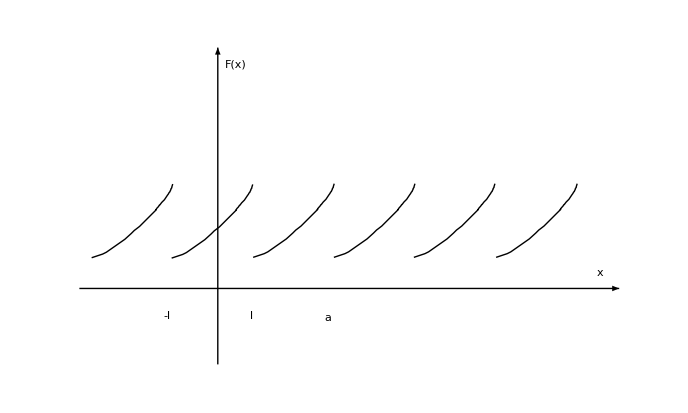

Очевидно, что для F(x) на интервале (-l, l) можно построить ряд Фурье по формуле:
	F(x) ∼ a_0/2 + ∑ _(k=1)^∞ (a_k cos(k π x)/l+ b_k sin(k π x)/l).
с коэффициентами (72.2), который имеет сумму:
	S(x) = (F(x - 0) + F(x + 0))/2.
Так как F(x) и сумма S(x) её ряда Фурье имеют T=2l, то этот ряд будет рядом Фурье на [a, a+2l] и на f(x):
	f(x) ∼ a_0/2 + ∑ _(k=1)^∞ (a_k cos(k π x)/l+ b_k sin(k π x)/l),  x∈(a, a+2l).
Для коэффициентов a_k и b_k такого рода имеем с учетом (72.2):
	a_k= 1/l(∫ _-l)^l F(t)cos(k π t)/l d t = 1/l(∫ _a)^(a+2l)F(t)cos(k π t)/l  d t = 1/l(∫ _a)^(a+2l)f(t)cos(k π t)/l d t,
	b_k = 1/l(∫ _-l)^l F(t)sin(k π t)/l d t = 1/l(∫ _a)^(a+2l)F(t)sin(k π t)/l d t = 1/l(∫ _a)^(a+2l)f(t)sin(k π t)/l d t.

Следствие 72.1

Пусть f(x) представлена рядом Фурье на [a, a+2l] и четная либо нечетная относительно a+l. Тогда ряд Фурье для f(x) на (a, a+2l) будет состоять из косинусов для четной функции f и из синусов для нечетной функции f.

Предположим. что f не является ни четной, ни нечетной на (a, a+2l). Пусть необходимо представить её ряд Фурье, состоящим только из синусов или косинусов. Тогда нужно рассматривать либо левый конец x=a либо правый x=a+2l как середину промежутка и продолжить заданную функцию f в ту или иную сторону как четную или как нечетную.

# Глава 12. Кратные интегралы.

## § 73. Интеграл Римана по n-мерному параллелепипеду.

## 73.1 Некоторые задачи, приводящие к кратному интегрированию.

1. Задача об объеме цилиндрического тела.

Пусть на ограниченном множестве E⊂ℝ^2 задана неотрицательная функция f: E⟶ℝ. Рассмотрим цилиндрическое тело, то есть множество точек из ℝ^3 ограниченное следующими поверхностями :
1) плоскостью O_(x y) ;
2) цилиндрической поверхностью, у которой направляющий является граница множества E, а образующая параллельна оси O_z;
3) поверхностью z = f (x,y).
-Graphics-
Требуется дать определение объема V данного тела и вычислить его.

Произведем разбиение множества E на "малые части". Для этого найдем прямоугольник П= [a,b] ×[c,d] так, чтобы E⊂Π.
Произведем разбиение отрезков [a,b] и [c,d]:
        a=x_0 <x_1 <...< x_n =b,
        c= y_0<y_1<...<y_m=d.
Тем самым прямоугольник  Π разбивается на m×n  частичных прямоугольников 
       [x_(k-1);x_k]×[y_(i-1);y_i].
Пересечение частичных прямоугольников с множеством E образуют разбиение множества E  на части  
       S_1,... , S_n.
Обозначим через  μ(S_1),  μ(S_2), ... ,  μ(S_N) меры (площади) множеств S_1_, S_2,... , S_N .
Далее , фиксируем произвольные точки (ξ_k, η_k) ∈ S_k , k= 1,2... , N.
За приближенное значение искомого объема естественно принять сумму объемов прямых цилиндров с основанием  S_k и высотами  ƒ (ξ_(k,)η_k) :
        V ≈ ∑ _(k=1)^N f(ξ_(k,) η_k)  μ(S_k)  .
Обозначим diam S_k=sup_((P, Q)∈ S_k) ρ(P,Q) .
Пусть d = max {diam S_1,... , diam S_k} — диаметр разбиения множества E .
По определению полагают
       V= lim _(𝒹→0) ∑ _(k=1)^N f(ξ_k,η_k)μ(S_k) = :(∫∫)_Ε f(x,y) d x  d y                                       (73.1) 
если этот предел существует, как бы ни разбивать множество E на части и как бы ни выбирать отмеченные точки.
Интеграл вида 73.1 называется двойным интегралом по множеству E⊂ℝ^2 от функции ƒ . Символ "d x d y" "" означает "элемент площади".

2. Задача о массе неоднородного тела.

Пусть E — некоторое "тело", то есть кубируемое подмножество пространства ℝ^3. Пусть, далее, функция ρ = ρ(x,y,z) ⩾ 0 является плотностью тела E в точке (x,y,z) , если ρ(x,y,z)≢const , то тело неоднородное. Требуется вычислить массу всего тела.

По аналогии с предыдущим разобьем тело E на мелкие части, для этого найдем параллелепипед
Π=[a,b]×[c,d]×[e,𝒽]
так, чтобы E⊂Π . Производя разбиение отрезков [a, b] , [𝒸,d] , [ℯ,h] , получим разбиение тела E на части
V_1, V_2,... , V_N.
Обозначим μ(V_1) , μ(V_2) , ... , μ(V_N) — объемы частичных  тел. Далее, фиксируем произвольные точки (ξ_k,  η_k, ψ_k)∈V_k .
Считая приближенное тело V_k однородным с плотностью ρ(ξ_k,η_k,ψ_k) получим приближенное значение искомой массы:
      (M≈∑)_(k=1)^Ν ρ(ξ_k,η_k,ψ_k)·µ(V_k)	.		       	                         (73.2)
Пусть d  — диаметр разбиения тела E. За массу тела E (точное значение) принимают предел, если он существует, суммы  (73.2) при d → 0: 
     M=lim _(d → 0) ∑ _(k=1)^Ν ρ(ξ_k,η_k,ψ_k)·µ(V_k)=:(∫∫∫)_E f(x,y,z) d x d y d z. 			    		(73.3)
Интеграл типа 73.3 называется тройным интегралом по множеству E ⊂ ℝ от функции ρ(x, y, z). Символ "d x d y d z""" означает "элемент объема".

## 73.2. Определение n-кратного интеграла по брусу.

По аналогии с двойным и тройным интегралами можно определить n-кратный интеграл по ограниченному множеству из ℝ^n.Начнем с частного случая n-мерного параллелепипеда (брус).
Пусть  (Π = [a_1, b_1] × [a_2, b_2] × ... × [a_n, b_n]) - n-мерный брус и на нём задана скалярная функция  f: Π → ℝ. Проделаем следующие операции.
1) Обозначим через T^i разбиение i-го отрезка [a_i, b_i]:
	a_i= x_0^i < x_1^i < ... < x_k_i^i = b_i , 
где k_i — количество отрезков разбиения.
2) С помощью разбиений T^i получим разбиение
	T = T^1 × T^2 × ... × T^n,
всего бруса П на "ячейки", т. е. на брусы вида
U_j = [α_1,β_1] × [α_2,β_2] × ... × [α_n,β_n] ,  j = 1, 2, ..., N,
где [α_i,β_i] — отрезок из разбиения T^i , а N = ∏ _(i=1)^n k_i.
 Обозначим диаметр разбиения T через λ(T) = max diam U_j , где diam U_j=sup_((P, Q)∈ U_j) ρ(P,Q) .
3) Меру ячейки U_j полагаем равной:
 μ(U_j):=∏ _(k=1)^n (β_k - α_k).
 Мера ячейки называется n-мерным объемом.
 В частности , μ(U_j) означает:
 при n = 1 — длину отрезка,
 при n = 2 — площадь прямоугольника,
 при n = 3 — объем параллелепипеда.
4) Фиксируем в каждой ячейке точку, получим разбиение бруса с отмеченными точками (T,ξ).											
5) Для разбиения (T, ξ) составим интегральную сумму
	σ(f, T,  ξ)=∑ _(j=1)^N f(ξ_j^(->))μ(U_j).

Определение 73.1

Если существует конечный предел
	lim _(λ(T)→0) σ(f, T, ξ),						(73.4)
то функция f: Π→ℝ  называется интегрируемой по Риману на Π, а сам этот предел называется n-кратным интегралом от функции f  по брусу П. Употребительны различные обозначения n-кратного интеграла по брусу:
∫ _Π f(x⃗)d x⃗=(∫...)_Π∫f(x⃗)d x⃗=∫_a_1^b_1 ∫_a_2^b_2...(∫_a_n^b_n f(x_1, x_2,..., x_m))_a_x^b_x d x_1 d x_2...d x_m=(∫...)_(a_1⩽x_1⩽b_1
a_2⩽x_2⩽b_2
........
a_n⩽x_n⩽b_n)∫f(x_1,x_2,..., x_n) d x_1 d x_2...d x_n.

Существование конечного предела J в  (73.4) понимается обычным образом: 
	∀ε>0∃δ>0|∀(T, ξ):λ(T)<δ⟹|σ(f, T, ξ) -J|<ε.
Тот факт, что  функция f интегрируема по Риману на  брусе Π, будем обозначать так:
	f∈ R(П).

Замечание.
Очевидно, для функции f(x^(->)) ≡ 1 интеграл по брусу П существует и выражает объем этого бруса:
	μ(П) =  ∫ _Π d x^(->).

## § 74. Условия существования и основные свойства кратного интеграла по брусу.

Если T — разбиение бруса Π и U_1, U_2,..., U_n — ячейки разбиения, то верхние и нижние суммы Дарбу для функции f:Π→ℝ определяются обычным образом:
	S̄(f,T)=∑ _(j=1)^N M_j μ(U_j),   M_j=sup_(x^(->) | ∈ | U_j) f(x^(->)),
	S_(‾‾)(f,T)=∑ _(j=1)^N m_j μ(U_j),   m_j=inf_(x^(->) | ∈ | U_j) f(x^(->)).
Эти суммы сохраняют свои свойства и в многомерном случае.Напомним основные из таких свойств.
1° Суммы Дарбу, вообще говоря,  не являются интегральными суммами (так как на U_j может не существовать точек, где inf f и sup f достигаются).
2°  Для одного и того же разбиения (T, ξ) с любыми отмеченными точками справедливы неравенства:
	S̲(f, T)  ≤  σ(f, T, ξ) = ∑ _(j = 1)^N f(ξ_i^(->))  μ  (U_j)<=S̄(f, T).
3°  При измельчении разбивается верхняя сумма Дарбу не увеличивается, а нижняя не уменьшается.
4°  Любая из нижних сумм Дарбу не превосходит любую из  верхних сумм Дарбу, даже если они построены для различных разбиений:
	∀ T', T'' ⟹ S̲(f, T') ⩽S̄(f, T'').
Аналогично случаю n =1  формулируется и доказывается основной критерий интегрируемости функции в смысле Римана.

Теорема 74.1 (Критерий Дарбу)

Существование n-кратного интеграла по брусу от функции f равносильно выполнению условия: 

 		lim _(λ(T)→0) [ S̄(f, T) - S̲(f, T) ] = 0 .
Если учесть, что
 S̄ (f, T) -  S̲ (f, T) = ∑ _(j = 1)^N (M_j-m_j)μ (U_j) = ∑ _(j = 1)^N ω(f, U_j) μ  (U_j),
 где ω(f, U_j) —  колебание функции f на U_j, то критерий Дарбу можно сформулировать в других равносильных формах:
 	lim _(λ(T)→0) ∑ _(j = 1)^N ω(f, U_j) μ  (U_j)= 0 ,
 ∀ε > ∃ δ > 0| ∀T : λ(T) < δ ⇒ ∑ _(j = 1)^N ω (f, U_j) μ  (U_j) < ε    					(74.1)

Условие (74.1) вместе с теоремой Кантора о равномерной непрерывности можно использовать для доказательства следующей теоремы.

Теорема 74.2 (об интегрируемости непрерывной функции)

Если функция f:П→ℝ непрерывна, то она интегрируема по брусу П.

Основные свойства кратного интеграла по брусу и их обоснования аналогичны свойствам интеграла Римана по отрезку. Напомним эти свойства.
1° (необходимое условие интегрируемости)
    Если функция интегрируема по брусу, то она ограничена на нем.
2° (линейность интеграла)
    Если функции f_1, f_(2,)...,f_n   интегрируемы на П, то их линейная комбинация ∑ _(k=1)^n c_k f_k также интегрируема  на П, причём
   	 ∫ _Π (∑ _(k=1)^n c_k f_k(x⃗))d x⃗=∑ _(k=1)^n c_k ∫ _Π f_k(x⃗)d x⃗.
3° (монотонность интеграла )
    Если функции f,g∈ℝ(П), причём ∀x⃗∈П:f(x⃗)<=g(x⃗), то вместе с тем и 
    	 ∫ _Π f(x⃗)d x⃗(<=∫)_Π g(x⃗)d x⃗.
4° (оценка интеграла)
    Пусть f∈ℝ(П), m= inf_П f(x⃗), M= sup_П f(x⃗), 
    Тогда m·μ(П)≤ ∫ _Π f(x⃗)d x⃗≤M·μ(П).
5° (интегрируемость модуля)
    Если f∈ℝ(П), то и |f|∈ℝ(П), причём | ∫ _Π f(x⃗)d x⃗|≤ ∫ _Π |f(x⃗)|d x⃗.

## § 75. Интеграл по множеству из ℝ^n.

## 75.1. Измеримые по Лебегу и по Жордану множества.

Напомним определение границы ∂E множества  E⊂ℝ^n :
∂E={x⃗∈ℝ^n|∀U(x⃗):Piecewise[{{U(x⃗)∩E≠∅,, }, {U(x⃗)∩(ℝ\E)≠, ∅}}]
в любой окрестности U(x⃗) каждой точки  x⃗∈∂E должны существовать точки, как принадлежащие, так и не принадлежащие E. Отметим, что граница любого множества является замкнутым множеством.
Напомним, что множество E называется счётным, если между его элементами и элементами множества ℕ натуральных чисел можно установить взаимоднозначное соответствие.

Определение 75.1

Множество E⊂ℝ^n называется множеством меры нуль в смысле Лебега, если для ∀ε>0  существует покрытие множества E не более чем счетной системой {Π_α ,α∈A} брусов Π_α, таких, что 
 ∑ _(α∈A) μ(Π_α)<ε.

Определение 75.2

Множество называется измеримым по Лебегу, если его граница имеет лебегову меру нуль.

Теорема 75.1 (критерий Лебега для бруса)

Для функции f:П→ℝ по брусу П необходимо и достаточно, чтобы f была ограниченной на П, а множество всех точек разрыва имело лебегову меру нуль, т.е. чтобы f была непрерывной почти всюду на П.

Доказательство опускается

Определение 75.3

Множество E⊂ℝ^n называется множеством меры ноль в смысле Жордана, если ∀ε>0  его можно покрыть конечной системой  брусов П1,П2,... , Пm  таких что (∑ _(k=1)^m)^μ(Пk)<ε.

Замечание.
Существуют ограниченные множества, которые состоят из бесконечного множества различных элементов и имеют жорданову меру 0.

Определение 75.4

Множество E ⊂ ℝ^n называется измеримым по Жордану, если оно ограничено и его граница имеет жорданову меру ноль.

Таким образом множества, измеримые по Жордану, необходимо ограничены, а измеримые по Лебегу могут быть неограниченными.
Заметим, что если компактное (т.е. ограниченно-замкнутое) множество E имеет лебегову меру ноль, то оно имеет и жорданову меру ноль. Это — следствие того факта, что из любого бесконечного покрытия брусами компакта можно выделить конечное подпокрытие, поэтому определение 75.4 измеримого по Жордану множества остается в силе, если в нем потребовать,чтобы граница ∂E имела меру нуль и в смысле Лебега.
Таким образом для компактных множеств из  ℝ^n понятие измеримости по Лебегу и по Жордану эквиваленты.

Примеры измеримых по Жордану множеств:

1) Любой брус.
2) Любой шар в ℝ^n, т.е. множество точек x^⟶ = (x_1, x_2,... , x_n) , такое что Σ_(k = 1)^n = x_k^2 ⩽ r^2 .
3) Любое тело симметрического типа в пространстве ℝ^3, то есть множество точек  (x, y, z) ∈ℝ^3 ,  заданное соотношением
Piecewise[{{(x, y) ∈ D, D∈ ℝ^2,
z_1 (x, y) ⩽z ⩽ z_2 (x, y),
z_k (x, y) ∈ c(D), k = 1, 2, ..., }}]

-Graphics-

Всюду в дальнейшем, говоря об интегрируемости, будем иметь в виду только ограниченные замкнутые множества, то есть  компакты.

## 75.2 Интегралы по множествам из ℝ^n. Критерий Лебега интегрируемости функции по ограниченному множеству.

Определение.75.5

Характеристической функцией множества E⊂ℝ^n называется функция X_E:ℝ^n⟶ℝ,задаваемая равенством:
X_E  (x⃗)={1,x⃗∈E,
0, x⃗∉E.

Справедлива

Теорема 75.2

Множество всех точек разрыва характеристической функции X_E совпадает с границей множества E.

Доказательство опускается

Следствие 75.1

Если E  — измеримое множество,то X_E непрерывна всюду на ℝ^n, кроме множества точек Жордановой меры нуль.

Определение 75.6

Интеграл от функции f:E⟶ℝ по ограниченному множеству E⊂ℝ^n определяется равенством:
	 ∫ _E f(x^(->))d x:=∫ _П X_E(x^(->))f(x^(->))d x^(->),								(75.1)
где Π — произвольный брус, содержащий E.
Если интеграл, стоящий в правой части, существует, то f называется интегрируемой в смысле Римана на E, а если не существует, то не интегрируемой.
Можно показать, что это определение не зависит от вида бруса  E⊂П

Теорема 75.3 (о корректности определения интеграла по множеству)

Если   Π_1, Π_2	— брусы содержащие E , то интегралы
∫ _Π_1 X_E(x^(->))f(x^(->))d x^(->) и ∫ _Π_2 X_E(x^(->))f(x^(->))d x^(->)
либо оба существуют и равны между собой, либо оба не существуют.

Доказательство опускается

Теорема 75.4 (критерий Лебега интегрируемости функции по измеримому множеству)

Для интегрируемости f:E→ℝ в смысле Римана по измеримому множеству E⊂ℝ^n необходимо и достаточно, чтобы f была ограниченной на E и множество всех её точек разрыва имело меру нуль.

Доказательство опускается

## 75.3. Мера Жордана (объём) ограниченного множества из ℝ^n.

Определение 75.3

Мерой Жордана (или n-мерным объёмом) ограниченного множества E⊂ℝ^n называется интеграл:
	μ(E) :=∫ _E 1 d x⃗,						(75.2)
если этот интеграл существует.

Теорема 75.5

Для того, чтобы ограниченное множество  имело объём, необходимо и достаточно, чтобы оно было измеримым по Жордану.

Доказательство опускается

Следствие 75.2

Равносильно следующее определение измеримого по Жордану множества:
(а) E ограничено и его граница  ∂E — множество Жордановой ( или Лебеговой) меры ноль.
(б) E ограничено и существует интеграл :
∫ _E 1 d x⃗,
называемый мерой или объема множества E.

Замечание.
Можно показать, что в случае n = 2 измеримость по Жордану множества E равносильна его квадрируемости, а в случае n =3 — кубируемости. В связи с этим мера Жордана в случаях n=1, n=2 и n=3 называется соответственно длиной, площадью и объемом.

## § 76. Сведение кратных интегралов к повторным.

## 76.1. Предварительные замечания.

Задача об объеме цилиндрического тела.

Пусть тело "образовано" непрерывной положительной функцией z=f(x,y), заданной на брусе П=[a;b]×[c;d].
-Graphics-

Вычисление объёма V такого тела приводит к двойному интегралу V=(∫∫)_П f(x, y) d x d y.
Этот интеграл можно вычислить, разбивая отрезки [a;b] и [c;d] на части и, соответственно, получая разбиение П на ячейки.
Однако, можно разбивать  только  отрезок  [a;b]:  
	 a=x_0<x_1<...<x_n=b .
Тогда плоскости x=x_k разрежут тело на "ломтики". Объем V_k каждого "ломтика" можно приближенно считать равным произведению его ширины  (x_k;x_(k+1)) на площадь сечения всего тела плоскостью   x=ξ_k∈[x_k;x_(k+1)].
	V_k≈(x_(k+1)-x_k)∫_c^d (ξ_k;y)d y.
Суммируя эти приближенные значения для V_k и переходя к пределу при стремлении к нулю диаметра разбиения отрезка [a,b], получим, что 
	V=(∫∫)_П f(x, y) d x  d y=∫_a^b d x∫_c^d f(x,y) d x .				  (76.1)
Интеграл справа в (76.1) называется повторным. Подынтегральная функция в нем есть некоторый интеграл, зависящий от параметра. Формула (76.1) дает правило  вычисления двойного интеграла посредством сведения его к повторному. В связи с этим возникает вопрос: верна ли аналогичная формула, использующая другой повторный интеграл:
(∫∫)_П f(x, y) d x  d y=∫_a^b d y∫_c^d f(x,y) d x ?
И вообще: можно ли вычисление n-кратного интеграла свести к последовательному вычислению n однократных интегралов?

## 76.2. Основная теорема. Некоторые следствия и примеры.

Положительный ответ на поставленный вопрос дает

Теорема 76.1 (Г. Фубини)

Пусть X⊂ℝ^n и Y⊂ℝ^m — замкнутые брусы и функция f : X×Y → ℝ интегрируема по брусу X×Y⊂ℝ^(m+n), тогда справедлива формула
	∫ _(X×Y) f(x⃗, y⃗) d x⃗ d y⃗  = ∫ _X d x⃗∫ _Y f(x⃗, y⃗) d y⃗ =∫ _Y d y⃗∫ _X f(x⃗, y⃗) d x⃗.

Доказательство опускается

Следствие 76.1.

Пусть дано множество:
D={x⃗∈G⊂ℝ^n, φ_1(x⃗)⩽y⩽φ_2(x⃗)}
Если функция f:D→ℝ интегрируема на D, то справедлива формула:
	∫ _D f(x⃗, y⃗) d x⃗ d y⃗  = ∫ _G d x⃗∫_(φ_1(x⃗))^(φ_2(x⃗)) f(x⃗, y⃗) d y⃗;					(76.2)

Найдем брусы   П_n  и  П_1 так, чтобы  
	Piecewise[{{G⊂ П_n,
 φ_1(x⃗),φ_2(x⃗)⊂П_1,∀ x⃗∈G., }}]
В этом случае D⊂ П=П_n×П_1, тогда 
       ∫ _D f(x⃗, y) d x⃗ d y  (=∫)_П X_E(x⃗, y) d x⃗ d y  = (по теореме Фубини) =∫ _Π_n d x⃗∫ _Π_1 X_E f(x⃗, y)  d x⃗ d y =∫ _G d x⃗∫_(φ_1(x⃗))^(φ_2(x⃗)) f(x⃗, y) d y .

Это утверждение на практике применяют следующим образом:
выбирают одну из переменных (например, x_k) в качестве начальной переменной интегрирования, затем все множество D⊂ℝ^n проектируют на (n-1)-мерное пространство остальных переменных, получая при этом некоторую область G⊂ℝ^(n-1). После этого рассматривают пределы изменения x_k, зависящие от остальных переменных из области G. С полученной проекцией (интеграла) поступают аналогично. И так далее.
В случае двойных интегралов (∫∫)_D f(x,y)d x d y это правило выглядит так. Выбор, например , y в качестве начальной переменной интегрирования проектирует множество  D⊂ℝ^2 на ось O_x, (то есть на пространство "остальных переменных"), получая при этом некоторый отрезок G = {a<= x <= b }. Затем выясняют, как при каждом x ∈[a;b] изменяется переменная y. Обычно получается , что границы изменения y зависят от x:
	y_1(x) <=y<=y_2(x).
(Может оказаться, что множество изменения y состоит из нескольких отрезков). Аналогично, можно было бы выбрать x в качестве начальной переменной интегрирования. Тогда рассматривалась бы проекция области D на ось O_y.

Пример 76.1

Перейти к повторному в двойном интеграле (∫∫)_D f(x,y)d x d y , где множество  D⊂ℝ^2 задано соотношениями:
	D = {(x,y): a<=x<=b, y_1(x) <=y<=y_2(x) }

-Graphics-
Из задания D видно, что отрезок [a,b] является проекцией D на ось O_x. Кроме того, при каждом x∈[a;b] переменная y изменяется в пределах от y_1(x) до y_2(x). Поэтому сначала интегрирование будем вести по переменной y, а затем — по переменной x:
	(∫∫)_D f(x,y)d x d y = ∫_a^b d x∫_(y_1(x))^(y_2(x)) f(x,y) d y.
В подобных случаях принято говорить , что двойной интеграл сведен к повторному и расставлены пределы интегрирования в порядке d x d y.

Замечание.
Можно было бы в двойном интеграле из примера (76.1) переходить к повторному интегралу в порядке d x d  y , то есть сначала проектировать D на ось O_y , получив отрезок [c;d] и , соответственно формулу: 
	(∫∫)_D f(x,y)d x d y = ∫_c^d d y∫_(x_1(y))^(x_2(y)) f(x,y) d x.
Но тогда оказалось бы, что не при всех y∈[c;d] множество изменения для x с границами x_1(y) и x_2(y) будет связным (смотреть рисунок). Это привело бы к необходимости разбивать как и отрезок [c;d], так и [x_1(y);x_2(y)] при некоторых y на части, что усложняет вычисления.

Пример 76.2

Записать в виде повторного тройной интеграл  
        (∫∫∫)_D f(x, y, z) d x d y d z  ,
где D⊂ℝ^3 — тело, ограниченное поверхностями  z = z_1 ( x,y) и  z=z_2(x,y) , (z_1(x,y)⩽z_2(x,y)) , цилиндрической поверхностью с образующими параллельными оси O_z  и направляющей в виде, например, некоторой окружности.

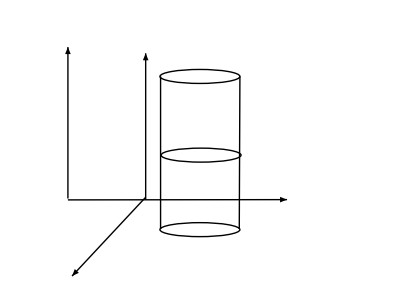
-Graphics-
 В подобных случаях удобно выбирать  z  в качестве начальной переменной интегрирования  и проектировать все тело на плоскость O x y остальных переменных получив в проекции область  D_(x y)⊂ℝ^2 (в данном случае круг). Тогда, согласно (76.2) имеем:
(∫∫∫)_D f(x, y, z) d x d y d z=(∫∫)_(D_(x y)) d x d y∫_(z_1 ( x,y))^(z_2 ( x,y))  f(x,y,z) d z =∫_a^b d x∫_(y_1 ( x))^(y_2 ( x)) d y∫_(z_1 ( x,y))^(z_2 ( x,y)) f(x,y,z)d z.

И вообще, пусть измеримое множество D⊂ℝ^n характеризуется следующими соотношениями  для координат своих точек   x⃗(x_1,x_2,...,x_n):
  a_1⩽x_1⩽b_1, 
  a_2(x_1)⩽x_2⩽b_2(x_1) ,
 a_3(x_1,x_2)⩽x_3⩽b_3(x_1,x_2) ,
   . . . .
a_n(x_1,x_2,... , x_(n-1) )⩽x_n⩽b_n(x_1,x_(2, ... ,) x_(n-1)) ;
Тогда, применяя многократно следствие , то есть формулу  (76.2) к интегралу  ∫ _D f(x^(->)) d x^(->) ,  получим, что 
∫ _D f(x^(->)) d x^(->)=∫_a_1^b_1 d x_1(∫ d x_2)_(a_2(x_1))^(b_2(x_1))...(∫ d x_n)_(a_n(x_1... x_(n-1)))^(b_n(x_1... x_(n-1))) ,						(76.3)
В частности,  если D=Π — брус, то пределы изменения всех координат  x_k  постоянные и эта формула (76.3) принимает вид:

 (∫...∫)_Π f(x_1,... , x_n) d x_1... d x_n = ∫_a_1^b_1  d x_1∫_a_2^b_2  d x_2 ... ∫_a_n^b_n f(x_1,... , x_n) d x_n .

## § 77. Замена переменных в кратном интеграле.

## 77.1. Выражение площади в криволинейных координатах.

Пусть в  плоскости O_(x y) дана область D, ограниченная замкнутой простой кусочно-гладкой  линией, а в плоскости  O_(u v) — область Δ, ограниченная подобной линией.
-Graphics-
 При этих условиях области D и Δ квадрируемы. Поставим задачу: выразить площадь области D в виде некоторого двойного интеграла по Δ.

С этой целью будем считать, что между областями D и Δ установлено биективное соответствие: 
	{x=x(u,v)
y=y(u,v):  Δ⟶D    					(77.1)
	(u,v)∈Δ; (x,y)∈D.
Очевидно из (77.1) можно найти и обратное отображение:
	{u=u(x,y)
v=v(x,y)     :  D⟶Δ,
которое также является биективным. Таким образом, каждой точке P(x,y) из области D однозначно соответствует некоторая точка Q(u,v) из Δ.
Такие числа u и v называются криволинейными координатами точки P. Это название объясняется тем, что координатным линиям (то есть прямым)  u=c_1,  v=c_2  в плоскости O_(u v) будут на оси (77.1) соответствовать кривые в  плоскости O_(x y)с параметрическими уравнениями:
{x=x(c_1,v)
y=y(c_1,v)    и   {x=x(u,c_2)
y=y(u,c_2)					(77.2)
Поставленную выше задачу выразить площадь области D через двойной интеграл по области Δ решает следующая теорема.

Теорема 77.1 (выражение площади в криволинейных координатах)

Пусть Δ и D — квадрируемые области из ℝ^2 и отображение
{x=x(u,v)
y=y(u,v) :Δ→D							(77.3)
есть биективное соответствие, для которого:
1) Функции x(u,v) и y(u,v) имеют в области Δ непрерывные частные производные 1-го порядка по  всем переменным;
2) Якобиан преобразования (77.3) отличен от нуля почти везде в области Δ:
(D(x, y))/(D(u, v))=J(u,v)= |x'_u | x'_v
y'_u | y'_v|≠0, (u,v)∈Δ.
Тогда площадь  μ(D) области D  может быть выражена следующим двойным интегралом:
μ(D)=(∫∫)_Δ |J(u, v)|du dv             					   (77.4)

Доказательство опускается

## 77.2. Теорема о замене переменных в кратном интеграле.

Используя выражение площади плоской области в криволинейных координатах, можно установить следующий результат.

Теорема 77.2 (Замена переменных в двойном интеграле)

Пусть Δ, D — квадрируемые замкнутые области из ℝ^2 и отображение:
{x=x(u,v)
y=y(u,v):  Δ⟶D  
есть деффеоморфизм области Δ на область D, то есть функции x и y имеют непрерывные частные производные 1-го порядка и якобиан преобразования J(u,v) != 0 в области Δ (почти везде). Тогда для любой функции  f(x,y), непрерывной в замыкании области D, справедлива формула замены переменной  в двойном интеграле:

(∫∫)_D f(x,y) d x d y =(∫∫)_Δ[x(u,v),y(u,v)]·|J(u,v)| d u d v .                     		(77.5)

Доказательство опускается

Якобиан J(u,v) отличен от нуля почти везде в области  Δ (то есть кроме множества меры ноль).
Сформулируем аналогичную теорему в общем случае замены переменных в кратном интеграле. Напомним, что областью в ℝ^n называется любое открытое связное множество. Область называется ограниченной, если она целиком помещается внутри внутри некоторого шара или бруса. Область называется замкнутой, если она содержит все свои предельные точки.

Теорема 77.3

Пусть D и Δ — ограниченные замкнутые области из ℝ^n и отображение:
  x^(->) =φ(t^(->)):  = Piecewise[{{x_1=φ_1(t_1,... ,t_n), }, {x_2=φ_2(t_1,... ,t_n) 
...
x_n=φ_n(t_1,... ,t_n), }}] | 
: Δ⟶ D
есть диффеоморфизм, то есть выполняются условия:
 1)  все функции  φ_k(t_1,... , t_k) имеют в Δ непрерывные частные производные 1-го порядка по всем переменным; 
 2)  якобиан  преобразования  x^(->) = φ(t^(->)) почти везде отличен  от нуля в Δ:
 
 J(t_1,... , t_n)= |(∂ x_1)/(∂ t_1) | (∂ x_1)/(∂ t_2) | ... | (∂ x_1)/(∂ t_n)
(∂ x_2)/(∂ t_1) | ... | ... | (∂ x_2)/(∂ t_n)
... | ... | ... | ...
(∂ x_n)/(∂ t_1) | ... | ... | (∂ x_n)/(∂ t_n)|!=0 .
 
 Тогда для любой  интегрируемой  по области D функции f:D⟶ℝ справедлива формула 
 
(∫...∫)_D f(x_1,... ,x_n) d x_1...  d x_n =(∫^ ...∫)_Δ[f x_1(t_1,... ,t_n),...,x_n(t_1... t_n)]·|J(t_1... t_n)| d t_1...  d t_n.       			(77.6)

Основано на методе математической индукции (опускается).

## § 78. Примеры преобразования кратных интегралов.

## 78.1. Переход к полярным координатам.

При вычислении двойных интегралов часто используют переход от декартовых координат к полярным:
ρ:{x = r cos φ ,
y = r sin φ . 	(r>= 0;0<=φ<=2 π (или -π<=φ<=π)).				 -Graphics-
Якобиан такого преобразования:
|(∂ x)/(∂ r) | (∂ x)/(∂ φ)
(∂ y)/(∂ r) | (∂ y)/(∂ φ)| =|cos φ | -r sin φ
sin φ | r cos φ| = r . 
Поэтому имеем:
(∫∫)_D f(x,y) d x d y =(∫∫ f)_Δ(r cos φ, r sin φ)r d r d φ .									    (78.1)
При этом может оказаться, что:
1) выражение f(r cos φ, r sin φ)r упрощается по сравнению с выражением  f(x,y);
2) область Δ — прообраз множества D — имеет более простой вид. Например, прямоугольник, в котором границы изменения r и φ постоянные (для r независимо от φ и для φ независимо от r).
Особенно эффективен переход к полярным координатам в случаях, когда:
1)область интегрирования есть круг или кольцо с центром в начале координат, либо их секторная часть;
2)подынтегральная функция f(x,y) зависит от выражения x^2 + y^2.

Пример 78.1

Найти объем части шара радиуса R , вырезаемой из него прямым круговым цилиндром радиуса a, a<R , ось которого проходит через центр шара.

Принимая центр шара за начало координат, и ось цилиндра за ось O_z, будем иметь уравнение поверхности шара: 
	x^2+y^2+ z^2 = R^2,
а уравнение поверхности цилиндра :
	x^2+y^2=a^2.
	-Graphics-
Объем V данного тела равен удвоенному объему той его части , которой соответствует z>=0. Объем выражается двойным интегралом:
	V =(2∫∫)_D f(x,y) d x d y , 								(78.2)
где D = {(x,y)∈ R^2| x^2+y^2<=a^2} — круг радиуса a с центром в начале координат, z = f(x,y) =√(R^2-x^2-y^2). 
Переходя к одному из повторных интегралов, получаем:
	V = (2∫∫)_(x^2+y^2<= a^2)√(R^2-x^2-y^2) d x d y = 2 ∫_-a^a  d x∫_(-√(a^2-x^2))^(√(a^2-x^2)) √(R^2-x^2-y^2) d y.			-Graphics-
Чтобы проверить вычисление двойного интеграла (78.2) перейдем в нем сразу к полярным координатам:
	ρ : {x = r cos φ
y = r sin φ: Δ⟶ D
Но для точек (x;y) круга D = ρ(Δ)= {x^2+y^2<=a^2},очевидно, имеем :{0<=r<=a ,
0<=φ<=2π. Поэтому этот круг является образом прямоугольника :
-Graphics-
Учитывая, что x^2 + y^2=(r cos φ)^2+ (r sin φ)^2=r^2, а якобиан J(r;φ) = r, получаем по формуле (78.1):
	V = (2∫∫)_(x^2+y^2<= a^2)√(R^2-x^2-y^2) d x d y =(2∫∫)_(0 ⩽ r ⩽ a
0 ⩽ φ ⩽2π)√(R^2- r^2) r d r d φ   =
  = 2 ∫_0^(2π)  d φ∫_0^a √(R^2-r^2) r d r = -2π ∫_0^a √(R^2- r^2)d (R^2-r^2)= (-4π)/3(R^2-r^2)^(3/2)|_(r=0)^(r=a)=(4π)/3[R^3-(R^2-a^2)^(3/2)] .

Замечание 78.1
В частности, при a = R , то есть когда весь шар оказывается внутри цилиндра, получаем объем шара радиуса R :
	V = 4/3 π R^3.

Замечание 78.2
Иногда целесообразнее переход к обобщенным полярным координатам (точнее к обычным полярным координатам r и φ, но по формулам более общего вида):
	{x = x_0 + a r cos^λ φ
y = y_0+ b r sin^λ φ  , λ > 0.
(Смысл переменных r  и φ тот же, что и выше).Параметры x_0,y_0,a,b и λ подбираются с учетом вида области и подынтегральной функции. Якобиан такого преобразования равен:
	J(r,φ) = a b λ cos^(λ-1)φ sin^(λ-1)φ.

## 78.2. Переход к цилиндрическим координатам в тройном интеграле.

Рассмотрим теперь преобразования тройного интеграла при переходе от декартовых координат к цилиндрическим:
	ρ:Piecewise[{{x = r cos φ, r >=0,}, {y = r sin φ
z = h, [0<=φ<=2π ,-π<=φ<=π]
 h ∈ ℝ}}]						-Graphics-
(Здесь r и φ — полярные координаты проекции точек (x,y,z) на плоскость z=0).
Координатные поверхности:
- плоскость h = const; 
- цилиндры z = const;
- полуплоскость {φ = const, r> 0}.
	J(r,φ,h) = |cos φ | -r sin φ | 0
sin φ | r cos φ | 0
0 | 0 | 1| = r 
Поэтому 
	(∫∫∫)_V f(x,y,z)d x d y d z =(∫∫∫)_Δ f(r cos φ,r sin φ,h) r d r d φ d h .
Переход к цилиндрическим координатам целесообразен в случаях , когда область интегрирования имеет осью симметрии ось O_z, а подынтегральная функция зависит от выражения x^2+y^2.

## 78.3. Переход к сферическим координатам в ℝ^3.

Рассмотрим , наконец , преобразование тройного интеграла  (ТРИ) при переходе от декартовых координат к сферическим:
Piecewise[{{x= ρ cos θ cos φ, -π/2≤0≤π/2,}, {y=ρ cos θ sin φ
z = ρsin θ, ρ⩾0,
 0≤φ≤2π.}}]                         (78.3)
-Graphics-
Здесь ρ — расстояние от точки (x, y, z) до O(0;0 ;0),
θ  — угол наклона радиус-вектора точки  (x, y, z) до плоскости z=0 (“географическая широта”).
φ — полярный угол проекции точки (x,y,z) на плоскость z = 0 (“географическая долгота”).
Координатные поверхности: ρ=const (сфера),  φ=const (полуплоскость), θ=const (конус).
Якобиан такого преобразования:
J(ρ, θ,  φ) =|cos θ cos φ | -ρcos φ sin θ | -ρ cos θ sin φ
sin φ cos θ | -ρsin φ sin θ | ρ cos θ cos φ
sin θ |  ρ cos θ | 0|=Выносим из 2 столбца ρ, а из 3 ρ cos θ =ρ^2 cos θ |cos θ cos φ | -cos φ sin θ | -sin φ
sin φ cos θ | -sin φ sin θ | cos φ
sin θ |   cos θ | 0| = ρ^2 cos θ .
Таким образом, имеем:
                  (∫∫∫)_D f(x, y, z)  d x  d y  d z= (∫∫∫)_Δ f(ρ sin θ cos φ, ρ sin θ sin φ, ρ cos θ) ρ^2 cos θ  d ρ  d θ  d  φ .

Замечание 78.3
Из (78.3) вытекает то, что если возвести в квадрат и сложить каждую часть уравнения, то получим:
                                                      x^2+y^2+z^2=ρ^2  .

Замечание 78.4     
При вычислении тройного интеграла удобно переходить к сферическим координатам  в случаях , когда область D  “сферического  типа” либо подынтегральная функция зависит от  x^2+y^2+z^2 .

Пример 78.2

Вычислить (∫∫∫)_D √(x^2+y^2+z^2)  d x  d y  d z , где V = {(x,y,z) ∈ ℝ : x^2+y^2+ z^2<=z}.
-Graphics-

В данном случае тело V есть шар x^2+y^2+ (z-1/2)^2<= (1/2)^2 так как x^2+ y^2+z^2 = z⇔ ρ = sin θ , то пределы изменения сферичных координат для V таковы:
	0<=θ<=π/2, 0<=φ<=2π, 0 <=ρ<= sin θ. √(ρ^2)cos θ d θ d φ d ρ
Поэтому 
	J = (∫∫∫)_(0⩽θ⩽π/2
0⩽φ⩽2π
0⩽ρ⩽cos θ)√(ρ^2)cos θ d θ d φ d ρ = ∫_0^(π/2) cos θ d θ ∫_0^(π/2) d φ ∫_0^(sin θ) ρ^3 d ρ = π/2∫_0^h sin^4 θ cos θ d θ = π/10 sin^5 θ|_0^(π/2)=π/10.

# Глава 13. Криволинейные интегралы. Формула Грина.

## § 79. Кривые и их классы.

## 79.1. Основные определения и факты, относящиеся к определению кривой.

Определение 79.1

Плоской кривой называется любое непрерывное отображение:
r⃗ : [a,b] → ℝ^2
отрезка действительной оси в ℝ^2 или, иначе говоря, пара функций
Piecewise[{{x= x(t), }, {y = y(t), }}]            (79.1)                     
в совокупности с отрезком [a,b], на котором эти функции непрерывны.

Система (79.1) называется параметрическим заданием (уравнением) кривой.

Две кривые :
r⃗: Piecewise[{{x = x_1(t), }, {y = y_1(t), }, {t  ∈ [a,b], }}]           и              ρ⃗ : Piecewise[{{x = x_2(τ), }, {y = y_2(τ), }, {τ ∈ [α,β], }}]  
называются совпадающими, если существует непрерывная строго возрастающая функция
t = s(τ) : [α, β] → [a, b]
такая, что:
x_1[s(τ)] ≡ x_2(τ),
y_1[s(τ)] ≡ y_2(τ),     τ ∈ [α, β].

Совпадение кривых означает, что их параметрическое задание можно перевести одно в другое с помощью соответствующей замены переменных.

Параметризовать кривую -       ??   систему 79.1, представляющую эту кривую.

Кривая 79.1 называется    ??      x(t) и y(t) бесконечно непрерывны и дифференцируемы на [a, b] и их производные одновременно не превращаются в нуль.

Кривая (79.1) называется кусочно-гладкой, если [a;b] можно разбить на n частей, для каждой из которых она будет гладкой . Очевидно, гладкую кривую можно рассматривать как частный случай кусочно гладкой.

Носитель кривой — геометрический образ [a;b] при  отображении (79.1). Точки носителя — точки плоскости с координатами (x(t), y(t)), t∈ [a,b]. Носитель кусочно гладкой кривой имеет касательную во всех точках ее гладкости.

Кривая называется спрямляемой, если определена сверху множеством дифференцируемых ломанных, вписанных  эту кривую. Длина кривой —  верхняя грань этого множества.

Длина кусочно гладкой кривой : 
l=∫_a^b ([ x' (t) ]^2  + [ y'(t) ]^2)^(1/2)  d t.

Длина кривой (79.1). Точка плоскости с координатами (x(a),y(a)) называется началом кривой, а (x(b), y(b)) — концом кривой. Если начало и конец совпадают, то кривая называется замкнутой, в противном случае — разомкнутой.

Точками из (79.1) называются тройки чисел (t, x(t), y(t)), t∈ a,b .                
Кривая называется простой, если между ее точками и точками  ее носителя можно установить однозначное соответствие ( т.е. разным значением t соответствуют  разные точки носителя). При этом  исключаются случаи.

Если кривая не является простой , то она не является жордановой. 
Кривая обычно рассматривается с учетом ориентации (направления).
Направление кривой — способ упорядочения ее точек.

Принято говорить, что точка кривой (t_2, x(t_2),y(t_2) ) следует за точкой ((t_1, x(t_1),y(t_1)) , если

Если при t_1≠t_2 будет {x(t_1)=x(t_2)
y(t_1)=y(t_2) то такая точка плоскости называется точкой самопересечения кривой.

Простые кривые, не имеющие точек самопересечения. Только простую кривую можно отождествить с её носителем.

Все, сказанное выше, можно перенести и на случай пространственной кривой, то есть для системы трех функций в совокупности с отрезком, на котором эти функции непрерывны.

r⃗:{x=x(t)
y=y(t)
z=z(t)
t ϵ [a;b]

## § 80. Криволинейные интегралы первого рода (по длине дуги).

## 80.1 Определение и вычисление.

Пусть в точках носителя |L| спрямляемой кривой L задана функция: F:|L|→ ℝ .

Проделаем 5 операций:

1) разобьем прямую L на части: рассмотрим разбиение T отрезка [a,b]: a = t_0 < t_1< ... < t_n = b,
тогда точки M_k(x(t_k),y(t_k)) k=0,1,... , n произведут разбиение кривой на интервалы  (M_(k-1);M_k).
Обозначим через l_k.
λ(T) — диаметр разбиения [a;b] в силу непрерывности x(t) и y(t) будем иметь max{l_k}→ 0, λ(T)→ 0.

можно считать λ(T) —  диаметром разбиения l  на дуги;
2) выберем точку t_k^∼ ∈ [ t_(k-1); t_k], тогда на дуге (M_(k-1); M_k) получим точку (M^∼)_k (ξ_k, η_k), где ξ_k= x(t_k^∼) , η_k = y(t_k^∼)  и вычислим F(ξ_k,η_k) ;
3) найдем произведение F(ξ_k;η_k) · l_k;
4) для полученного разбиения кривой с отмеченными точками найдём интегральную сумму 
	σ(F, T, ξ)=∑ _(k=1)^n F(ξ_k;η_k) ·l_k ; 
5) рассмотрим  lim _(λ(T)→0)  σ(F, T, ξ) :
если этот предел существует и конечен, независимо от способа разбиения и выбора отмеченных точек, то он называется криволинейным интегралом по длине дуги или криволинейным интегралом I рода (КРИ - I) функции F по кривой l и обозначается 
    	
∫_L F(x, y) d s.

Теорема 80.1 (о существовании и вычислении КРИ - I)

Пусть L — кривая с параметризацией
  		x=x(t)
  		y=y(t)
в точках плоской кривой определена функция F: |L|→ ℝ, причём композиция F[x(t), y(t)] интегрируема в смысле 	Римана на [a; b], тогда КРИ - I по L существует, и справедлива формула 
  		∫_L F(x, y) d s = ∫_a^b F[x(t), y(t)]√([x'(t)]^2+[y'(t)]^2) ⅆt                 (80.1)

Пусть L задана в явном виде y=y(x), x=[a; b], или x=x(y), y=[c;d] .
  Рассмотрим его как частный случай параметрического задания, например,
  	x=t
  	y=y(t)
  	t=[a; b]
  Получим из (80.1) формулы:

∫_L F(x,y) d s=∫_a^b F[x, y(x)]√(1+f y'(x))d x

Совершенно аналогично может быть определен КРИ-1:
∫_L f(x,y,z) d s,

x=x(t)
y=y(t)
z=z(t)
t∈[2,t]
Если композиция F[x(t), y(t), z(t)]∈R_[a,b], то справедлива формула, аналогичная  (80.1):
∫_L f(x,y,z) d s=∫_a^b f[x(t),y(t),z(t)]√([x'(t)]^2+[y'(t)]^2+[z'(t)]^2) d t.
При вычислении КРИ-1 следует отправляться от конкретного задания кривой и использовать формулу (80.1) или (80.2).

## 80.2. Основные свойства и некоторые приложения КРИ-1.

Свойство 1 (инвариантность)

Величина КРИ-1 не зависит от выбора параметризации кривой.

▲ Записав (80.1) для ∀ двух параллельных кривых можно свести (одно) каждое из полученных интегралов к   другому с помощью замены t=s(r) .▲

Свойство 2

Величина КРИ-1 не зависит от ориентации, то есть направления кривой.

Свойство 3 (линейность)

Для любых вещественных чисел имеем:
∫_L (α F+β G) d s=α∫_L F d s+β∫_L G d s;

▲Утверждение вытекает из 80.1, выражений КРИ-1 через определенный интеграл Римана▲

Свойство 4° (аддитивность)

Пусть кусочно гладкая кривая L представляет собой объединение попарно не пересекающихся кривых L_k, k=1,2,...,n, пусть далее существует КРИ-1 ∫_L F d s, тогда:
1) существуют КРИ-1 у^по каждой кривой L_k
2) справедливо равенство
∫_L F d s=∑ _(k=1)^n ∫_L_k F d s.

Свойство 5° (оценки интеграла)

Для КРИ-1 справедливы следующие неравенства
|∫_L F d s|≤∫_L |F|d s
m·l≤∫_L F d s⩽M·l, где l — длина кривой L,
а m=(inf F)_(|L|), а M=(sup F)_(|L|).

Одним из примеров геометрических приложений КРИ-1 является тот факт, что каждый КРИ-1 ∫_L Fⅆs при F≥0 можно трактовать, как площадь некоторой цилиндрической поверхности.
Действительно, пусть в ℝ^2 определена простая кусочно гладкая кривая (L: x=x(t), y=y(t), t∈[a, b])_(|L|), пусть далее в точках носителя задана.
Разобьем кривую L на дуги, вычислим значения F(x, y) в некоторых точках дуг и умножим их на длины дуг. В итоге можно отстроить суммы, которые приближенно вычисляют площадь этой поверхности. Переходом к lim, получаем, что S всей поверхности равна
S=∫F(x, y)d s.

Кривая в плоскости может быть параметризована с помощью натурального параметра s, который определяет собой длину участка кривой, считаемого от начала, 
L: x = x(s)
y = y(s)
z = z (s)
s  ∈ [0,l]
Пусть в точке такой кривой c натуральной параметризацией задана ρ(x,y,z)>0 — линейная плотность стержня, имеющего форму этой кривой. 
Рассматривая интегрирование суммы и переходя к пределу, получим, что масса стержня выражается интегралом:
M=∫_0^l ρ[x(s),y(s),z(s)]d s =∫_L ρ(x,y,z) d s .

## § 81. Криволинейный интеграл второго рода. Формула Грина.

## 81.1 Криволинейный интеграл второго рода (по координатам).

Подобно интегралу 1-го рода, криволинейный интеграл второго рода также определяется как предел аналогичных интегральных сумм для функции F(x,y), определенных в точке (носители) гладкой кривой L.
Кривая L разбивается на дуги (M_(k-1),M_k) с концами в точках M_(k-1)(x_(k-1),y_(k-1)) и M_k(x_k,y_k) .  На каждой дуге выбирается точка OverTilde[M_k](ξ_k,η_k) и значение функции F(OverTilde[M_k]) умножается не на длину дуги (как в случае криволинейного интеграла первого рода), а на разность значений одной из координат в концевых точках дуги. Затем производится суммирование по всем частичным дугам: 
σ=∑ _(k=1)^n F(OverTilde[M_k])·(x_k-x_(k-1))  или
σ=∑ _(k=1)^n F(OverTilde[M_k])·(y_k-y_(k-1)) 
Затем осуществляется переход к пределу: 
lim _(λ(T))

Если этот lim существует и конечен независимо от способа разбиения кривой L и выбора отмеченных точек, то он называется криволинейным интегралом второго рода (по соответствующей координате) от функции F по кривой L (криволинейный интеграл второго рода) и обозначается:

∫_L F(x, y) d x   или ∫_L F(x, y) d y .

Обычно рассматривают криволинейные интегралы второго рода общего вида, определяемые как суммы таких интегралов:

∫_L P(x, y) d x  + Q(x, y) d y :=∫_L P(x, y) d x  +∫_L Q(x, y) d y .

Аналогично определяется криволинейный интеграл второго рода для пространственных кривых:

∫_L P(x, y, z) d x  + Q(x, y, z) d y +  R(x, y, z) d z .

Справедлива

Теорема 81.1

Пусть L — плоская гладкая прямая с параметризацией
x = x(t) , y = y(t), t ∈ [a, b] .
Пусть далее в точках носители этой кривой определена функция
F : (L) → ℝ. Причем композиция 
F[x(t), y(t)]∈ ℝ_[a, b]
тогда справедлива формула
∫_L F(x, y) d x  = ∫_a^b F(x(t), y(t)) x′ (t) d t.

В общем случае при аналогичных условиях криволинейный интеграл второго рода пространственной кривой сводится к интегралу Римана: 
∫_L P d x  + Q d y +  R d z = ∫_a^b P[x(t), y(t), z(t)]x'(t) + Q[x(t), y(t), z(t)]y'(t) + R[x(t), y(t), z(t)]z'(t)}d t.    (81.1)

Чтобы равенство (81.1) стало короче используется векторная запись:
пусть F⃗ = P i⃗ + Q j⃗ + R k⃗, r⃗ = x i⃗ + y j⃗ + z k⃗, d r⃗ = i⃗ d x + j⃗ d y + k⃗ d z ;
тогда получим 81.1	в виде скалярных произведений:

∫_L F^⟶ d r⃗ = ∫_a^b F⃗[r⃗(t)] r⃗'  (t) d t.

При вышеперечисленном криволинейный интеграл второго рода отправляться от конкретного задания кривой.

1^°	КРИ-II| обладает свойствами инвариантности, линейности и аддитивности.
2^° 	При изменении направления на кривой КРИ-II меняет знак.
3^°	Если L — вертикальный отрезок x = const, то x' (t) ≡ 0 и 
		∫F(x,y)d x=0.
L                                 
	Аналогично, в случае горизонтального отрезка y = const: 
		∫F(x,y)d y=0.
L                                 
4^°	(запись КРИ-II в виде КРИ-I)
	Пусть L — гладкая кривая, функции P, Q, R удовлетворяют условиям существования КРИ, 
	cos α, cos β, cos γ — направляющие косинусы касательной к L, тогда:
		∫P d x + Q d y + R d z=∫(P cos α + Q cos β + R cos γ)d s.
 L                                                     L                                                                          
	
	Пусть в каждой точке D ⊂ ℝ^3 действует сила
			(F(x,y,z)=P(x,y,z)i+Q(x,y,z)j)^(→                                                     →                                →)
на помещенную в этой точке единичную массу, тогда такая область называется силовым полем, а
 сама сила F⃗ напряженностью поля в этой точке.
	Предположим, что материальная точка с единичной массой движется по некоторой 
гладкой кривой L (траектории). Работа A, которую необходимо совершить, чтобы, преодолевая
силы поля, заставить точку двигаться по заданной траектории, можно выразить в виде КРИ-II
			 A=∫P d x+Q d y+R d z.
L                                                                                                               (81.2)

Эту формулу можно получить, если разбивать L на дуги и приближенно считать, что работа на дуге совершается с постоянной силой, взятой в какой-нибудь точке дуги.

## 81.2. Формула Грина.

Определение 81.1.

Условимся называть область G ⊂ ℝ :
(a) x-простой, если пересечение G и любой прямой, параллельной оси O x, либо пусто, либо связно;
(b) y-простой, если пересечение G и любой прямой, параллельной оси O y, либо пусто, либо связно;
(c) простой, если она одновременно является x-простой и y-простой.

Пример 81.1.

Область G={0 < x < π
0 < y + 2 + sin x  очевидно  является y-простой, но не является x-простой.

Простыми областями являются, например, любой круг, любой прямоугольник, и вообще выпуклая область, однако, не любая простая область выпуклая.

Пример 81.2.

Область G = {x^(2/3) + y^(2/3) < 1} является, очевидно, простой, но не является выпуклой.

Теорема 31.2

Пусть G — квадрируемая область  из ℝ^2 c кусочно гладкой кривой границей ∂G, а функции P(x,y), Q(x,y),(∂Q)/(∂x) и (∂P)/(∂y) непрерывные в замыкании области.Тогда справедлива следующая формула.

∫_(∂G) P  d x+Q d y= ∫_G ∫((∂Q)/(∂x) - (∂P)/(∂y))  d x  d y		(81.3)

Доказательство проведем для случая простой области G .
1. Предположим , что область G является  y -простой, то есть, имеет вид:
G ={(x, y): α<x<b,φ_1(x)< y < φ_2(x)},
где φ_k(x) — непрерывные функции.
Тогда
 -∫∫ (∂P)/(∂y) d x d y=-(∫_a)^b d x(∫_(φ_1(x)))^(φ_2(x))(∂P(x,y))/(∂y)d y=-(∫_a)^b d x[P(x,y)|_(φ_1(x))^(φ_2(x))]=(∫_a)^b P[x,φ_1(x)]d x-(∫_a)^b P[x,φ_2(x)]d x=∫_(A m B) P(x,y) d x+∫_(C n D) P(x,y) d x=∫_(∂G) P(x,y) d x.  
так как интегралы по вертикальным отрезкам B C и   ∂A равны 0. Таким образом для y-простой области имеем :
∫_(∂G) P d x=-(∫∫)_G(∂P)/(∂y)  d x d y.				(81.4)

2. Пусть теперь G является x - простой и имеет вид:
    G={ (x, y) : c < y < d,  φ_1(y) < x < φ_2(y) },  где  φ_k(y)  — непрерывные функции.
    Тогда, аналогично предыдущему:
    
     (∫∫)_G_1(∂Q)/(∂x)d x d  y  = ∫_c^d d y ∫_(φ_1(y))^(φ_2(y)) (∂Q (x, y))/(∂x) d x = ∫_c^d [ Q (x, y) |x = φ_2(y) 
x = φ_1(y) |] d y = ∫ _c^d Q [ φ_2(y), y] d y - ∫ _c^d Q [ φ_1(y), y] d y   = ∫_(B n C) Q (x, y) d y + ∫_(D m A) Q (x, y) d y = ∫_(∂G) Q (x, y) d y.
    
    Так как интегралы по горизонтальным отрезкам A B и C D  равны нулю, значит в случае x-простой области имеем: 
    
    (∫∫)_(∂G)Q d y = (∫∫)_G(∂Q)/(∂x)d x d y  . (81.5)
3. Допустим теперь, что G — простая, тогда для неё справедливы равенства (81.4) и (81.5). Складывая их, получим:

    (∫∫)_(∂G)P d x +Q d y  = (∫∫)_G((∂Q)/(∂x) - (∂P)/(∂y) )d x d y .
    
    Тем самым, для простых областей формула Грина доказана.

## 83.3. Выражение площади через криволинейный интеграл.

Теорема 81.3

Для площади  μ(G) области G c гладкой границей справедливо равенство:

μ(G) = ∫_(∂G) x d y = -∫_(∂G) y d x = 1/2 ∫_(∂G) x d y - y d x   (81.6)

Если в формуле Грина (81.3) функции P и Q дополнительно подчинены условию :

(∂Q (x, y))/(∂x)  - (∂P(x, y))/(∂y) ≡ 1            ∀(x, y) ∈ G ∪ ∂G , то эта формула дает: 

μ(G) = (∫∫)_G d x d y  = (∫∫)_G((∂Q)/(∂x) - (∂P)/(∂y) )d x d y  =∫_(∂G) P d x + Q d y

В частности при 
1) P (x; y)  ≡ 0, Q (x; y)  ≡  x ⇒ μ(G) =∫_(∂G) x d y;
2)  P (x; y)  ≡ -y, Q (x; y)  ≡0 ⇒ μ(G) = -∫_(∂G)  y d x .
Наконец, рассмотрим полусумму последних равенств, получим
μ(G)=1/2∫_(∂G) x d y -y d x.

## § 82. Первообразная в области и её свойства.

## 82.1. Понятие первообразной в области.

Определение 82.1

Дифференциальное выражение: P(x, y)d x + Q(x,y)d y называется полным (точным) дифференциалом области G⊂ℝ^2, если для него ∃  функция 
d F(x, y)=P(x, y)d x + Q(x,y)d y.
Функция F(x, y) называется в этом случае первообразной для дифференциала  P d x+Q d y в области G.

Замечание:
1. Если F(x, y) первообразная для P(x, y) d x+Q(x, y)d y  , то (∂F(x, y))/(∂x)=P(x,y), (∂F(x, y))/(∂y)=Q(x,y) .
2. Не для всяких функций P,Q: G→ℝ выражение P( x, y) d x+ Q(x,y) d y имеет в области G первообразную, то есть является полным дифференциалом. Ниже будут даны необходимые и достаточные условия.

Теорема 82.1

Если  F(x, y) — первообразная для дифференциала P d x+ Q d y в области G, то общая формула для всех таких первообразных F(x, y) =C, где C — производная постоянная .

ПустьF_1(x, y) — другая первообразная для того же дифференциала по области G, тогда для их разности Φ(x, y)=F_1(x, y)- F_2(x, y) будет:  d Φ(x, y)  ≡ 0.

отсюда в силу теоремы Лагранжа о конечных приращениях следует, что Ф(x, y) ≡ 0 и F_1(x, y) = F(x, y) + C .

Теорема 82.2. (Формула Ньютона-Лейбница для КРИ - II )

Пусть F—  первообразная для Ρ d x  + Q d y в области G, пусть далее ℽ=x=x(t), y = y(t) ,t∈α, β — кусочно гладкая кривая с носителем в области G, тогда для КРИ справедлива формула Ньютона-Лейбница:
		
∫_ℽ P d x + Q d y = F[x(t), y(t)]|_(t = α)^(t = β) = F[x(β), y(β)] - F[x(α), y(α)]        (82.1)

Опускается

## 82.2. Условие существования локальной первообразной.

Определение 82.2.

Принято говорить, что дифференциал P d x + Q d y имеет локальную первообразную в области G, если для любой точки из  G существует ее окрестность Uи функция F: U→ℝ — первообразная для P d x + Q d y в этой окрестности.

Первообразную, о которой идет речь в 82.1. иногда называют глобальной.

Теорема 82.3.	( Критерий существования локальной первообразной в плоской области )

Пусть функции P,Q непрерывно дифференцируемы в области G⊂ℝ^2, тогда для того, чтобы выражение P d x + Q d y имело локальную первообразную в области G необходимо и достаточно, чтобы в этой области выполнялось тождество:
		
 (∂Q(x, y))/(∂x) ≡ (∂P(x, y))/(∂y)     (x,y)∈G.

Опускается

## 82.3. Первообразная в однообразной и многосвязной области.

Определение 82.3

Область G из  ℝ называется односвязной , если её границы — связное множество (не состоит из отдельных кусков).

Примеры односвязных областей: круг , любая полуплоскость , любая замкнутая кривая.
Если область не является связной и число связных компонентов конечно, то такая область называется многосвязной.

Примеры: круг с выброшенным центром ( проколотая окрестность U^o( a ) ) , кольцо или ...

Количество связных (областей) компонентов  области называется порядком связности.
Если множество связных компонент границы бесконечно, то такая область называется бесконечно связной. Примером является полоса,  из которой выброшено счетное множество кругов или точек.
Оказывается, что характер связности области существенно влияет на свойства первообразной P d x + Q d y  даже если всюду в области выполняется условие (∂Q)/(∂x)≡(∂P)/(∂y).
Можно, например, доказать,  что из существования локальной первообразной P d x + Q d y  в односвязной области вытекает существование глобальной первообразной в этой области,  т.е. такой однозначной функции F ( x , y ) , что
 d F (x , y ) = P ( x , y ) d x + Q ( x , y ) d y .

Отправляясь от локальной первообразной  U(A), будем двигаться вдоль некоторой кривой γ_1, соединяющей A и B. Будем в каждой точке γ_1 фиксировать локально первую и следить за тем, чтобы в общих частях кругов первообразные совпадали, тогда придем к определенной первообразной U(B).
	Если двигаться из A в B по любой другой кривой γ_2 и следить за непрерывным изменением первообразной, то мы получим ту же первообразную U(B), что и в первом случае. 
	То есть склеенная из локальных первых глобальная первообразная является однозначной, если область G односвязна.
	Для многосвязной области это, вообще говоря, не так. Отправляясь от локальной первой и U(A) двигаясь к U(B) по разным путям, можно для некоторых выражений P d x+Q d y  получить разные первообразные.
	Склеенная из локальных первообразных глобальна первообразная может оказаться многозначной, то есть не являться функцией в обычном смысле области G.

## § 83. Условие независимости КРИ — II от пути интегрирования.

Определение 83.1.

Пусть функции P(x,y) и Q(x,y) таковы, что интеграл ∫_γ P d x+Q d y   существует по производной кусочно кривой γ ⊂ G. Тогда будем говорить, что этот интеграл не зависит от пути в G,  если его величина не зависит от кривой γ,
соединяющей ??????????
а зависит лишь от положения.

∫_γ_1 P d x + Q d y = ∫_γ_2 P d x + Q d y =∫_γ_3 P d x + Q d y.

Если выражение P d x + Q  d y  имеет первообразную в G, то из определения 82.1 вытекает, что интеграл ∫_γ P d x + Q  d y не зависит от пути в G. Более того в таком случае интеграл по любой замкнутой кривой равен нулю.
Отметим, что интеграл по замкнутой кривой γ принято обозначать так ∮_γ P d x + Q  d y.
В п. 82.3 было отмечено, что в многосвязной области первообразная P  d x + Q  d y может оказаться многозначной. По этим причинам условие независимости КРИ от пути приводится отдельно для одно- и многосвязной областей.

Теорема 83.1 (об условиях независимости КРИ-II от пути в односвязной области)

Пусть P(x, y) и Q(x, y) – пути, непрерывно дифференцируемые в односвязной области G ∈ ℝ^2. Тогда равносильны следующие утверждения:
(a) интеграл по γ  ∫_γ P d x + Q  d y не зависит от пути в области G;
(b) интеграл по любой пустой гладкой замкнутой кривой γ ⊂ G равен 0.
∮_γ P  d x + Q  d y=0;
(c) по всей области G выполняется тождество
(∂ Q(x, y))/(∂x)≡(∂ P(x, y))/(∂y);
(d) P   d x + Q  d y является полным дифференциалом в области G, т.е. для него существует однозначная первообразная в этой области.

Опускается

(a) ⇒ (b). Пусть γ — произвольная замкнутая кусочная гладкая кривая. Представим её в виде объединения кривых γ = γ_1∪γ_2   , где γ_1 и γ_2 кусочные гладкие кривые с общим началом в A и общим концом в B. Тогда в силу (a):
∫_γ_1 P d x+Q d y=∫_γ_2 P d x+Q d y=-∫_(γ_2^-) P d x+Q d y.
Отсюда ∫_γ_1 P d x+Q d y+∫_(γ_2^-) P  d x+Q d y=∫_(γ_1∪γ_2^-) P d x+Q d y=∫_γ P d x+Q d y=0.

# Глава 14. Поверхностные интегралы.

## § 84. Площадь поверхности.

## 84.1. Определение и способы задания поверхности в ℝ^3.

Определение 84.1.

Параметрированной поверхностью в ℝ^3 называется некоторое отображение 
	 r⃗:Δ→ℝ^3⇔ Piecewise[{{x=x(u, v), }, {y=y(u,v)
z=z(u,v), }}] (u, v) ∈Δ⊂ℝ^2 — область. 		(84.1.)

Иногда поверхностью называется даже множество точек с ℝ^3, соответствующих отображению 84.1., т.е. носитель поверхности (график поверхности).

Под непрерывной дифференцируемостью отображения 84.1 на множестве Δ понимается непрерывность на Δ всех элементов его матрицы Якоби
(x'_u | x'_v
y'_u | y'_v
z'_u | z'_v)

Определение 84.2.

Поверхность называется гладкой, если соответстующее отображение 
						r⃗:Δ→ℝ^3
непрерывно дифференцируемо, причем 
		|(r⃗')_u×(r⃗')_v| = mod |i⃗ | j⃗ | k⃗
x'_u | y'_u | z'_u
x'_v | y'_v | z'_v| ≠ 0, ∀ (u, v) ∈ Δ

Частным случаем задания поверхности (84.1. ) является ее задание в явном виде f:D→ℝ, D ⊂ℝ^2, то есть конкретно это может быть одна из функций  		
									x=f(x,y), 	(x,y)∈D, 
									y=g(x,z), 	(x,z)∈D_1, 
									x=h(y,z), 	(y,z)∈D_2,

Теорема 84.1 (Критерий гладкости поверхности, заданной явно)

Для того, чтобы поверхность, заданная явно уравнением z = f(x,y), была гладкой, необходимо и достаточно, чтобы функция f(x,y) имела частные непрерывные производные в области D по x и y .

( ⇒) Пусть поверхность гладкая, ее параметрическое задание можно взять в виде:

a⃗ (u, v) = Piecewise[{{x = u
 y = v
z = f(u, v), }}] (u, v)ϵ D  	(84.2)

Тогда согласно определению 84.2 x, y, z  имеют непрерывные частные производные в области D, в частности f'_u= f'_x, f'_v = f'_y .

( ⇐ ) Если частные производные f'_x , f'_y непрерывны в области D, то на основании (84.2):

|(r⃗')_u× (r⃗')_v| = mod|i⃗ | j⃗ | k⃗
1 | 0 | f'_u
0 | 1 | f'_v| = (mod)|-f'_u i⃗ - f'_v j⃗ + k⃗|  =  
= √(1 + (f'_u)^2 + (f'_v)^2) =  √(1 + (f'_x)^2 + (f'_y)^2) ≠ 0   в области D .
Т. о. выполняется условие гладкости поверхности.

Геометрически, гладкость поверхности означает, что в каждой внутренней точке поверхности существует касательная плоскость.

Поверхность  в ℝ^3 может быть еще задана в неявном виде 
P(x, y, z) = 0
при (x, y) ∈ D это задание определяют одну или нескольких однозначных функций z = f_k(x, y).

Пример 84.1

Единичная сфера может быть задана в неявном виде Φ(x, y, z) = x^2 + y^2 + z^2 - 1 = 0,

отсюда при (x, y) ∈ D  {x^2 + y^2 ⩽ 1}  получаем задание верхней полусферы z = f_1(x, y) = √(1 - x^2 - y^2) и нижней z = f_2(x, y) = -√(1 - x^2 - y^2).  
Кроме того верхнюю полусферу можно задать в параметрическом виде: 
x = u cos v, y = u sin v, x = √(1 - u^2).  (u, v) ∈ Δ : 0 ⩽ u ⩽ 1, 0 ⩽ v ⩽ 1 .

## 84.2. Направляющие косинусы нормалей поверхностей.

Пусть S — гладкая поверхность Φ(x, y, z) и точка M_0(x_0, y_0, z_0)  ∈ S .  Из курса дифференцируемой геометрии известно, что уравнение прямой, проходящей через точку M_0 , перпендикулярной поверхности в этой точке, имеет вид:

(x-x_0)/(Φ'_x(M_0))= (y-y_0)/(Φ'_y(M_0))= (z-z_0)/(Φ'_z(M_0))                                             (84.3)

Нормаль поверхности в данной точке M_0 — это единичный вектор OverVector[n_0], выходящий перпендикулярно касательной плоскости. Таких векторов 2, взаимно противоположных по направлению. Из 84.2 вытекает, что:

n⃗ =  n⃗ (M_0) = (Φ'_x(M_0))/(±√([Φ'_x(M_0)]^2+ [Φ'_y(M_0)]^2 + [Φ'_z(M_0)]^2))                          (84.4)

если перед корнем взять определенный знак, то мы получим:
.

Направляющие косинусы вектора — это косинусы углов, образованных вектором с положительными полуосями. Для единичного вектора это его координаты. Поэтому, если обозначить α=((n⃗,O_x)^⋀), β = ((n⃗,O_y)^⋀), γ=((n⃗,O_z)^⋀)  ,   
то косинусы нормали поверхности в случае явного задания выражаются как в (84.4)

cos α = Φ'_x/(±√((Φ'_x)^2 +  (Φ'_y)^2 + (Φ'_z)^2)),  cos β= Φ'_y/(±√((Φ'_x)^2 +  (Φ'_y)^2 + (Φ'_z)^2)),  cos γ = Φ'_z/(±√((Φ'_x)^2 +  (Φ'_y)^2 + (Φ'_z)^2))                  (84.5)

Таким образом направляющие косинусы нормали поверхности являются функциями точек поверхности.

Если поверхность задана явно, например, в виде z = f(x,y), то, полагая  Φ(x, y, z) = z · f(x,y) = 0, получим из (84.5):

cos α=((-∂f)/(∂x))/(±√(1+((∂ f)/(∂ x))^2+((∂ f)/(∂  y))^2)) ;    cos β=(-(-∂f)/(∂y))/(±√(1+((∂ f)/(∂ x))^2+((∂ f)/(∂  y))^2));   cos γ=(-(-∂f)/(∂z))/(±√(1+((∂ f)/(∂ x))^2+((∂ f)/(∂  y))^2))                                                                                  84.6

Если требуется выбрать нормаль так, чтобы она образовала острый угол с O z, т.е. cos γ > 0, то в формуле (84.6) перед корнем следует взять знак “+“.
 В случае параметрического задания поверхности

Piecewise[{{x =, x(u, v)}, {y =, y(u, v)}, {z =, z(u, v)}}], то векторы (r⃗')_u и (r⃗')_v
лежат в касательной плоскости, а вектор (r⃗')_u ×(r⃗')_v перпендикулярен к ним.

Поэтому имеем n⃗ = n⃗ (u, v) = ((r⃗')_u ×(r⃗')_v)/(±|(r⃗')_u ×(r⃗')_v|).
Отсюда, учитывая, что (r⃗')_u ×(r⃗')_v=|i⃗ | j⃗ | k⃗
x'_u | y'_u | z'_u
x'_ν | y'_ν | z'_ν|,
можно получить выражения направляющих косинусов в виде

cos α=A/(±√(A^2+B^2+C^2)) , cos β=B/(±√(A^2+B^2+C^2)), cos γ=C/(±√(A^2+B^2+C^2)),

где A, B, C — якобианы преобразования
   A = (D(y, z))/(D(u, ν)) ,   B = (D(z, x))/(D(u, ν)),    C = (D(x, y))/(D(u, ν))

## 84.3. Вычисление площади поверхности заданной явно.

Поставим задачу определения и вычисления площади S, заданной в явном виде x = f(x,y), (x,y) ∈ D.

Предположим, что область D квадрируема, построим разбиение T ={D_1,… D_N}, где все D_i — квадрируемы.

Обозначим диаметр такого разбиения через

Выберем отмеченные точки (ξ_i, η_i) ∈ D_i, заменим кусок поверхности, лежащей на D_i, то есть поверхность f : D_i→ ℝ, куском касательной плоскости, проведенной к поверхности в точке (ξ_i, | η_i, ψ_i), где ψ_i = f(ξ_i,η_i).

Производя это построение для каждого i, получим так называемое “черепичное” покрытие, то есть гладкую поверхность из кусков касательных плоскостей.

За площадь

Вычисляя этот предел как предел интегральных сумм, получаем

Теорема 84.2.

Пусть D ∈ ℝ^2 — квадрируемая область, а поверхность x=f(x, y), (x, y) ∈ D — гладкая. Тогда эта поверхность квадрируемая и её площадь можно вычислить по формулам:
μ(S) =(∫∫)_D √(1 + ((∂ f)/(∂ x))^2+ ((∂ f)/(∂ y))^2)d x  d y  d z  (84.7)

Опускается

Установленная формула для поверхности   z=f(x,y), (x, y)∈𝔻  верна и в том случае, когда частные производные непрерывны и не ограничены  в D, но интеграл от функции (является) должен существовать как несобственный.

## 84.4. Вычисление площади поверхности в общем случае параметрического задания.

Теорема

Пусть Δ⊂ℝ^2квадрируемая область. Пусть S=  { r⃗:Δ⊂ ℝ^3} ⟺ x=x(u,v), y=y(u,v), z=z(u,v), (u,v)∈Δ является кусочно гладкой и дополняет разбиение на конечное число поверхностей, каждая из которых дифеоморфно проецируется хотя бы на одну из плоскостей, тогда эта поверхность квадрируема и для нее справедливо: 
μ(S)=(∫∫)_Δ √(A^2+B^2+ C^2)d u d ν          (84.8)
 где A=(D(x,y))/(D(u,v))=|x'_u | x'_v
y'_u | y'_v|; B=(D(y,z))/(D(u,v))=|y'_u | y'_v
z'_u | z'_v|; C=(D(x,z))/(D(u,σ))=|x'_u | x'_v
z'_u | z'_v|.

◂Формула 84.8 получается из (84.7) заменой переменных ▴

Выражение для μ(S) можно записать в других формах.
    т.к.(r⃗')_u×(r⃗')_v=(i⃗ | j⃗ | k⃗
x'_u | y'_u | z'_u
x'_v | y'_v | z'_v), то μ(S)=(∫∫)_Δ|(r⃗')_u×(r⃗')_v|d u d ν.
    Наконец, в курсе дифференциальной геометрии доказывается, что 
   ||(r⃗')_u×(r⃗')_v|=√(E G-F^2), 
    где E,G,F коэффициенты первой квадратичной формы на поверхности, определенных по формулам:
    E=((x'_u))^2+(y'_u)^2+((z'_u))^2;
    G=((x'_v))^2+(y'_v)^2+((z'_v))^2;
    F=x'_u x'_v+y'_u y'_v+z'_u z'_v;

Поэтому для площади поверхности справедлива формула
                μ(S)=(∫∫)_Δ √(E G - F^2)d u d v.

## § 85. Поверхностные интегралы 1 рода.

## 85.1. Определение поверхностного интеграла первого рода.

Разместим гладкую поверхность S , заданную отображением r⃗: Δ →ℝ^3 , где Δ ∈ ℝ^2 — квадрируемая область. Предположим, что в точке носителя этой поверхности задана прямая          F : | S |→ ℝ. Проделаем следующие операции:

1) Разобьём поверхность S на части S_i, i= 1,2,...,N.
С этой целью произведем разбиение
                  T= {Δ_1, Δ_2 , ... ,Δ_N} 
области Δ на квадрируемые участки Δ_i так, что r⃗: Δ_i → S_i ,
участки S_i также квадрируемы.
Обозначим λ(T) — диаметр разбиения области Δ.
Так как S — гладкая, то при λ(Т)→0 , диаметр разбиения S→0.

2) На каждой части S_i выберем произвольную точку M_i(ξ_i, η_i, ψ_i) и F (ξ_i, η_i, ψ_i) — значения в этой точке.

3) Образуем произведение F(M_i) ·μ(S_i) , гдеμ(S_i) — площадь участка S_i.

4) Построим интегральную сумму 
              σ= ∑ _(i=1)^Ν F(M_i) ·μ(S_i)

5) Переходим к пределу  lim _(λ(T)→0) σ. Если он существует и конечен, как бы ни разбивать поверхности и как бы ни выбирать отмеченные точки, то он называется поверхностным интегралом 1 рода от функции F по поверхности S и обозначается 
      (∫∫)_s F(x,y,z) d S.

## 65.2. Вычисления и некоторые свойства ПОВИ - I.

Теорема 85.1

Пусть D⊂ℝ^2 — квадрируемая область и гладкая поверхность S задана уравнением z=f(x,y),(x,y)∈D.
Пусть далее F:|S|→D такова, что композиция F∘f=F[x,y, f(x,y)] интегрируема по области D, тогда ПОВИ-1 (∫∫)_S F(x,y,z)d S существует и его можно представить через двойной интеграл по формуле:
(∫∫)_S F(x,y,z)d S=(∫∫)_D F[x,y,f(x,y)]√(1+((∂f)/(∂x))^2+((∂f)/(∂y))^2) d x d y (85.1)

⊲Опускается⊳

Если кусочно-гладкая поверхность задана в параметрическом  виде: 
x=x(u,v),y=y(u,v),z=z(u,v),(u,v)∈Δ, то производя в интеграле (85.1) замену переменных, получим формулу:
(∫∫)_S F(x,y,z)d S=(∫∫)_∆ F[x(u,v),y(u,v),z(u,v)]√(E G-F^2)d u  d v .                  (85.1)

Свойства :

1. Если поверхность S является кусочно - гладкой, то ПОВИ-I определяется как сумма интегралов по всем гладким кускам.

2. Если кусочно - гладкая поверхность S задана в явном виде : y=g(x,z) или x=h(y,z)
то в условиях теоремы 85.1 для ПОВИ-I справедлива формула (85.1)

3. Интеграл по поверхности S F(x,y,z)≡1 называется мерой поверхности S(±μ(S))
ПОВИ-I обладает свойствами линейности и аддитивности.

На практике при вычислении ПОВИ-I (∫∫)_S F(x,y,z)d S в случае явного задания S проектируют ее на одну из координатных плоскостей (в зависимости от вида явного задания), эту проекцию и считают плоской областью D в формулах (85.1).

Если же поверхность S задана неявно (в виде Φ(x,y,z)=0), то рассматривают отдельные ее части, допускающие то или иное ее задание. Тогда интеграл по всей поверхности равен сумме интегралов по отдельным частям.

## § 86. Поверхностные интегралы II рода.

## 86.1. Двусторонние поверхности.

Рассмотрим некоторую гладкую поверхность S. В каждой внутренней точке M_0∈S можно указать две нормали. Более того, для двух близких точек можно выбрать нормали так , чтобы их направления также мало отличались.

Зафиксируем в M_0 некоторую нормаль. Будем двигаться  по некоторому пути по поверхности S. Считаем, что все точки пути внутренние для S. В каждой точке будем фиксировать нормаль, чтобы она менялась непрерывно. Конкретно это может выражаться в том, чтобы функция cos(γ(M))=cos ((n^⟶(M),k^⟶)^⋀) (или  cos(α(M)),  cos(β(M))) была непрерывной.

Можно поставить вопрос: если такой путь замкнут, то обязательно ли мы вернемся в M_0 c тем же направлением нормали, которое выбрали в начале пути?

Оказывается, что не всегда так.

Определение 86.1

Гладкая поверхность S∈ℝ^3 называется двусторонней (или ориентируемой), если двигаясь по любому замкнутому пути этой поверхности и следя за непрерывным изменением нормали, можно вернуться в исходную точку этой поверхности с тем же направлением нормали.

Заметим, что для двухсторонней поверхности выбор нормали в какой-то одной
точке определяет выбор нормали во всех остальных точках.

Определение 86.2

Сторона ориентируюемой поверхности — это совокупность всех точек поверхности с указанным в каждой точке направлением нормали; непрерывно зависящим от положения точки.

Примером двухсторонней поверхности может служить в частности единичная сфера. На ней можно      выделить 2 стороны (внешнюю и внутреннюю). На внешней стороне нормаль выходит наружу и образует острый угол с осью O z при x>0, тупой при x<0.
На внутренней стороне — наоборот.
Иногда одну из сторон ориентированной поверхности S обозначают S^+, а другую —  S^-. В соответствии с этим всю двухстороннюю поверхность обозначим S^±.
Аналитически выбор стороны поверхности (ее ориентации) означает выбор определенного знака перед корнем в формулах косинусов определяемых нормалей:
     cos α = ((∂f)/(∂x))/(±√(1+((∂f)/(∂x))^2+((∂f)/(∂y))^2))   и так далее и тому подобное.

Определение 86.3

Если на поверхности существует по крайней мере один замкнутый путь с началом и концом в одной точке и на этом пути нормаль меняет свое направление, то такая поверхность называется односторонней или неориентированной.

Классическим примером односторонней поверхности является лист Мёбиуса.
Его модель можно получить, если склеить лист так, чтобы  совпали точки A и B.

## 86.2. ПОВИ—2(определение и вычисление).

Пусть гладкая двусторонняя поверхность S задана отображением r⃗:Δ→ℝ^3, где Δ∈ℝ^2 — квадрируемая область. Пусть далее в точке носителя |S| определена функция F:|S|→ℝ .
Выберем определённую сторону S и проведем те же операции, что и при построении интегральных сумм, что и в случае ПОВИ-1. Поверхность S^+ разбивается на части S_i^+ , i =1,2, ... ,n.
Выбираются точки M_i(ξ_i,η_i,φ_i)∈S_i^+ и образуется произведение F(M_i)·μ(S_i)·cos γ(M_i) , где cos γ(M_i) — угол между нормалью к выбранной стороне поверхности в точке  M_i и осью O z.
Таким образом в отличии от ПОВИ-1 значение F(M_i) множится на площадь проекции поверхности S_i на плоскость O x_i, взятую с определенным знаком.
Суммирование по всем S_i приводит к интегральной сумме:

σ=∑ _(i=1)^n F(M_i)·μ(S_i)·cos γ(M_i).

Если lim _(λ(T)→0) σ существует и конечен независимо от способа разбиения  S^+и  при любом выборе отмеченных точек, то он	 называется ПОВИ-II функции F по выбранной стороне поверхности S^+. Подобным образом определяется интеграл по другой стороне поверхности S^-.
Обозначение таких интегралов:
  (∫∫)_(S^±)F(x,y,z)d x d y .
 Аналогично определяются интегралы вида:
     (∫∫)_(S^±)F(x,y,z)d y d z и (∫∫)_(S^±)F(x,y,z)d x d z.
Обычно рассматривают ПОВИ-II общего вида:
     (∫∫)_(S^±)P(x,y,z)d y d x+Q(x,y,z)d z d x+R(x,y,z)d z d y,
Которые понимают как сумму интегралов отмеченных типов.
Отметим, что ПОВИ-II по замкнутой поверхности обозначают так:
  ∯_S Pd y d z+Q d z d x+R  d x d y.

Можно показать, что если гладкая поверхность S^+ задана уравнением  z=f(x,y), где (x,y)∈D — некоторая область, то такая поверхность обязательно является двусторонней.

Теорема 86.1

Пусть выполнены следующие условия:
1) гладкая двусторонняя поверхность S задана уравнением z=f(x,y), где (x,y)∈D — квадрируемая область;
2) через S^+ (S^-) обозначены стороны поверхности S, для которых во всех точках cos((n⃗,O_z)^⋀)>0 ( cos((n⃗,O_z)^⋀)<0 );
3) функция F:(S)→ℝ — скалярная функция, принимающая действительные значения,  такова, что       композиция F ◦ f=F[x,y,f(x,y)] на области D.
Тогда оба ПОВИ-2 (∫∫)_(S^±)F(x,y,z)d x d y существуют и верна формула сведения их к двойным интегралам 

(∫∫)_(S^±)F(x, y, z) d x d y=±(∫∫)_DF[x,y,f(x,y)]d x d y.

▲опускается▲

## 66.3. Основные свойства ПОВИ-2.

1^0 Из способа составления интегральных сумм для ПОВИ вытекает, что ПОВИ-1 не зависит от выбора стороны поверхности, в то же время ПОВИ-2 меняет знак при изменении стороны, либо в выражении для интегральных сумм σ, множители cos ℽ (μ_i) меняют знак.
2^0 Пусть S — цилиндрическая поверхность с образующими, перпендикулярными оси O z . Тогда для любой функции образующей F ПОВИ-2 (∫∫)_(S^±)F(x, y, z) d x d y существует и равен нулю.

3^°. ПОВИ-ΙΙ обладают свойствами линейности и аддитивности (т.к. сводятся к двойным интегралам).

4^°. Определение ПОВИ-ΙΙ по кусочно гладкой поверхности производится так же, как и в случае ПОВИ-Ι (поверхность разбивается на части) .

5^°. (Запись ПОВИ-ΙΙ в виде ПОВИ-Ι) 
Из способа составления интегральных сумм для ПОВИ-ΙΙ
σ_1 = ∑ _(i=1)^n F(M_i) · µ (S_i)
и для ПОВИ-ΙΙ:
σ_2= ∑ _(i=1)^n F(M_i) · µ(S_i) × сos ℽ(M_i)
вытекает, что ПОВИ-ΙI можно записать в виде интеграла Ι рода 
(∫∫)_(S^±)F(x, y, z) d x d y=(∫∫)_(S^±)F(x, y, z)  cos (x, y, z) d S .

В общем случае, если cos α, cos β, cos γ — направляющие косинусы нормали к выбранной стороне поверхности  S^±, то при определённых условиях справедлива формула. 
(∫∫)_(S^±)P d y d z + Q d z d x + R d y d x=(∫∫)_(S^±)(P cos α + Q cos β + R cos γ)d S . (86.1)

Употребительная запись ПОВИ-ΙΙ в векторном виде: 
F⃗(x, y, z) = P (x, y, z) i⃗+ Q(x, y, z)j⃗ + R(x, y, z) k⃗,
n⃗= (cos α+cos β+cos γ),
то на оси (86.1) имеем: 
(∫∫)_(S^±)P d y d x + Q d z d x + R d y d x=(∫∫)_(S^±)(F⃗, n⃗)d S . (86.2)

Отметим, что в преобразованных используются соотношения:
cos α d S = ±

6^°. (Выражение для ПОВИ-ΙΙ в случае параметрического задания)
Пусть гладкая двусторонняя поверхность S^± задана в параметрическом виде:
S^± : r⃗=r⃗ (u,v)⧦x=x (u, v), y=y (u, v), z=z (u,v) , где
если использовать обозначения A(u,v) = (D(y, z))/(D(u, v)), B(u,v)=(D(x, z))/(D(u, v)), C(u,v)=(D(x, y))/(D(u, v))
то формулу (86.2) можно записать в виде

(∫∫)_(S^±)(F⃗, n⃗)d S =± (∫∫)_Δ { P [ r⃗ (u,v)] A (u, v)  ++ Q[ r⃗ (u,v)] B (u, v) + R [ r⃗ (u,v)] C (u, v)} d u d v.   
7° На практике при вычислении ПОВИ-II, например вида:

(∫∫)_(S^±)F (x, y, z) d x d y
разбивают на гладкую (или кусочно-гладкую ) поверхность S^± на части S_k^± так, чтобы в каждой из этих частей cos γ сохранял знак.
Затем подставляют в выражение F (x, y, z) вместо z его выражение через x и y и рассматривают двойной интеграл:
(∫∫)_D_k F (x, y, f(x,y)) d x d y
по проекции на плоскость O x y. Этот интеграл берут со знаком cos γ.
В случае интегралов вида:
(∫∫)_(S^±)F (x, y, z) d y d z  и (∫∫)_(S^±)F (x, y, z) d z d x
поступают аналогично с учетом знака cos α или cos β.

## § 87. Основные формулы для поверхностных интегралов.

## 87.1. Формула Стокса.

Формула Грина связывает КРИ-II по плоской кусочно-гладкой замкнутой кривой с некоторым двойным интегралом.
Аналогичная зависимость существует между ПОВИ-II по кусочно-гладкой ориентированной поверхности и КРИ-II по границе этой поверхности 
Простейшей поверхностью условимся называть гладкую поверхность с кусочно-гладкой границей, допускающей дефеоморфную проекцию на одну из плоскостей, при этом проекция должна быть квадрируемой областью с кусочно-гладкой границей.

Принято говорить, что сторона поверхности S и ориентация ее границы  ∂S согласованы стандартным образом, если при взгляде с конца нормали к выбранной стороне поверхности движение по ее границе происходит против часовой стрелки.

Теорема 87.1

Пусть выполнено условие:
1. Кусочно-гладкая поверхность S с кусочно-гладкой границей ∂S допускает разбиение на конечное число поверхностей без общих внутренних точек.
2. Скалярные функции P(x,y,z), Q(x,y,z), R(x,y,z) непрерывны вместе со своими частными производными I порядка на поверхности с границей S ∪ ∂S (S̄).
Тогда справедлива формула Стокса:
∫_(∂S) P d x + Q d y + R d z = (∫∫)_S  |d y d z | d z d x | d x d y
∂/(∂x) | ∂/(∂y) | ∂/(∂z)
P | Q | R| =(∫∫)_S  |cos α | cos β | cos γ
∂/(∂x) | ∂/(∂y) | ∂/(∂z)
P | Q | R| d S, 
где ориентация S и ее границы ∂S согласованы стандартным образом.

⊲ Опускается ⊳

В развёрнутом виде формула Стокса выглядит так:
∫_(∂S) P d x + Q d y + R d z = (∫∫)_S  ((∂R)/(∂y)-(∂Q)/(∂z)) d y d z + ((∂P)/(∂z)-(∂R)/(∂x)) d z d x + ((∂Q)/(∂x)-(∂P)/(∂y)) d x d y= (∫∫)_S  [((∂R)/(∂y)-(∂Q)/(∂z)) cos α + ((∂P)/(∂z)-(∂R)/(∂x)) cos β + ((∂Q)/(∂x)-(∂P)/(∂y)) cos γ ]d S. 
На основании формулы Грина можно сделать ряд заключений о свойствах КРИ-II на плоскости. По аналогии формула Стокса позволяет выяснить некоторые свойства пространственных КРИ-II.

Область V ⊂ ℝ^3 называется  (пространственно) односвязной если её граница — связное множество или, что равносильно, если любую замкнутую поверхность S ⊂ V  можно, непрерывно деформируя, стянуть в одну точку, не выходя при этом из области V.

Примеры:

шар, брус, векторное пространство ℝ^3, полупространство (т.е все точки из ℝ^3,расположенное по одну сторону от полуплоскости).

Аналогично "плоскому" случаю (т.е. в ℝ^2) вводятся понятия :
– независимости КРИ-II от пути в пространстве ℝ^3;
– полного дифференциала P d x+Q d y+R d z;
– первообразной для полного дифференциала, т.е такой ориентации U(x,y,z)  что  d u = P d x+Q d y +R d z.

Теорема 87.2  ( о равносильных свойствах КРИ-‖ в пространстве)

Пусть V ⊂ ℝ^3 односвязная область и функции P, Q, R: V→ℝ непрерывны вместе со своими частными производными 1 порядка в области V, тогда равносильны следующие утверждения:
а) Интеграл ∫_L P d x+Q d y+R d z   не зависит от пути в области V.
b) ∮_L P d x+Q d y+R d z = 0 по любому замкнутому кусочно-гладкому пути L⊂V.
c) Во всей области V выполняется система тождеств :
P'_y≡Q'_x , Q'_z≡R'_y , R'_x≡P'_z.
d) В области V существует первообразная для выражения 
P d x+Q d y+R d z 
	⊲ Опускается ⊳

## 87.2. Формула Гаусса-Остроградского. Выражение объема тела через поверхностный интеграл.

Приведем формулу, выражающую связь между тройным интегралом по искомой области и поверхностным интегралом по границе.
Ограниченную область V ⊂ ℝ будем называть простой, если :
1. пересечение V с любой прямой, параллельной любой из координатных осей, либо пусто, либо связно.
2. проекция V на каждую из координатных плоскостей является квадрированной областью с кусочно гладкой границей.

Теорема 87.3

Пусть V ⊂ ℝ^3 — кубируемая односвязная область с кусочно гладкой поверхностью, допускающая разбиение на  конечное число простых областей. Пусть далее скалярные функции P(x,y,z), Q(x,y,z), R(x,y,z), непрерывны вместе с частными производными  (∂P)/(∂x), (∂Q)/(∂y), (∂R)/(∂z) в области с границей V ∪ ∂V, тогда справедлива формула Гаусса-Остроградского:
∯_(∂ V) P d y d z+Q d z d x+R d x d y=(∫∫∫)_V( (∂P)/(∂x)+(∂Q)/(∂y)+(∂R)/(∂z))d x d y d z , (87.1)
где в поверхностном интеграле рассматривается внешняя сторона поверхности.

Опускается

Полагая в формуле (87.1)    P(x,y,z)≡x, Q(x,y,z)≡y, R(x,y,z)≡z, получим выражение объема V через  поверхностный интеграл.
µ(V)=(∫∫∫)_V d x d y d z =1/3∯_(∂V) x d y d z+y d x d z+z d x d y =1/3∯_(∂V) (x cos α+y cos β+z cos γ)d S  (87.2). 
Пусть как обычно r⃗=x i⃗+y j⃗+z k⃗  — радиус-вектор точки (x,y,z) и  n⃗(cos α, cos β, cos γ) — нормаль к внешней поверхности тела в той точке, тогда формулу (87.2) можно переписать в виде:

µ(V)= 1/3∯_(∂V) (r⃗,n⃗)ⅆS=1/3∯_(∂V) |r⃗| cos(r⃗,n⃗)ⅆS                                 (87.3)

Формула 87.3 для объёма тела впервые была получена Гауссом, поэтому формулу (87.1), принадлежавшую М.В.Остроградскому, и являющуюся обобщением 87.3 называют формулой Гаусса-Остроградского.

Пример 87.1.

Вычислить объём шара радиуса R, зная площадь его поверхности S=4π R^2.

Поместим начало координат в центр шара: x^2 + y^2 + z^2 = R^2.
Тогда по формуле 87.3 имеем   µ(V)=1/3∯_(∂V) |r⃗|сos(r⃗,n⃗)ⅆS=(1/3∯)_(∂V) RⅆS=R/3 4π R^2 =4/3 π R^3.

## § 88. Основные понятия теории поля.

Криволинейные и поверхностные интегралы допускают определённую физическую трактовку. По-иному могут быть записаны и трактованы формулы Стокса и Гаусса-Остроградского.
Скалярным полем в области V ⊂ R^3 называется пара (u ,V), где  u :V→ℝ — скалярная функция.
Аналогично, векторным полем в области V ⊂ R^3  называется пара (a⃗ ,V), гдеa⃗ :V → ℝ^3 — векторная функция.
Часто (в зависимости от обстоятельств) под термином “поле” подразумевают либо соответствующую функцию, либо область, в которой задана эта функция.

Пример 88.1

Пусть в области V⊂ℝ^3 определена температура u=u(x,y,z), т.е. задано распределение температур, эта функция дает пример скалярного поля.

Пример 88.2

Векторным полем в некоторой области V⊂ℝ^3 является, например, распределение скоростей установившегося движения жидкости. Другими словами частицы движущейся жидкости, находящиеся в точке (x,y,z) ∈ V имеют скорость V⃗=a⃗(x,y,z)=P(x,y,z)i⃗+Q(x,y,z)j⃗+R(x,y,z)k⃗,
 не зависящую от времени.

I) Пусть скалярная функция U(x,y,z) имеет частные производные 1-го порядка в области D. Тогда градиентом скалярного поля из u называется вектор grad u =(∂u)/(∂x)i⃗+(∂u)/(∂y)j⃗+(∂u)/(∂z)k⃗.

Физический смысл градиента: grad u — это вектор, в направлении которого изменяется быстрее всего функция в конкретной точке.

II) Пусть кусочно гладкая двусторонняя поверхность S лежит в области D⊂ℝ^3, в которой определено поле вектора a⃗=P i⃗+Q j⃗+R k⃗, тогда потоком вектора a⃗ через поверхность S в выбранном направлении называется ПОВИ - II: (∫∫)_s(a,n)d S = (∫∫)_s a⃗,n⃗ d S= (∫∫)_s(P cos α+Q cos β+R cos γ)d S, где n⃗(cos α, cos β, cos γ) — нормаль к выбранной стороне поверхности.

Пусть a⃗ — вектор скорости движущейся частицы жидкости, тогда можно установить, что поток a⃗ через поверхность S в выбранном направлении (т.е. через выбранную сторону поверхности) — это количество жидкости, протекающее через S за единицу времени.

III) Пусть поле вектора OverVector[a (]P, Q, R) таково, что существуют частные производные (∂ P)/(∂ x), (∂ Q)/(∂ y), (∂ R)/(∂ z) , тогда дивергенцией (или расходимостью) векторного поля a⃗ называется функция:
div a⃗ =(∂P)/(∂x)+ (∂Q)/(∂y) + (∂R)/(∂z).
С помощью этого поля формулу Гаусса-Остроградского (88.1) можно записать в векторном виде: 
∯_(∂ V) =   a_n d S = (∫∫∫)_V div a⃗ d V .                                                                  (88.1)
Из этой формулы можно получить физический смысл div a⃗(M) : 
пусть внутри замкнутой поверхности d V движется жидкость, вытекая из источника в точке M. Рассмотрим среднее значение интеграла справа в формуле (88.1) по телу V, стягивающемуся в точку M. Тогда можно установить, что div a⃗(M)  — это удельная производительность источника в точке M. 
Если div a⃗ ≡ 0, то в поле вектора a⃗ нет источников (и стоков).
IV) Пусть a⃗ = a⃗ (x, y, z) = P i⃗ + Q j⃗ + R k⃗  , где (x, y, z) ∈ V — векторное поле, пусть далее L ⊂ V — кусочно гладкий путь (кривая), тогда КРИ-II
∫_L P d x +Q d y + R d z 
называется линейным интегралом поля вдоль L , если при этом путь L замкнут, то линейный интеграл называется циркуляцией поля вдоль L.
Если a⃗ — вектор силового поля, то линейный интеграл ∫_L a⃗ d v⃗ = ∫_L P d x + Q  d y + R  d z   выражает работу силового поля вдоль L. Под этим имеется в виду работа, которую необходима совершить, чтобы, преодолевая силы поля, заставить материальную точку двигаться по заданному пути.

V) Пусть координаты вектора a⃗(P, Q, R) — дифференцируемые функции в некоторой области D, тогда ротором (или вихрем) поля a⃗ называется вектор rot a⃗, определяемый по правилу:

rot a⃗ =|i⃗ | j⃗ | k⃗
∂/(∂x) | ∂/(∂y) | ∂/(∂z)
P | Q | R|.

С помощью этого понятия можно привести в векторную форму формулу Стокса. Если S — кусочно-гладкая двусторонняя поверхность с кусочно-гладкой границей ∂S, сторона S и направление на ∂S согласованы стандартным образом, то

∮_(∂S) a⃗ ⅆ r⃗=(∫∫)_(∂S)(rot a⃗,n⃗)d S.

Таким образом, циркуляция вектора a⃗ вдоль замкнутого пути L равна потоку ротора этого вектора через любую кусочно-гладкую поверхность, опирающуюся на L.

VI) Из векторных полей выделяются те, в которых циркуляция вдоль любого замкнутого пути равна 0.
Поле вектора a⃗ называется потенциальным, если существует такая функция u=u(x, y, z), что

a⃗= grad u.

Эта функция называется потенциалом поля.

Теорема 88.1 (критерий потенциальности векторного поля)

Непрерывно дифференцируемое поле вектора a⃗ является потенциальным тогда и только тогда, когда

rot a⃗ =0.

Опускается

Из свойств криволинейных интегралов второго порядка в пространстве (теорема 87.2) вытекает, что в потенциальном поле линейный интеграл (т.е. работа сил поля) не зависит от пути и равен разности потенциалов в конце и в начале пути.